```mathematica
(*α=w/(Subscript[ℏv, F] Subscript[Κ, θ]);Subscript[ℏv, F] Subscript[Κ, θ]~10meV;Subscript[Κ, θ] is set to 1..actually 10^8 m^-1⇒ *)
```

#### From some earlier vish*.nb

```mathematica
phi[m_,n_,kx_,ky_] := ExpToTrig[E^(-I (ky(n -m/2) + kx m (√3)/2))];
ω = ExpToTrig[E^(I 2 π/3)]; ωc = Conjugate[ω];
```

```mathematica
Hpz[kx_,ky_] := 0.17(phi[0,1,kx,ky] + phi[1,1,kx,ky] + phi[1,0,kx,ky] + Conjugate[phi[0,1,kx,ky] + phi[1,1,kx,ky] + phi[1,0,kx,ky]]) -1.02;
```

```mathematica
Cpm[kx_,ky_] := -0.065(phi[0,1,kx,ky] + ω phi[-1,-1,kx,ky] + ωc phi[1,0,kx,ky]) - 0.055(phi[0,-1,kx,ky] + ω phi[1,1,kx,ky] + ωc phi[-1,0,kx,ky]);
```

```mathematica
Hpm[kx_,ky_] := (-0.017(phi[0,1,kx,ky] + phi[1,1,kx,ky] + phi[1,0,kx,ky] + Conjugate[phi[0,1,kx,ky] + phi[1,1,kx,ky] + phi[1,0,kx,ky]]) - 0.281){{1,0},{0,1}} + {{0,Conjugate[Cpm[kx,ky]]},{Cpm[kx,ky],0}};
```

```mathematica
Hk[kx_,ky_] := {{0,phi[-1,0,kx,ky],1},{1,0,phi[0,-1,kx,ky]},{phi[1,1,kx,ky],1,0}} + 0.25 {{0,phi[-1,-1,kx,ky],phi[-1,0,kx,ky]},{phi[0,-1,kx,ky],0,phi[1,0,kx,ky]},{phi[0,1,kx,ky],phi[1,1,kx,ky],0}} + ConjugateTranspose[{{0,phi[-1,0,kx,ky],1},{1,0,phi[0,-1,kx,ky]},{phi[1,1,kx,ky],1,0}} + 0.25 {{0,phi[-1,-1,kx,ky],phi[-1,0,kx,ky]},{phi[0,-1,kx,ky],0,phi[1,0,kx,ky]},{phi[0,1,kx,ky],phi[1,1,kx,ky],0}}] - 4.75{{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
C12[kx_,ky_] :=Transpose[ I 0.095 {{phi[0,1,kx,ky] + ω phi[-1,-1,kx,ky] + ωc phi[1,0,kx,ky],-(phi[0,-1,kx,ky] + ωc phi[1,1,kx,ky] + ω phi[-1,0,kx,ky])}} - I 0.055{{phi[0,-1,kx,ky] + ω phi[1,1,kx,ky] + ωc phi[-1,0,kx,ky],-(phi[0,1,kx,ky] + ωc phi[-1,-1,kx,ky] + ω phi[1,0,kx,ky])}}];
```

```mathematica
C23[kx_,ky_] := 0.6 {{phi[-1,0,kx,ky],phi[-1,-1,kx,ky]},{phi[-1,-1,kx,ky] ωc, ω},{ω, ωc phi[-1,0,kx,ky]}} - 0.2 {{phi[-1,-1,kx,ky],phi[-1,0,kx,ky]},{ ωc, phi[-1,-1,kx,ky]ω},{phi[-1,0,kx,ky]ω, ωc }};
```

```mathematica
HamMatrx[kx_,ky_] = {{Hpz[kx,ky], C12[kx,ky]†,ConstantArray[0,{1,3}] },{C12[kx,ky], Hpm[kx,ky], C23[kx,ky]†},{ConstantArray[0,{3,1}],C23[kx,ky],Hk[kx,ky]}};
```

```mathematica
HamVish[kx_,ky_] = 27 ArrayFlatten[HamMatrx[kx,ky]];
```

```mathematica
Energies[kx_,ky_,μ_] :=( Eigenvalues[HamVish[kx,ky]]-μ)//N//Sort;
```

```mathematica
ListPlot3D[Table[Table[{k[[1]],k[[2]],Energies[k[[1]],k[[2]]][[n]]},{k,kSpan}],{n,{5,6}}]]
```

-Graphics3D-

```mathematica
Nsites=30;kSpan=N[Flatten[Table[i*{(2π)/(√3),2π}+j*{(4π)/(√3),0},{i,0,0.999,1/Nsites},{j,0,0.999,1/Nsites}],1]];
```

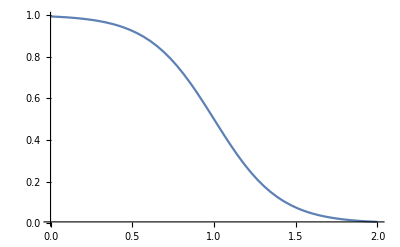

```mathematica
Plot[(1+Exp[5(ϵ-1)])^-1,{ϵ,0,2},PlotRange->Full]
```

```mathematica
Block[{ϵ=10^-4,n=5,μ=1.5},Sum[(Energies[k[[1]]+ϵ,k[[2]]][[n]]+Energies[k[[1]]-ϵ,k[[2]]][[n]]-2Energies[k[[1]],k[[2]]][[n]])/ϵ^2 HeavisideTheta[-(Energies[k[[1]],k[[2]]][[n]]-μ)],{k,kSpan}]/Length[kSpan]]//AbsoluteTiming
```

{2.56834,0.106931+0. ⅈ}

```mathematica
Block[{ϵ=10^-4,n=5,μ=1.5},Sum[(Energies[k[[1]]+ϵ,k[[2]]][[n]]+Energies[k[[1]]-ϵ,k[[2]]][[n]]-2Energies[k[[1]],k[[2]]][[n]])/ϵ^2(1+Exp[10(Energies[k[[1]],k[[2]]][[n]]-μ)])^-1,{k,kSpan}]/Length[kSpan]]//AbsoluteTiming
```

{2.76613,0.107188-5.12542×10^-15 ⅈ}

```mathematica
Block[{ϵ=10^-4,n=6,μ=1.5},Sum[(Energies[k[[1]]+ϵ,k[[2]]][[n]]+Energies[k[[1]]-ϵ,k[[2]]][[n]]-2Energies[k[[1]],k[[2]]][[n]])/ϵ^2(1+Exp[10(Energies[k[[1]],k[[2]]][[n]]-μ)])^-1,{k,kSpan}]/Length[kSpan]]//AbsoluteTiming
```

{2.56829,1.32398×10^-7+8.73345×10^-20 ⅈ}

```mathematica
RhosVsT=Block[{ϵ=10^-4,μ=1.5},Table[{1/β,Sum[(Energies[k[[1]]+ϵ,k[[2]],μ][[n]]+Energies[k[[1]]-ϵ,k[[2]],μ][[n]]-2Energies[k[[1]],k[[2]],μ][[n]])/ϵ^2 (1+Exp[β(Energies[k[[1]],k[[2]],μ][[n]])])^-1,{n,{5,6}},{k,kSpan}]/Length[kSpan]},{β,5.0,100.,1.0}]]
```

{{0.2,0.105258-3.31661×10^-12 ⅈ},{0.166667,0.106106-9.07033×10^-13 ⅈ},{0.142857,0.106576-2.48059×10^-13 ⅈ},{0.125,0.106864-6.79333×10^-14 ⅈ},{0.111111,0.107055-1.86396×10^-14 ⅈ},{0.1,0.107188-5.12533×10^-15 ⅈ},{0.0909091,0.107285-1.41257×10^-15 ⅈ},{0.0833333,0.107357-3.90255×10^-16 ⅈ},{0.0769231,0.107412-1.08089×10^-16 ⅈ},{0.0714286,0.107453-3.00157×10^-17 ⅈ},{0.0666667,0.107484-8.35757×10^-18 ⅈ},{0.0625,0.107506-2.33347×10^-18 ⅈ},{0.0588235,0.107522-6.53338×10^-19 ⅈ},{0.0555556,0.107532-1.83442×10^-19 ⅈ},{0.0526316,0.107538-5.16527×10^-20 ⅈ},{0.05,0.10754-1.45855×10^-20 ⅈ},{0.047619,0.107539-4.13027×10^-21 ⅈ},{0.0454545,0.107535-1.17287×10^-21 ⅈ},{0.0434783,0.107529-3.33978×10^-22 ⅈ},{0.0416667,0.107521-9.53578×10^-23 ⅈ},{0.04,0.107512-2.72982×10^-23 ⅈ},{0.0384615,0.107501-7.83457×10^-24 ⅈ},{0.037037,0.10749-2.25404×10^-24 ⅈ},{0.0357143,0.107478-6.50021×10^-25 ⅈ},{0.0344828,0.107465-1.87875×10^-25 ⅈ},{0.0333333,0.107452-5.44175×10^-26 ⅈ},{0.0322581,0.107438-1.57938×10^-26 ⅈ},{0.03125,0.107425-4.59264×10^-27 ⅈ},{0.030303,0.107411-1.33788×10^-27 ⅈ},{0.0294118,0.107397-3.90394×10^-28 ⅈ},{0.0285714,0.107384-1.14096×10^-28 ⅈ},{0.0277778,0.10737-3.33945×10^-29 ⅈ},{0.027027,0.107357-9.78743×10^-30 ⅈ},{0.0263158,0.107344-2.87217×10^-30 ⅈ},{0.025641,0.107331-8.43835×10^-31 ⅈ},{0.025,0.107318-2.48183×10^-31 ⅈ},{0.0243902,0.107306-7.30666×10^-32 ⅈ},{0.0238095,0.107294-2.15309×10^-32 ⅈ},{0.0232558,0.107282-6.34994×10^-33 ⅈ},{0.0227273,0.10727-1.87418×10^-33 ⅈ},{0.0222222,0.107259-5.53556×10^-34 ⅈ},{0.0217391,0.107248-1.63604×10^-34 ⅈ},{0.0212766,0.107238-4.83819×10^-35 ⅈ},{0.0208333,0.107227-1.43156×10^-35 ⅈ},{0.0204082,0.107217-4.23791×10^-36 ⅈ},{0.02,0.107208-1.25514×10^-36 ⅈ},{0.0196078,0.107198-3.71891×10^-37 ⅈ},{0.0192308,0.107189-1.10232×10^-37 ⅈ},{0.0188679,0.10718-3.2685×10^-38 ⅈ},{0.0185185,0.107172-9.69462×10^-39 ⅈ},{0.0181818,0.107163-2.87635×10^-39 ⅈ},{0.0178571,0.107155-8.53635×10^-40 ⅈ},{0.0175439,0.107148-2.53402×10^-40 ⅈ},{0.0172414,0.10714-7.52401×10^-41 ⅈ},{0.0169492,0.107133-2.2345×10^-41 ⅈ},{0.0166667,0.107126-6.63739×10^-42 ⅈ},{0.0163934,0.107119-1.97194×10^-42 ⅈ},{0.016129,0.107113-5.85951×10^-43 ⅈ},{0.015873,0.107106-1.7414×10^-43 ⅈ},{0.015625,0.1071-5.17605×10^-44 ⅈ},{0.0153846,0.107094-1.53871×10^-44 ⅈ},{0.0151515,0.107088-4.57479×10^-45 ⅈ},{0.0149254,0.107083-1.36031×10^-45 ⅈ},{0.0147059,0.107078-4.0453×10^-46 ⅈ},{0.0144928,0.107072-1.20312×10^-46 ⅈ},{0.0142857,0.107067-3.57859×10^-47 ⅈ},{0.0140845,0.107063-1.06452×10^-47 ⅈ},{0.0138889,0.107058-3.16691×10^-48 ⅈ},{0.0136986,0.107053-9.4222×10^-49 ⅈ},{0.0135135,0.107049-2.80352×10^-49 ⅈ},{0.0133333,0.107045-8.34234×10^-50 ⅈ},{0.0131579,0.107041-2.48258×10^-50 ⅈ},{0.012987,0.107037-7.38837×10^-51 ⅈ},{0.0128205,0.107033-2.19899×10^-51 ⅈ},{0.0126582,0.10703-6.54522×10^-52 ⅈ},{0.0125,0.107026-1.94828×10^-52 ⅈ},{0.0123457,0.107023-5.7997×10^-53 ⅈ},{0.0121951,0.10702-1.72657×10^-53 ⅈ},{0.0120482,0.107016-5.14027×10^-54 ⅈ},{0.0119048,0.107013-1.53042×10^-54 ⅈ},{0.0117647,0.10701-4.55678×10^-55 ⅈ},{0.0116279,0.107008-1.35684×10^-55 ⅈ},{0.0114943,0.107005-4.04034×10^-56 ⅈ},{0.0113636,0.107002-1.20317×10^-56 ⅈ},{0.011236,0.107-3.5831×10^-57 ⅈ},{0.0111111,0.106997-1.06711×10^-57 ⅈ},{0.010989,0.106995-3.17817×10^-58 ⅈ},{0.0108696,0.106993-9.46596×10^-59 ⅈ},{0.0107527,0.10699-2.81949×10^-59 ⅈ},{0.0106383,0.106988-8.39833×10^-60 ⅈ},{0.0105263,0.106986-2.50169×10^-60 ⅈ},{0.0104167,0.106984-7.4523×10^-61 ⅈ},{0.0103093,0.106982-2.22006×10^-61 ⅈ},{0.0102041,0.106981-6.61384×10^-62 ⅈ},{0.010101,0.106979-1.97042×10^-62 ⅈ},{0.01,0.106977-5.87058×10^-63 ⅈ}}

```mathematica
β
```

6.

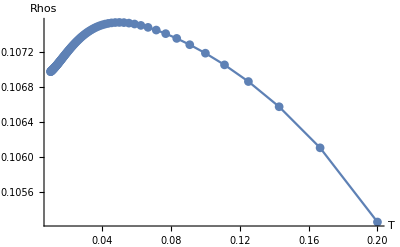

```mathematica
ListPlot[RhosVsT,AxesLabel->{T,Rhos},PlotRange->Full,Joined->True,PlotMarkers->Automatic]
```

#### From vish6_nvSCv1.nb on 19th Sep

```mathematica
Nsites=300;
kSpan=N[Flatten[Table[i*{(2π)/(√3),2π}+j*{(4π)/(√3),0},{i,0,0.999,1/Nsites},{j,0,0.999,1/Nsites}],1]];
ProgresskSpace[]:={Position[kSpan,k][[1,1]],Length[kSpan]};
```

```mathematica
phi[m_,n_,kx_,ky_] := ExpToTrig[E^(-I (ky(n -m/2) + kx m (√3)/2))];
ω = ExpToTrig[E^(I 2 π/3)]; ωc = Conjugate[ω];
```

```mathematica
Hpz[kx_,ky_] := 0.17(phi[0,1,kx,ky] + phi[1,1,kx,ky] + phi[1,0,kx,ky] + Conjugate[phi[0,1,kx,ky] + phi[1,1,kx,ky] + phi[1,0,kx,ky]]) -1.02;
```

```mathematica
Cpm[kx_,ky_] := -0.065(phi[0,1,kx,ky] + ω phi[-1,-1,kx,ky] + ωc phi[1,0,kx,ky]) - 0.055(phi[0,-1,kx,ky] + ω phi[1,1,kx,ky] + ωc phi[-1,0,kx,ky]);
```

```mathematica
Hpm[kx_,ky_] := (-0.017(phi[0,1,kx,ky] + phi[1,1,kx,ky] + phi[1,0,kx,ky] + Conjugate[phi[0,1,kx,ky] + phi[1,1,kx,ky] + phi[1,0,kx,ky]]) - 0.281){{1,0},{0,1}} + {{0,Conjugate[Cpm[kx,ky]]},{Cpm[kx,ky],0}};
```

```mathematica
Hk[kx_,ky_] := {{0,phi[-1,0,kx,ky],1},{1,0,phi[0,-1,kx,ky]},{phi[1,1,kx,ky],1,0}} + 0.25 {{0,phi[-1,-1,kx,ky],phi[-1,0,kx,ky]},{phi[0,-1,kx,ky],0,phi[1,0,kx,ky]},{phi[0,1,kx,ky],phi[1,1,kx,ky],0}} + ConjugateTranspose[{{0,phi[-1,0,kx,ky],1},{1,0,phi[0,-1,kx,ky]},{phi[1,1,kx,ky],1,0}} + 0.25 {{0,phi[-1,-1,kx,ky],phi[-1,0,kx,ky]},{phi[0,-1,kx,ky],0,phi[1,0,kx,ky]},{phi[0,1,kx,ky],phi[1,1,kx,ky],0}}] - 4.75{{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
C12[kx_,ky_] :=Transpose[ I 0.095 {{phi[0,1,kx,ky] + ω phi[-1,-1,kx,ky] + ωc phi[1,0,kx,ky],-(phi[0,-1,kx,ky] + ωc phi[1,1,kx,ky] + ω phi[-1,0,kx,ky])}} - I 0.055{{phi[0,-1,kx,ky] + ω phi[1,1,kx,ky] + ωc phi[-1,0,kx,ky],-(phi[0,1,kx,ky] + ωc phi[-1,-1,kx,ky] + ω phi[1,0,kx,ky])}}];
```

```mathematica
C23[kx_,ky_] := 0.6 {{phi[-1,0,kx,ky],phi[-1,-1,kx,ky]},{phi[-1,-1,kx,ky] ωc, ω},{ω, ωc phi[-1,0,kx,ky]}} - 0.2 {{phi[-1,-1,kx,ky],phi[-1,0,kx,ky]},{ ωc, phi[-1,-1,kx,ky]ω},{phi[-1,0,kx,ky]ω, ωc }};
```

```mathematica
HamMatrx[kx_,ky_] = {{Hpz[kx,ky], C12[kx,ky]†,ConstantArray[0,{1,3}] },{C12[kx,ky], Hpm[kx,ky], C23[kx,ky]†},{ConstantArray[0,{3,1}],C23[kx,ky],Hk[kx,ky]}};
```

```mathematica
HamVish[kx_,ky_] = 27 ArrayFlatten[HamMatrx[kx,ky]];
```

```mathematica
EnergiesVish[kx_,ky_] :=EnergiesVish[kx,ky]= Eigenvalues[HamVish[kx,ky]]//N//Sort;
```

```mathematica
Clear[CurvatureVish];CurvatureVish[kx_,ky_] :=CurvatureVish[kx,ky]=Block[{ϵ=10^-2},Table[1/ϵ^2(EnergiesVish[kx+ϵ,ky][[n]]+EnergiesVish[kx-ϵ,ky][[n]]-2EnergiesVish[kx,ky][[n]]),{n,6}]];
```

```mathematica
Clear[CurvatureVishyy];CurvatureVishyy[kx_,ky_] :=CurvatureVishyy[kx,ky]=Block[{ϵ=10^-2},Table[1/ϵ^2(EnergiesVish[kx,ky+ϵ][[n]]+EnergiesVish[kx,ky-ϵ][[n]]-2EnergiesVish[kx,ky][[n]]),{n,6}]];
```

```mathematica
Clear[fillingVish];fillingVish[μ_,Δ_] := Sum[ 1/2(1-(EnergiesVish[ k[[1]],k[[2]]][[n]]-μ)/(√((EnergiesVish[ k[[1]],k[[2]] ] [[n]]-μ)^2+ Δ^2+10^-10))),{n,{5,6}},{k,kSpan}]/Length[kSpan];
```

```mathematica
fillingVish[3.5,0.0]
```

$Aborted

```mathematica
fillingVishT[3.5,0.0]
```

General::munfl: Exp[-3.5×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.47436×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.39922×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.00389

```mathematica
Clear[fillingVishT];fillingVishT[μ_,T_] := Sum[(1+Exp[(EnergiesVish[ k[[1]],k[[2]]][[n]]-μ)/(T+0.000000001)])^-1 ,{n,{5,6}},{k,kSpan}]/Length[kSpan];
```

```mathematica
Clear[Rho0Vish];Rho0Vish[μ_,Δ_]:=Sum[CurvatureVish[ k[[1]],k[[2]]][[n]] 1/2(1-(EnergiesVish[ k[[1]],k[[2]]][[n]]-μ)/(√((EnergiesVish[ k[[1]],k[[2]] ] [[n]]-μ)^2+ Δ^2+10^-10))),{n,{5,6}},{k,kSpan}]/Length[kSpan];
```

```mathematica
Clear[Rho0Vishyy];Rho0Vishyy[μ_,Δ_]:=Sum[CurvatureVishyy[ k[[1]],k[[2]]][[n]] 1/2(1-(EnergiesVish[ k[[1]],k[[2]]][[n]]-μ)/(√((EnergiesVish[ k[[1]],k[[2]] ] [[n]]-μ)^2+ Δ^2+10^-10))),{n,{5,6}},{k,kSpan}]/Length[kSpan];
```

```mathematica
Clear[DTVish];DTVish[μ_,T_]:=Block[{},Print[T];Sum[CurvatureVish[ k[[1]],k[[2]]][[n]](1+Exp[(EnergiesVish[ k[[1]],k[[2]]][[n]]-μ)/(T+0.000000001)])^-1,{n,{5,6}},{k,kSpan}]/Length[kSpan]];
```

```mathematica
Block[{},
Clear[DTVish];DTVish[μ_,T_]:=DTVish[μ,T]=Chop[(*Block[{},Print[T];*)Sum[CurvatureVish[ k[[1]],k[[2]]][[n]](1+Exp[(EnergiesVish[ k[[1]],k[[2]]][[n]]-μ)/(T+0.000000001)])^-1,{n,{5,6}},{k,kSpan}]/Length[kSpan](*]*)];
Clear[DTVishSelfCons];DTVishSelfCons[μ_]:=Nest[DTVish[μ,π*#/2]&,0.0,20];
DTVishSelfCons[2.8]]
```

0.

General::munfl: Exp[-2.8×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.79898×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.7959×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.131066

0.125687

0.125911

0.125902

0.125902

0.125902

«6 more identical outputs»

0.0801519

```mathematica
halfFillVish[Δ_] := μ/.FindRoot[filling[μ,Δ] - 1,{μ,3.0},PrecisionGoal->0.001];
```

```mathematica
nFillVish[Δ_,n_] := μ/.FindRoot[filling[μ,Δ] - n,{μ,3.0},PrecisionGoal->0.001];
```

```mathematica
Sum[CurvatureVish[k[[1]],k[[2]]],{k,kSpan}]*11.6045*(π/8)*4/Length[kSpan]
```

{-0.406102-4.58121×10^-14 ⅈ,-7.87385-9.03357×10^-14 ⅈ,6.93219+1.735×10^-13 ⅈ,1.34777-1.43269×10^-15 ⅈ,-0.256505+1.06232×10^-13 ⅈ,0.256505+1.77055×10^-13 ⅈ}

```mathematica
Sum[Abs[CurvatureVish[k[[1]],k[[2]]]],{k,kSpan}]*11.6045*(π/8)*4/Length[kSpan]
```

{140.596,262.532,316.151,86.8771,7.99356,10.283}

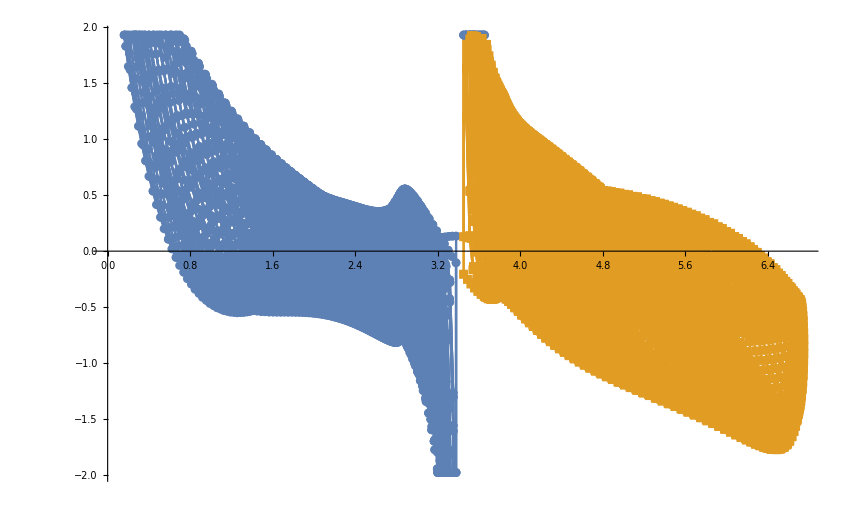

```mathematica
ListPlot[{Table[{EnergiesVish[k[[1]],k[[2]]][[5]],CurvatureVish[k[[1]],k[[2]]][[5]]},{k,kSpan}],Table[{EnergiesVish[k[[1]],k[[2]]][[6]],CurvatureVish[k[[1]],k[[2]]][[6]]},{k,kSpan}]},PlotRange->Automatic,Joined->True,PlotMarkers->Automatic]
```

```mathematica
{ListPlot3D[Table[Block[{μ=2.0,Δ=0.05},Table[{k[[1]],k[[2]],EnergiesVish[k[[1]],k[[2]]][[n]]},{k,kSpan}]],{n,{5,6}}],PlotRange->Full,ColorFunction->"Rainbow",ImageSize->Medium,PlotLegends->Automatic],ListPlot3D[Table[Block[{μ=2.0,Δ=0.05},Table[{k[[1]],k[[2]],CurvatureVish[k[[1]],k[[2]]][[n]]},{k,kSpan}]],{n,{5,6}}],(*PlotRange->Full,*)ImageSize->Medium,PlotLegends->Automatic]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
ProgresskSpace[]
```

{10257,14400}

```mathematica
(*DiscretePlot3D[{Energies[kx,ky][[5]],Energies[kx,ky][[6]]},{ky,-4 π/3,4 π/3,0.02},{kx,-π/(√3),π/(√3),0.02},Filling->None,Joined->True]*)
```

```mathematica
arrc=Select[arr,Abs[π/2*#[[4]]]<#[[2]]/1.76&&#[[4]]>0&];
```

```mathematica
arrc=Table[If[Abs[π/2*dat[[4]]]<dat[[2]]/1.76&&dat[[4]]>0,dat,{dat[[1]],dat[[2]],dat[[3]],1000}],{dat,arr}];
```

```mathematica
Show[Plot[Join[Table[0.5x+r*0.1,{r,-20.,20.,0.5}],Table[-0.5x+r*0.1,{r,-20.,20.,0.5}]],{x,0.,2.},AspectRatio->1,PlotRange->{0.,1.},PlotLabel->"T_C(K)",PlotStyle->Directive[Thin,Gray],PlotRangePadding->None,LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],Frame->True,FrameLabel->{{"Δ",None},{"n",None}}],
ListContourPlot[({arrc[[All,3]],arrc[[All,2]],11.6045*(π/8)*4*Re[arrc[[All,4]]]}//Transpose),LabelStyle->Directive[FontFamily->"Calibri",20,Black],PlotRange->{Automatic,Automatic,{0,3.6}},Contours->17,PlotLegends->Automatic,PlotRangePadding->None,AxesOrigin->{0.,0.},ColorFunction->"ThermometerColors"]]
```

-Graphics-

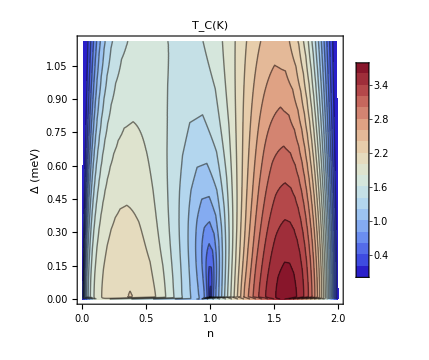
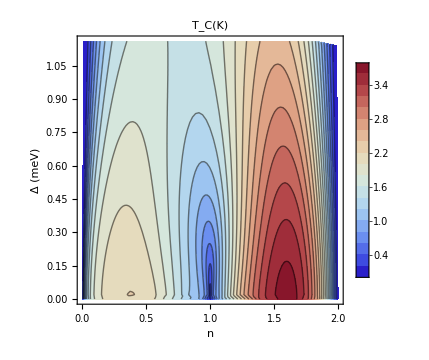

```mathematica
Row[{arr=arrVish[[;;Quotient[Length[arrVish],3]]];Show[ListContourPlot[({arr[[All,3]],arr[[All,2]],11.6045*(π/8)*4*Re[arr[[All,4]]]}//Transpose),PlotRange->{Automatic,Automatic,{0,3.8}},PlotLabel->"T_C(K)",PlotRangePadding->None,LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],Frame->True,FrameLabel->{{"Δ (meV)",None},{"n",None}},Contours->18,PlotLegends->Automatic,AxesOrigin->{0.,0.},ColorFunction->"ThermometerColors",ImageSize->Medium]],
arr=arrVishyy[[;;Quotient[Length[arrVishyy],3]]];Show[ListContourPlot[({arr[[All,3]],arr[[All,2]],11.6045*(π/8)*4*Re[arr[[All,4]]]}//Transpose),PlotRange->{Automatic,Automatic,{0,3.8}},PlotLabel->"T_C(K)",PlotRangePadding->None,LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],Frame->True,FrameLabel->{{"Δ (meV)",None},{"n",None}},Contours->18,PlotLegends->Automatic,AxesOrigin->{0.,0.},ColorFunction->"ThermometerColors",ImageSize->Medium]]}]
```

```mathematica
ListPlot3D[{arrVish[[All,{3,2,4}]],arrVishyy[[All,{3,2,4}]]},InterpolationOrder->None]
```

-Graphics3D-

```mathematica
arr=arrVishyy[[;;Quotient[Length[arrVishyy],3]]];Show[ListContourPlot[({arr[[All,3]],arr[[All,2]],11.6045*(π/8)*4*Re[arr[[All,4]]]}//Transpose),PlotRange->{Automatic,Automatic,{0,3.8}},PlotLabel->"T_C(K)",PlotRangePadding->None,LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],Frame->True,FrameLabel->{{"Δ (meV)",None},{"n",None}},Contours->18,PlotLegends->Automatic,AxesOrigin->{0.,0.},ColorFunction->"ThermometerColors",Mesh->All]]
```

-Graphics-

```mathematica
DdataVishSelfCons=Table[{4.0*(fillingVish[μ,0.0]-1.0),
Clear[DTVish];DTVish[μu_,T_]:=DTVish[μu,T]=Chop[(*Block[{},Print[T];*)Sum[CurvatureVish[ k[[1]],k[[2]]][[n]](1+Exp[(EnergiesVish[ k[[1]],k[[2]]][[n]]-μu)/(T+0.000000001)])^-1,{n,{5,6}},{k,kSpan}]/Length[kSpan](*]*)];
Nest[DTVish[μ,π*#/2]&,0.0,20]},{μ,0.0,7.5,0.1}]
```

General::munfl: Exp[-1.×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.89767×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.58988×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-3.99998-3.27729×10^-30 ⅈ,0.0000193813},{-3.98356-3.62163×10^-30 ⅈ,0.0131427},{-3.96596-4.01639×10^-30 ⅈ,0.0250492},{-3.94542-4.47103×10^-30 ⅈ,0.0358477},{-3.92329-4.99768×10^-30 ⅈ,0.0456416},{-3.90076-5.61119×10^-30 ⅈ,0.0545169},{-3.87342-6.33037×10^-30 ⅈ,0.062547},{-3.84436-7.17912×10^-30 ⅈ,0.0697964},{-3.81289-8.18843×10^-30 ⅈ,0.0763236},{-3.77649-9.39829×10^-30 ⅈ,0.0821828},{-3.73769-1.08615×10^-29 ⅈ,0.0874259},{-3.69462-1.26493×10^-29 ⅈ,0.0921031},{-3.64569-1.48571×10^-29 ⅈ,0.0962636},{-3.59036-1.76182×10^-29 ⅈ,0.0999551},{-3.53075-2.11188×10^-29 ⅈ,0.103223},{-3.46209-2.56282×10^-29 ⅈ,0.106105},{-3.38542-3.15424×10^-29 ⅈ,0.108633},{-3.30061-3.94638×10^-29 ⅈ,0.110819},{-3.20404-5.03371×10^-29 ⅈ,0.112651},{-3.09396-6.57065×10^-29 ⅈ,0.114083},{-2.9713-8.82179×10^-29 ⅈ,0.115027},{-2.83276-1.22687×10^-28 ⅈ,0.115351},{-2.67674-1.78575×10^-28 ⅈ,0.114878},{-2.50182-2.76513×10^-28 ⅈ,0.113389},{-2.30339-4.68838×10^-28 ⅈ,0.110628},{-2.07796-9.25552×10^-28 ⅈ,0.106297},{-1.81424-2.5442×10^-27 ⅈ,0.100046},{-1.49158-2.41896×10^-26 ⅈ,0.0914646},{-1.02119-2.12267×10^-25 ⅈ,0.0801519},{-0.476345-9.79534×10^-26 ⅈ,0.0662811},{-0.283814-1.45803×10^-23 ⅈ,0.0522922},{-0.154755-7.39812×10^-26 ⅈ,0.0404518},{-0.0699555-8.56426×10^-27 ⅈ,0.0286754},{-0.0192855-2.67103×10^-27 ⅈ,0.0156909},{-0.0000889277-1.36003×10^-27 ⅈ,0.00195822},{0.0107556-1.21802×10^-27 ⅈ,0.0118054},{0.0528898-2.64049×10^-27 ⅈ,0.0254635},{0.131822-3.80834×10^-26 ⅈ,0.0465966},{0.272348-1.39453×10^-25 ⅈ,0.0810496},{0.82929-3.45757×10^-23 ⅈ,0.106906},{1.16115-7.61325×10^-27 ⅈ,0.126102},{1.41529-1.67332×10^-27 ⅈ,0.141},{1.62676-6.08833×10^-28 ⅈ,0.152779},{1.81356-2.94179×10^-28 ⅈ,0.1621},{1.9789-1.67842×10^-28 ⅈ,0.169373},{2.12797-1.06599×10^-28 ⅈ,0.174875},{2.26422-7.28995×10^-29 ⅈ,0.178797},{2.39129-5.25967×10^-29 ⅈ,0.18128},{2.50738-3.95081×10^-29 ⅈ,0.182434},{2.61721-3.06183×10^-29 ⅈ,0.182339},{2.71902-2.43258×10^-29 ⅈ,0.181064},{2.81529-1.97208×10^-29 ⅈ,0.178662},{2.90729-1.62572×10^-29 ⅈ,0.17518},{2.99422-1.3592×10^-29 ⅈ,0.170657},{3.07702-1.1501×10^-29 ⅈ,0.165127},{3.15622-9.83315×10^-30 ⅈ,0.15862},{3.23276-8.48365×10^-30 ⅈ,0.151162},{3.30747-7.37796×10^-30 ⅈ,0.142773},{3.37902-6.46193×10^-30 ⅈ,0.133467},{3.44662-5.6958×10^-30 ⅈ,0.12325},{3.51369-5.04915×10^-30 ⅈ,0.112117},{3.58076-4.4992×10^-30 ⅈ,0.100052},{3.64476-4.02811×10^-30 ⅈ,0.0870265},{3.70835-3.62191×10^-30 ⅈ,0.0730011},{3.77209-3.2697×10^-30 ⅈ,0.0579299},{3.83515-2.96246×10^-30 ⅈ,0.0417898},{3.89996-2.69329×10^-30 ⅈ,0.0247027},{3.96645-2.45629×10^-30 ⅈ,0.00756483},{4.-2.24677×10^-30 ⅈ,0},{4.-2.06065×10^-30 ⅈ,0},{4.-1.89491×10^-30 ⅈ,0},{4.-1.74669×10^-30 ⅈ,0},{4.-1.6137×10^-30 ⅈ,0},{4.-1.49403×10^-30 ⅈ,0},{4.-1.38608×10^-30 ⅈ,0},{4.-1.2884×10^-30 ⅈ,0}}

```mathematica
Length[DdataVishSelfCons]
```

76

```mathematica
DdataVishSelfCons[[34;;37]]
```

{{-0.0222887,0.0156909},{-0.00217915,0.00195822},{0.0127908,0.0118054},{0.0635071,0.0254635}}

```mathematica
DdataVishSelfCons=Table[Block[{D=DdataVishSelfCons[[i,2]]},{4.0*(fillingVishT[Range[0.0,7.5,0.1][[i]],π/2*D]-1.0),D}],{i,Length[DdataVishSelfCons]}]
```

General::munfl: Exp[-1105.35] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1097.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1072.58] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-3.99944,0.0000193813},{-3.98311,0.0131427},{-3.96483,0.0250492},{-3.94442,0.0358477},{-3.92182,0.0456416},{-3.89678,0.0545169},{-3.86902,0.062547},{-3.83822,0.0697964},{-3.80401,0.0763236},{-3.76594,0.0821828},{-3.72352,0.0874259},{-3.67615,0.0921031},{-3.62317,0.0962636},{-3.56382,0.0999551},{-3.4972,0.103223},{-3.42234,0.106105},{-3.33813,0.108633},{-3.24333,0.110819},{-3.13662,0.112651},{-3.01657,0.114083},{-2.88166,0.115027},{-2.73031,0.115351},{-2.56088,0.114878},{-2.3716,0.113389},{-2.16047,0.110628},{-1.92516,0.106297},{-1.66273,0.100046},{-1.36961,0.0914646},{-1.04328,0.0801519},{-0.694192,0.0662811},{-0.384811,0.0522922},{-0.189095,0.0404518},{-0.081124,0.0286754},{-0.0222887,0.0156909},{-0.00217915,0.00195822},{0.0127908,0.0118054},{0.0635071,0.0254635},{0.223604,0.0465966},{0.545228,0.0810496},{0.823134,0.106906},{1.06077,0.126102},{1.27302,0.141},{1.467,0.152779},{1.64653,0.1621},{1.81394,0.169373},{1.97076,0.174875},{2.11809,0.178797},{2.25677,0.18128},{2.38746,0.182434},{2.51074,0.182339},{2.62709,0.181064},{2.73697,0.178662},{2.84081,0.17518},{2.93904,0.170657},{3.03207,0.165127},{3.12034,0.15862},{3.20427,0.151162},{3.2843,0.142773},{3.36086,0.133467},{3.43437,0.12325},{3.50525,0.112117},{3.57389,0.100052},{3.64068,0.0870265},{3.70607,0.0730011},{3.77057,0.0579299},{3.83483,0.0417898},{3.89983,0.0247027},{3.96664,0.00756483},{4.,0},{4.,0},{4.,0},{4.,0},{4.,0},{4.,0},{4.,0},{4.,0}}

```mathematica
DdataVishSelfConsFine=ParallelTable[{4.0*(fillingVish[μ,0.0]-1.0),
Clear[DTVish];DTVish[μu_,T_]:=DTVish[μu,T]=Chop[(*Block[{},Print[T];*)Sum[CurvatureVish[ k[[1]],k[[2]]][[n]](1+Exp[(EnergiesVish[ k[[1]],k[[2]]][[n]]-μu)/(T+0.000000001)])^-1,{n,{5,6}},{k,kSpan}]/Length[kSpan](*]*)];
Nest[DTVish[μ,π*#/2]&,0.0,20]},{μ,3.0,4.0,0.02}]
```

General::munfl: Exp[-3.×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.18×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.99898×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.17898×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.9959×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.1759×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.36×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.35898×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.3559×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.54×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.53898×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.5359×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.7×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.69898×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.6959×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.86×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.85898×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.8559×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-0.283814-1.45803×10^-23 ⅈ,0.0522922},{-0.253156-7.51904×10^-21 ⅈ,0.0497806},{-0.226482-1.55233×10^-23 ⅈ,0.0473657},{-0.20062-4.98216×10^-25 ⅈ,0.0450241},{-0.176088-1.5946×10^-25 ⅈ,0.0427285},{-0.154755-7.39812×10^-26 ⅈ,0.0404518},{-0.133956-4.09798×10^-26 ⅈ,0.03817},{-0.115822-2.52717×10^-26 ⅈ,0.0358635},{-0.0979942-1.67671×10^-26 ⅈ,0.0335179},{-0.0835536-1.17375×10^-26 ⅈ,0.0311235},{-0.0699555-8.56426×10^-27 ⅈ,0.0286754},{-0.0558224-6.46073×10^-27 ⅈ,0.0261728},{-0.045156-5.01103×10^-27 ⅈ,0.023618},{-0.0352889-3.98042×10^-27 ⅈ,0.0210155},{-0.0264904-3.2293×10^-27 ⅈ,0.018371},{-0.0192855-2.67103×10^-27 ⅈ,0.0156909},{-0.013413-2.24997×10^-27 ⅈ,0.0129815},{-0.00782223-1.92939×10^-27 ⅈ,0.0102488},{-0.00488861-1.68454×10^-27 ⅈ,0.00749906},{-0.00168889-1.49856×10^-27 ⅈ,0.00473806},{-0.0000889277-1.36003×10^-27 ⅈ,0.00195822},{0.000088889-1.26145×10^-27 ⅈ,0.00117164},{0.00113165-1.19837×10^-27 ⅈ,0.00356357},{0.00328888-1.16902×10^-27 ⅈ,0.00632199},{0.00648886-1.17425×10^-27 ⅈ,0.00906993},{0.0107556-1.21802×10^-27 ⅈ,0.0118054},{0.016906-1.30843×10^-27 ⅈ,0.0145275},{0.0235557-1.45986×10^-27 ⅈ,0.0172375},{0.0320887-1.69716×10^-27 ⅈ,0.0199432},{0.0411557-2.06395×10^-27 ⅈ,0.0226677},{0.0528898-2.64049×10^-27 ⅈ,0.0254635},{0.0648888-3.58532×10^-27 ⅈ,0.0284316},{0.0792889-5.24374×10^-27 ⅈ,0.0317458},{0.0950226-8.4767×10^-27 ⅈ,0.0356761},{0.112091-1.58878×10^-26 ⅈ,0.0405589},{0.131822-3.80834×10^-26 ⅈ,0.0465966},{0.153171-1.49×10^-25 ⅈ,0.0535513},{0.177421-2.5676×10^-24 ⅈ,0.0608404},{0.20489-1.04965×10^-23 ⅈ,0.0679774},{0.235556-1.25362×10^-24 ⅈ,0.074734},{0.272348-1.39453×10^-25 ⅈ,0.0810496},{0.332477-4.2726×10^-25 ⅈ,0.0869353},{0.484091-1.26313×10^-21 ⅈ,0.0924261},{0.638855-5.87919×10^-25 ⅈ,0.097561},{0.741754+9.59512×10^-23 ⅈ,0.102377},{0.82929-3.45757×10^-23 ⅈ,0.106906},{0.906538+3.23028×10^-24 ⅈ,0.111177},{0.976355+8.06726×10^-26 ⅈ,0.115213},{1.04255-7.62293×10^-27 ⅈ,0.119034},{1.10268-1.02955×10^-26 ⅈ,0.122659},{1.16115-7.61325×10^-27 ⅈ,0.126102}}

```mathematica
DdataVish=Table[{4.0*(fillingVish[μ,0.0]-1.0),Rho0Vish[μ,0.0]},{μ,0.0,7.5,0.1}]
```

{{-3.99998-3.27729×10^-30 ⅈ,0.0000193884-1.7274×10^-26 ⅈ},{-3.98356-3.62163×10^-30 ⅈ,0.013131-1.85213×10^-26 ⅈ},{-3.96596-4.01639×10^-30 ⅈ,0.0249099-1.9909×10^-26 ⅈ},{-3.94542-4.47103×10^-30 ⅈ,0.0363572-2.14562×10^-26 ⅈ},{-3.92329-4.99768×10^-30 ⅈ,0.0465572-2.31905×10^-26 ⅈ},{-3.90076-5.61119×10^-30 ⅈ,0.0551712-2.51421×10^-26 ⅈ},{-3.87342-6.33037×10^-30 ⅈ,0.0637983-2.73493×10^-26 ⅈ},{-3.84436-7.17912×10^-30 ⅈ,0.0712669-2.98579×10^-26 ⅈ},{-3.81289-8.18843×10^-30 ⅈ,0.0778798-3.27255×10^-26 ⅈ},{-3.77649-9.39829×10^-30 ⅈ,0.0840539-3.60237×10^-26 ⅈ},{-3.73769-1.08615×10^-29 ⅈ,0.0893242-3.98424×10^-26 ⅈ},{-3.69462-1.26493×10^-29 ⅈ,0.0939644-4.42975×10^-26 ⅈ},{-3.64569-1.48571×10^-29 ⅈ,0.0981374-4.95371×10^-26 ⅈ},{-3.59036-1.76182×10^-29 ⅈ,0.101871-5.57566×10^-26 ⅈ},{-3.53075-2.11188×10^-29 ⅈ,0.104956-6.32149×10^-26 ⅈ},{-3.46209-2.56282×10^-29 ⅈ,0.107778-7.22641×10^-26 ⅈ},{-3.38542-3.15424×10^-29 ⅈ,0.1102-8.33894×10^-26 ⅈ},{-3.30061-3.94638×10^-29 ⅈ,0.11235-9.72763×10^-26 ⅈ},{-3.20404-5.03371×10^-29 ⅈ,0.114298-1.14921×10^-25 ⅈ},{-3.09396-6.57065×10^-29 ⅈ,0.116027-1.37817×10^-25 ⅈ},{-2.9713-8.82179×10^-29 ⅈ,0.117831-1.68286×10^-25 ⅈ},{-2.83276-1.22687×10^-28 ⅈ,0.119205-2.10125×10^-25 ⅈ},{-2.67674-1.78575×10^-28 ⅈ,0.120358-2.69912×10^-25 ⅈ},{-2.50182-2.76513×10^-28 ⅈ,0.120946-3.60051×10^-25 ⅈ},{-2.30339-4.68838×10^-28 ⅈ,0.120442-5.06971×10^-25 ⅈ},{-2.07796-9.25552×10^-28 ⅈ,0.118224-7.79848×10^-25 ⅈ},{-1.81424-2.5442×10^-27 ⅈ,0.113185-1.45436×10^-24 ⅈ},{-1.49158-2.41896×10^-26 ⅈ,0.103472-6.11006×10^-24 ⅈ},{-1.02119-2.12267×10^-25 ⅈ,0.0834426-9.07509×10^-16 ⅈ},{-0.476345-9.79534×10^-26 ⅈ,0.0597577+1.46153×10^-16 ⅈ},{-0.283814-1.45803×10^-23 ⅈ,0.0517079-4.37949×10^-15 ⅈ},{-0.154755-7.39812×10^-26 ⅈ,0.0412031-6.72483×10^-15 ⅈ},{-0.0699555-8.56426×10^-27 ⅈ,0.0290705-6.72483×10^-15 ⅈ},{-0.0192855-2.67103×10^-27 ⅈ,0.0156672-6.72483×10^-15 ⅈ},{-0.0000889277-1.36003×10^-27 ⅈ,0.00115987-6.72483×10^-15 ⅈ},{0.0107556-1.21802×10^-27 ⅈ,0.0116876-6.72483×10^-15 ⅈ},{0.0528898-2.64049×10^-27 ⅈ,0.0253122-6.72483×10^-15 ⅈ},{0.131822-3.80834×10^-26 ⅈ,0.0385665-6.72483×10^-15 ⅈ},{0.272348-1.39453×10^-25 ⅈ,0.0534742-7.24884×10^-15 ⅈ},{0.82929-3.45757×10^-23 ⅈ,0.12152-9.98049×10^-15 ⅈ},{1.16115-7.61325×10^-27 ⅈ,0.151883-5.718×10^-15 ⅈ},{1.41529-1.67332×10^-27 ⅈ,0.16986-5.718×10^-15 ⅈ},{1.62676-6.08833×10^-28 ⅈ,0.181872-5.718×10^-15 ⅈ},{1.81356-2.94179×10^-28 ⅈ,0.190268-5.718×10^-15 ⅈ},{1.9789-1.67842×10^-28 ⅈ,0.195972-5.718×10^-15 ⅈ},{2.12797-1.06599×10^-28 ⅈ,0.199854-5.718×10^-15 ⅈ},{2.26422-7.28995×10^-29 ⅈ,0.201907-5.718×10^-15 ⅈ},{2.39129-5.25967×10^-29 ⅈ,0.202669-5.718×10^-15 ⅈ},{2.50738-3.95081×10^-29 ⅈ,0.202096-5.718×10^-15 ⅈ},{2.61721-3.06183×10^-29 ⅈ,0.200188-5.718×10^-15 ⅈ},{2.71902-2.43258×10^-29 ⅈ,0.197297-5.718×10^-15 ⅈ},{2.81529-1.97208×10^-29 ⅈ,0.193342-5.718×10^-15 ⅈ},{2.90729-1.62572×10^-29 ⅈ,0.188373-5.718×10^-15 ⅈ},{2.99422-1.3592×10^-29 ⅈ,0.182466-5.718×10^-15 ⅈ},{3.07702-1.1501×10^-29 ⅈ,0.175579-5.718×10^-15 ⅈ},{3.15622-9.83315×10^-30 ⅈ,0.16793-5.718×10^-15 ⅈ},{3.23276-8.48365×10^-30 ⅈ,0.159323-5.718×10^-15 ⅈ},{3.30747-7.37796×10^-30 ⅈ,0.14965-5.718×10^-15 ⅈ},{3.37902-6.46193×10^-30 ⅈ,0.139185-5.718×10^-15 ⅈ},{3.44662-5.6958×10^-30 ⅈ,0.128309-5.718×10^-15 ⅈ},{3.51369-5.04915×10^-30 ⅈ,0.116332-5.718×10^-15 ⅈ},{3.58076-4.4992×10^-30 ⅈ,0.103033-5.718×10^-15 ⅈ},{3.64476-4.02811×10^-30 ⅈ,0.0892738-5.718×10^-15 ⅈ},{3.70835-3.62191×10^-30 ⅈ,0.0743786-5.718×10^-15 ⅈ},{3.77209-3.2697×10^-30 ⅈ,0.0584353-5.718×10^-15 ⅈ},{3.83515-2.96246×10^-30 ⅈ,0.0418533-5.718×10^-15 ⅈ},{3.89996-2.69329×10^-30 ⅈ,0.0245144-5.718×10^-15 ⅈ},{3.96645-2.45629×10^-30 ⅈ,0.00754075-5.718×10^-15 ⅈ},{4.-2.24677×10^-30 ⅈ,7.68572×10^-11-5.718×10^-15 ⅈ},{4.-2.06065×10^-30 ⅈ,2.57359×10^-11-5.718×10^-15 ⅈ},{4.-1.89491×10^-30 ⅈ,1.53643×10^-11-5.718×10^-15 ⅈ},{4.-1.74669×10^-30 ⅈ,1.09992×10^-11-5.718×10^-15 ⅈ},{4.-1.6137×10^-30 ⅈ,8.64184×10^-12-5.718×10^-15 ⅈ},{4.-1.49403×10^-30 ⅈ,7.19009×10^-12-5.718×10^-15 ⅈ},{4.-1.38608×10^-30 ⅈ,6.21948×10^-12-5.718×10^-15 ⅈ},{4.-1.2884×10^-30 ⅈ,5.53289×10^-12-5.718×10^-15 ⅈ}}

```mathematica
Chop[DdataFu]
```

{{-3.99556,0.018425},{-3.99222,0.0316047},{-3.99222,0.0316047},{-3.98222,0.065156},{-3.98222,0.065156},{-3.97889,0.073942},{-3.96889,0.101016},{-3.96889,0.101016},{-3.96222,0.113039},{-3.95555,0.127724},{-3.95222,0.136045},{-3.94222,0.146736},{-3.93222,0.167925},{-3.93222,0.167925},{-3.91556,0.194619},{-3.90889,0.194506},{-3.89556,0.216258},{-3.89222,0.21934},{-3.86556,0.236121},{-3.86556,0.236121},{-3.84222,0.253699},{-3.82222,0.270073},{-3.79889,0.271254},{-3.78222,0.28027},{-3.74556,0.287066},{-3.71222,0.285793},{-3.66889,0.298244},{-3.6211,0.309021},{-3.55889,0.306706},{-3.49333,0.312105},{-3.42777,0.299524},{-3.30889,0.300601},{-3.20889,0.29871},{-3.06222,0.283244},{-2.9,0.267619},{-2.69222,0.252206},{-2.43556,0.22456},{-2.06557,0.190111},{-1.59672,0.153461},{-0.666658,0.0653694},{-4.97618×10^-8,-0.00996251},{0.140355,0.0154954},{1.31387,0.0817438},{2.04337,0.139069},{2.46441,0.172802},{2.77889,0.198025},{2.99111,0.204035},{3.19222,0.232746},{3.29444,0.229366},{3.43889,0.246031},{3.52333,0.242248},{3.60889,0.240308},{3.67444,0.242192},{3.72444,0.231708},{3.77222,0.227373},{3.79556,0.215475},{3.82889,0.207735},{3.85222,0.194481},{3.86778,0.180116},{3.89222,0.166517},{3.90889,0.146881},{3.91889,0.142219},{3.93222,0.12626},{3.94222,0.109954},{3.95222,0.101938},{3.96222,0.084462},{3.96889,0.0754785},{3.96889,0.0754785},{3.97889,0.0551248},{3.98222,0.048577},{3.99222,0.023527},{3.99222,0.023527},{3.99889,0.00362624},{4.,0},{4.,0},{4.,0}}

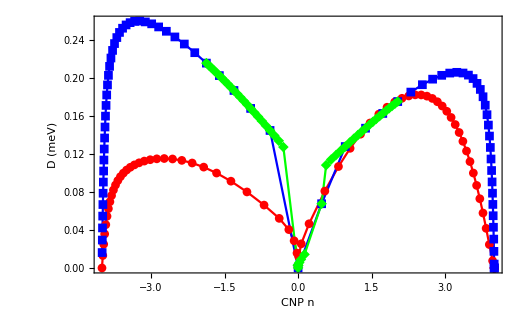

```mathematica
ListPlot[{Transpose[{DdataVishSelfCons[[All,1]],DdataVishSelfCons[[All,2]]}],Transpose[{DdataFuSelfCons[[All,1]],Abs[Re[DdataFuSelfCons[[All,2]]]]}],Transpose[{DdataFuSelfConsFine[[All,1]],Abs[Re[DdataFuSelfConsFine[[All,2]]]]}]},Joined->True,PlotMarkers->Automatic,PlotRange->Full,Frame->True,FrameLabel->{{"D (meV)",None},{"CNP
n",None}},PlotRangePadding->0,AxesOrigin->{0,0},LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],PlotStyle->{Red,Blue,Green}]
```

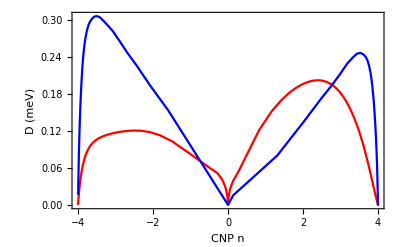

```mathematica
ListPlot[{Transpose[{DdataVish[[All,1]],DdataVish[[All,2]]}],Transpose[{DdataFu[[All,1]],Abs[Re[DdataFu[[All,2]]]]}]},Joined->True,(*PlotMarkers->Automatic,*)PlotRange->Full,Frame->True,FrameLabel->{{"D (meV)",None},{"CNP
n",None}},PlotRangePadding->0,AxesOrigin->{0,0},LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],PlotStyle->{Red,Blue}]
```

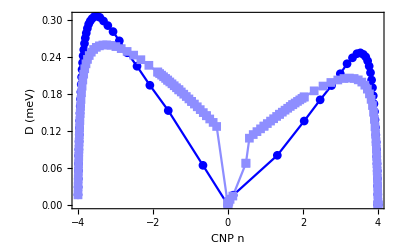

```mathematica
ListPlot[{Transpose[{DdataFu[[All,1]],DdataFu[[All,2]]}](*,SortBy[Join[DdataFuSelfCons,DdataFuSelfConsFine],First]*)},Joined->True,PlotMarkers->Automatic,PlotRange->Full,Frame->True,FrameLabel->{{"D (meV)",None},{"CNP
n",None}},PlotRangePadding->0,AxesOrigin->{0,0},LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],PlotStyle->{Blue,Lighter[Lighter[Blue]]}]
```

```mathematica
SortBy[Join[DdataFuSelfCons,DdataFuSelfConsFine],First]
```

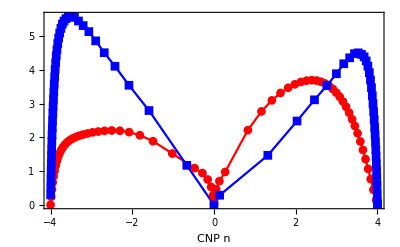

```mathematica
ListPlot[{Transpose[{DdataVish[[All,1]],DdataVish[[All,2]]*π/2*11.6045}],Transpose[{DdataFu[[All,1]],DdataFu[[All,2]]*π/2*11.6045}]},Joined->True,PlotMarkers->Automatic,PlotRange->Full,Frame->True,FrameLabel->{{None,"T_c (K)"},{"CNP
n",None}},PlotRangePadding->None,LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],PlotStyle->{Red,Blue}]
```

```mathematica
11.6045*(π/8)*4*0.2
```

3.64566

```mathematica
μ
```

4.

```mathematica
P1 = DiscretePlot[Energies[kx,2 π/3 - 1/(√3)(kx+2 π/(√3))],{kx,-2 π/(√3),2 π/(√3),0.01},Joined->True,Filling->None];
```

```mathematica
P2 = DiscretePlot[Energies[-2 π/(√3),ky-2 π/(√3)-2 π/3],{ky,0+2 π/(√3),2 π/3+2 π/(√3),0.02},Joined->True,Filling->None];
```

```mathematica
P3 = DiscretePlot[Energies[kx-(2 π/3+2 π/(√3))-2 π/(√3),0],{kx,2 π/3+2 π/(√3),4 π/(√3)+2 π/3+2 π/(√3),0.02},Joined->True,Filling->None];
```

```mathematica
P4 = DiscretePlot[Energies[2 π/(√3),ky- (4 π/(√3)+2 π/3+2 π/(√3))],{ky,4 π/(√3)+2 π/3+2 π/(√3),4 π/(√3)+2 π/3+2 π/(√3)+2 π/3,0.02},Joined->True,Filling->None];
```

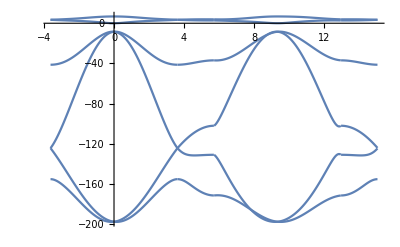

```mathematica
Show[P1,P2,P3,P4,PlotRange->All] (* Band Structure along High symmetry path: K,G,-K,-M,G,M,K *)
```

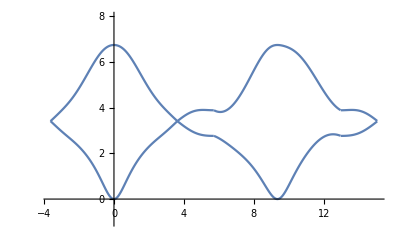

```mathematica
Show[P1,P2,P3,P4,PlotRange->{{-2 π/(√3),4 π/(√3)+2 π/3+2 π/(√3)+2 π/3},{-1,8}}](* Zoomed into the 2 band subspace*)
```

```mathematica
NVsMu=Block[{Δ = 0.1},Table[{μ,filling[μ,Δ]},{μ,-0.1,7.0,0.01}]];
```

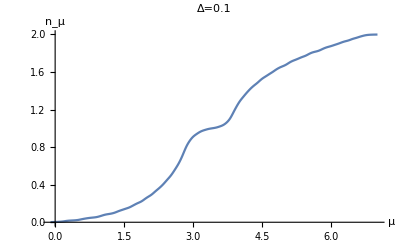

```mathematica
ListPlot[NVsMu,AxesLabel->{μ,Subscript[n, μ]},PlotRange->Full,Joined->True,PlotLabel->"Δ=0.1"]
```

```mathematica
NVsMu=Block[{Δ = 0.0},Table[{μ,filling[μ,Δ]},{μ,-0.1,7.0,0.01}]];
```

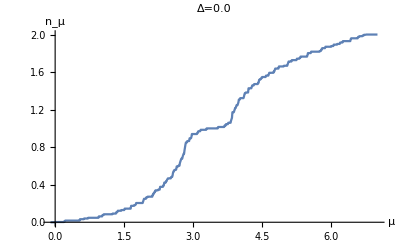

```mathematica
ListPlot[NVsMu,AxesLabel->{μ,Subscript[n, μ]},PlotRange->Full,Joined->True,PlotLabel->"Δ=0.0"]
```

```mathematica
halfFill[0.0]
```

3.5

```mathematica
nFill[0.0,0.5]
```

2.55493

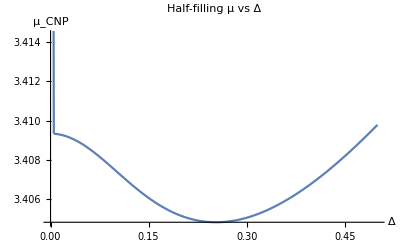

```mathematica
DiscretePlot[halfFill[δ],{δ,0.0,0.5,0.005},Filling->None,Joined->True,AxesLabel->{Δ,Subscript[μ, CNP]},PlotLabel->"Half-filling μ vs Δ"]
```

```mathematica
filling[3.406,0.15]//AbsoluteTiming
```

{0.0103274,0.999992}

```mathematica
Rho0[3.406,0.15]//AbsoluteTiming
```

{0.0136991,0.0196697+1.47571×10^-8 ⅈ}

```mathematica
AbsoluteTiming[Block[{μ=0.2,Δ=0.1},Chop[{μ,Δ,filling[μ,Δ],Rho0[μ,Δ]}]]]
```

{0.53913,{0.2,0.1,0.0102227,0.0255398}}

```mathematica
0.5391298171744061*200*350/3600
```

10.4831

```mathematica
arrVish={};
```

```mathematica
AbsoluteTiming[Do[μmin=nFill[Δ,0.01];μmax=nFill[Δ,1.99];
arrVish=Join[arrVish,Table[Chop[{μ,Δ,filling[μ,Δ],Rho0[μ,Δ]}],{μ,μmin,μmax,(μmax-μmin)/50.}]]
,{Δ,0,3.5,0.01}]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{29962.6,Null}

```mathematica
arrVishyy={};
```

```mathematica
AbsoluteTiming[Do[μmin=nFill[Δ,0.01];μmax=nFill[Δ,1.99];
arrVishyy=Join[arrVishyy,Table[Chop[{μ,Δ,filling[μ,Δ],Rho0Vishyy[μ,Δ]}],{μ,μmin,μmax,(μmax-μmin)/200.}]]
,{Δ,0,3.5,0.02}]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{12984.7,Null}

```mathematica
{μmin,μ,μmax,Δ}
```

{-5.12995,4.55497,12.1646,1.18}

```mathematica
μmax
```

6.68942

```mathematica
arrVish
```

{{-41.1869,0,0,0},{-39.5032,0,0,0},{-37.8195,0,0,0},{-36.1357,0,0,0},{-34.452,0,0,0},{-32.7683,0,0,0},{-31.0845,0,0,0},{-29.4008,0,0,0},1463,{1337.87,0.28,2.,0},{1423.85,0.28,2.,0},{1509.84,0.28,2.,0},{1595.82,0.28,2.,0},{1681.8,0.28,2.,0},{1767.78,0.28,2.,0},{1853.76,0.28,2.,0},{1939.74,0.28,2.,0}}
 |  |  |  |

```mathematica
AbsoluteTiming[arr=Chop[Flatten[Table[{μ,Δ,filling[μ,Δ],Rho0[μ,Δ]},{μ,-4.,7.5,0.01},{Δ,0.0,1.0,0.01}],1],10^-8]]
```

```mathematica
SetDirectory["C:\\Users\\tamaghna\\Dropbox\\Box Sync\\Superfluid Stiffness and Tc Bounds\\codes"]
```

C:\Users\tamaghna\Dropbox\Box Sync\Superfluid Stiffness and Tc Bounds\codes

```mathematica
Save["dataVish.mx",arrVish]
```

```mathematica
Save["dataVishyy.mx",arrVishyy]
```

```mathematica
<<"dataVish.mx"
```

{{-37.,0,0,0},{-35.4,0,0,0},{-33.8,0,0,0},{-32.2,0,0,0},{-30.6,0,0,0},{-29.,0,0,0},{-27.4,0,0,0},17888,{23.2516,3.5,1.98442,0.000582635},{24.2389,3.5,1.98586,0.000502744},{25.2263,3.5,1.98711,0.000436787},{26.2137,3.5,1.9882,0.000381861},{27.2011,3.5,1.98915,0.000335757},{28.1885,3.5,1.99,0.000296776}}
 |  |  |  |

```mathematica
arr2=ParallelTable[{nFill[Δ,n],Δ},{n,0.01,2.0,0.125},{Δ,0.01,1.0,0.01}]
```

{{{0.208807,0.01},{0.208672,0.02},{0.20834,0.03},{0.207716,0.04},{0.206708,0.05},{0.20523,0.06},{0.203202,0.07},{0.200554,0.08},{0.197225,0.09},{0.193163,0.1},{0.188326,0.11},{0.182679,0.12},{0.176196,0.13},{0.168856,0.14},{0.160645,0.15},{0.151553,0.16},{0.141571,0.17},{0.130694,0.18},{0.118917,0.19},{0.106231,0.2},{0.092623,0.21},{0.0780755,0.22},{0.0625617,0.23},{0.0460464,0.24},{0.0284854,0.25},{0.00982681,0.26},{-0.00998842,0.27},{-0.0310237,0.28},{-0.0533447,0.29},{-0.0770161,0.3},{-0.1021,0.31},{-0.12865,0.32},{-0.156714,0.33},{-0.186328,0.34},{-0.217514,0.35},{-0.250284,0.36},{-0.284635,0.37},{-0.320551,0.38},{-0.358007,0.39},{-0.396964,0.4},{-0.437379,0.41},{-0.479197,0.42},{-0.522363,0.43},{-0.566815,0.44},{-0.612491,0.45},{-0.659329,0.46},{-0.707265,0.47},{-0.756238,0.48},{-0.806188,0.49},{-0.857059,0.5},{-0.908796,0.51},{-0.961347,0.52},{-1.01466,0.53},{-1.0687,0.54},{-1.12341,0.55},{-1.17876,0.56},{-1.23471,0.57},{-1.29122,0.58},{-1.34826,0.59},{-1.4058,0.6},{-1.46382,0.61},{-1.52228,0.62},{-1.58116,0.63},{-1.64044,0.64},{-1.70009,0.65},{-1.76011,0.66},{-1.82046,0.67},{-1.88114,0.68},{-1.94212,0.69},{-2.00339,0.7},{-2.06494,0.71},{-2.12675,0.72},{-2.18881,0.73},{-2.25111,0.74},{-2.31364,0.75},{-2.37639,0.76},{-2.43935,0.77},{-2.5025,0.78},{-2.56585,0.79},{-2.62938,0.8},{-2.69308,0.81},{-2.75696,0.82},{-2.82099,0.83},{-2.88518,0.84},{-2.94952,0.85},{-3.01401,0.86},{-3.07863,0.87},{-3.14338,0.88},{-3.20826,0.89},{-3.27327,0.9},{-3.33839,0.91},{-3.40363,0.92},{-3.46898,0.93},{-3.53443,0.94},{-3.59999,0.95},{-3.66565,0.96},{-3.7314,0.97},{-3.79725,0.98},{-3.86319,0.99},{-3.92921,1.}},{{1.50068,0.01},{1.49727,0.02},{1.49417,0.03},{1.49148,0.04},{1.48906,0.05},{1.48672,0.06},{1.48431,0.07},{1.48173,0.08},{1.47895,0.09},{1.47595,0.1},{1.47273,0.11},{1.4693,0.12},{1.46566,0.13},{1.46182,0.14},{1.45777,0.15},{1.45353,0.16},{1.44909,0.17},{1.44445,0.18},{1.43963,0.19},{1.43462,0.2},{1.42943,0.21},{1.42406,0.22},{1.41851,0.23},{1.4128,0.24},{1.40693,0.25},{1.40091,0.26},{1.39473,0.27},{1.38841,0.28},{1.38196,0.29},{1.37537,0.3},{1.36865,0.31},{1.36182,0.32},{1.35487,0.33},{1.34782,0.34},{1.34066,0.35},{1.3334,0.36},{1.32605,0.37},{1.3186,0.38},{1.31107,0.39},{1.30345,0.4},{1.29576,0.41},{1.28798,0.42},{1.28013,0.43},{1.2722,0.44},{1.2642,0.45},{1.25614,0.46},{1.248,0.47},{1.2398,0.48},{1.23153,0.49},{1.22319,0.5},{1.21479,0.51},{1.20633,0.52},{1.19781,0.53},{1.18923,0.54},{1.18059,0.55},{1.17188,0.56},{1.16312,0.57},{1.1543,0.58},{1.14543,0.59},{1.1365,0.6},{1.12751,0.61},{1.11846,0.62},{1.10936,0.63},{1.10021,0.64},{1.091,0.65},{1.08174,0.66},{1.07242,0.67},{1.06306,0.68},{1.05364,0.69},{1.04417,0.7},{1.03465,0.71},{1.02507,0.72},{1.01545,0.73},{1.00577,0.74},{0.996051,0.75},{0.986277,0.76},{0.976454,0.77},{0.966582,0.78},{0.956661,0.79},{0.946692,0.8},{0.936674,0.81},{0.926608,0.82},{0.916495,0.83},{0.906333,0.84},{0.896124,0.85},{0.885867,0.86},{0.875563,0.87},{0.865212,0.88},{0.854814,0.89},{0.844368,0.9},{0.833877,0.91},{0.823338,0.92},{0.812753,0.93},{0.802121,0.94},{0.791444,0.95},{0.780719,0.96},{0.769949,0.97},{0.759133,0.98},{0.74827,0.99},{0.737362,1.}},{{1.97932,0.01},{1.98178,0.02},{1.9837,0.03},{1.98546,0.04},{1.9869,0.05},{1.9878,0.06},{1.98808,0.07},{1.98773,0.08},{1.9868,0.09},{1.98537,0.1},{1.9835,0.11},{1.98124,0.12},{1.97865,0.13},{1.97576,0.14},{1.9726,0.15},{1.96922,0.16},{1.96563,0.17},{1.96186,0.18},{1.95792,0.19},{1.95383,0.2},{1.94962,0.21},{1.94528,0.22},{1.94083,0.23},{1.93628,0.24},{1.93164,0.25},{1.92691,0.26},{1.92211,0.27},{1.91723,0.28},{1.91228,0.29},{1.90727,0.3},{1.9022,0.31},{1.89706,0.32},{1.89187,0.33},{1.88663,0.34},{1.88133,0.35},{1.87599,0.36},{1.87059,0.37},{1.86515,0.38},{1.85967,0.39},{1.85414,0.4},{1.84856,0.41},{1.84295,0.42},{1.8373,0.43},{1.8316,0.44},{1.82587,0.45},{1.8201,0.46},{1.8143,0.47},{1.80846,0.48},{1.80258,0.49},{1.79668,0.5},{1.79073,0.51},{1.78476,0.52},{1.77875,0.53},{1.77272,0.54},{1.76665,0.55},{1.76055,0.56},{1.75442,0.57},{1.74827,0.58},{1.74209,0.59},{1.73587,0.6},{1.72963,0.61},{1.72337,0.62},{1.71708,0.63},{1.71076,0.64},{1.70441,0.65},{1.69804,0.66},{1.69165,0.67},{1.68522,0.68},{1.67878,0.69},{1.67231,0.7},{1.66582,0.71},{1.6593,0.72},{1.65276,0.73},{1.64619,0.74},{1.6396,0.75},{1.63299,0.76},{1.62636,0.77},{1.61971,0.78},{1.61303,0.79},{1.60633,0.8},{1.59961,0.81},{1.59286,0.82},{1.5861,0.83},{1.57931,0.84},{1.5725,0.85},{1.56567,0.86},{1.55882,0.87},{1.55195,0.88},{1.54506,0.89},{1.53814,0.9},{1.53121,0.91},{1.52426,0.92},{1.51728,0.93},{1.51029,0.94},{1.50327,0.95},{1.49624,0.96},{1.48919,0.97},{1.48211,0.98},{1.47502,0.99},{1.4679,1.}},{{2.34264,0.01},{2.33706,0.02},{2.33108,0.03},{2.32638,0.04},{2.3227,0.05},{2.31952,0.06},{2.31653,0.07},{2.31359,0.08},{2.31063,0.09},{2.30764,0.1},{2.3046,0.11},{2.3015,0.12},{2.29836,0.13},{2.29517,0.14},{2.29194,0.15},{2.28865,0.16},{2.28533,0.17},{2.28195,0.18},{2.27853,0.19},{2.27507,0.2},{2.27156,0.21},{2.26801,0.22},{2.26442,0.23},{2.26079,0.24},{2.25712,0.25},{2.25341,0.26},{2.24967,0.27},{2.2459,0.28},{2.2421,0.29},{2.23827,0.3},{2.2344,0.31},{2.23052,0.32},{2.2266,0.33},{2.22266,0.34},{2.2187,0.35},{2.21472,0.36},{2.21071,0.37},{2.20668,0.38},{2.20263,0.39},{2.19856,0.4},{2.19448,0.41},{2.19037,0.42},{2.18625,0.43},{2.18211,0.44},{2.17795,0.45},{2.17377,0.46},{2.16958,0.47},{2.16537,0.48},{2.16114,0.49},{2.1569,0.5},{2.15265,0.51},{2.14837,0.52},{2.14409,0.53},{2.13978,0.54},{2.13546,0.55},{2.13113,0.56},{2.12678,0.57},{2.12242,0.58},{2.11804,0.59},{2.11365,0.6},{2.10924,0.61},{2.10482,0.62},{2.10038,0.63},{2.09593,0.64},{2.09147,0.65},{2.08699,0.66},{2.08249,0.67},{2.07798,0.68},{2.07346,0.69},{2.06892,0.7},{2.06437,0.71},{2.05981,0.72},{2.05523,0.73},{2.05064,0.74},{2.04603,0.75},{2.04141,0.76},{2.03677,0.77},{2.03212,0.78},{2.02746,0.79},{2.02278,0.8},{2.01809,0.81},{2.01339,0.82},{2.00867,0.83},{2.00394,0.84},{1.99919,0.85},{1.99443,0.86},{1.98966,0.87},{1.98487,0.88},{1.98007,0.89},{1.97526,0.9},{1.97043,0.91},{1.96559,0.92},{1.96073,0.93},{1.95587,0.94},{1.95099,0.95},{1.94609,0.96},{1.94118,0.97},{1.93626,0.98},{1.93133,0.99},{1.92638,1.}},{{2.55269,0.01},{2.551,0.02},{2.54946,0.03},{2.54763,0.04},{2.54546,0.05},{2.54302,0.06},{2.54038,0.07},{2.53764,0.08},{2.53485,0.09},{2.53204,0.1},{2.52923,0.11},{2.52644,0.12},{2.52367,0.13},{2.52092,0.14},{2.51818,0.15},{2.51546,0.16},{2.51275,0.17},{2.51004,0.18},{2.50735,0.19},{2.50466,0.2},{2.50198,0.21},{2.4993,0.22},{2.49663,0.23},{2.49396,0.24},{2.4913,0.25},{2.48864,0.26},{2.48598,0.27},{2.48333,0.28},{2.48068,0.29},{2.47803,0.3},{2.47538,0.31},{2.47274,0.32},{2.47009,0.33},{2.46745,0.34},{2.46481,0.35},{2.46216,0.36},{2.45952,0.37},{2.45687,0.38},{2.45422,0.39},{2.45157,0.4},{2.44892,0.41},{2.44627,0.42},{2.44361,0.43},{2.44094,0.44},{2.43828,0.45},{2.4356,0.46},{2.43293,0.47},{2.43024,0.48},{2.42755,0.49},{2.42485,0.5},{2.42215,0.51},{2.41944,0.52},{2.41672,0.53},{2.41399,0.54},{2.41125,0.55},{2.40851,0.56},{2.40576,0.57},{2.40299,0.58},{2.40022,0.59},{2.39744,0.6},{2.39464,0.61},{2.39184,0.62},{2.38903,0.63},{2.3862,0.64},{2.38337,0.65},{2.38052,0.66},{2.37767,0.67},{2.3748,0.68},{2.37192,0.69},{2.36903,0.7},{2.36612,0.71},{2.36321,0.72},{2.36028,0.73},{2.35734,0.74},{2.35439,0.75},{2.35142,0.76},{2.34845,0.77},{2.34546,0.78},{2.34246,0.79},{2.33944,0.8},{2.33642,0.81},{2.33338,0.82},{2.33033,0.83},{2.32726,0.84},{2.32419,0.85},{2.3211,0.86},{2.31799,0.87},{2.31488,0.88},{2.31175,0.89},{2.30861,0.9},{2.30546,0.91},{2.30229,0.92},{2.29912,0.93},{2.29593,0.94},{2.29272,0.95},{2.28951,0.96},{2.28628,0.97},{2.28304,0.98},{2.27979,0.99},{2.27652,1.}},{{2.71255,0.01},{2.71138,0.02},{2.70941,0.03},{2.70691,0.04},{2.70425,0.05},{2.70162,0.06},{2.69912,0.07},{2.69678,0.08},{2.69458,0.09},{2.69253,0.1},{2.69061,0.11},{2.6888,0.12},{2.68709,0.13},{2.68548,0.14},{2.68394,0.15},{2.68248,0.16},{2.68108,0.17},{2.67973,0.18},{2.67844,0.19},{2.6772,0.2},{2.676,0.21},{2.67484,0.22},{2.67371,0.23},{2.67262,0.24},{2.67155,0.25},{2.67051,0.26},{2.66948,0.27},{2.66848,0.28},{2.6675,0.29},{2.66653,0.3},{2.66557,0.31},{2.66463,0.32},{2.66369,0.33},{2.66276,0.34},{2.66184,0.35},{2.66092,0.36},{2.66,0.37},{2.65908,0.38},{2.65816,0.39},{2.65724,0.4},{2.65632,0.41},{2.65539,0.42},{2.65446,0.43},{2.65352,0.44},{2.65257,0.45},{2.65161,0.46},{2.65065,0.47},{2.64967,0.48},{2.64868,0.49},{2.64769,0.5},{2.64668,0.51},{2.64565,0.52},{2.64462,0.53},{2.64357,0.54},{2.64251,0.55},{2.64143,0.56},{2.64033,0.57},{2.63923,0.58},{2.6381,0.59},{2.63696,0.6},{2.6358,0.61},{2.63463,0.62},{2.63344,0.63},{2.63223,0.64},{2.63101,0.65},{2.62977,0.66},{2.62851,0.67},{2.62723,0.68},{2.62594,0.69},{2.62462,0.7},{2.62329,0.71},{2.62195,0.72},{2.62058,0.73},{2.6192,0.74},{2.61779,0.75},{2.61637,0.76},{2.61494,0.77},{2.61348,0.78},{2.61201,0.79},{2.61052,0.8},{2.60901,0.81},{2.60748,0.82},{2.60594,0.83},{2.60438,0.84},{2.6028,0.85},{2.60121,0.86},{2.59959,0.87},{2.59796,0.88},{2.59632,0.89},{2.59465,0.9},{2.59297,0.91},{2.59128,0.92},{2.58956,0.93},{2.58783,0.94},{2.58609,0.95},{2.58433,0.96},{2.58255,0.97},{2.58076,0.98},{2.57895,0.99},{2.57712,1.}},{{2.80488,0.01},{2.80399,0.02},{2.80348,0.03},{2.80343,0.04},{2.80375,0.05},{2.80433,0.06},{2.8051,0.07},{2.80603,0.08},{2.80707,0.09},{2.80819,0.1},{2.80939,0.11},{2.81064,0.12},{2.81194,0.13},{2.81328,0.14},{2.81465,0.15},{2.81605,0.16},{2.81748,0.17},{2.81893,0.18},{2.8204,0.19},{2.82188,0.2},{2.82337,0.21},{2.82486,0.22},{2.82637,0.23},{2.82787,0.24},{2.82937,0.25},{2.83086,0.26},{2.83235,0.27},{2.83383,0.28},{2.83529,0.29},{2.83675,0.3},{2.83818,0.31},{2.8396,0.32},{2.84099,0.33},{2.84236,0.34},{2.84371,0.35},{2.84504,0.36},{2.84633,0.37},{2.8476,0.38},{2.84884,0.39},{2.85005,0.4},{2.85122,0.41},{2.85237,0.42},{2.85348,0.43},{2.85455,0.44},{2.85559,0.45},{2.8566,0.46},{2.85757,0.47},{2.85851,0.48},{2.8594,0.49},{2.86026,0.5},{2.86109,0.51},{2.86187,0.52},{2.86262,0.53},{2.86334,0.54},{2.86401,0.55},{2.86465,0.56},{2.86525,0.57},{2.86581,0.58},{2.86634,0.59},{2.86683,0.6},{2.86728,0.61},{2.8677,0.62},{2.86809,0.63},{2.86843,0.64},{2.86875,0.65},{2.86902,0.66},{2.86927,0.67},{2.86948,0.68},{2.86965,0.69},{2.8698,0.7},{2.86991,0.71},{2.86999,0.72},{2.87004,0.73},{2.87005,0.74},{2.87004,0.75},{2.86999,0.76},{2.86992,0.77},{2.86982,0.78},{2.86968,0.79},{2.86952,0.8},{2.86934,0.81},{2.86912,0.82},{2.86888,0.83},{2.86861,0.84},{2.86831,0.85},{2.86799,0.86},{2.86765,0.87},{2.86728,0.88},{2.86688,0.89},{2.86646,0.9},{2.86602,0.91},{2.86556,0.92},{2.86507,0.93},{2.86456,0.94},{2.86403,0.95},{2.86348,0.96},{2.86291,0.97},{2.86231,0.98},{2.8617,0.99},{2.86106,1.}},{{2.91833,0.01},{2.92127,0.02},{2.92358,0.03},{2.92595,0.04},{2.92882,0.05},{2.93226,0.06},{2.93624,0.07},{2.94064,0.08},{2.94537,0.09},{2.95033,0.1},{2.95546,0.11},{2.96067,0.12},{2.96593,0.13},{2.9712,0.14},{2.97645,0.15},{2.98165,0.16},{2.98681,0.17},{2.99191,0.18},{2.99695,0.19},{3.00192,0.2},{3.00681,0.21},{3.01162,0.22},{3.01636,0.23},{3.02102,0.24},{3.02558,0.25},{3.03006,0.26},{3.03445,0.27},{3.03874,0.28},{3.04294,0.29},{3.04703,0.3},{3.05103,0.31},{3.05492,0.32},{3.05872,0.33},{3.06241,0.34},{3.06599,0.35},{3.06947,0.36},{3.07285,0.37},{3.07612,0.38},{3.0793,0.39},{3.08237,0.4},{3.08534,0.41},{3.08821,0.42},{3.09098,0.43},{3.09366,0.44},{3.09625,0.45},{3.09874,0.46},{3.10115,0.47},{3.10347,0.48},{3.1057,0.49},{3.10786,0.5},{3.10993,0.51},{3.11192,0.52},{3.11384,0.53},{3.11568,0.54},{3.11746,0.55},{3.11916,0.56},{3.1208,0.57},{3.12237,0.58},{3.12388,0.59},{3.12533,0.6},{3.12673,0.61},{3.12806,0.62},{3.12934,0.63},{3.13057,0.64},{3.13174,0.65},{3.13287,0.66},{3.13395,0.67},{3.13498,0.68},{3.13597,0.69},{3.13692,0.7},{3.13782,0.71},{3.13869,0.72},{3.13951,0.73},{3.1403,0.74},{3.14105,0.75},{3.14176,0.76},{3.14244,0.77},{3.14309,0.78},{3.14371,0.79},{3.14429,0.8},{3.14485,0.81},{3.14537,0.82},{3.14587,0.83},{3.14634,0.84},{3.14679,0.85},{3.14721,0.86},{3.1476,0.87},{3.14797,0.88},{3.14831,0.89},{3.14864,0.9},{3.14894,0.91},{3.14922,0.92},{3.14948,0.93},{3.14972,0.94},{3.14994,0.95},{3.15013,0.96},{3.15032,0.97},{3.15048,0.98},{3.15062,0.99},{3.15075,1.}},{{3.54236,0.01},{3.54501,0.02},{3.54622,0.03},{3.54557,0.04},{3.54303,0.05},{3.53878,0.06},{3.53319,0.07},{3.52664,0.08},{3.51955,0.09},{3.51228,0.1},{3.50516,0.11},{3.4984,0.12},{3.49212,0.13},{3.48639,0.14},{3.4812,0.15},{3.47654,0.16},{3.47237,0.17},{3.46863,0.18},{3.46529,0.19},{3.46229,0.2},{3.4596,0.21},{3.45718,0.22},{3.45501,0.23},{3.45306,0.24},{3.4513,0.25},{3.44971,0.26},{3.44828,0.27},{3.44699,0.28},{3.44583,0.29},{3.44478,0.3},{3.44384,0.31},{3.443,0.32},{3.44225,0.33},{3.44158,0.34},{3.44098,0.35},{3.44045,0.36},{3.43999,0.37},{3.43959,0.38},{3.43924,0.39},{3.43894,0.4},{3.43869,0.41},{3.43848,0.42},{3.43831,0.43},{3.43819,0.44},{3.43809,0.45},{3.43803,0.46},{3.43801,0.47},{3.43801,0.48},{3.43804,0.49},{3.43809,0.5},{3.43817,0.51},{3.43827,0.52},{3.43839,0.53},{3.43853,0.54},{3.43869,0.55},{3.43887,0.56},{3.43907,0.57},{3.43928,0.58},{3.4395,0.59},{3.43974,0.6},{3.43999,0.61},{3.44025,0.62},{3.44053,0.63},{3.44081,0.64},{3.44111,0.65},{3.44141,0.66},{3.44173,0.67},{3.44205,0.68},{3.44238,0.69},{3.44272,0.7},{3.44306,0.71},{3.44341,0.72},{3.44377,0.73},{3.44413,0.74},{3.4445,0.75},{3.44487,0.76},{3.44525,0.77},{3.44563,0.78},{3.44602,0.79},{3.44641,0.8},{3.4468,0.81},{3.4472,0.82},{3.4476,0.83},{3.448,0.84},{3.44841,0.85},{3.44881,0.86},{3.44922,0.87},{3.44963,0.88},{3.45005,0.89},{3.45046,0.9},{3.45088,0.91},{3.4513,0.92},{3.45172,0.93},{3.45214,0.94},{3.45256,0.95},{3.45298,0.96},{3.4534,0.97},{3.45382,0.98},{3.45425,0.99},{3.45467,1.}},{{3.84349,0.01},{3.84417,0.02},{3.84462,0.03},{3.84447,0.04},{3.84372,0.05},{3.84251,0.06},{3.84092,0.07},{3.83906,0.08},{3.837,0.09},{3.83477,0.1},{3.83242,0.11},{3.82998,0.12},{3.82747,0.13},{3.8249,0.14},{3.82229,0.15},{3.81966,0.16},{3.81701,0.17},{3.81436,0.18},{3.8117,0.19},{3.80906,0.2},{3.80643,0.21},{3.80382,0.22},{3.80124,0.23},{3.7987,0.24},{3.79619,0.25},{3.79373,0.26},{3.79131,0.27},{3.78895,0.28},{3.78664,0.29},{3.78439,0.3},{3.7822,0.31},{3.78008,0.32},{3.77802,0.33},{3.77603,0.34},{3.7741,0.35},{3.77225,0.36},{3.77047,0.37},{3.76876,0.38},{3.76712,0.39},{3.76556,0.4},{3.76406,0.41},{3.76264,0.42},{3.76129,0.43},{3.76001,0.44},{3.7588,0.45},{3.75766,0.46},{3.75658,0.47},{3.75558,0.48},{3.75464,0.49},{3.75376,0.5},{3.75295,0.51},{3.7522,0.52},{3.75151,0.53},{3.75088,0.54},{3.7503,0.55},{3.74978,0.56},{3.74932,0.57},{3.74891,0.58},{3.74855,0.59},{3.74825,0.6},{3.74799,0.61},{3.74778,0.62},{3.74761,0.63},{3.74749,0.64},{3.74741,0.65},{3.74738,0.66},{3.74738,0.67},{3.74743,0.68},{3.74751,0.69},{3.74763,0.7},{3.74778,0.71},{3.74797,0.72},{3.7482,0.73},{3.74845,0.74},{3.74874,0.75},{3.74906,0.76},{3.7494,0.77},{3.74978,0.78},{3.75018,0.79},{3.75061,0.8},{3.75107,0.81},{3.75155,0.82},{3.75205,0.83},{3.75258,0.84},{3.75312,0.85},{3.7537,0.86},{3.75429,0.87},{3.7549,0.88},{3.75553,0.89},{3.75618,0.9},{3.75685,0.91},{3.75753,0.92},{3.75824,0.93},{3.75896,0.94},{3.75969,0.95},{3.76044,0.96},{3.76121,0.97},{3.76199,0.98},{3.76278,0.99},{3.76359,1.}},{{3.96866,0.01},{3.96597,0.02},{3.96484,0.03},{3.96494,0.04},{3.96578,0.05},{3.96705,0.06},{3.96858,0.07},{3.97023,0.08},{3.97193,0.09},{3.97361,0.1},{3.97524,0.11},{3.97681,0.12},{3.9783,0.13},{3.97971,0.14},{3.98104,0.15},{3.9823,0.16},{3.98349,0.17},{3.98461,0.18},{3.98567,0.19},{3.98668,0.2},{3.98764,0.21},{3.98855,0.22},{3.98943,0.23},{3.99026,0.24},{3.99107,0.25},{3.99185,0.26},{3.99261,0.27},{3.99335,0.28},{3.99407,0.29},{3.99478,0.3},{3.99547,0.31},{3.99616,0.32},{3.99684,0.33},{3.99752,0.34},{3.99819,0.35},{3.99887,0.36},{3.99954,0.37},{4.00023,0.38},{4.00091,0.39},{4.00161,0.4},{4.00231,0.41},{4.00302,0.42},{4.00374,0.43},{4.00447,0.44},{4.00522,0.45},{4.00598,0.46},{4.00675,0.47},{4.00754,0.48},{4.00835,0.49},{4.00917,0.5},{4.01001,0.51},{4.01086,0.52},{4.01174,0.53},{4.01263,0.54},{4.01354,0.55},{4.01447,0.56},{4.01541,0.57},{4.01638,0.58},{4.01737,0.59},{4.01837,0.6},{4.0194,0.61},{4.02044,0.62},{4.0215,0.63},{4.02259,0.64},{4.02369,0.65},{4.02481,0.66},{4.02595,0.67},{4.02711,0.68},{4.02829,0.69},{4.02949,0.7},{4.0307,0.71},{4.03194,0.72},{4.03319,0.73},{4.03446,0.74},{4.03575,0.75},{4.03705,0.76},{4.03838,0.77},{4.03972,0.78},{4.04108,0.79},{4.04245,0.8},{4.04384,0.81},{4.04525,0.82},{4.04667,0.83},{4.04811,0.84},{4.04956,0.85},{4.05103,0.86},{4.05252,0.87},{4.05401,0.88},{4.05553,0.89},{4.05705,0.9},{4.0586,0.91},{4.06015,0.92},{4.06172,0.93},{4.0633,0.94},{4.06489,0.95},{4.0665,0.96},{4.06812,0.97},{4.06975,0.98},{4.07139,0.99},{4.07304,1.}},{{4.17693,0.01},{4.16721,0.02},{4.16426,0.03},{4.16375,0.04},{4.16426,0.05},{4.16533,0.06},{4.16675,0.07},{4.16841,0.08},{4.17026,0.09},{4.17226,0.1},{4.17436,0.11},{4.17656,0.12},{4.17883,0.13},{4.18116,0.14},{4.18353,0.15},{4.18594,0.16},{4.18838,0.17},{4.19083,0.18},{4.1933,0.19},{4.19578,0.2},{4.19827,0.21},{4.20075,0.22},{4.20324,0.23},{4.20573,0.24},{4.20821,0.25},{4.21069,0.26},{4.21316,0.27},{4.21563,0.28},{4.2181,0.29},{4.22056,0.3},{4.22302,0.31},{4.22547,0.32},{4.22792,0.33},{4.23036,0.34},{4.2328,0.35},{4.23523,0.36},{4.23767,0.37},{4.2401,0.38},{4.24253,0.39},{4.24496,0.4},{4.24739,0.41},{4.24981,0.42},{4.25224,0.43},{4.25467,0.44},{4.25709,0.45},{4.25952,0.46},{4.26195,0.47},{4.26439,0.48},{4.26682,0.49},{4.26926,0.5},{4.2717,0.51},{4.27414,0.52},{4.27659,0.53},{4.27904,0.54},{4.28149,0.55},{4.28395,0.56},{4.28642,0.57},{4.28889,0.58},{4.29136,0.59},{4.29384,0.6},{4.29633,0.61},{4.29882,0.62},{4.30131,0.63},{4.30382,0.64},{4.30633,0.65},{4.30884,0.66},{4.31136,0.67},{4.31389,0.68},{4.31643,0.69},{4.31897,0.7},{4.32152,0.71},{4.32408,0.72},{4.32664,0.73},{4.32921,0.74},{4.33179,0.75},{4.33437,0.76},{4.33697,0.77},{4.33957,0.78},{4.34217,0.79},{4.34479,0.8},{4.34741,0.81},{4.35004,0.82},{4.35268,0.83},{4.35532,0.84},{4.35797,0.85},{4.36063,0.86},{4.3633,0.87},{4.36597,0.88},{4.36865,0.89},{4.37134,0.9},{4.37404,0.91},{4.37674,0.92},{4.37945,0.93},{4.38217,0.94},{4.38489,0.95},{4.38763,0.96},{4.39036,0.97},{4.39311,0.98},{4.39586,0.99},{4.39863,1.}},{{4.43116,0.01},{4.43478,0.02},{4.43738,0.03},{4.43946,0.04},{4.44129,0.05},{4.44308,0.06},{4.44494,0.07},{4.44692,0.08},{4.44904,0.09},{4.4513,0.1},{4.45368,0.11},{4.45618,0.12},{4.45878,0.13},{4.46147,0.14},{4.46424,0.15},{4.46706,0.16},{4.46995,0.17},{4.47289,0.18},{4.47588,0.19},{4.47891,0.2},{4.48197,0.21},{4.48508,0.22},{4.48821,0.23},{4.49137,0.24},{4.49456,0.25},{4.49778,0.26},{4.50102,0.27},{4.50429,0.28},{4.50757,0.29},{4.51088,0.3},{4.51421,0.31},{4.51755,0.32},{4.52091,0.33},{4.52429,0.34},{4.52769,0.35},{4.5311,0.36},{4.53452,0.37},{4.53796,0.38},{4.54141,0.39},{4.54487,0.4},{4.54835,0.41},{4.55183,0.42},{4.55533,0.43},{4.55884,0.44},{4.56236,0.45},{4.56589,0.46},{4.56943,0.47},{4.57298,0.48},{4.57653,0.49},{4.5801,0.5},{4.58367,0.51},{4.58725,0.52},{4.59085,0.53},{4.59444,0.54},{4.59805,0.55},{4.60166,0.56},{4.60529,0.57},{4.60892,0.58},{4.61255,0.59},{4.61619,0.6},{4.61984,0.61},{4.6235,0.62},{4.62717,0.63},{4.63084,0.64},{4.63451,0.65},{4.6382,0.66},{4.64189,0.67},{4.64559,0.68},{4.64929,0.69},{4.653,0.7},{4.65672,0.71},{4.66044,0.72},{4.66417,0.73},{4.66791,0.74},{4.67165,0.75},{4.6754,0.76},{4.67915,0.77},{4.68292,0.78},{4.68669,0.79},{4.69046,0.8},{4.69424,0.81},{4.69803,0.82},{4.70182,0.83},{4.70562,0.84},{4.70943,0.85},{4.71324,0.86},{4.71706,0.87},{4.72089,0.88},{4.72472,0.89},{4.72856,0.9},{4.7324,0.91},{4.73625,0.92},{4.74011,0.93},{4.74397,0.94},{4.74785,0.95},{4.75172,0.96},{4.7556,0.97},{4.75949,0.98},{4.76339,0.99},{4.76729,1.}},{{4.785,0.01},{4.7987,0.02},{4.80704,0.03},{4.81187,0.04},{4.81545,0.05},{4.81865,0.06},{4.82179,0.07},{4.82496,0.08},{4.82818,0.09},{4.83144,0.1},{4.83475,0.11},{4.83807,0.12},{4.84139,0.13},{4.84472,0.14},{4.84804,0.15},{4.85135,0.16},{4.85466,0.17},{4.85797,0.18},{4.86129,0.19},{4.86461,0.2},{4.86795,0.21},{4.87131,0.22},{4.87469,0.23},{4.8781,0.24},{4.88154,0.25},{4.88501,0.26},{4.88852,0.27},{4.89206,0.28},{4.89564,0.29},{4.89925,0.3},{4.90291,0.31},{4.9066,0.32},{4.91032,0.33},{4.91409,0.34},{4.91789,0.35},{4.92173,0.36},{4.9256,0.37},{4.9295,0.38},{4.93344,0.39},{4.93742,0.4},{4.94142,0.41},{4.94545,0.42},{4.94952,0.43},{4.95361,0.44},{4.95773,0.45},{4.96188,0.46},{4.96605,0.47},{4.97025,0.48},{4.97448,0.49},{4.97872,0.5},{4.983,0.51},{4.98729,0.52},{4.99161,0.53},{4.99595,0.54},{5.00031,0.55},{5.00469,0.56},{5.00908,0.57},{5.0135,0.58},{5.01794,0.59},{5.0224,0.6},{5.02687,0.61},{5.03137,0.62},{5.03588,0.63},{5.0404,0.64},{5.04495,0.65},{5.04951,0.66},{5.05408,0.67},{5.05867,0.68},{5.06328,0.69},{5.0679,0.7},{5.07254,0.71},{5.0772,0.72},{5.08186,0.73},{5.08655,0.74},{5.09124,0.75},{5.09595,0.76},{5.10068,0.77},{5.10542,0.78},{5.11017,0.79},{5.11494,0.8},{5.11971,0.81},{5.12451,0.82},{5.12931,0.83},{5.13413,0.84},{5.13897,0.85},{5.14381,0.86},{5.14867,0.87},{5.15354,0.88},{5.15843,0.89},{5.16332,0.9},{5.16823,0.91},{5.17316,0.92},{5.17809,0.93},{5.18304,0.94},{5.188,0.95},{5.19297,0.96},{5.19795,0.97},{5.20295,0.98},{5.20796,0.99},{5.21298,1.}},{{5.33112,0.01},{5.3369,0.02},{5.34336,0.03},{5.34961,0.04},{5.35505,0.05},{5.35948,0.06},{5.36297,0.07},{5.36573,0.08},{5.36801,0.09},{5.36998,0.1},{5.37179,0.11},{5.37353,0.12},{5.37527,0.13},{5.37706,0.14},{5.37892,0.15},{5.38088,0.16},{5.38295,0.17},{5.38513,0.18},{5.38744,0.19},{5.38987,0.2},{5.39241,0.21},{5.39507,0.22},{5.39785,0.23},{5.40074,0.24},{5.40373,0.25},{5.40683,0.26},{5.41002,0.27},{5.41331,0.28},{5.41669,0.29},{5.42016,0.3},{5.42371,0.31},{5.42734,0.32},{5.43104,0.33},{5.43482,0.34},{5.43867,0.35},{5.44258,0.36},{5.44656,0.37},{5.4506,0.38},{5.4547,0.39},{5.45887,0.4},{5.46308,0.41},{5.46736,0.42},{5.47168,0.43},{5.47606,0.44},{5.48049,0.45},{5.48497,0.46},{5.48949,0.47},{5.49407,0.48},{5.49869,0.49},{5.50335,0.5},{5.50806,0.51},{5.51281,0.52},{5.51761,0.53},{5.52245,0.54},{5.52733,0.55},{5.53225,0.56},{5.53721,0.57},{5.54221,0.58},{5.54724,0.59},{5.55232,0.6},{5.55744,0.61},{5.56259,0.62},{5.56778,0.63},{5.57301,0.64},{5.57827,0.65},{5.58357,0.66},{5.5889,0.67},{5.59427,0.68},{5.59968,0.69},{5.60512,0.7},{5.61059,0.71},{5.6161,0.72},{5.62164,0.73},{5.62722,0.74},{5.63283,0.75},{5.63847,0.76},{5.64414,0.77},{5.64985,0.78},{5.65559,0.79},{5.66136,0.8},{5.66716,0.81},{5.673,0.82},{5.67887,0.83},{5.68476,0.84},{5.69069,0.85},{5.69665,0.86},{5.70265,0.87},{5.70867,0.88},{5.71472,0.89},{5.72081,0.9},{5.72692,0.91},{5.73307,0.92},{5.73924,0.93},{5.74545,0.94},{5.75168,0.95},{5.75795,0.96},{5.76424,0.97},{5.77057,0.98},{5.77692,0.99},{5.7833,1.}},{{6.04152,0.01},{6.04209,0.02},{6.04316,0.03},{6.04449,0.04},{6.04583,0.05},{6.04709,0.06},{6.04825,0.07},{6.04936,0.08},{6.05047,0.09},{6.05163,0.1},{6.05288,0.11},{6.05423,0.12},{6.05572,0.13},{6.05734,0.14},{6.05911,0.15},{6.06103,0.16},{6.0631,0.17},{6.06531,0.18},{6.06766,0.19},{6.07016,0.2},{6.07279,0.21},{6.07556,0.22},{6.07846,0.23},{6.08148,0.24},{6.08464,0.25},{6.08791,0.26},{6.09131,0.27},{6.09483,0.28},{6.09846,0.29},{6.1022,0.3},{6.10606,0.31},{6.11003,0.32},{6.11411,0.33},{6.1183,0.34},{6.12259,0.35},{6.12699,0.36},{6.1315,0.37},{6.13611,0.38},{6.14082,0.39},{6.14563,0.4},{6.15054,0.41},{6.15556,0.42},{6.16067,0.43},{6.16589,0.44},{6.1712,0.45},{6.17661,0.46},{6.18212,0.47},{6.18773,0.48},{6.19344,0.49},{6.19924,0.5},{6.20514,0.51},{6.21113,0.52},{6.21722,0.53},{6.22341,0.54},{6.2297,0.55},{6.23607,0.56},{6.24255,0.57},{6.24912,0.58},{6.25578,0.59},{6.26254,0.6},{6.26939,0.61},{6.27634,0.62},{6.28338,0.63},{6.29052,0.64},{6.29775,0.65},{6.30507,0.66},{6.31249,0.67},{6.32,0.68},{6.3276,0.69},{6.33529,0.7},{6.34308,0.71},{6.35096,0.72},{6.35893,0.73},{6.367,0.74},{6.37515,0.75},{6.3834,0.76},{6.39174,0.77},{6.40017,0.78},{6.40869,0.79},{6.4173,0.8},{6.426,0.81},{6.43479,0.82},{6.44367,0.83},{6.45264,0.84},{6.4617,0.85},{6.47085,0.86},{6.48008,0.87},{6.48941,0.88},{6.49882,0.89},{6.50831,0.9},{6.5179,0.91},{6.52757,0.92},{6.53733,0.93},{6.54717,0.94},{6.5571,0.95},{6.56711,0.96},{6.57721,0.97},{6.58739,0.98},{6.59765,0.99},{6.608,1.}}}

```mathematica
{n,Δ}
```

{0.885,0.77}

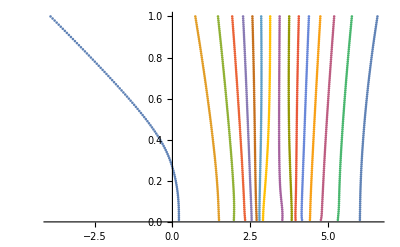

```mathematica
ListPlot[arr2]
```

```mathematica
arr2[[All,-1,1]]
```

{-3.92921,0.737362,1.4679,1.92638,2.27652,2.57712,2.86106,3.15075,3.45467,3.76359,4.07304,4.39863,4.76729,5.21298,5.7833,6.608}

```mathematica
count=0;Show[ListContourPlot[arr,PlotLegends->Automatic,Contours->10,ContourStyle->None(*Directive[None(*White*)(*,Thick*)]*),Frame->True,FrameLabel->{{Δ,None},{μ,n}},FrameTicks->{{Automatic,None},{Automatic,Table[{i,(count++)/8},{i,arr2[[All,-1,1]]}]}},LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],PlotRangePadding->None,ColorFunction->"StarryNightColors"],ListPlot[arr2[[;;;;2]],Joined->True,PlotStyle->Directive[Black,Dashed](*{Black,Directive[Black,Dotted],Directive[Black,Dashed],Directive[Black,DotDashed],Black,Directive[Black,Dotted],Directive[Black,Dashed],Directive[Black,DotDashed]}*)]]
```

-Graphics-

```mathematica
(* Why this curve? *)
```

#### From fuBands_v2.nb on 10th Oct

```mathematica
Clear["Global`*"]
```

```mathematica
<<"N300data.mx"
```

```mathematica
Nsites=300;
kSpan=N[Flatten[Table[i*{(2π)/(√3),2π}+j*{(4π)/(√3),0},{i,0,0.999,1/Nsites},{j,0,0.999,1/Nsites}],1]];
ProgresskSpace[]:={Position[kSpan,k][[1,1]],Length[kSpan]};
```

```mathematica
a1 = {(√3)/2,1/2}; a2 = {(√3)/2,-1/2}; τ = {1/(√3),0};
```

```mathematica
LatMat = {a1,a2}; LatMat // MatrixForm
```

((√3)/2 | 1/2
(√3)/2 | -1/2)

```mathematica
ReciLatMat = 2π Inverse[LatMat]†;
```

```mathematica
ReciLatMat // MatrixForm
```

((2 π)/(√3) | 2 π
(2 π)/(√3) | -2 π)

```mathematica
data1 = Import["C:\\Users\\tamaghna\\Dropbox\\Box Sync\\Superfluid Stiffness and Tc Bounds\\codes\\eff_hopping_ver2.dat"];
```

Import::nffil: File not found during Import.

```mathematica
data1 = Import["C:\\Users\\Tamaghna Hazra\\Dropbox\\Box Sync\\Superfluid Stiffness and Tc Bounds\\codes\\eff_hopping_ver2.dat"];
```

```mathematica
FuData = Chop[data1,10^-8]; len = Length[FuData];
```

```mathematica
n1 = Table[FuData[[i,1]],{i,1,len}];
```

```mathematica
n2 = Table[FuData[[i,2]],{i,1,len}];
```

```mathematica
τ1 = Table[FuData[[i,3]],{i,1,len}];τ2 = Table[FuData[[i,4]],{i,1,len}];
```

```mathematica
tdel = Table[ FuData[[i,5]]  + I FuData[[i,6]] ,{i,1,len}];
```

```mathematica
Clear[kdotr];kdotr[kx_,ky_,m1_,m2_] = kx(m1+m2)(√3)/2 + ky (m1-m2)1/2;
```

```mathematica
mat12[kx_,ky_] := Sum[ tdel[[i]] E^(I kdotr[kx,ky,n1[[i]],n2[[i]] ])(Abs[τ1[[i]]-τ2[[i]] ]) HeavisideTheta[ τ2[[i]] - τ1[[i]] ] ,{i,1,len}];
```

```mathematica
mat11[kx_,ky_] := 1/2 Sum[ tdel[[i]] E^(I kdotr[kx,ky,n1[[i]],n2[[i]] ])(Abs[Abs[τ1[[i]]-τ2[[i]] ]-1]) HeavisideTheta[ 1.5-τ1[[i]] ] ,{i,1,len}];
```

```mathematica
mat22[kx_,ky_] := 1/2 Sum[ tdel[[i]] E^(I kdotr[kx,ky,n1[[i]],n2[[i]] ])(Abs[Abs[τ1[[i]]-τ2[[i]] ]-1]) HeavisideTheta[ τ1[[i]]-1.5 ],{i,1,len}]
```

```mathematica
Clear[Ham];Ham[kx_,ky_](*:=Ham[kx,ky]*)=Evaluate[Sum[Block[{tk= tdel[[i]] E^(I kdotr[kx,ky,n1[[i]],n2[[i]] ])},
Re[tk]{{(Abs[Abs[τ1[[i]]-τ2[[i]] ]-1]) HeavisideTheta[ 1.5-τ1[[i]] ],0.0},
{0.0,(Abs[Abs[τ1[[i]]-τ2[[i]] ]-1]) HeavisideTheta[ τ1[[i]]-1.5 ]}}
+{{0.,tk},{Conjugate[tk],0.}}(Abs[τ1[[i]]-τ2[[i]] ]) HeavisideTheta[ τ2[[i]] - τ1[[i]] ]] 
,{i,1,len}]];
```

```mathematica
(*Ham0[kx_,ky_] := {{mat11[kx,ky],mat12[kx,ky]},{0,mat22[kx,ky]}};*)
```

```mathematica
(*Ham[kx_,ky_] := Chop[Ham0[kx,ky] + Ham0[kx,ky]†,10^-8];*)
```

```mathematica
Clear[Energies];Energies[kx_,ky_] :=Energies[kx,ky]= 10^3 Sort[N[Eigenvalues[Chop[Ham[kx,ky]]]]]//Chop;
```

```mathematica
Clear[Curvature];Curvature[kx_,ky_] :=Curvature[kx,ky]=Block[{ϵ=10^-2},Table[1/ϵ^2(Energies[kx+ϵ,ky][[n]]+Energies[kx-ϵ,ky][[n]]-2Energies[kx,ky][[n]]),{n,2}]]//Chop;
```

```mathematica
Clear[CurvatureFuyy];CurvatureFuyy[kx_,ky_] :=CurvatureFuyy[kx,ky]=Block[{ϵ=10^-2},Table[1/ϵ^2(Energies[kx,ky+ϵ][[n]]+Energies[kx,ky-ϵ][[n]]-2Energies[kx,ky][[n]]),{n,2}]]//Chop;
```

```mathematica
Clear[fillingFu];fillingFu[μ_,Δ_] := Sum[ 1/2(1-(Energies[ k[[1]],k[[2]]][[n]]-μ)/(√((Energies[ k[[1]],k[[2]] ] [[n]]-μ)^2+ Δ^2+10^-10))),{n,2},{k,kSpan}]/Length[kSpan];
```

```mathematica
Clear[fillingFuT];fillingFuT[μ_,T_] := Sum[ (1+Exp[(Energies[ k[[1]],k[[2]]][[n]]-μ)/(T+0.000000001)])^-1,{n,2},{k,kSpan}]/Length[kSpan];
```

```mathematica
Clear[Rho0Fu];Rho0Fu[μ_,Δ_]:=Sum[Curvature[ k[[1]],k[[2]]][[n]] 1/2(1-(Energies[ k[[1]],k[[2]]][[n]]-μ)/(√((Energies[ k[[1]],k[[2]] ] [[n]]-μ)^2+ Δ^2+10^-10))),{n,2},{k,kSpan}]/Length[kSpan];
```

```mathematica
Clear[Rho0Fuyy];Rho0Fuyy[μ_,Δ_]:=Sum[CurvatureFuyy[ k[[1]],k[[2]]][[n]] 1/2(1-(Energies[ k[[1]],k[[2]]][[n]]-μ)/(√((Energies[ k[[1]],k[[2]] ] [[n]]-μ)^2+ Δ^2+10^-10))),{n,2},{k,kSpan}]/Length[kSpan];
```

```mathematica
DTFu[μu_,T_]:=DTFu[μu,T]=Chop[(*Block[{},Print[T];*)Sum[Curvature[ k[[1]],k[[2]]][[n]](1+Exp[(Energies[ k[[1]],k[[2]]][[n]]-μu)/(T+0.000000001)])^-1,{n,2},{k,kSpan}]/Length[kSpan](*]*)];
```

```mathematica
halfFillFu[Δ_] := μ/.FindRoot[fillingFu[μ,Δ] - 1,{μ,3.0},PrecisionGoal->0.001];
```

```mathematica
nFillFu[Δ_,n_] := μ/.FindRoot[fillingFu[μ,Δ] - n,{μ,3.0},PrecisionGoal->0.001];
```

```mathematica
Clear[CurvatureSum];CurvatureSum[μ_]:=Sum[If[Energies[k[[1]],k[[2]]][[1]]<μ,Curvature[k[[1]],k[[2]]][[1]],0],{k,kSpan}]/Length[kSpan]+Sum[If[Energies[k[[1]],k[[2]]][[2]]<μ,Curvature[k[[1]],k[[2]]][[2]],0],{k,kSpan}]/Length[kSpan]
```

```mathematica
Curvature[0,0]
```

{17.5498,-13.0545}

```mathematica
Sum[Abs[Curvature[k[[1]],k[[2]]]],{k,kSpan}]*11.6045*(π/8)*4/Length[kSpan]
```

{20.5267,16.5063}

```mathematica
ProgresskSpace[]
```

{1861,3600}

```mathematica
arrFu
```

{{-55.4694,0,0,0},{-53.5,0,0,0},{-51.5306,0,0,0},{-49.5612,0,0,0},{-47.5918,0,0,0},{-45.6225,0,0,0},{-43.6531,0,0,0},{-41.6837,0,0,0},14723,{22016.2,2.88,2.,0},{23108.6,2.88,2.,0},{24200.9,2.88,2.,0},{25293.2,2.88,2.,0},{26385.5,2.88,2.,0},{27477.9,2.88,2.,0},{28570.2,2.88,2.,0},{29662.5,2.88,2.,0}}
 |  |  |  |

```mathematica
arrFu={};
```

```mathematica
AbsoluteTiming[Do[μmin=nFillFu[Δ,0.01];μmax=nFillFu[Δ,1.99];
arrFu=Join[arrFu,Table[Chop[{μ,Δ,fillingFu[μ,Δ],Rho0Fu[μ,Δ]}],{μ,μmin,μmax,(μmax-μmin)/50.}]]
,{Δ,0,3.5,0.01}]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{7206.9,Null}

```mathematica
arrFuyy={};
```

```mathematica
AbsoluteTiming[Do[μmin=nFillFu[Δ,0.01];μmax=nFillFu[Δ,1.99];
arrFuyy=Join[arrFuyy,Table[Chop[{μ,Δ,fillingFu[μ,Δ],Rho0Fuyy[μ,Δ]}],{μ,μmin,μmax,(μmax-μmin)/200.}]]
,{Δ,0.,3.5,0.02}]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{14234.9,Null}

```mathematica
Directory[]
```

C:\Users\Tamaghna Hazra\Dropbox\Box Sync\Superfluid Stiffness and Tc Bounds\codes

```mathematica
Nsites
```

300

```mathematica
Save["C:\\Users\\Tamaghna Hazra\\Dropbox\\Box Sync\\Superfluid Stiffness and Tc Bounds\\codes\\N300datanew.mx",{Energies,Curvature,EnergiesVish,CurvatureVish}]
```

```mathematica
Sav
```

```mathematica
AbsoluteTiming[arr=Chop[Flatten[Table[{μ,Δ,filling[μ,Δ],Rho0[μ,Δ]},{Δ,0.0,1.0,0.05},{μ,-7.0,7.0,0.05}],1],10^-5]]
```

{8851.77,{{-7.,0,0,0},{-6.95,0,0,0},{-6.9,0,0,0},{-6.85,0,0,0},{-6.8,0,0,0},{-6.75,0,0,0},{-6.7,0,0,0},{-6.65,0,0,0},{-6.6,0,0,0},5884,{6.65,1.,1.98851,0.00238638},{6.7,1.,1.98868,0.00232497},{6.75,1.,1.98885,0.00226573},{6.8,1.,1.98902,0.00220858},{6.85,1.,1.98918,0.0021534},{6.9,1.,1.98934,0.00210013},{6.95,1.,1.9895,0.00204866},{7.,1.,1.98965,0.00199894}}}
 |  |  |  |

```mathematica
arr=Join[arr,Chop[Flatten[ParallelTable[{μ,Δ,filling[μ,Δ],Rho0[μ,Δ]},{Δ,1.1,3.5,0.1},{μ,-15.0,15.0,0.2}],1],10^-5]];
```

```mathematica
SetDirectory["C:\\Users\\tamaghna\\Dropbox\\Box Sync\\Superfluid Stiffness and Tc Bounds\\codes"];
```

SetDirectory::cdir: Cannot set current directory to C:\Users\tamaghna\Dropbox\Box Sync\Superfluid Stiffness and Tc Bounds\codes.

```mathematica
SetDirectory["C:\\Users\\Tamaghna Hazra\\Dropbox\\Box Sync\\Superfluid Stiffness and Tc Bounds\\codes"];
```

```mathematica
Save["dataFu.mx",arrFu];
```

```mathematica
Save["dataFuyy.mx",arrFuyy];
```

```mathematica
<<"dataFuyy.mx"
```

{{-37.,0,0,0},{-36.8025,0,0,0},{-36.605,0,0,0},{-36.4075,0,0,0},{-36.2101,0,0,0},{-36.0126,0,0,0},{-35.8151,0,0,0},{-35.6176,0,0,0},{-35.4201,0,0,0},14856,{9.48227,1.46,1.98818,0.00153729},{9.58557,1.46,1.98844,0.00148609},{9.68888,1.46,1.98868,0.00143718},{9.79219,1.46,1.98892,0.00139044},{9.8955,1.46,1.98915,0.00134573},{9.99881,1.46,1.98937,0.00130296},{10.1021,1.46,1.98959,0.00126201},{10.2054,1.46,1.9898,0.00122279},{10.3087,1.46,1.99,0.00118521}}
 |  |  |  |

```mathematica
{Δ,μ}
```

{Δ,2.7}

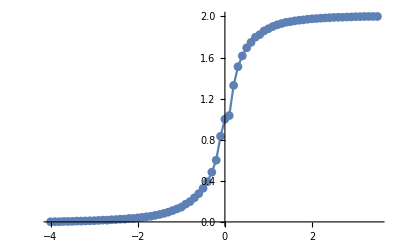

```mathematica
ListPlot[Table[{μ,fillingFu[μ,0.0]},{μ,-4.0,3.5,0.1}],Joined->True,PlotMarkers->Automatic,PlotRange->Full]
```

```mathematica
DdataFuSelfCons=Table[{4.0*(fillingFu[μ,0.0]-1.0),
Clear[DTFu];DTFu[μu_,T_]:=DTFu[μu,T]=Chop[(*Block[{},Print[T];*)Sum[Curvature[ k[[1]],k[[2]]][[n]](1+Exp[(Energies[ k[[1]],k[[2]]][[n]]-μu)/(T+0.000000001)])^-1,{n,2},{k,kSpan}]/Length[kSpan](*]*)];
Nest[DTFu[μ,π*#/2]&,0.0,20]},{μ,-4.0,3.5,0.1}]
```

General::munfl: Exp[-1.19934×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.14805×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.88932×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-3.99609,0.0162795},{-3.99289,0.0294356},{-3.98916,0.0422303},{-3.9852,0.0546908},{-3.98142,0.0668568},{-3.97689,0.078782},{-3.97302,0.090532},{-3.96756,0.102177},{-3.96253,0.113777},{-3.95702,0.125374},{-3.9508,0.136972},{-3.9436,0.148541},{-3.93662,0.160014},{-3.92836,0.171299},{-3.91991,0.182291},{-3.90996,0.192881},{-3.89929,0.202964},{-3.88742,0.212443},{-3.87413,0.221234},{-3.85951,0.229261},{-3.84262,0.236464},{-3.82349,0.242789},{-3.80144,0.248193},{-3.77591,0.252636},{-3.74604,0.256086},{-3.71164,0.258511},{-3.67038,0.259878},{-3.62151,0.260152},{-3.56258,0.259295},{-3.49502,0.25726},{-3.41516,0.253991},{-3.3164,0.249418},{-3.20133,0.243452},{-3.06231,0.235981},{-2.89486,0.226852},{-2.68516,0.215866},{-2.42277,0.202736},{-2.08058,0.187046},{-1.59025,0.16814},{-0.66543,0.144918},{-5.79216×10^-9,0.000119104},{0.138771,0.067701},{1.31674,0.127958},{2.03254,0.147292},{2.45822,0.162855},{2.76211,0.175367},{2.9952,0.185344},{3.1752,0.193129},{3.32,0.19896},{3.43787,0.203003},{3.53027,0.205378},{3.60915,0.20617},{3.67297,0.205441},{3.7241,0.203237},{3.76511,0.199595},{3.80018,0.19455},{3.82889,0.188142},{3.85321,0.180432},{3.87369,0.171508},{3.89156,0.161501},{3.90653,0.150595},{3.92013,0.139016},{3.93191,0.12702},{3.94209,0.114853},{3.95133,0.102709},{3.95956,0.0906946},{3.96676,0.0788155},{3.97316,0.0669868},{3.97902,0.0550722},{3.98462,0.0429288},{3.98942,0.0304396},{3.99449,0.0175247},{3.99862,0.00414232},{4.,2.0246×10^-8},{4.,2.0246×10^-8},{4.,2.0246×10^-8}}

```mathematica
Range[-4.0,3.5,0.1][[40;;42]]
```

{-0.1,0.,0.1}

```mathematica
DdataFuSelfCons[[40;;48]]
```

{{-0.572255,0.144918},{-0.0000197558,0.000119104},{0.479795,0.067701},{0.961601,0.127958},{1.37532,0.147292},{1.72712,0.162855},{2.03191,0.175367},{2.29907,0.185344},{2.53485,0.193129}}

```mathematica
DdataFuSelfCons=Table[Block[{D=DdataFuSelfCons[[i,2]]},{4.0*(fillingFuT[Range[-4.0,3.5,0.1][[i]],π/2*D]-1.0),D}],{i,Length[DdataFuSelfCons]}]
```

General::munfl: Exp[-22021.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-21290.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-19061.7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-3.99591,0.0162795},{-3.99262,0.0294356},{-3.9892,0.0422303},{-3.98497,0.0546908},{-3.98089,0.0668568},{-3.9764,0.078782},{-3.97147,0.090532},{-3.96608,0.102177},{-3.96014,0.113777},{-3.95352,0.125374},{-3.94607,0.136972},{-3.93761,0.148541},{-3.92788,0.160014},{-3.91654,0.171299},{-3.90314,0.182291},{-3.88713,0.192881},{-3.86788,0.202964},{-3.84468,0.212443},{-3.81675,0.221234},{-3.78333,0.229261},{-3.74364,0.236464},{-3.69694,0.242789},{-3.64249,0.248193},{-3.5796,0.252636},{-3.5076,0.256086},{-3.42581,0.258511},{-3.33353,0.259878},{-3.23005,0.260152},{-3.11457,0.259295},{-2.98621,0.25726},{-2.84395,0.253991},{-2.68658,0.249418},{-2.51263,0.243452},{-2.3203,0.235981},{-2.10726,0.226852},{-1.87048,0.215866},{-1.60591,0.202736},{-1.3078,0.187046},{-0.967714,0.16814},{-0.572255,0.144918},{-0.0000197558,0.000119104},{0.479795,0.067701},{0.961601,0.127958},{1.37532,0.147292},{1.72712,0.162855},{2.03191,0.175367},{2.29907,0.185344},{2.53485,0.193129},{2.74368,0.19896},{2.92876,0.203003},{3.09254,0.205378},{3.23694,0.20617},{3.36351,0.205441},{3.47357,0.203237},{3.56829,0.199595},{3.6488,0.19455},{3.71621,0.188142},{3.77174,0.180432},{3.81669,0.171508},{3.85252,0.161501},{3.88076,0.150595},{3.90296,0.139016},{3.92054,0.12702},{3.9347,0.114853},{3.94635,0.102709},{3.95614,0.0906946},{3.96453,0.0788155},{3.97185,0.0669868},{3.97834,0.0550722},{3.98401,0.0429288},{3.98965,0.0304396},{3.9936,0.0175247},{3.9989,0.00414232},{4.,2.0246×10^-8},{4.,2.0246×10^-8},{4.,2.0246×10^-8}}

```mathematica
i
```

1

```mathematica
ProgresskSpace[]
```

{2791,3600}

```mathematica
AbsoluteTiming[DdataFuSelfConsFine=ParallelTable[{4.0*(fillingFu[μ,0.0]-1.0),
Clear[DTFu];DTFu[μu_,T_]:=DTFu[μu,T]=Chop[(*Block[{},Print[T];*)Sum[Curvature[ k[[1]],k[[2]]][[n]](1+Exp[(Energies[ k[[1]],k[[2]]][[n]]-μu)/(T+0.000000001)])^-1,{n,2},{k,kSpan}]/Length[kSpan](*]*)];
Nest[DTFu[μ,π*#/2]&,0.0,20]},{μ,-0.5,0.5,0.02}]]
```

{1790.27,{{-2.68516,0.215866},{-2.63871,0.213422},{-2.58803,0.210891},{-2.53468,0.208268},{-2.48081,0.205551},{-2.42277,0.202736},{-2.36267,0.19982},{-2.29804,0.196797},{-2.23138,0.193664},{-2.15787,0.190416},{-2.08058,0.187046},{-1.99684,0.183549},{-1.90715,0.179918},{-1.80967,0.176146},{-1.70454,0.172223},{-1.59025,0.16814},{-1.46412,0.163888},{-1.32418,0.159453},{-1.16101,0.154823},{-0.957721,0.149983},{-0.66543,0.144918},{-0.431906,0.139611},{-0.257566,0.134033},{-0.046958,0.127442},{-0.00564467,0.00295335},{-5.79216×10^-9,0.000119104},{0.00540736,0.00278232},{0.0210293,0.00573526},{0.0468597,0.0089735},{0.083655,0.0143155},{0.138771,0.067701},{0.211655,0.108402},{0.307965,0.114289},{0.686271,0.119054},{1.06579,0.123587},{1.31674,0.127958},{1.50942,0.132161},{1.66601,0.136193},{1.80195,0.140055},{1.92232,0.143752},{2.03254,0.147292},{2.13291,0.150681},{2.22396,0.153926},{2.30803,0.157032},{2.38675,0.160007},{2.45822,0.162855},{2.52718,0.165582},{2.5904,0.168192},{2.65179,0.170691},{2.7092,0.173081},{2.76211,0.175367}}}

```mathematica
DdataFuSelfConsFine=Table[Block[{D=DdataFuSelfConsFine[[i,2]]},{4.0*(fillingFuT[Range[-0.5,0.5,0.02][[i]],π/2*D]-1.0),D}],{i,Length[DdataFuSelfConsFine]}]
```

General::munfl: Exp[-883.775] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-854.294] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-764.421] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-1.87048,0.215866},{-1.81995,0.213422},{-1.76826,0.210891},{-1.71539,0.208268},{-1.66129,0.205551},{-1.60591,0.202736},{-1.54919,0.19982},{-1.49108,0.196797},{-1.43153,0.193664},{-1.37046,0.190416},{-1.3078,0.187046},{-1.24348,0.183549},{-1.17741,0.179918},{-1.10949,0.176146},{-1.03963,0.172223},{-0.967714,0.16814},{-0.893609,0.163888},{-0.817176,0.159453},{-0.738261,0.154823},{-0.656686,0.149983},{-0.572255,0.144918},{-0.484747,0.139611},{-0.393934,0.134033},{-0.300554,0.127442},{-0.00737477,0.00295335},{-0.0000197558,0.000119104},{0.0056913,0.00278232},{0.0243682,0.00573526},{0.0572954,0.0089735},{0.130893,0.0143155},{0.479795,0.067701},{0.571975,0.108402},{0.674286,0.114289},{0.773751,0.119054},{0.869496,0.123587},{0.961601,0.127958},{1.0503,0.132161},{1.13581,0.136193},{1.21836,0.140055},{1.29814,0.143752},{1.37532,0.147292},{1.45005,0.150681},{1.52247,0.153926},{1.59272,0.157032},{1.6609,0.160007},{1.72712,0.162855},{1.79148,0.165582},{1.85407,0.168192},{1.91495,0.170691},{1.97421,0.173081},{2.03191,0.175367}}

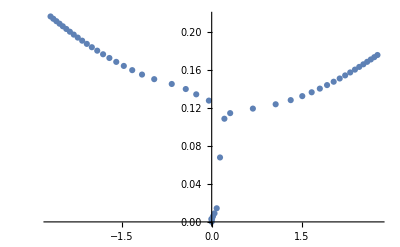

```mathematica
ListPlot[{DdataFuSelfConsFine]
```

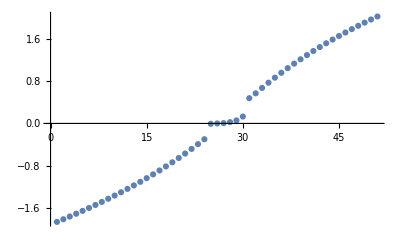

```mathematica
ListPlot[DdataFuSelfConsFine[[All,1]]]
```

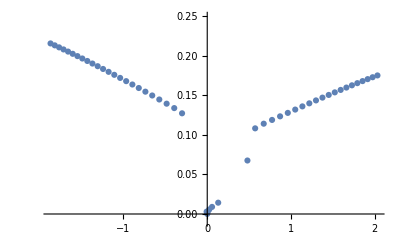

```mathematica
ListPlot[DdataFuSelfConsFine,PlotRange->{-0.01,0.25}]
```

```mathematica
AbsoluteTiming[DdataFuSelfConsFine=Table[{4.0*(fillingFu[μ,0.0]-1.0),
Clear[DTFu];DTFu[μu_,T_]:=DTFu[μu,T]=Chop[(*Block[{},Print[T];*)Sum[Curvature[ k[[1]],k[[2]]][[n]](1+Exp[(Energies[ k[[1]],k[[2]]][[n]]-μu)/(T+0.000000001)])^-1,{n,2},{k,kSpan}]/Length[kSpan](*]*)];
Nest[DTFu[μ,π*#/2]&,0.0,20]},{μ,-0.5,0.5,0.02}]]
```

```mathematica
μ
```

μ

```mathematica
DdataFu=Table[{4.0*(fillingFu[μ,0.0]-1.0),Rho0Fu[μ,0.0]},{μ,-4.0,3.5,0.1}]
```

{{-3.99609,0.0164427},{-3.99289,0.0288828},{-3.98916,0.0423427},{-3.9852,0.0554891},{-3.98142,0.067052},{-3.97689,0.0798932},{-3.97302,0.0899539},{-3.96756,0.103077},{-3.96253,0.114045},{-3.95702,0.125017},{-3.9508,0.136744},{-3.9436,0.148941},{-3.93662,0.160346},{-3.92836,0.171839},{-3.91991,0.183473},{-3.90996,0.195941},{-3.89929,0.207782},{-3.88742,0.220047},{-3.87413,0.231097},{-3.85951,0.242281},{-3.84262,0.25225},{-3.82349,0.262303},{-3.80144,0.271094},{-3.77591,0.279266},{-3.74604,0.286898},{-3.71164,0.293818},{-3.67038,0.298753},{-3.62151,0.302771},{-3.56258,0.306051},{-3.49502,0.306825},{-3.41516,0.304819},{-3.3164,0.298919},{-3.20133,0.291423},{-3.06231,0.281662},{-2.89486,0.266619},{-2.68516,0.247316},{-2.42277,0.225341},{-2.08058,0.194426},{-1.59025,0.153321},{-0.66543,0.064257},{-5.79216×10^-9,-0.000124221},{0.138771,0.0156492},{1.31674,0.0805305},{2.03254,0.136295},{2.45822,0.170754},{2.76211,0.193944},{2.9952,0.213179},{3.1752,0.2294},{3.32,0.239064},{3.43787,0.245779},{3.53027,0.247114},{3.60915,0.24461},{3.67297,0.240621},{3.7241,0.234028},{3.76511,0.225491},{3.80018,0.214912},{3.82889,0.202969},{3.85321,0.190547},{3.87369,0.17737},{3.89156,0.16426},{3.90653,0.151627},{3.92013,0.138322},{3.93191,0.125794},{3.94209,0.11379},{3.95133,0.101941},{3.95956,0.0900025},{3.96676,0.0784077},{3.97316,0.0669191},{3.97902,0.0551688},{3.98462,0.0427376},{3.98942,0.0308621},{3.99449,0.0169437},{3.99862,0.00442946},{4.,2.02914×10^-8},{4.,2.02632×10^-8},{4.,2.02561×10^-8}}

```mathematica
DdataFuAniso=Table[{4.0*(fillingFu[μ,0.0]-1.0),Module[{ρxx=Rho0Fu[μ,0.0],ρyy=Rho0Fuyy[μ,0.0]},(ρxx-ρyy)/ρxx*100]},{μ,-4.0,3.5,0.1}]
```

{{-3.99609,-0.160418},{-3.99289,-0.149038},{-3.98916,-0.135466},{-3.9852,-0.119362},{-3.98142,-0.10595},{-3.97689,-0.0865498},{-3.97302,-0.0714214},{-3.96756,-0.0492887},{-3.96253,0.0750844},{-3.95702,-0.0112062},{-3.9508,0.0491013},{-3.9436,-0.0565766},{-3.93662,0.0410106},{-3.92836,0.0489714},{-3.91991,-0.0271028},{-3.90996,0.0502513},{-3.89929,0.0485111},{-3.88742,0.0279616},{-3.87413,0.035904},{-3.85951,0.029114},{-3.84262,-0.0186243},{-3.82349,0.0783195},{-3.80144,-0.0217963},{-3.77591,-0.0444817},{-3.74604,0.013722},{-3.71164,0.0115476},{-3.67038,-0.0471258},{-3.62151,-0.0136638},{-3.56258,0.010412},{-3.49502,0.00651634},{-3.41516,-0.0700284},{-3.3164,-0.0508953},{-3.20133,-0.0647605},{-3.06231,0.0184761},{-2.89486,-0.0292241},{-2.68516,0.0194528},{-2.42277,0.117315},{-2.08058,-0.000856714},{-1.59025,-0.037303},{-0.66543,-0.786806},{-5.79216×10^-9,18.9292},{0.138771,-0.349458},{1.31674,-0.854087},{2.03254,0.0996594},{2.45822,-0.0526918},{2.76211,0.0211332},{2.9952,-0.205329},{3.1752,-0.155414},{3.32,-0.11081},{3.43787,-0.0804371},{3.53027,-0.0740455},{3.60915,-0.0217889},{3.67297,-0.0444286},{3.7241,0.161074},{3.76511,0.0338531},{3.80018,0.128639},{3.82889,0.116052},{3.85321,0.0961418},{3.87369,0.114149},{3.89156,-0.00465019},{3.90653,-0.0867305},{3.92013,-0.206123},{3.93191,-0.0227063},{3.94209,-0.079736},{3.95133,-0.109499},{3.95956,-0.10362},{3.96676,-0.119146},{3.97316,-0.135039},{3.97902,-0.15297},{3.98462,-0.171223},{3.98942,-0.189512},{3.99449,-0.20949},{3.99862,-0.227521},{4.,-0.000233101},{4.,0.000141956},{4.,0.000222619}}

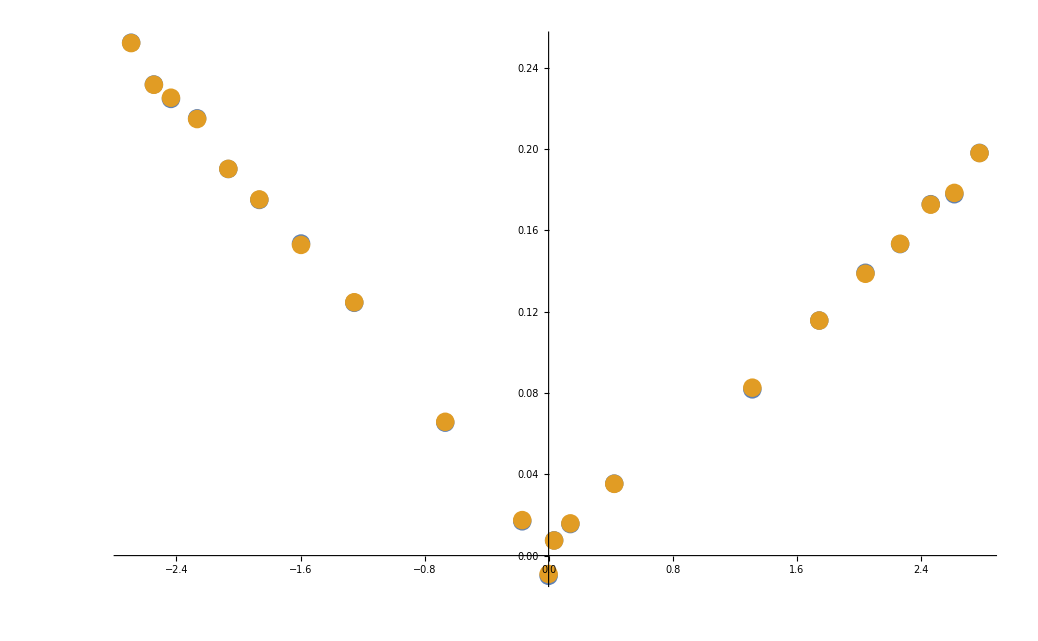

```mathematica
ListPlot[Table[{{4.0*(fillingFu[μ,0.0]-1.0),Rho0Fu[μ,0.0]},{4.0*(fillingFu[μ,0.0]-1.0),Rho0Fuyy[μ,0.0]}},{μ,-0.5,0.5,0.05}]//Transpose]
```

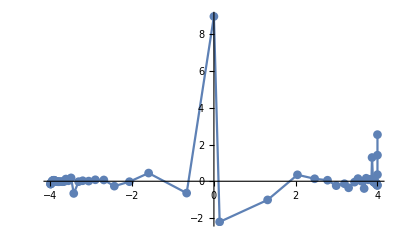

```mathematica
ListPlot[DdataFuAniso,Joined->True,PlotMarkers->Automatic,PlotRange->Full]
```

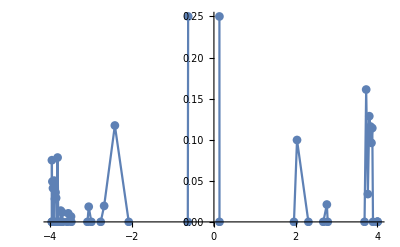

```mathematica
ListPlot[DdataFuAniso,Joined->True,PlotMarkers->Automatic,PlotRange->0.25]
```

```mathematica
μ
```

-4.

```mathematica
ProgresskSpace[]
```

{46520,90000}

```mathematica
DdataFuNearCNPN300=ParallelTable[{4.0*(fillingFu[μ,0.0]-1.0),Rho0Fu[μ,0.0]},{μ,-0.500001,0.5,0.01}]
```

{{-2.68516,0.247316},{-2.66142,0.246134},{-2.63871,0.24406},{-2.61213,0.241008},{-2.58803,0.239328},{-2.56155,0.237531},{-2.53468,0.235375},{-2.50875,0.232284},{-2.48081,0.230437},{-2.45137,0.228383},{-2.42277,0.22534},{-2.39329,0.222946},{-2.36268,0.220378},{-2.3302,0.217221},{-2.29804,0.214338},{-2.26633,0.21165},{-2.23138,0.208108},{-2.19525,0.204871},{-2.15787,0.201773},{-2.12009,0.197901},{-2.08058,0.194426},{-2.03987,0.190573},{-1.99684,0.18682},{-1.95303,0.18308},{-1.90715,0.179409},{-1.86016,0.175346},{-1.80967,0.171193},{-1.75836,0.16714},{-1.70455,0.16274},{-1.64798,0.157939},{-1.59026,0.153322},{-1.52946,0.148088},{-1.46413,0.142527},{-1.39641,0.136718},{-1.32419,0.130052},{-1.24582,0.122698},{-1.16102,0.114741},{-1.06634,0.105502},{-0.957734,0.0945754},{-0.81349,0.0798316},{-0.665439,0.0642577},{-0.536536,0.0517894},{-0.431914,0.0426636},{-0.342329,0.0341924},{-0.257574,0.0256466},{-0.16598,0.016543},{-0.0469753,0.00714892},{-0.0123585,0.00428349},{-0.00564468,0.00286977},{-0.00151112,0.00144571},{-5.80059×10^-9,-0.000124221},{0.00128255,0.00134419},{0.00540541,0.00281484},{0.0119993,0.00423159},{0.0210285,0.00568451},{0.0327054,0.00716965},{0.0468573,0.00865848},{0.0639987,0.0101663},{0.0836539,0.0116609},{0.108759,0.0134622},{0.138769,0.0156489},{0.173884,0.0182819},{0.211654,0.0211904},{0.256125,0.0242695},{0.307958,0.0272394},{0.418964,0.0347117},{0.686247,0.0497809},{0.900432,0.0585432},{1.06577,0.0659211},{1.20208,0.0733701},{1.31673,0.080529},{1.41926,0.0877365},{1.50941,0.0945099},{1.59048,0.100862},{1.666,0.107071},{1.73571,0.112619},{1.80194,0.117955},{1.86479,0.123075},{1.92232,0.1275},{1.97866,0.131789},{2.03254,0.136293},{2.08414,0.140462},{2.13291,0.144253},{2.17872,0.147866},{2.22396,0.151885},{2.2669,0.155222},{2.30803,0.158685},{2.34813,0.161724},{2.38674,0.164874},{2.42289,0.16802},{2.45821,0.170753},{2.49358,0.173526},{2.52718,0.176096},{2.55831,0.178445},{2.5904,0.181134},{2.62148,0.182952},{2.65178,0.185836},{2.67976,0.187753},{2.7092,0.189677},{2.73633,0.192312},{2.76211,0.193944}}

```mathematica
DdataFuNearCNP2N30=Table[{4.0*(fillingFu[μ,0.0]-1.0),Rho0Fu[μ,0.0]},{μ,-0.005001,0.005,0.0001}]
```

{{-0.00888888,0.00401195},{-0.00888887,0.00401194},{-0.00888887,0.00401194},{-0.00888887,0.00401194},{-0.00888887,0.00401193},{-0.00888887,0.00401193},{-0.00888887,0.00401192},{-0.00888887,0.00401192},{-0.00888887,0.00401191},{-0.00888886,0.00401191},{-0.00888886,0.0040119},{-0.00888886,0.00401189},{-0.00888886,0.00401189},{-0.00888886,0.00401188},{-0.00888885,0.00401187},{-0.00888885,0.00401185},{-0.00888885,0.00401184},{-0.00888884,0.00401182},{-0.00888884,0.00401181},{-0.00888883,0.00401178},{-0.00888883,0.00401176},{-0.00888882,0.00401173},{-0.00888881,0.0040117},{-0.0088888,0.00401166},{-0.00888879,0.00401161},{-0.00888878,0.00401155},{-0.00888876,0.00401147},{-0.00888874,0.00401138},{-0.00888872,0.00401126},{-0.00888868,0.00401111},{-0.00888864,0.00401089},{-0.00888857,0.0040106},{-0.00888847,0.00401016},{-0.00888832,0.00400948},{-0.00888806,0.00400829},{-0.00888753,0.00400594},{-0.00888613,0.00399986},{-0.00887972,0.00397231},{-0.00839025,0.00188699},{-0.00445774,-0.0148644},{-0.00444556,-0.0149185},{-0.00443972,-0.0149523},{-0.00436155,-0.0154575},{-0.000026601,-0.0435487},{-4.37154×10^-6,-0.0436924},{-1.77533×10^-6,-0.043709},{-9.64413×10^-7,-0.043714},{-5.99718×10^-7,-0.0437162},{-3.99728×10^-7,-0.0437174},{-2.74788×10^-7,-0.0437181},{-1.88628×10^-7,-0.0437185},{-1.23966×10^-7,-0.0437187},{-7.14084×10^-8,-0.0437189},{-2.51391×10^-8,-0.0437189},{1.90384×10^-8,-0.043719},{6.47952×10^-8,-0.0437189},{1.16107×10^-7,-0.0437188},{1.78207×10^-7,-0.0437185},{2.59138×10^-7,-0.0437182},{3.72897×10^-7,-0.0437176},{5.46896×10^-7,-0.0437166},{8.42775×10^-7,-0.0437149},{1.4284×10^-6,-0.0437114},{2.9263×10^-6,-0.0437021},{9.65308×10^-6,-0.0436592},{0.000558137,-0.0401069},{0.00443398,-0.0149989},{0.00446017,-0.0148632},{0.00871355,0.00326119},{0.0088809,0.00397548},{0.00888618,0.00399853},{0.00888748,0.00400438},{0.00888801,0.00400681},{0.00888828,0.00400808},{0.00888844,0.00400882},{0.00888854,0.0040093},{0.00888861,0.00400963},{0.00888866,0.00400987},{0.0088887,0.00401004},{0.00888873,0.00401018},{0.00888875,0.00401028},{0.00888877,0.00401036},{0.00888878,0.00401043},{0.00888879,0.00401048},{0.0088888,0.00401052},{0.00888881,0.00401056},{0.00888882,0.00401059},{0.00888882,0.00401062},{0.00888883,0.00401064},{0.00888883,0.00401066},{0.00888884,0.00401068},{0.00888884,0.00401069},{0.00888884,0.00401071},{0.00888885,0.00401072},{0.00888885,0.00401073},{0.00888885,0.00401074},{0.00888885,0.00401075},{0.00888886,0.00401075},{0.00888886,0.00401076},{0.00888886,0.00401077},{0.00888886,0.00401077}}

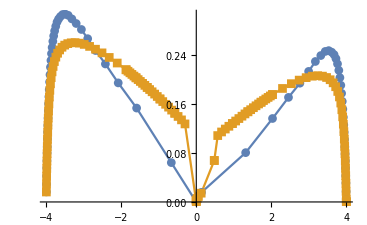

```mathematica
ListPlot[{DdataFu,(*DdataFuNearCNPN300,*)SortBy[Join[DdataFuSelfCons,DdataFuSelfConsFine],First]},Joined->True,PlotMarkers->Automatic,PlotRange->Full]
```

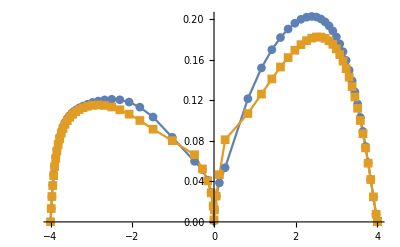

```mathematica
ListPlot[{DdataVish,DdataVishSelfCons},Joined->True,PlotMarkers->Automatic,PlotRange->Full]
```

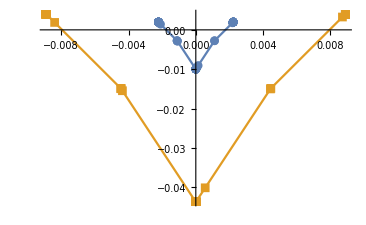

```mathematica
ListPlot[{(*DdataFuNearCNP,*)DdataFuNearCNP2,(*DdataFuNearCNPN30,*)DdataFuNearCNP2N30},Joined->True,PlotMarkers->Automatic,PlotRange->Full]
```

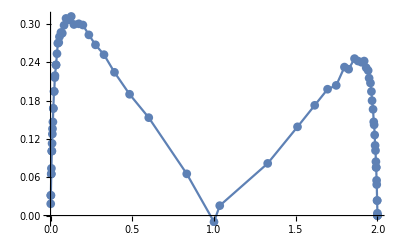

```mathematica
ListPlot[Table[{fillingFu[μ,0.0],Rho0Fu[μ,0.0]},{μ,-4.0,3.5,0.1}],Joined->True,PlotMarkers->Automatic,PlotRange->Full]
```

```mathematica
μ
```

-0.500001

```mathematica
arrc=Select[arr,Abs[π/2*#[[4]]]<#[[2]]/1.76&&#[[4]]>0&];
```

```mathematica
arrc=Table[If[Abs[π/2*dat[[4]]]<dat[[2]]/1.76&&dat[[4]]>0,dat,{dat[[1]],dat[[2]],dat[[3]],100000}],{dat,arr}];
```

```mathematica
11.6045*(π/8)*4*0.3
```

5.46849

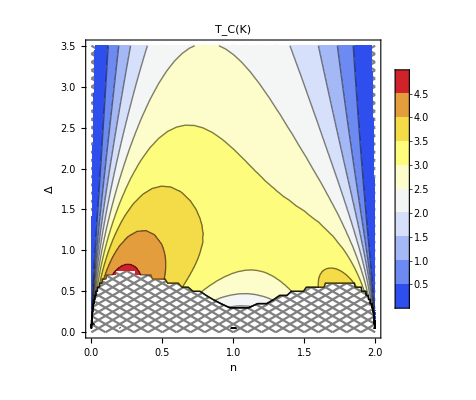

```mathematica
Show[Plot[Join[Table[x+r*0.1,{r,-100,100}],Table[-x+r*0.1,{r,-100,100}]],{x,0,2},AspectRatio->1,PlotRange->{0,3.5},PlotLabel->"T_C(K)",PlotStyle->Directive[Thin,Gray],PlotRangePadding->None,LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],Frame->True,FrameLabel->{{"Δ",None},{"n",None}}],
ListContourPlot[({arrc[[All,3]],arrc[[All,2]],11.6045*(π/8)*4*Re[arrc[[All,4]]]}//Transpose),LabelStyle->Directive[FontFamily->"Calibri",20,Black],PlotRange->{Automatic,Automatic,{0,5.0}},Contours->9,PlotLegends->Automatic,PlotRangePadding->None,AxesOrigin->{0.,0.},ColorFunction->"TemperatureMap"]]
```

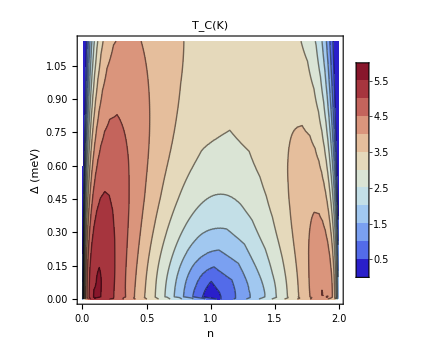
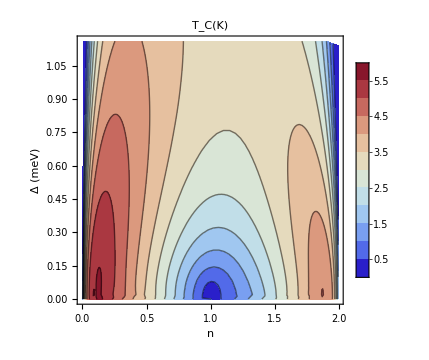

```mathematica
Row[{arrx=Re[arrFu[[;;Quotient[Length[arrFu],3]]]];Show[ListContourPlot[({arrx[[All,3]],arrx[[All,2]],11.6045*(π/8)*4*Re[arrx[[All,4]]]}//Transpose),PlotRange->{Automatic,Automatic,{0,6}},PlotLabel->"T_C(K)",PlotRangePadding->None,LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],Frame->True,FrameLabel->{{"Δ (meV)",None},{"n",None}},Contours->11,PlotLegends->Automatic,AxesOrigin->{0.,0.},ColorFunction->"ThermometerColors"],ImageSize->Medium],
arry=Re[arrFuyy[[;;Quotient[Length[arrFuyy],3]]]];Show[ListContourPlot[({arry[[All,3]],arry[[All,2]],11.6045*(π/8)*4*Re[arry[[All,4]]]}//Transpose),PlotRange->{Automatic,Automatic,{0,6}},PlotLabel->"T_C(K)",PlotRangePadding->None,LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],Frame->True,FrameLabel->{{"Δ (meV)",None},{"n",None}},Contours->11,PlotLegends->Automatic,AxesOrigin->{0.,0.},ColorFunction->"ThermometerColors"],ImageSize->Medium]}]
```

```mathematica
(arrFu-arrFuyy)[[All,{2,3}]]
```

Thread::tdlen: Objects of unequal length in {{-37.,0,0,0},{-36.2101,0,0,0},{-35.4201,0,0,0},{-34.6302,0,0,0},{-33.8402,0,0,0},{-33.0503,0,0,0},{-32.2603,0,0,0},{-31.4704,0,0,0},{-30.6805,0,0,0},{-29.8905,0,0,0},{-29.1006,0,0,0},«29»,{-5.40228,0,0,0},{-4.61234,0,0,0},{-3.82239,0,0.00194444,0.0316047},{-3.03245,0,0.0119444,0.136045},{-2.24251,0,0.0286111,0.217209},{-1.45256,0,0.0777778,0.297038},{-0.662621,0,0.253879,0.267248},{0.127322,0,1.06056,0.0231577},{0.917266,0,1.86222,0.24418},{1.70721,0,1.96389,0.191692},«17851»}+{«1»} cannot be combined.

{{0.592457,0,0,0},{1.18491,0,0,0}}

```mathematica
arrFu[[All,2]]-arrFuyy[[All,2]]
```

Thread::tdlen: Objects of unequal length in {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«17851»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«14824»} cannot be combined.

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,14676,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46,-1.46}+1
 |  |  |  |

```mathematica
Position
```

```mathematica
arrdiffpercent=Table[If[Norm[{arrFu[[i,3]],arrFu[[i,2]]}-{arrFuyy[[i,3]],arrFuyy[[i,2]]}]<10^-3&&arrFu[[i,4]]≠0,{arrFu[[i,3]],arrFu[[i,2]],(arrFu[[i,4]]-arrFuyy[[i,4]])/arrFu[[i,4]]*100},Nothing],{i,Length[arrFuyy]}];
```

```mathematica
arrdiffpercent
```

{}

```mathematica
ListContourPlot[arrdiffpercent,PlotRange->{Automatic,Automatic,{0,6}},PlotLabel->"T_C(K)",PlotRangePadding->None,LabelStyle->Directive[FontFamily->"Calibri",20,Black],FrameStyle->Directive[Black,Thick],Frame->True,FrameLabel->{{"Δ (meV)",None},{"n",None}},Contours->11,PlotLegends->Automatic,AxesOrigin->{0.,0.},ColorFunction->"ThermometerColors"]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of System`ListPlotsDump`dataextremes$13699.

-Graphics-

```mathematica
ListContourPlot[({arrc[[All,3]],arrc[[All,2]],11.6045*(π/8)*4*Re[arrc[[All,4]]]}//Transpose),PlotRange->{{0,2},{0,1},Full},PlotLegends->Automatic,Contours->20,AxesOrigin->{0.,0.}]
```

-Graphics-

```mathematica
P1 = DiscretePlot[{Energies[kx,kx/(√3)],Energies[-kx,-kx/(√3)]},{kx,-2 π/(√3),0,0.1},Joined->True,Filling->None];
```

```mathematica
P2= DiscretePlot[{Energies[kx,0],Energies[-kx,0]},{kx,0,2 π/(√3),0.1},Joined->True,Filling->None];
```

```mathematica
P3 = DiscretePlot[{Energies[2 π/(√3),(ky-2 π/(√3))],Energies[-2 π/(√3),-(ky-2 π/(√3))]},{ky,2 π/(√3),2 π/3+2 π/(√3),0.1},Joined->True,Filling->None];
```

```mathematica
Show[P1,P2,P3,PlotRange->All]
```

-Graphics-

```mathematica
Ham[2 π/(√3),2 π/3]//MatrixForm // Chop
```

(-6.00399×10^-7 | -3.18641×10^-7-4.97113×10^-7 ⅈ
-3.18641×10^-7+4.97113×10^-7 ⅈ | 1.34514×10^-6)

```mathematica
Energies[2 π/(√3),2 π/3]
```

{-0.000765581,0.00151032}

```mathematica
KpG = Table[ {kx,kx/(√3)},{kx,-2 π/(√3),0,0.1}];
GM = Table[ {kx,0},{kx,0,2 π/(√3),0.1}];
MK = Table[ {2 π/(√3),(ky-2 π/(√3))},{ky,2 π/(√3),2 π/3+2 π/(√3),0.1}] ;
```

```mathematica
kCut = Join[KpG ,GM ,MK];
```

```mathematica
ListPlot[{Table[Energies[k[[1]],k[[2]]][[1]],{k,kCut}],Table[Energies[-k[[1]],-k[[2]]][[1]],{k,kCut}],
Table[Energies[k[[1]],k[[2]]][[2]],{k,kCut}],Table[Energies[-k[[1]],-k[[2]]][[2]],{k,kCut}]},LabelStyle->Directive[Black,20,FontFamily->"Calibri"],
Axes->{False,True},Frame->True,FrameStyle->Directive[Black,Thick],PlotRange->{Automatic,{-5,4}},FrameTicks->{{{1,"K'"},{Length[KpG],"Γ"},{Length[KpG]+Length[GM],"M"},{Length[KpG]+Length[MK]+Length[GM],"K"}},Automatic},PlotMarkers->{Automatic,5},PlotStyle->{Red,Blue,Red,Blue},FrameLabel->{None,"E (meV)"}]
```

-Graphics-

#### For arbit tight binding hamiltonian

```mathematica
Nsites=30;kSpan=Flatten[Table[{kx,ky},{kx,-π,π-2π/Nsites,2π/Nsites},{ky,-π,π-2π/Nsites,2π/Nsites}],1];
```

```mathematica
Clear[ham];ham[k_?ListQ,μ_]:=TBGHam[k[[1]],k[[2]]]-μ IdentityMatrix[14];
```

```mathematica
TBGHam[kx,ky]//MatrixForm
```

(0 | -kx-ⅈ ky | 1/(√3) | 1/(√3) | (2 ⅈ π)/(3 √3) | 1/(√3) | -(2 ⅈ π)/(3 √3) | 1/(√3) | 1/(√3) | 1/(√3) | (2 ⅈ π)/(3 √3) | 1/(√3) | -(2 ⅈ π)/(3 √3) | 1/(√3)
-kx+ⅈ ky | 0 | 1/(√3) | 1/(√3) | -(2 ⅈ π)/(3 √3) | (2 ⅈ π)/(3 √3) | (2 ⅈ π)/(3 √3) | -(2 ⅈ π)/(3 √3) | 1/(√3) | 1/(√3) | -(2 ⅈ π)/(3 √3) | (2 ⅈ π)/(3 √3) | (2 ⅈ π)/(3 √3) | -(2 ⅈ π)/(3 √3)
1/(√3) | 1/(√3) | 0 | -kx-ⅈ (-1+ky) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√3) | 1/(√3) | -kx+ⅈ (-1+ky) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 ⅈ π)/(3 √3) | (2 ⅈ π)/(3 √3) | 0 | 0 | 0 | -(√3)/2-kx-ⅈ (1/2+ky) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√3) | -(2 ⅈ π)/(3 √3) | 0 | 0 | -(√3)/2-kx+ⅈ (1/2+ky) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(2 ⅈ π)/(3 √3) | -(2 ⅈ π)/(3 √3) | 0 | 0 | 0 | 0 | 0 | (√3)/2-kx-ⅈ (1/2+ky) | 0 | 0 | 0 | 0 | 0 | 0
1/(√3) | (2 ⅈ π)/(3 √3) | 0 | 0 | 0 | 0 | (√3)/2-kx+ⅈ (1/2+ky) | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√3) | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -kx-ⅈ (1+ky) | 0 | 0 | 0 | 0
1/(√3) | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | -kx+ⅈ (1+ky) | 0 | 0 | 0 | 0 | 0
-(2 ⅈ π)/(3 √3) | (2 ⅈ π)/(3 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√3)/2-kx-ⅈ (-1/2+ky) | 0 | 0
1/(√3) | -(2 ⅈ π)/(3 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√3)/2-kx+ⅈ (-1/2+ky) | 0 | 0 | 0
(2 ⅈ π)/(3 √3) | -(2 ⅈ π)/(3 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√3)/2-kx-ⅈ (-1/2+ky)
1/(√3) | (2 ⅈ π)/(3 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√3)/2-kx+ⅈ (-1/2+ky) | 0)

```mathematica
Clear[eig];eig[k_?ListQ]:=TBGHam[k[[1]],k[[2]]]//N//Eigenvalues//Sort
```

```mathematica
ND[eig[{0.0,0.0}][[7]],{
```

{-4.10137,-2.5932,-1.,-1.,-1.,-1.,9.65499×10^-17,9.74147×10^-16,1.,1.,1.,1.,2.5932,4.10137}

```mathematica
TBGHam[0.0,0.0]//N//Eigenvalues//Sort
```

{-4.10137,-2.5932,-1.,-1.,-1.,-1.,9.65499×10^-17,9.74147×10^-16,1.,1.,1.,1.,2.5932,4.10137}

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
eig[{kx,ky}][[7]]
```

$Aborted

```mathematica
(SortBy[TBGHam[0.0,.5]//N//Eigensystem//Transpose,First]//Transpose)[[2,7;;8]]//MatrixForm
```

(-0.153932+0.156116 ⅈ | -0.155803-0.100544 ⅈ | 0.0499901+0.360783 ⅈ | -0.0785522-0.355658 ⅈ | -0.25983+0.0175576 ⅈ | 0.149929-0.175331 ⅈ | 0.036439+0.067357 ⅈ | 0.155285+0.175145 ⅈ | -0.022978-0.118954 ⅈ | 0.0198089+0.119522 ⅈ | 0.251389-0.321849 ⅈ | -0.36415+0.0100196 ⅈ | 0.0295311-0.113465 ⅈ | -0.357684+0. ⅈ
0.158168+0.151823 ⅈ | 0.152978-0.104791 ⅈ | 0.0400479-0.362021 ⅈ | -0.0687402+0.357684 ⅈ | 0.0345726-0.0683338 ⅈ | 0.150409-0.17935 ⅈ | -0.260214-0.0104044 ⅈ | 0.154695+0.171141 ⅈ | -0.0196975+0.119541 ⅈ | 0.016514-0.120022 ⅈ | 0.0326407+0.112609 ⅈ | -0.357549+0.009838 ⅈ | 0.260146+0.314813 ⅈ | -0.364288+0. ⅈ)

```mathematica
(SortBy[TBGHam[0.0,-.5]//N//Eigensystem//Transpose,First]//Transpose)[[2,7;;8]]//MatrixForm
```

(-0.218692+0.0155304 ⅈ | -0.0248423+0.183756 ⅈ | 0.0754732+0.0947723 ⅈ | -0.0779649-0.0927333 ⅈ | 0.105427+0.0512971 ⅈ | -0.232461+0.271845 ⅈ | 0.407989+0.0181125 ⅈ | -0.244278+0.270248 ⅈ | -0.241712-0.272468 ⅈ | 0.219254+0.290845 ⅈ | -0.0275104-0.0714699 ⅈ | -0.0321928-0.231847 ⅈ | -0.182209+0.186064 ⅈ | 0.230694+0. ⅈ
0.0146947+0.218749 ⅈ | -0.178593+0.049879 ⅈ | 0.104252+0.0617215 ⅈ | -0.102575-0.06447 ⅈ | 0.0740528+0.401621 ⅈ | 0.234083-0.279125 ⅈ | 0.0653095+0.0973702 ⅈ | 0.237291-0.26764 ⅈ | -0.303122-0.201941 ⅈ | 0.318236+0.177169 ⅈ | 0.159236-0.206067 ⅈ | 0.0317282+0.228501 ⅈ | -0.0745744-0.0174194 ⅈ | -0.234071+0. ⅈ)

```mathematica
DiscretePlot[{eig[{0.0,ky}][[7]],eig[{0.0,ky}][[8]]},{ky,-2.0,2.0,0.01},Filling->None,Joined->True,PlotRange->.2]
```

-Graphics-

```mathematica
Block[{ky=0.2+0.000001},((eig[{0.0,ky}][[8]]-eig[{0.0,ky-0.0000001}][[8]])/0.0000001-(eig[{0.0,ky-0.0000001}][[8]]-eig[{0.0,ky-0.0000002}][[8]])/0.0000001)/0.0000001]
```

-0.547045

```mathematica
Block[{ky=0.2+0.000002},1/0.0000001(1/0.0000001(eig[{0.0,ky}][[8]]-eig[{0.0,ky-0.0000001}][[8]])-1/0.0000001(eig[{0.0,ky-0.0000001}][[8]]-eig[{0.0,ky-0.0000002}][[8]]))]
```

-0.345123

```mathematica
Table[1,{ky,-3.0,3.0-0.01,0.01},{kx,-3.0,3.0-0.01,0.01}]//Length
```

600

Order of Magnitude of SF stiffness

```mathematica
Sum[Block[{ϵ=10^-4,n=8},Abs[(eig[{kx,ky+ϵ}][[n]]+eig[{kx,ky-ϵ}][[n]]-2eig[{kx,ky}][[n]])/ϵ^2]],{ky,-3.0,3.0-0.01,0.01},{kx,-3.0,3.0-0.01,0.01}]/(600)^2
```

0.601789

about 70K.

```mathematica
{kx,ky}
```

{-1.89,-0.75}

```mathematica
DiscretePlot3D[Block[{ϵ=10^-4,n=8},Abs[(eig[{kx,ky+ϵ}][[n]]+eig[{kx,ky-ϵ}][[n]]-2eig[{kx,ky}][[n]])/ϵ^2]],{ky,-5.0,5.0,0.1},{kx,-5.0,5.0,0.1},Filling->None,Joined->True,PlotRange->{0,10},AxesLabel->{kx,ky},ColorFunction->"Rainbow",ColorFunctionScaling->True]
```

-Graphics3D-

```mathematica
Sum[
```

```mathematica
DiscretePlot[Block[{ϵ=10^-4,n=8,kx=0.0},Abs[(eig[{kx,ky+ϵ}][[n]]+eig[{kx,ky-ϵ}][[n]]-2eig[{kx,ky}][[n]])/ϵ^2]],{ky,0.0,5.0,0.01},Filling->None,Joined->True(*,PlotRange->.01*)]
```

-Graphics-

```mathematica
ND[eig[{0.0,ky}][[8]],{ky,2},0,Method->NIntegrate]
```

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

Part::partw: Part 8 of Eigenvalues[{{0.,0.-(0.+1. ⅈ) ky,0.57735,0.57735,0.+1.2092 ⅈ,0.57735,0.-1.2092 ⅈ,0.57735,0.57735,0.57735,0.+1.2092 ⅈ,0.57735,0.-1.2092 ⅈ,0.57735},{0.+(0.+1. ⅈ) ky,0.,0.57735,0.57735,0.-1.2092 ⅈ,0.+1.2092 ⅈ,0.+1.2092 ⅈ,0.-1.2092 ⅈ,0.57735,0.57735,0.-1.2092 ⅈ,0.+1.2092 ⅈ,0.+1.2092 ⅈ,0.-1.2092 ⅈ},«10»,{0.+1.2092 ⅈ,0.-1.2092 ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.866025-(0.+1. ⅈ) (-0.5+ky)},{0.57735,0.+1.2092 ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.866025+(0.+1. ⅈ) (-0.5+ky),0.}}] does not exist.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

Part::partw: Part 8 of Eigenvalues[{{0.,0.-(0.+1. ⅈ) NumericalCalculus`Private`z$1286283,0.57735,0.57735,0.+1.2092 ⅈ,0.57735,0.-1.2092 ⅈ,0.57735,0.57735,0.57735,0.+1.2092 ⅈ,0.57735,0.-1.2092 ⅈ,0.57735},{0.+(0.+1. ⅈ) NumericalCalculus`Private`z$1286283,0.,0.57735,0.57735,0.-1.2092 ⅈ,0.+1.2092 ⅈ,0.+1.2092 ⅈ,0.-1.2092 ⅈ,0.57735,0.57735,0.-1.2092 ⅈ,0.+1.2092 ⅈ,0.+1.2092 ⅈ,0.-1.2092 ⅈ},«11»,{0.57735,0.+1.2092 ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.866025+(0.+1. ⅈ) (-0.5+NumericalCalculus`Private`z$1286283),0.}}] does not exist.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

General::stop: Further output of Eigenvalues::eival will be suppressed during this calculation.

Part::partw: Part 8 of Eigenvalues[{{0.,0.-(0.+1. ⅈ) ⅇ^(ⅈ NumericalCalculus`Private`t$1286283),0.57735,0.57735,0.+1.2092 ⅈ,0.57735,0.-1.2092 ⅈ,0.57735,0.57735,0.57735,0.+1.2092 ⅈ,0.57735,0.-1.2092 ⅈ,0.57735},{0.+(0.+1. ⅈ) ⅇ^(ⅈ NumericalCalculus`Private`t$1286283),0.,0.57735,0.57735,0.-1.2092 ⅈ,0.+1.2092 ⅈ,0.+1.2092 ⅈ,0.-1.2092 ⅈ,0.57735,0.57735,0.-1.2092 ⅈ,0.+1.2092 ⅈ,0.+1.2092 ⅈ,0.-1.2092 ⅈ},«11»,{0.57735,0.+1.2092 ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.866025+(0.+1. ⅈ) (-0.5+ⅇ^Times[«2»]),0.}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in NumericalCalculus`Private`t$1286283 in the region {{0.,6.28319}}. NIntegrate obtained 0.0739918+0.182044 ⅈ and 0.0566092 for the integral and error estimates.

0.0235523+0.0579465 ⅈ

```mathematica
Clear[d2hdkx2];d2hdkx2[k_]:=Module[{},h=ham[{kxx,ky},0.0];D[h,{kxx,2}]/.kxx->k[[1]]/.ky->k[[2]]]
```

```mathematica
Clear[Rho0Max];Rho0Max[vars_?ListQ,kx_,ky_]:=Block[{n=7},
{kx,ky,
eig=Eigensystem[ham[{kx,ky},vars[[1]]]];
eig=Transpose[SortBy[Transpose[eig],First]];
(*Table[*)Abs[Conjugate[eig[[2,n]]].d2hdkx2[{kx,ky}].eig[[2,n]]](*,{n,14}]*)
}
]
```

```mathematica
ham[{kx,ky},0]
```

```mathematica
D[
```

```mathematica
D[{{0,-kx-ⅈ (1+ky),1/(√3),1/(√3),(2 ⅈ π)/(3 √3),1/(√3),-(2 ⅈ π)/(3 √3),1/(√3),1/(√3),1/(√3),(2 ⅈ π)/(3 √3),1/(√3),-(2 ⅈ π)/(3 √3),1/(√3)},{-kx+ⅈ (1+ky),0,1/(√3),1/(√3),-(2 ⅈ π)/(3 √3),(2 ⅈ π)/(3 √3),(2 ⅈ π)/(3 √3),-(2 ⅈ π)/(3 √3),1/(√3),1/(√3),-(2 ⅈ π)/(3 √3),(2 ⅈ π)/(3 √3),(2 ⅈ π)/(3 √3),-(2 ⅈ π)/(3 √3)},{1/(√3),1/(√3),0,-kx-ⅈ ky,0,0,0,0,0,0,0,0,0,0},{1/(√3),1/(√3),-kx+ⅈ ky,0,0,0,0,0,0,0,0,0,0,0},{-(2 ⅈ π)/(3 √3),(2 ⅈ π)/(3 √3),0,0,0,-(√3)/2-kx-ⅈ (3/2+ky),0,0,0,0,0,0,0,0},{1/(√3),-(2 ⅈ π)/(3 √3),0,0,-(√3)/2-kx+ⅈ (3/2+ky),0,0,0,0,0,0,0,0,0},{(2 ⅈ π)/(3 √3),-(2 ⅈ π)/(3 √3),0,0,0,0,0,(√3)/2-kx-ⅈ (3/2+ky),0,0,0,0,0,0},{1/(√3),(2 ⅈ π)/(3 √3),0,0,0,0,(√3)/2-kx+ⅈ (3/2+ky),0,0,0,0,0,0,0},{1/(√3),1/(√3),0,0,0,0,0,0,0,-kx-ⅈ (2+ky),0,0,0,0},{1/(√3),1/(√3),0,0,0,0,0,0,-kx+ⅈ (2+ky),0,0,0,0,0},{-(2 ⅈ π)/(3 √3),(2 ⅈ π)/(3 √3),0,0,0,0,0,0,0,0,0,(√3)/2-kx-ⅈ (1/2+ky),0,0},{1/(√3),-(2 ⅈ π)/(3 √3),0,0,0,0,0,0,0,0,(√3)/2-kx+ⅈ (1/2+ky),0,0,0},{(2 ⅈ π)/(3 √3),-(2 ⅈ π)/(3 √3),0,0,0,0,0,0,0,0,0,0,0,-(√3)/2-kx-ⅈ (1/2+ky)},{1/(√3),(2 ⅈ π)/(3 √3),0,0,0,0,0,0,0,0,0,0,-(√3)/2-kx+ⅈ (1/2+ky),0}},{kx,2}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
d2hdkx2[{kx,ky}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
D[ham[{kx,ky},0],{kx,2}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Table[Rho0Max[{0.0},k[[1]],k[[2]]],{k,kSpan}]
```

{{-π,-π,0.},{-π,-(14 π)/15,0.},{-π,-(13 π)/15,0.},{-π,-(4 π)/5,0.},{-π,-(11 π)/15,0.},{-π,-(2 π)/3,0.},{-π,-(3 π)/5,0.},{-π,-(8 π)/15,0.},{-π,-(7 π)/15,0.},{-π,-(2 π)/5,0.},{-π,-π/3,0.},{-π,-(4 π)/15,0.},{-π,-π/5,0.},{-π,-(2 π)/15,0.},{-π,-π/15,0.},{-π,0,0.},{-π,π/15,0.},{-π,(2 π)/15,0.},{-π,π/5,0.},{-π,(4 π)/15,0.},{-π,π/3,0.},{-π,(2 π)/5,0.},{-π,(7 π)/15,0.},{-π,(8 π)/15,0.},{-π,(3 π)/5,0.},{-π,(2 π)/3,0.},{-π,(11 π)/15,0.},{-π,(4 π)/5,0.},{-π,(13 π)/15,0.},{-π,(14 π)/15,0.},{-(14 π)/15,-π,0.},{-(14 π)/15,-(14 π)/15,0.},{-(14 π)/15,-(13 π)/15,0.},{-(14 π)/15,-(4 π)/5,0.},{-(14 π)/15,-(11 π)/15,0.},{-(14 π)/15,-(2 π)/3,0.},{-(14 π)/15,-(3 π)/5,0.},{-(14 π)/15,-(8 π)/15,0.},{-(14 π)/15,-(7 π)/15,0.},{-(14 π)/15,-(2 π)/5,0.},{-(14 π)/15,-π/3,0.},{-(14 π)/15,-(4 π)/15,0.},{-(14 π)/15,-π/5,0.},{-(14 π)/15,-(2 π)/15,0.},{-(14 π)/15,-π/15,0.},{-(14 π)/15,0,0.},{-(14 π)/15,π/15,0.},{-(14 π)/15,(2 π)/15,0.},{-(14 π)/15,π/5,0.},{-(14 π)/15,(4 π)/15,0.},{-(14 π)/15,π/3,0.},{-(14 π)/15,(2 π)/5,0.},{-(14 π)/15,(7 π)/15,0.},{-(14 π)/15,(8 π)/15,0.},{-(14 π)/15,(3 π)/5,0.},{-(14 π)/15,(2 π)/3,0.},{-(14 π)/15,(11 π)/15,0.},{-(14 π)/15,(4 π)/5,0.},{-(14 π)/15,(13 π)/15,0.},{-(14 π)/15,(14 π)/15,0.},{-(13 π)/15,-π,0.},{-(13 π)/15,-(14 π)/15,0.},{-(13 π)/15,-(13 π)/15,0.},{-(13 π)/15,-(4 π)/5,0.},{-(13 π)/15,-(11 π)/15,0.},{-(13 π)/15,-(2 π)/3,0.},{-(13 π)/15,-(3 π)/5,0.},{-(13 π)/15,-(8 π)/15,0.},{-(13 π)/15,-(7 π)/15,0.},{-(13 π)/15,-(2 π)/5,0.},{-(13 π)/15,-π/3,0.},{-(13 π)/15,-(4 π)/15,0.},{-(13 π)/15,-π/5,0.},{-(13 π)/15,-(2 π)/15,0.},{-(13 π)/15,-π/15,0.},{-(13 π)/15,0,0.},{-(13 π)/15,π/15,0.},{-(13 π)/15,(2 π)/15,0.},{-(13 π)/15,π/5,0.},{-(13 π)/15,(4 π)/15,0.},{-(13 π)/15,π/3,0.},{-(13 π)/15,(2 π)/5,0.},{-(13 π)/15,(7 π)/15,0.},{-(13 π)/15,(8 π)/15,0.},{-(13 π)/15,(3 π)/5,0.},{-(13 π)/15,(2 π)/3,0.},{-(13 π)/15,(11 π)/15,0.},{-(13 π)/15,(4 π)/5,0.},{-(13 π)/15,(13 π)/15,0.},{-(13 π)/15,(14 π)/15,0.},{-(4 π)/5,-π,0.},{-(4 π)/5,-(14 π)/15,0.},{-(4 π)/5,-(13 π)/15,0.},{-(4 π)/5,-(4 π)/5,0.},{-(4 π)/5,-(11 π)/15,0.},{-(4 π)/5,-(2 π)/3,0.},{-(4 π)/5,-(3 π)/5,0.},{-(4 π)/5,-(8 π)/15,0.},{-(4 π)/5,-(7 π)/15,0.},{-(4 π)/5,-(2 π)/5,0.},{-(4 π)/5,-π/3,0.},{-(4 π)/5,-(4 π)/15,0.},{-(4 π)/5,-π/5,0.},{-(4 π)/5,-(2 π)/15,0.},{-(4 π)/5,-π/15,0.},{-(4 π)/5,0,0.},{-(4 π)/5,π/15,0.},{-(4 π)/5,(2 π)/15,0.},{-(4 π)/5,π/5,0.},{-(4 π)/5,(4 π)/15,0.},{-(4 π)/5,π/3,0.},{-(4 π)/5,(2 π)/5,0.},{-(4 π)/5,(7 π)/15,0.},{-(4 π)/5,(8 π)/15,0.},{-(4 π)/5,(3 π)/5,0.},{-(4 π)/5,(2 π)/3,0.},{-(4 π)/5,(11 π)/15,0.},{-(4 π)/5,(4 π)/5,0.},{-(4 π)/5,(13 π)/15,0.},{-(4 π)/5,(14 π)/15,0.},{-(11 π)/15,-π,0.},{-(11 π)/15,-(14 π)/15,0.},{-(11 π)/15,-(13 π)/15,0.},{-(11 π)/15,-(4 π)/5,0.},{-(11 π)/15,-(11 π)/15,0.},{-(11 π)/15,-(2 π)/3,0.},{-(11 π)/15,-(3 π)/5,0.},{-(11 π)/15,-(8 π)/15,0.},{-(11 π)/15,-(7 π)/15,0.},{-(11 π)/15,-(2 π)/5,0.},{-(11 π)/15,-π/3,0.},{-(11 π)/15,-(4 π)/15,0.},{-(11 π)/15,-π/5,0.},{-(11 π)/15,-(2 π)/15,0.},{-(11 π)/15,-π/15,0.},{-(11 π)/15,0,0.},{-(11 π)/15,π/15,0.},{-(11 π)/15,(2 π)/15,0.},{-(11 π)/15,π/5,0.},{-(11 π)/15,(4 π)/15,0.},{-(11 π)/15,π/3,0.},{-(11 π)/15,(2 π)/5,0.},{-(11 π)/15,(7 π)/15,0.},{-(11 π)/15,(8 π)/15,0.},{-(11 π)/15,(3 π)/5,0.},{-(11 π)/15,(2 π)/3,0.},{-(11 π)/15,(11 π)/15,0.},{-(11 π)/15,(4 π)/5,0.},{-(11 π)/15,(13 π)/15,0.},{-(11 π)/15,(14 π)/15,0.},{-(2 π)/3,-π,0.},{-(2 π)/3,-(14 π)/15,0.},{-(2 π)/3,-(13 π)/15,0.},{-(2 π)/3,-(4 π)/5,0.},{-(2 π)/3,-(11 π)/15,0.},{-(2 π)/3,-(2 π)/3,0.},{-(2 π)/3,-(3 π)/5,0.},{-(2 π)/3,-(8 π)/15,0.},{-(2 π)/3,-(7 π)/15,0.},{-(2 π)/3,-(2 π)/5,0.},{-(2 π)/3,-π/3,0.},{-(2 π)/3,-(4 π)/15,0.},{-(2 π)/3,-π/5,0.},{-(2 π)/3,-(2 π)/15,0.},{-(2 π)/3,-π/15,0.},{-(2 π)/3,0,0.},{-(2 π)/3,π/15,0.},{-(2 π)/3,(2 π)/15,0.},{-(2 π)/3,π/5,0.},{-(2 π)/3,(4 π)/15,0.},{-(2 π)/3,π/3,0.},{-(2 π)/3,(2 π)/5,0.},{-(2 π)/3,(7 π)/15,0.},{-(2 π)/3,(8 π)/15,0.},{-(2 π)/3,(3 π)/5,0.},{-(2 π)/3,(2 π)/3,0.},{-(2 π)/3,(11 π)/15,0.},{-(2 π)/3,(4 π)/5,0.},{-(2 π)/3,(13 π)/15,0.},{-(2 π)/3,(14 π)/15,0.},{-(3 π)/5,-π,0.},{-(3 π)/5,-(14 π)/15,0.},{-(3 π)/5,-(13 π)/15,0.},{-(3 π)/5,-(4 π)/5,0.},{-(3 π)/5,-(11 π)/15,0.},{-(3 π)/5,-(2 π)/3,0.},{-(3 π)/5,-(3 π)/5,0.},{-(3 π)/5,-(8 π)/15,0.},{-(3 π)/5,-(7 π)/15,0.},{-(3 π)/5,-(2 π)/5,0.},{-(3 π)/5,-π/3,0.},{-(3 π)/5,-(4 π)/15,0.},{-(3 π)/5,-π/5,0.},{-(3 π)/5,-(2 π)/15,0.},{-(3 π)/5,-π/15,0.},{-(3 π)/5,0,0.},{-(3 π)/5,π/15,0.},{-(3 π)/5,(2 π)/15,0.},{-(3 π)/5,π/5,0.},{-(3 π)/5,(4 π)/15,0.},{-(3 π)/5,π/3,0.},{-(3 π)/5,(2 π)/5,0.},{-(3 π)/5,(7 π)/15,0.},{-(3 π)/5,(8 π)/15,0.},{-(3 π)/5,(3 π)/5,0.},{-(3 π)/5,(2 π)/3,0.},{-(3 π)/5,(11 π)/15,0.},{-(3 π)/5,(4 π)/5,0.},{-(3 π)/5,(13 π)/15,0.},{-(3 π)/5,(14 π)/15,0.},{-(8 π)/15,-π,0.},{-(8 π)/15,-(14 π)/15,0.},{-(8 π)/15,-(13 π)/15,0.},{-(8 π)/15,-(4 π)/5,0.},{-(8 π)/15,-(11 π)/15,0.},{-(8 π)/15,-(2 π)/3,0.},{-(8 π)/15,-(3 π)/5,0.},{-(8 π)/15,-(8 π)/15,0.},{-(8 π)/15,-(7 π)/15,0.},{-(8 π)/15,-(2 π)/5,0.},{-(8 π)/15,-π/3,0.},{-(8 π)/15,-(4 π)/15,0.},{-(8 π)/15,-π/5,0.},{-(8 π)/15,-(2 π)/15,0.},{-(8 π)/15,-π/15,0.},{-(8 π)/15,0,0.},{-(8 π)/15,π/15,0.},{-(8 π)/15,(2 π)/15,0.},{-(8 π)/15,π/5,0.},{-(8 π)/15,(4 π)/15,0.},{-(8 π)/15,π/3,0.},{-(8 π)/15,(2 π)/5,0.},{-(8 π)/15,(7 π)/15,0.},{-(8 π)/15,(8 π)/15,0.},{-(8 π)/15,(3 π)/5,0.},{-(8 π)/15,(2 π)/3,0.},{-(8 π)/15,(11 π)/15,0.},{-(8 π)/15,(4 π)/5,0.},{-(8 π)/15,(13 π)/15,0.},{-(8 π)/15,(14 π)/15,0.},{-(7 π)/15,-π,0.},{-(7 π)/15,-(14 π)/15,0.},{-(7 π)/15,-(13 π)/15,0.},{-(7 π)/15,-(4 π)/5,0.},{-(7 π)/15,-(11 π)/15,0.},{-(7 π)/15,-(2 π)/3,0.},{-(7 π)/15,-(3 π)/5,0.},{-(7 π)/15,-(8 π)/15,0.},{-(7 π)/15,-(7 π)/15,0.},{-(7 π)/15,-(2 π)/5,0.},{-(7 π)/15,-π/3,0.},{-(7 π)/15,-(4 π)/15,0.},{-(7 π)/15,-π/5,0.},{-(7 π)/15,-(2 π)/15,0.},{-(7 π)/15,-π/15,0.},{-(7 π)/15,0,0.},{-(7 π)/15,π/15,0.},{-(7 π)/15,(2 π)/15,0.},{-(7 π)/15,π/5,0.},{-(7 π)/15,(4 π)/15,0.},{-(7 π)/15,π/3,0.},{-(7 π)/15,(2 π)/5,0.},{-(7 π)/15,(7 π)/15,0.},{-(7 π)/15,(8 π)/15,0.},{-(7 π)/15,(3 π)/5,0.},{-(7 π)/15,(2 π)/3,0.},{-(7 π)/15,(11 π)/15,0.},{-(7 π)/15,(4 π)/5,0.},{-(7 π)/15,(13 π)/15,0.},{-(7 π)/15,(14 π)/15,0.},{-(2 π)/5,-π,0.},{-(2 π)/5,-(14 π)/15,0.},{-(2 π)/5,-(13 π)/15,0.},{-(2 π)/5,-(4 π)/5,0.},{-(2 π)/5,-(11 π)/15,0.},{-(2 π)/5,-(2 π)/3,0.},{-(2 π)/5,-(3 π)/5,0.},{-(2 π)/5,-(8 π)/15,0.},{-(2 π)/5,-(7 π)/15,0.},{-(2 π)/5,-(2 π)/5,0.},{-(2 π)/5,-π/3,0.},{-(2 π)/5,-(4 π)/15,0.},{-(2 π)/5,-π/5,0.},{-(2 π)/5,-(2 π)/15,0.},{-(2 π)/5,-π/15,0.},{-(2 π)/5,0,0.},{-(2 π)/5,π/15,0.},{-(2 π)/5,(2 π)/15,0.},{-(2 π)/5,π/5,0.},{-(2 π)/5,(4 π)/15,0.},{-(2 π)/5,π/3,0.},{-(2 π)/5,(2 π)/5,0.},{-(2 π)/5,(7 π)/15,0.},{-(2 π)/5,(8 π)/15,0.},{-(2 π)/5,(3 π)/5,0.},{-(2 π)/5,(2 π)/3,0.},{-(2 π)/5,(11 π)/15,0.},{-(2 π)/5,(4 π)/5,0.},{-(2 π)/5,(13 π)/15,0.},{-(2 π)/5,(14 π)/15,0.},{-π/3,-π,0.},{-π/3,-(14 π)/15,0.},{-π/3,-(13 π)/15,0.},{-π/3,-(4 π)/5,0.},{-π/3,-(11 π)/15,0.},{-π/3,-(2 π)/3,0.},{-π/3,-(3 π)/5,0.},{-π/3,-(8 π)/15,0.},{-π/3,-(7 π)/15,0.},{-π/3,-(2 π)/5,0.},{-π/3,-π/3,0.},{-π/3,-(4 π)/15,0.},{-π/3,-π/5,0.},{-π/3,-(2 π)/15,0.},{-π/3,-π/15,0.},{-π/3,0,0.},{-π/3,π/15,0.},{-π/3,(2 π)/15,0.},{-π/3,π/5,0.},{-π/3,(4 π)/15,0.},{-π/3,π/3,0.},{-π/3,(2 π)/5,0.},{-π/3,(7 π)/15,0.},{-π/3,(8 π)/15,0.},{-π/3,(3 π)/5,0.},{-π/3,(2 π)/3,0.},{-π/3,(11 π)/15,0.},{-π/3,(4 π)/5,0.},{-π/3,(13 π)/15,0.},{-π/3,(14 π)/15,0.},{-(4 π)/15,-π,0.},{-(4 π)/15,-(14 π)/15,0.},{-(4 π)/15,-(13 π)/15,0.},{-(4 π)/15,-(4 π)/5,0.},{-(4 π)/15,-(11 π)/15,0.},{-(4 π)/15,-(2 π)/3,0.},{-(4 π)/15,-(3 π)/5,0.},{-(4 π)/15,-(8 π)/15,0.},{-(4 π)/15,-(7 π)/15,0.},{-(4 π)/15,-(2 π)/5,0.},{-(4 π)/15,-π/3,0.},{-(4 π)/15,-(4 π)/15,0.},{-(4 π)/15,-π/5,0.},{-(4 π)/15,-(2 π)/15,0.},{-(4 π)/15,-π/15,0.},{-(4 π)/15,0,0.},{-(4 π)/15,π/15,0.},{-(4 π)/15,(2 π)/15,0.},{-(4 π)/15,π/5,0.},{-(4 π)/15,(4 π)/15,0.},{-(4 π)/15,π/3,0.},{-(4 π)/15,(2 π)/5,0.},{-(4 π)/15,(7 π)/15,0.},{-(4 π)/15,(8 π)/15,0.},{-(4 π)/15,(3 π)/5,0.},{-(4 π)/15,(2 π)/3,0.},{-(4 π)/15,(11 π)/15,0.},{-(4 π)/15,(4 π)/5,0.},{-(4 π)/15,(13 π)/15,0.},{-(4 π)/15,(14 π)/15,0.},{-π/5,-π,0.},{-π/5,-(14 π)/15,0.},{-π/5,-(13 π)/15,0.},{-π/5,-(4 π)/5,0.},{-π/5,-(11 π)/15,0.},{-π/5,-(2 π)/3,0.},{-π/5,-(3 π)/5,0.},{-π/5,-(8 π)/15,0.},{-π/5,-(7 π)/15,0.},{-π/5,-(2 π)/5,0.},{-π/5,-π/3,0.},{-π/5,-(4 π)/15,0.},{-π/5,-π/5,0.},{-π/5,-(2 π)/15,0.},{-π/5,-π/15,0.},{-π/5,0,0.},{-π/5,π/15,0.},{-π/5,(2 π)/15,0.},{-π/5,π/5,0.},{-π/5,(4 π)/15,0.},{-π/5,π/3,0.},{-π/5,(2 π)/5,0.},{-π/5,(7 π)/15,0.},{-π/5,(8 π)/15,0.},{-π/5,(3 π)/5,0.},{-π/5,(2 π)/3,0.},{-π/5,(11 π)/15,0.},{-π/5,(4 π)/5,0.},{-π/5,(13 π)/15,0.},{-π/5,(14 π)/15,0.},{-(2 π)/15,-π,0.},{-(2 π)/15,-(14 π)/15,0.},{-(2 π)/15,-(13 π)/15,0.},{-(2 π)/15,-(4 π)/5,0.},{-(2 π)/15,-(11 π)/15,0.},{-(2 π)/15,-(2 π)/3,0.},{-(2 π)/15,-(3 π)/5,0.},{-(2 π)/15,-(8 π)/15,0.},{-(2 π)/15,-(7 π)/15,0.},{-(2 π)/15,-(2 π)/5,0.},{-(2 π)/15,-π/3,0.},{-(2 π)/15,-(4 π)/15,0.},{-(2 π)/15,-π/5,0.},{-(2 π)/15,-(2 π)/15,0.},{-(2 π)/15,-π/15,0.},{-(2 π)/15,0,0.},{-(2 π)/15,π/15,0.},{-(2 π)/15,(2 π)/15,0.},{-(2 π)/15,π/5,0.},{-(2 π)/15,(4 π)/15,0.},{-(2 π)/15,π/3,0.},{-(2 π)/15,(2 π)/5,0.},{-(2 π)/15,(7 π)/15,0.},{-(2 π)/15,(8 π)/15,0.},{-(2 π)/15,(3 π)/5,0.},{-(2 π)/15,(2 π)/3,0.},{-(2 π)/15,(11 π)/15,0.},{-(2 π)/15,(4 π)/5,0.},{-(2 π)/15,(13 π)/15,0.},{-(2 π)/15,(14 π)/15,0.},{-π/15,-π,0.},{-π/15,-(14 π)/15,0.},{-π/15,-(13 π)/15,0.},{-π/15,-(4 π)/5,0.},{-π/15,-(11 π)/15,0.},{-π/15,-(2 π)/3,0.},{-π/15,-(3 π)/5,0.},{-π/15,-(8 π)/15,0.},{-π/15,-(7 π)/15,0.},{-π/15,-(2 π)/5,0.},{-π/15,-π/3,0.},{-π/15,-(4 π)/15,0.},{-π/15,-π/5,0.},{-π/15,-(2 π)/15,0.},{-π/15,-π/15,0.},{-π/15,0,0.},{-π/15,π/15,0.},{-π/15,(2 π)/15,0.},{-π/15,π/5,0.},{-π/15,(4 π)/15,0.},{-π/15,π/3,0.},{-π/15,(2 π)/5,0.},{-π/15,(7 π)/15,0.},{-π/15,(8 π)/15,0.},{-π/15,(3 π)/5,0.},{-π/15,(2 π)/3,0.},{-π/15,(11 π)/15,0.},{-π/15,(4 π)/5,0.},{-π/15,(13 π)/15,0.},{-π/15,(14 π)/15,0.},{0,-π,0.},{0,-(14 π)/15,0.},{0,-(13 π)/15,0.},{0,-(4 π)/5,0.},{0,-(11 π)/15,0.},{0,-(2 π)/3,0.},{0,-(3 π)/5,0.},{0,-(8 π)/15,0.},{0,-(7 π)/15,0.},{0,-(2 π)/5,0.},{0,-π/3,0.},{0,-(4 π)/15,0.},{0,-π/5,0.},{0,-(2 π)/15,0.},{0,-π/15,0.},{0,0,0.},{0,π/15,0.},{0,(2 π)/15,0.},{0,π/5,0.},{0,(4 π)/15,0.},{0,π/3,0.},{0,(2 π)/5,0.},{0,(7 π)/15,0.},{0,(8 π)/15,0.},{0,(3 π)/5,0.},{0,(2 π)/3,0.},{0,(11 π)/15,0.},{0,(4 π)/5,0.},{0,(13 π)/15,0.},{0,(14 π)/15,0.},{π/15,-π,0.},{π/15,-(14 π)/15,0.},{π/15,-(13 π)/15,0.},{π/15,-(4 π)/5,0.},{π/15,-(11 π)/15,0.},{π/15,-(2 π)/3,0.},{π/15,-(3 π)/5,0.},{π/15,-(8 π)/15,0.},{π/15,-(7 π)/15,0.},{π/15,-(2 π)/5,0.},{π/15,-π/3,0.},{π/15,-(4 π)/15,0.},{π/15,-π/5,0.},{π/15,-(2 π)/15,0.},{π/15,-π/15,0.},{π/15,0,0.},{π/15,π/15,0.},{π/15,(2 π)/15,0.},{π/15,π/5,0.},{π/15,(4 π)/15,0.},{π/15,π/3,0.},{π/15,(2 π)/5,0.},{π/15,(7 π)/15,0.},{π/15,(8 π)/15,0.},{π/15,(3 π)/5,0.},{π/15,(2 π)/3,0.},{π/15,(11 π)/15,0.},{π/15,(4 π)/5,0.},{π/15,(13 π)/15,0.},{π/15,(14 π)/15,0.},{(2 π)/15,-π,0.},{(2 π)/15,-(14 π)/15,0.},{(2 π)/15,-(13 π)/15,0.},{(2 π)/15,-(4 π)/5,0.},{(2 π)/15,-(11 π)/15,0.},{(2 π)/15,-(2 π)/3,0.},{(2 π)/15,-(3 π)/5,0.},{(2 π)/15,-(8 π)/15,0.},{(2 π)/15,-(7 π)/15,0.},{(2 π)/15,-(2 π)/5,0.},{(2 π)/15,-π/3,0.},{(2 π)/15,-(4 π)/15,0.},{(2 π)/15,-π/5,0.},{(2 π)/15,-(2 π)/15,0.},{(2 π)/15,-π/15,0.},{(2 π)/15,0,0.},{(2 π)/15,π/15,0.},{(2 π)/15,(2 π)/15,0.},{(2 π)/15,π/5,0.},{(2 π)/15,(4 π)/15,0.},{(2 π)/15,π/3,0.},{(2 π)/15,(2 π)/5,0.},{(2 π)/15,(7 π)/15,0.},{(2 π)/15,(8 π)/15,0.},{(2 π)/15,(3 π)/5,0.},{(2 π)/15,(2 π)/3,0.},{(2 π)/15,(11 π)/15,0.},{(2 π)/15,(4 π)/5,0.},{(2 π)/15,(13 π)/15,0.},{(2 π)/15,(14 π)/15,0.},{π/5,-π,0.},{π/5,-(14 π)/15,0.},{π/5,-(13 π)/15,0.},{π/5,-(4 π)/5,0.},{π/5,-(11 π)/15,0.},{π/5,-(2 π)/3,0.},{π/5,-(3 π)/5,0.},{π/5,-(8 π)/15,0.},{π/5,-(7 π)/15,0.},{π/5,-(2 π)/5,0.},{π/5,-π/3,0.},{π/5,-(4 π)/15,0.},{π/5,-π/5,0.},{π/5,-(2 π)/15,0.},{π/5,-π/15,0.},{π/5,0,0.},{π/5,π/15,0.},{π/5,(2 π)/15,0.},{π/5,π/5,0.},{π/5,(4 π)/15,0.},{π/5,π/3,0.},{π/5,(2 π)/5,0.},{π/5,(7 π)/15,0.},{π/5,(8 π)/15,0.},{π/5,(3 π)/5,0.},{π/5,(2 π)/3,0.},{π/5,(11 π)/15,0.},{π/5,(4 π)/5,0.},{π/5,(13 π)/15,0.},{π/5,(14 π)/15,0.},{(4 π)/15,-π,0.},{(4 π)/15,-(14 π)/15,0.},{(4 π)/15,-(13 π)/15,0.},{(4 π)/15,-(4 π)/5,0.},{(4 π)/15,-(11 π)/15,0.},{(4 π)/15,-(2 π)/3,0.},{(4 π)/15,-(3 π)/5,0.},{(4 π)/15,-(8 π)/15,0.},{(4 π)/15,-(7 π)/15,0.},{(4 π)/15,-(2 π)/5,0.},{(4 π)/15,-π/3,0.},{(4 π)/15,-(4 π)/15,0.},{(4 π)/15,-π/5,0.},{(4 π)/15,-(2 π)/15,0.},{(4 π)/15,-π/15,0.},{(4 π)/15,0,0.},{(4 π)/15,π/15,0.},{(4 π)/15,(2 π)/15,0.},{(4 π)/15,π/5,0.},{(4 π)/15,(4 π)/15,0.},{(4 π)/15,π/3,0.},{(4 π)/15,(2 π)/5,0.},{(4 π)/15,(7 π)/15,0.},{(4 π)/15,(8 π)/15,0.},{(4 π)/15,(3 π)/5,0.},{(4 π)/15,(2 π)/3,0.},{(4 π)/15,(11 π)/15,0.},{(4 π)/15,(4 π)/5,0.},{(4 π)/15,(13 π)/15,0.},{(4 π)/15,(14 π)/15,0.},{π/3,-π,0.},{π/3,-(14 π)/15,0.},{π/3,-(13 π)/15,0.},{π/3,-(4 π)/5,0.},{π/3,-(11 π)/15,0.},{π/3,-(2 π)/3,0.},{π/3,-(3 π)/5,0.},{π/3,-(8 π)/15,0.},{π/3,-(7 π)/15,0.},{π/3,-(2 π)/5,0.},{π/3,-π/3,0.},{π/3,-(4 π)/15,0.},{π/3,-π/5,0.},{π/3,-(2 π)/15,0.},{π/3,-π/15,0.},{π/3,0,0.},{π/3,π/15,0.},{π/3,(2 π)/15,0.},{π/3,π/5,0.},{π/3,(4 π)/15,0.},{π/3,π/3,0.},{π/3,(2 π)/5,0.},{π/3,(7 π)/15,0.},{π/3,(8 π)/15,0.},{π/3,(3 π)/5,0.},{π/3,(2 π)/3,0.},{π/3,(11 π)/15,0.},{π/3,(4 π)/5,0.},{π/3,(13 π)/15,0.},{π/3,(14 π)/15,0.},{(2 π)/5,-π,0.},{(2 π)/5,-(14 π)/15,0.},{(2 π)/5,-(13 π)/15,0.},{(2 π)/5,-(4 π)/5,0.},{(2 π)/5,-(11 π)/15,0.},{(2 π)/5,-(2 π)/3,0.},{(2 π)/5,-(3 π)/5,0.},{(2 π)/5,-(8 π)/15,0.},{(2 π)/5,-(7 π)/15,0.},{(2 π)/5,-(2 π)/5,0.},{(2 π)/5,-π/3,0.},{(2 π)/5,-(4 π)/15,0.},{(2 π)/5,-π/5,0.},{(2 π)/5,-(2 π)/15,0.},{(2 π)/5,-π/15,0.},{(2 π)/5,0,0.},{(2 π)/5,π/15,0.},{(2 π)/5,(2 π)/15,0.},{(2 π)/5,π/5,0.},{(2 π)/5,(4 π)/15,0.},{(2 π)/5,π/3,0.},{(2 π)/5,(2 π)/5,0.},{(2 π)/5,(7 π)/15,0.},{(2 π)/5,(8 π)/15,0.},{(2 π)/5,(3 π)/5,0.},{(2 π)/5,(2 π)/3,0.},{(2 π)/5,(11 π)/15,0.},{(2 π)/5,(4 π)/5,0.},{(2 π)/5,(13 π)/15,0.},{(2 π)/5,(14 π)/15,0.},{(7 π)/15,-π,0.},{(7 π)/15,-(14 π)/15,0.},{(7 π)/15,-(13 π)/15,0.},{(7 π)/15,-(4 π)/5,0.},{(7 π)/15,-(11 π)/15,0.},{(7 π)/15,-(2 π)/3,0.},{(7 π)/15,-(3 π)/5,0.},{(7 π)/15,-(8 π)/15,0.},{(7 π)/15,-(7 π)/15,0.},{(7 π)/15,-(2 π)/5,0.},{(7 π)/15,-π/3,0.},{(7 π)/15,-(4 π)/15,0.},{(7 π)/15,-π/5,0.},{(7 π)/15,-(2 π)/15,0.},{(7 π)/15,-π/15,0.},{(7 π)/15,0,0.},{(7 π)/15,π/15,0.},{(7 π)/15,(2 π)/15,0.},{(7 π)/15,π/5,0.},{(7 π)/15,(4 π)/15,0.},{(7 π)/15,π/3,0.},{(7 π)/15,(2 π)/5,0.},{(7 π)/15,(7 π)/15,0.},{(7 π)/15,(8 π)/15,0.},{(7 π)/15,(3 π)/5,0.},{(7 π)/15,(2 π)/3,0.},{(7 π)/15,(11 π)/15,0.},{(7 π)/15,(4 π)/5,0.},{(7 π)/15,(13 π)/15,0.},{(7 π)/15,(14 π)/15,0.},{(8 π)/15,-π,0.},{(8 π)/15,-(14 π)/15,0.},{(8 π)/15,-(13 π)/15,0.},{(8 π)/15,-(4 π)/5,0.},{(8 π)/15,-(11 π)/15,0.},{(8 π)/15,-(2 π)/3,0.},{(8 π)/15,-(3 π)/5,0.},{(8 π)/15,-(8 π)/15,0.},{(8 π)/15,-(7 π)/15,0.},{(8 π)/15,-(2 π)/5,0.},{(8 π)/15,-π/3,0.},{(8 π)/15,-(4 π)/15,0.},{(8 π)/15,-π/5,0.},{(8 π)/15,-(2 π)/15,0.},{(8 π)/15,-π/15,0.},{(8 π)/15,0,0.},{(8 π)/15,π/15,0.},{(8 π)/15,(2 π)/15,0.},{(8 π)/15,π/5,0.},{(8 π)/15,(4 π)/15,0.},{(8 π)/15,π/3,0.},{(8 π)/15,(2 π)/5,0.},{(8 π)/15,(7 π)/15,0.},{(8 π)/15,(8 π)/15,0.},{(8 π)/15,(3 π)/5,0.},{(8 π)/15,(2 π)/3,0.},{(8 π)/15,(11 π)/15,0.},{(8 π)/15,(4 π)/5,0.},{(8 π)/15,(13 π)/15,0.},{(8 π)/15,(14 π)/15,0.},{(3 π)/5,-π,0.},{(3 π)/5,-(14 π)/15,0.},{(3 π)/5,-(13 π)/15,0.},{(3 π)/5,-(4 π)/5,0.},{(3 π)/5,-(11 π)/15,0.},{(3 π)/5,-(2 π)/3,0.},{(3 π)/5,-(3 π)/5,0.},{(3 π)/5,-(8 π)/15,0.},{(3 π)/5,-(7 π)/15,0.},{(3 π)/5,-(2 π)/5,0.},{(3 π)/5,-π/3,0.},{(3 π)/5,-(4 π)/15,0.},{(3 π)/5,-π/5,0.},{(3 π)/5,-(2 π)/15,0.},{(3 π)/5,-π/15,0.},{(3 π)/5,0,0.},{(3 π)/5,π/15,0.},{(3 π)/5,(2 π)/15,0.},{(3 π)/5,π/5,0.},{(3 π)/5,(4 π)/15,0.},{(3 π)/5,π/3,0.},{(3 π)/5,(2 π)/5,0.},{(3 π)/5,(7 π)/15,0.},{(3 π)/5,(8 π)/15,0.},{(3 π)/5,(3 π)/5,0.},{(3 π)/5,(2 π)/3,0.},{(3 π)/5,(11 π)/15,0.},{(3 π)/5,(4 π)/5,0.},{(3 π)/5,(13 π)/15,0.},{(3 π)/5,(14 π)/15,0.},{(2 π)/3,-π,0.},{(2 π)/3,-(14 π)/15,0.},{(2 π)/3,-(13 π)/15,0.},{(2 π)/3,-(4 π)/5,0.},{(2 π)/3,-(11 π)/15,0.},{(2 π)/3,-(2 π)/3,0.},{(2 π)/3,-(3 π)/5,0.},{(2 π)/3,-(8 π)/15,0.},{(2 π)/3,-(7 π)/15,0.},{(2 π)/3,-(2 π)/5,0.},{(2 π)/3,-π/3,0.},{(2 π)/3,-(4 π)/15,0.},{(2 π)/3,-π/5,0.},{(2 π)/3,-(2 π)/15,0.},{(2 π)/3,-π/15,0.},{(2 π)/3,0,0.},{(2 π)/3,π/15,0.},{(2 π)/3,(2 π)/15,0.},{(2 π)/3,π/5,0.},{(2 π)/3,(4 π)/15,0.},{(2 π)/3,π/3,0.},{(2 π)/3,(2 π)/5,0.},{(2 π)/3,(7 π)/15,0.},{(2 π)/3,(8 π)/15,0.},{(2 π)/3,(3 π)/5,0.},{(2 π)/3,(2 π)/3,0.},{(2 π)/3,(11 π)/15,0.},{(2 π)/3,(4 π)/5,0.},{(2 π)/3,(13 π)/15,0.},{(2 π)/3,(14 π)/15,0.},{(11 π)/15,-π,0.},{(11 π)/15,-(14 π)/15,0.},{(11 π)/15,-(13 π)/15,0.},{(11 π)/15,-(4 π)/5,0.},{(11 π)/15,-(11 π)/15,0.},{(11 π)/15,-(2 π)/3,0.},{(11 π)/15,-(3 π)/5,0.},{(11 π)/15,-(8 π)/15,0.},{(11 π)/15,-(7 π)/15,0.},{(11 π)/15,-(2 π)/5,0.},{(11 π)/15,-π/3,0.},{(11 π)/15,-(4 π)/15,0.},{(11 π)/15,-π/5,0.},{(11 π)/15,-(2 π)/15,0.},{(11 π)/15,-π/15,0.},{(11 π)/15,0,0.},{(11 π)/15,π/15,0.},{(11 π)/15,(2 π)/15,0.},{(11 π)/15,π/5,0.},{(11 π)/15,(4 π)/15,0.},{(11 π)/15,π/3,0.},{(11 π)/15,(2 π)/5,0.},{(11 π)/15,(7 π)/15,0.},{(11 π)/15,(8 π)/15,0.},{(11 π)/15,(3 π)/5,0.},{(11 π)/15,(2 π)/3,0.},{(11 π)/15,(11 π)/15,0.},{(11 π)/15,(4 π)/5,0.},{(11 π)/15,(13 π)/15,0.},{(11 π)/15,(14 π)/15,0.},{(4 π)/5,-π,0.},{(4 π)/5,-(14 π)/15,0.},{(4 π)/5,-(13 π)/15,0.},{(4 π)/5,-(4 π)/5,0.},{(4 π)/5,-(11 π)/15,0.},{(4 π)/5,-(2 π)/3,0.},{(4 π)/5,-(3 π)/5,0.},{(4 π)/5,-(8 π)/15,0.},{(4 π)/5,-(7 π)/15,0.},{(4 π)/5,-(2 π)/5,0.},{(4 π)/5,-π/3,0.},{(4 π)/5,-(4 π)/15,0.},{(4 π)/5,-π/5,0.},{(4 π)/5,-(2 π)/15,0.},{(4 π)/5,-π/15,0.},{(4 π)/5,0,0.},{(4 π)/5,π/15,0.},{(4 π)/5,(2 π)/15,0.},{(4 π)/5,π/5,0.},{(4 π)/5,(4 π)/15,0.},{(4 π)/5,π/3,0.},{(4 π)/5,(2 π)/5,0.},{(4 π)/5,(7 π)/15,0.},{(4 π)/5,(8 π)/15,0.},{(4 π)/5,(3 π)/5,0.},{(4 π)/5,(2 π)/3,0.},{(4 π)/5,(11 π)/15,0.},{(4 π)/5,(4 π)/5,0.},{(4 π)/5,(13 π)/15,0.},{(4 π)/5,(14 π)/15,0.},{(13 π)/15,-π,0.},{(13 π)/15,-(14 π)/15,0.},{(13 π)/15,-(13 π)/15,0.},{(13 π)/15,-(4 π)/5,0.},{(13 π)/15,-(11 π)/15,0.},{(13 π)/15,-(2 π)/3,0.},{(13 π)/15,-(3 π)/5,0.},{(13 π)/15,-(8 π)/15,0.},{(13 π)/15,-(7 π)/15,0.},{(13 π)/15,-(2 π)/5,0.},{(13 π)/15,-π/3,0.},{(13 π)/15,-(4 π)/15,0.},{(13 π)/15,-π/5,0.},{(13 π)/15,-(2 π)/15,0.},{(13 π)/15,-π/15,0.},{(13 π)/15,0,0.},{(13 π)/15,π/15,0.},{(13 π)/15,(2 π)/15,0.},{(13 π)/15,π/5,0.},{(13 π)/15,(4 π)/15,0.},{(13 π)/15,π/3,0.},{(13 π)/15,(2 π)/5,0.},{(13 π)/15,(7 π)/15,0.},{(13 π)/15,(8 π)/15,0.},{(13 π)/15,(3 π)/5,0.},{(13 π)/15,(2 π)/3,0.},{(13 π)/15,(11 π)/15,0.},{(13 π)/15,(4 π)/5,0.},{(13 π)/15,(13 π)/15,0.},{(13 π)/15,(14 π)/15,0.},{(14 π)/15,-π,0.},{(14 π)/15,-(14 π)/15,0.},{(14 π)/15,-(13 π)/15,0.},{(14 π)/15,-(4 π)/5,0.},{(14 π)/15,-(11 π)/15,0.},{(14 π)/15,-(2 π)/3,0.},{(14 π)/15,-(3 π)/5,0.},{(14 π)/15,-(8 π)/15,0.},{(14 π)/15,-(7 π)/15,0.},{(14 π)/15,-(2 π)/5,0.},{(14 π)/15,-π/3,0.},{(14 π)/15,-(4 π)/15,0.},{(14 π)/15,-π/5,0.},{(14 π)/15,-(2 π)/15,0.},{(14 π)/15,-π/15,0.},{(14 π)/15,0,0.},{(14 π)/15,π/15,0.},{(14 π)/15,(2 π)/15,0.},{(14 π)/15,π/5,0.},{(14 π)/15,(4 π)/15,0.},{(14 π)/15,π/3,0.},{(14 π)/15,(2 π)/5,0.},{(14 π)/15,(7 π)/15,0.},{(14 π)/15,(8 π)/15,0.},{(14 π)/15,(3 π)/5,0.},{(14 π)/15,(2 π)/3,0.},{(14 π)/15,(11 π)/15,0.},{(14 π)/15,(4 π)/5,0.},{(14 π)/15,(13 π)/15,0.},{(14 π)/15,(14 π)/15,0.}}

#### For arbit MF hamiltonian

```mathematica
Nsites=30;kSpan=Flatten[Table[{kx,ky},{kx,-π,π-2π/Nsites,2π/Nsites},{ky,-π,π-2π/Nsites,2π/Nsites}],1];
```

```mathematica
Clear[ham];ham[k_?ListQ,μ_,Δ_]:=({{-2.0(Cos[k[[1]]]+Cos[k[[2]]])-μ, 1.0*Δ}, {1.0*Δ, 2.0(Cos[k[[1]]]+Cos[k[[2]]])+μ}})
```

```mathematica
Clear[ham];ham[k_?ListQ,μ_,Δ_]:={{TBGHam[k[[1]],k[[2]]]-μ IdentityMatrix[14],1.0*Δ IdentityMatrix[14]},{1.0*Δ IdentityMatrix[14],-Transpose[TBGHam[-k[[1]],-k[[2]]]]+μ IdentityMatrix[14]}}//ArrayFlatten
```

```mathematica
Clear[d2hdkx2];d2hdkx2[k_]:=Block[{h=ham[{kx,ky},0.0,0.0]},D[h,{kx,2}]/.kx->k[[1]]/.ky->k[[2]]]
```

```mathematica
Clear[Findn];Findn[vars_?ListQ]:=Module[{(*densOp*)},
densOp=Table[
If[ii<0,1,0]
,{ii,D[ham[{kx,ky},μx,Δ],μx]//Diagonal}]
//DiagonalMatrix;
(*Table[{k[[1]],k[[2]],*)
Sum[
eig=Eigensystem[ham[k,vars[[1]],vars[[2]]]];
Sum[If[eig[[1,i]]<0,Conjugate[eig[[2,i]]].densOp.eig[[2,i]]/Norm[eig[[2,i]]]^2,0.0],{i,Length[eig[[1]]]}]
(*Tr[DiagonalMatrix[HeavisideTheta[-eig[[1]]]].Conjugate[eig[[2]]].densOp.Transpose[eig[[2]]]]/Length[kSpan]*)
,{k,kSpan}]/Length[kSpan]]
```

```mathematica
Clear[Findμ];Findμ[vars_?ListQ]:=Findμ[vars]=μ/.FindRoot[Findn[{μ,vars[[2]]}]-vars[[1]],{μ,2.0}]
```

```mathematica
Clear[Rho0];Rho0[vars_?ListQ]:=Module[{mu=0.0(*Findμ[vars]*)},
densOp=Table[
If[i<0,1,0]
,{i,D[ham[{kx,ky},μx,Δ],μx]//Diagonal}]
//DiagonalMatrix;
Sum[
eig=Eigensystem[ham[k,mu,vars[[2]]]];(*If[k=={-π,-π},Print[(*eig*)(*ham[k,mu,vars[[2]]]*)Sum[If[eig[[1,i]]<0,Conjugate[eig[[2,i]]].d2hdkx2[k].densOp.eig[[2,i]]/Norm[eig[[2,i]]]^2,0.0],{i,Length[eig[[1]]]}]/Length[kSpan]]];*)
Sum[If[eig[[1,i]]<0,Conjugate[eig[[2,i]]].d2hdkx2[k].densOp.eig[[2,i]]/Norm[eig[[2,i]]]^2,0.0],{i,Length[eig[[1]]]}]
,{k,kSpan}]/Length[kSpan]]
```

```mathematica
Clear[Rho0Max];Rho0Max[]:=Module[{mu=0.0(*Findμ[vars]*)},
Sum[Sum[eig[[Abs[d2hdkx2[k][[1,1]]],{k,kSpan}]/Length[kSpan]]
```

```mathematica
Rho0Max[]
```

1.27557

```mathematica
Rho0[{0.0,0.001}]
```

0.+0. ⅈ

```mathematica
densOp//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ProgresskSpace[]
```

ProgresskSpace[]

```mathematica
DiscretePlot[Findn[{μ,0.001}]-0.5,{μ,-0.01,0.01,0.001},Filling->None,Joined->True]
```

-Graphics-

```mathematica
FindRoot[Findn[{μ,0.001}]-0.5,{μ,0.0001}]
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindRoot::nlnum: The function value {-0.5+0.00111111 (0.+(900. Conjugate[Part[«3»]].{{«2»},{«2»}}.{«2»}⟦2,i⟧)/Norm[Part[«3»]]^2)} is not a list of numbers with dimensions {1} at {μ} = {0.0001}.

FindRoot[Findn[{μ,0.001}]-0.5,{μ,0.0001}]

This is MF ρ_s at fixed μ=0, have to fix code to get μ(n=1) for generic Hamiltonian at half filling

```mathematica
ListPlot[Table[{Δ,Rho0[{n,Δ}]},{Δ,0.001,1.0,0.01}],Joined->True,(*PlotMarkers->Automatic,*)Frame->True,FrameLabel->{{"ρ_s(T=0)",None},{"Δ",None}},LabelStyle->Directive[Black,15],PlotRangePadding->None,PlotRange->Full(*{-2,2}*)(*,AxesOrigin->{0,0}*)]
```

-Graphics-

#### For sq lattice one band explicitly

```mathematica
Nsites=40;kSpan=Flatten[Table[{kx,ky},{kx,-π,π-2π/Nsites,2π/Nsites},{ky,-π,π-2π/Nsites,2π/Nsites}],1];
ProgresskSpace[]:={Position[kSpan,k][[1,1]],Length[kSpan]};
```

```mathematica
Clear[Findn];
Findn[vars_?ListQ]:=Sum[1/2(1-(-2(Cos[k[[1]]]+Cos[k[[2]]])-vars[[1]])/(√((-2(Cos[k[[1]]]+Cos[k[[2]]])-vars[[1]])^2+vars[[2]]^2))),{k,kSpan}]/Length[kSpan]
```

```mathematica
SelfCons[vars_?ListQ]:=Sum[1/2(1/(√((-2(Cos[k[[1]]]+Cos[k[[2]]])-vars[[1]])^2+vars[[2]]^2))),{k,kSpan}]/Length[kSpan]
```

```mathematica
(*vars={n,Δ}*)
```

```mathematica
Clear[Findμ];Findμ[vars_?ListQ]:=Findμ[vars]=μ/.FindRoot[Findn[{μ,vars[[2]]}]-vars[[1]],{μ,-2.0}]
```

```mathematica
(*vars={U,μ}*)
```

```mathematica
Clear[FindΔ];FindΔ[vars_?ListQ]:=FindΔ[vars]=Δ/.FindRoot[SelfCons[{vars[[2]],Δ}]-1/vars[[1]],{Δ,1.0}]
```

```mathematica
(*vars={n,U}*)
```

```mathematica
Clear[FindμΔ];FindμΔ[vars_?ListQ]:=FindμΔ[vars]={μ,Δ}/.FindRoot[{Findn[{μ,Δ}]-vars[[1]],SelfCons[{μ,Δ}]-1/vars[[2]]},{{μ,-2.0},{Δ,1.0}},MaxIterations->1000]
```

```mathematica
Clear[FindμΔ];FindμΔ[vars_?ListQ]:=FindμΔ[vars]={μ,Δ}/.FindRoot[Findn[{μ,FindΔ[{vars[[2]],μ}]}]-vars[[1]],{μ,-2.0}]
```

```mathematica
Clear[FindμΔ];FindμΔ[vars_?ListQ]:=FindμΔ[vars]=Module[{μu,Δelta},
Clear[Findμ];Findμ[vars1_?ListQ]:=Findμ[vars1]=μ/.FindRoot[Findn[{μ,vars1[[2]]}]-vars1[[1]],{μ,-2.0}];
Clear[FindΔ];FindΔ[vars1_?ListQ]:=FindΔ[vars1]=Δ/.FindRoot[SelfCons[{vars1[[2]],Δ}]-1/vars1[[1]],{Δ,0.1}];
Δelta=0.001;
Do[
μu=Findμ[{vars[[1]],Δelta}];Δelta=FindΔ[{vars[[2]],μu}];
(*Print[{Δelta,μu}];*)
,{i,100}];
{μu,Δelta}
]
```

```mathematica
de2dkx2[mu_,Δ_]:=Evaluate[D[(-2(Cos[kx]+Cos[ky])-mu),{kx,2}]]
```

```mathematica
Rho0[vars_?ListQ]:=Module[{(*mu,Δ*)},
{mu,Δ}=FindμΔ[vars];If[Abs[Δ-0.1]<10^-5,Δ=0.001];
If[Abs[Findn[{mu,Δ}]-vars[[1]]]>10^-5,mu=Findμ[{vars[[1]],0.01}]];
Sum[
Block[{kx=k[[1]],ky=k[[2]]},
de2dkx2[mu,Δ] 1/2(1-(-2(Cos[k[[1]]]+Cos[k[[2]]])-mu)/(√((-2(Cos[k[[1]]]+Cos[k[[2]]])-mu)^2+Δ^2)))
],
{k,kSpan}]/Length[kSpan]]
```

```mathematica
Find[vars_?ListQ]:=Module[{(*mu,Δ*)},
{mu,Δ}=FindμΔ[vars];If[Abs[Δ-0.1]<10^-5,Δ=0.001];
Sum[
Block[{kx=k[[1]],ky=k[[2]]},
de2dkx2[mu,Δ] 1/2(1-(-2(Cos[k[[1]]]+Cos[k[[2]]])-mu)/(√((-2(Cos[k[[1]]]+Cos[k[[2]]])-mu)^2+Δ^2)))
],
{k,kSpan}]/Length[kSpan]]
```

SetDelayed::write: Tag Find in Find[vars_?ListQ] is Protected.

$Failed

```mathematica
Rho0vsUfixedμ[vars_?ListQ]:=Module[{mu=0.0,Δ=FindΔ[{vars[[1]],0.0}]},
{Δ,Sum[
Block[{kx=k[[1]],ky=k[[2]]},
de2dkx2[mu,Δ] 1/2(1-(-2(Cos[k[[1]]]+Cos[k[[2]]])-mu)/(√((-2(Cos[k[[1]]]+Cos[k[[2]]])-mu)^2+Δ^2)))
],
{k,kSpan}]/Length[kSpan]}]
```

```mathematica
Clear[ΔnRho0givenUμ];ΔnRho0givenUμ[vars_?ListQ]:=ΔnRho0givenUμ[vars]=Module[{mu=vars[[2]],Δ=FindΔ[vars]},
{Δ,Sum[
Block[{kx=k[[1]],ky=k[[2]]},
{1.0,N[π/8*2]*de2dkx2[mu,Δ]}*1/2(1-(-2(Cos[k[[1]]]+Cos[k[[2]]])-mu)/(√((-2(Cos[k[[1]]]+Cos[k[[2]]])-mu)^2+Δ^2)))
],
{k,kSpan}]/Length[kSpan]}]
```

```mathematica
mu0p5=Table[{Δ,μ/.FindRoot[Findn[{μ,Δ}]-0.5,{μ,0.00001}]},{Δ,0.001,0.1,0.001}]
```

{{0.001,-0.000666864},{0.002,-0.00150779},{0.003,-0.00251145},{0.004,-0.00367195},{0.005,-0.00499048},{0.006,-0.0064607},{0.007,-0.00806432},{0.008,-0.00977817},{0.009,-0.0115832},{0.01,-0.0134654},{0.011,-0.0154126},{0.012,-0.0174117},{0.013,-0.0194493},{0.014,-0.0215109},{0.015,-0.0235823},{0.016,-0.0256519},{0.017,-0.027712},{0.018,-0.029758},{0.019,-0.0317876},{0.02,-0.0337989},{0.021,-0.0357904},{0.022,-0.0377601},{0.023,-0.0397065},{0.024,-0.0416281},{0.025,-0.0435237},{0.026,-0.0453927},{0.027,-0.0472348},{0.028,-0.0490503},{0.029,-0.0508393},{0.03,-0.0526026},{0.031,-0.0543408},{0.032,-0.0560546},{0.033,-0.0577448},{0.034,-0.0594122},{0.035,-0.0610575},{0.036,-0.0626814},{0.037,-0.0642845},{0.038,-0.0658677},{0.039,-0.0674316},{0.04,-0.068977},{0.041,-0.0705045},{0.042,-0.0720149},{0.043,-0.0735089},{0.044,-0.0749874},{0.045,-0.0764511},{0.046,-0.0779007},{0.047,-0.079337},{0.048,-0.0807607},{0.049,-0.0821725},{0.05,-0.0835732},{0.051,-0.0849633},{0.052,-0.0863437},{0.053,-0.0877148},{0.054,-0.0890774},{0.055,-0.0904319},{0.056,-0.0917789},{0.057,-0.093119},{0.058,-0.0944526},{0.059,-0.0957801},{0.06,-0.0971021},{0.061,-0.0984189},{0.062,-0.0997308},{0.063,-0.101038},{0.064,-0.102341},{0.065,-0.103641},{0.066,-0.104936},{0.067,-0.106229},{0.068,-0.107518},{0.069,-0.108804},{0.07,-0.110087},{0.071,-0.111367},{0.072,-0.112645},{0.073,-0.113921},{0.074,-0.115194},{0.075,-0.116464},{0.076,-0.117733},{0.077,-0.118999},{0.078,-0.120264},{0.079,-0.121526},{0.08,-0.122786},{0.081,-0.124044},{0.082,-0.1253},{0.083,-0.126554},{0.084,-0.127806},{0.085,-0.129057},{0.086,-0.130305},{0.087,-0.131551},{0.088,-0.132795},{0.089,-0.134036},{0.09,-0.135276},{0.091,-0.136514},{0.092,-0.13775},{0.093,-0.138983},{0.094,-0.140214},{0.095,-0.141444},{0.096,-0.14267},{0.097,-0.143895},{0.098,-0.145118},{0.099,-0.146338},{0.1,-0.147556}}

```mathematica
mu0p5=Table[{Δ,Findμ[{0.5,Δ}]},{Δ,0.001,0.1,0.001}]
```

{{0.001,2.48595×10^-16},{0.002,3.56736×10^-18},{0.003,-1.88354×10^-18},{0.004,2.0555×10^-16},{0.005,-1.75935×10^-16},{0.006,-4.76581×10^-18},{0.007,6.36685×10^-17},{0.008,-3.81088×10^-17},{0.009,6.45677×10^-17},{0.01,-2.31705×10^-17},{0.011,2.71151×10^-17},{0.012,5.24962×10^-17},{0.013,-1.58122×10^-16},{0.014,3.63946×10^-17},{0.015,-2.44306×10^-17},{0.016,8.58488×10^-17},{0.017,8.37982×10^-17},{0.018,1.67085×10^-16},{0.019,5.49644×10^-17},{0.02,2.89109×10^-15},{0.021,5.22827×10^-17},{0.022,-3.30399×10^-17},{0.023,3.96748×10^-16},{0.024,-1.34221×10^-16},{0.025,3.02083×10^-17},{0.026,-2.60887×10^-17},{0.027,-3.02539×10^-17},{0.028,2.13175×10^-17},{0.029,-7.89221×10^-17},{0.03,-5.57764×10^-17},{0.031,7.08956×10^-17},{0.032,-7.05261×10^-17},{0.033,1.49284×10^-17},{0.034,-2.32939×10^-16},{0.035,-2.11044×10^-16},{0.036,1.23954×10^-17},{0.037,-2.70489×10^-16},{0.038,-1.2299×10^-17},{0.039,8.37637×10^-17},{0.04,-2.37782×10^-16},{0.041,-8.25488×10^-17},{0.042,-9.09989×10^-18},{0.043,-1.32898×10^-17},{0.044,7.29319×10^-17},{0.045,3.99095×10^-17},{0.046,-1.73026×10^-18},{0.047,-8.55476×10^-18},{0.048,3.78764×10^-17},{0.049,-4.68439×10^-16},{0.05,-2.13342×10^-16},{0.051,-5.10255×10^-17},{0.052,-5.47068×10^-17},{0.053,-1.38723×10^-16},{0.054,5.08482×10^-17},{0.055,5.49223×10^-16},{0.056,-1.41553×10^-16},{0.057,1.97531×10^-16},{0.058,-1.80607×10^-16},{0.059,-3.43765×10^-16},{0.06,-3.88368×10^-18},{0.061,3.87304×10^-17},{0.062,3.432×10^-17},{0.063,-4.67405×10^-16},{0.064,-2.84244×10^-16},{0.065,-3.84919×10^-17},{0.066,3.74982×10^-17},{0.067,3.75177×10^-16},{0.068,-3.42534×10^-16},{0.069,-1.06737×10^-16},{0.07,-4.76888×10^-17},{0.071,7.71466×10^-17},{0.072,-5.54669×10^-17},{0.073,-3.74745×10^-16},{0.074,-6.33466×10^-16},{0.075,9.79425×10^-17},{0.076,-1.00008×10^-17},{0.077,1.75758×10^-16},{0.078,-5.45697×10^-16},{0.079,-5.58384×10^-16},{0.08,-1.1381×10^-16},{0.081,-1.59785×10^-16},{0.082,3.83653×10^-16},{0.083,-1.71297×10^-17},{0.084,6.54459×10^-16},{0.085,-4.75756×10^-17},{0.086,-5.23565×10^-16},{0.087,2.50314×10^-16},{0.088,-2.24104×10^-16},{0.089,-1.46294×10^-16},{0.09,3.57652×10^-16},{0.091,-1.00495×10^-16},{0.092,-4.16304×10^-16},{0.093,3.29335×10^-16},{0.094,3.09073×10^-17},{0.095,1.10836×10^-15},{0.096,-4.70588×10^-16},{0.097,2.36829×10^-16},{0.098,-4.72959×10^-17},{0.099,-4.79699×10^-16},{0.1,2.05494×10^-17}}

```mathematica
mu0p15=Table[{Δ,Findμ[{0.15,Δ}]},{Δ,0.001,0.1,0.001}]
```

{{0.001,-2.33768},{0.002,-2.33711},{0.003,-2.33653},{0.004,-2.33596},{0.005,-2.33538},{0.006,-2.33481},{0.007,-2.33424},{0.008,-2.33368},{0.009,-2.33312},{0.01,-2.33256},{0.011,-2.33201},{0.012,-2.33146},{0.013,-2.33093},{0.014,-2.3304},{0.015,-2.32987},{0.016,-2.32936},{0.017,-2.32886},{0.018,-2.32837},{0.019,-2.32789},{0.02,-2.32742},{0.021,-2.32697},{0.022,-2.32653},{0.023,-2.3261},{0.024,-2.32569},{0.025,-2.3253},{0.026,-2.32492},{0.027,-2.32455},{0.028,-2.3242},{0.029,-2.32387},{0.03,-2.32356},{0.031,-2.32326},{0.032,-2.32297},{0.033,-2.32271},{0.034,-2.32246},{0.035,-2.32223},{0.036,-2.32201},{0.037,-2.32181},{0.038,-2.32163},{0.039,-2.32146},{0.04,-2.3213},{0.041,-2.32116},{0.042,-2.32103},{0.043,-2.32092},{0.044,-2.32082},{0.045,-2.32074},{0.046,-2.32066},{0.047,-2.3206},{0.048,-2.32055},{0.049,-2.32051},{0.05,-2.32049},{0.051,-2.32047},{0.052,-2.32046},{0.053,-2.32046},{0.054,-2.32047},{0.055,-2.32049},{0.056,-2.32052},{0.057,-2.32056},{0.058,-2.3206},{0.059,-2.32065},{0.06,-2.32071},{0.061,-2.32078},{0.062,-2.32085},{0.063,-2.32093},{0.064,-2.32101},{0.065,-2.3211},{0.066,-2.32119},{0.067,-2.32129},{0.068,-2.32139},{0.069,-2.3215},{0.07,-2.32161},{0.071,-2.32173},{0.072,-2.32185},{0.073,-2.32197},{0.074,-2.3221},{0.075,-2.32223},{0.076,-2.32236},{0.077,-2.3225},{0.078,-2.32263},{0.079,-2.32277},{0.08,-2.32292},{0.081,-2.32306},{0.082,-2.32321},{0.083,-2.32336},{0.084,-2.32351},{0.085,-2.32367},{0.086,-2.32382},{0.087,-2.32398},{0.088,-2.32414},{0.089,-2.3243},{0.09,-2.32446},{0.091,-2.32462},{0.092,-2.32478},{0.093,-2.32495},{0.094,-2.32511},{0.095,-2.32528},{0.096,-2.32545},{0.097,-2.32561},{0.098,-2.32578},{0.099,-2.32595},{0.1,-2.32612}}

```mathematica
arr0p5=Table[{Δ,Rho0[{0.5,Δ}]},{Δ,0.001,10.0,0.01}]
```

{{0.001,0.404547},{0.011,0.404528},{0.021,0.404477},{0.031,0.404398},{0.041,0.404292},{0.051,0.404163},{0.061,0.40401},{0.071,0.403835},{0.081,0.40364},{0.091,0.403425},{0.101,0.403191},{0.111,0.402939},{0.121,0.402671},{0.131,0.402386},{0.141,0.402087},{0.151,0.401772},{0.161,0.401445},{0.171,0.401104},{0.181,0.40075},{0.191,0.400385},{0.201,0.400008},{0.211,0.399621},{0.221,0.399223},{0.231,0.398816},{0.241,0.398399},{0.251,0.397973},{0.261,0.397538},{0.271,0.397095},{0.281,0.396645},{0.291,0.396186},{0.301,0.395721},{0.311,0.395248},{0.321,0.394769},{0.331,0.394283},{0.341,0.393791},{0.351,0.393293},{0.361,0.39279},{0.371,0.39228},{0.381,0.391766},{0.391,0.391246},{0.401,0.390722},{0.411,0.390192},{0.421,0.389658},{0.431,0.38912},{0.441,0.388577},{0.451,0.38803},{0.461,0.387479},{0.471,0.386924},{0.481,0.386366},{0.491,0.385804},{0.501,0.385238},{0.511,0.384669},{0.521,0.384097},{0.531,0.383521},{0.541,0.382943},{0.551,0.382361},{0.561,0.381777},{0.571,0.38119},{0.581,0.3806},{0.591,0.380008},{0.601,0.379413},{0.611,0.378816},{0.621,0.378216},{0.631,0.377615},{0.641,0.377011},{0.651,0.376405},{0.661,0.375797},{0.671,0.375187},{0.681,0.374575},{0.691,0.373962},{0.701,0.373346},{0.711,0.372729},{0.721,0.372111},{0.731,0.371491},{0.741,0.370869},{0.751,0.370246},{0.761,0.369622},{0.771,0.368996},{0.781,0.36837},{0.791,0.367742},{0.801,0.367112},{0.811,0.366482},{0.821,0.365851},{0.831,0.365219},{0.841,0.364585},{0.851,0.363951},{0.861,0.363316},{0.871,0.362681},{0.881,0.362044},{0.891,0.361407},{0.901,0.360769},{0.911,0.360131},{0.921,0.359491},{0.931,0.358852},{0.941,0.358212},{0.951,0.357571},{0.961,0.35693},{0.971,0.356289},{0.981,0.355647},{0.991,0.355005},{1.001,0.354363},{1.011,0.35372},{1.021,0.353077},{1.031,0.352434},{1.041,0.351791},{1.051,0.351148},{1.061,0.350504},{1.071,0.349861},{1.081,0.349218},{1.091,0.348574},{1.101,0.347931},{1.111,0.347287},{1.121,0.346644},{1.131,0.346001},{1.141,0.345358},{1.151,0.344715},{1.161,0.344072},{1.171,0.34343},{1.181,0.342788},{1.191,0.342146},{1.201,0.341504},{1.211,0.340863},{1.221,0.340221},{1.231,0.339581},{1.241,0.33894},{1.251,0.3383},{1.261,0.337661},{1.271,0.337022},{1.281,0.336383},{1.291,0.335745},{1.301,0.335107},{1.311,0.33447},{1.321,0.333834},{1.331,0.333198},{1.341,0.332562},{1.351,0.331927},{1.361,0.331293},{1.371,0.330659},{1.381,0.330026},{1.391,0.329394},{1.401,0.328762},{1.411,0.328131},{1.421,0.3275},{1.431,0.326871},{1.441,0.326242},{1.451,0.325614},{1.461,0.324986},{1.471,0.32436},{1.481,0.323734},{1.491,0.323109},{1.501,0.322484},{1.511,0.321861},{1.521,0.321238},{1.531,0.320617},{1.541,0.319996},{1.551,0.319376},{1.561,0.318757},{1.571,0.318138},{1.581,0.317521},{1.591,0.316905},{1.601,0.316289},{1.611,0.315674},{1.621,0.315061},{1.631,0.314448},{1.641,0.313836},{1.651,0.313226},{1.661,0.312616},{1.671,0.312007},{1.681,0.311399},{1.691,0.310793},{1.701,0.310187},{1.711,0.309582},{1.721,0.308979},{1.731,0.308376},{1.741,0.307774},{1.751,0.307174},{1.761,0.306574},{1.771,0.305976},{1.781,0.305379},{1.791,0.304782},{1.801,0.304187},{1.811,0.303593},{1.821,0.303},{1.831,0.302409},{1.841,0.301818},{1.851,0.301228},{1.861,0.30064},{1.871,0.300052},{1.881,0.299466},{1.891,0.298881},{1.901,0.298297},{1.911,0.297715},{1.921,0.297133},{1.931,0.296553},{1.941,0.295973},{1.951,0.295395},{1.961,0.294819},{1.971,0.294243},{1.981,0.293668},{1.991,0.293095},{2.001,0.292523},{2.011,0.291952},{2.021,0.291382},{2.031,0.290814},{2.041,0.290246},{2.051,0.28968},{2.061,0.289115},{2.071,0.288552},{2.081,0.287989},{2.091,0.287428},{2.101,0.286868},{2.111,0.286309},{2.121,0.285752},{2.131,0.285195},{2.141,0.28464},{2.151,0.284086},{2.161,0.283534},{2.171,0.282983},{2.181,0.282432},{2.191,0.281884},{2.201,0.281336},{2.211,0.28079},{2.221,0.280244},{2.231,0.279701},{2.241,0.279158},{2.251,0.278617},{2.261,0.278077},{2.271,0.277538},{2.281,0.277},{2.291,0.276464},{2.301,0.275929},{2.311,0.275395},{2.321,0.274862},{2.331,0.274331},{2.341,0.273801},{2.351,0.273272},{2.361,0.272745},{2.371,0.272219},{2.381,0.271694},{2.391,0.27117},{2.401,0.270648},{2.411,0.270126},{2.421,0.269606},{2.431,0.269088},{2.441,0.26857},{2.451,0.268054},{2.461,0.26754},{2.471,0.267026},{2.481,0.266514},{2.491,0.266003},{2.501,0.265493},{2.511,0.264984},{2.521,0.264477},{2.531,0.263971},{2.541,0.263467},{2.551,0.262963},{2.561,0.262461},{2.571,0.26196},{2.581,0.26146},{2.591,0.260962},{2.601,0.260465},{2.611,0.259969},{2.621,0.259474},{2.631,0.258981},{2.641,0.258489},{2.651,0.257998},{2.661,0.257508},{2.671,0.25702},{2.681,0.256533},{2.691,0.256047},{2.701,0.255562},{2.711,0.255079},{2.721,0.254597},{2.731,0.254116},{2.741,0.253637},{2.751,0.253158},{2.761,0.252681},{2.771,0.252205},{2.781,0.25173},{2.791,0.251257},{2.801,0.250785},{2.811,0.250314},{2.821,0.249844},{2.831,0.249376},{2.841,0.248908},{2.851,0.248442},{2.861,0.247978},{2.871,0.247514},{2.881,0.247052},{2.891,0.24659},{2.901,0.24613},{2.911,0.245672},{2.921,0.245214},{2.931,0.244758},{2.941,0.244303},{2.951,0.243849},{2.961,0.243396},{2.971,0.242945},{2.981,0.242494},{2.991,0.242045},{3.001,0.241597},{3.011,0.241151},{3.021,0.240705},{3.031,0.240261},{3.041,0.239818},{3.051,0.239376},{3.061,0.238935},{3.071,0.238496},{3.081,0.238057},{3.091,0.23762},{3.101,0.237184},{3.111,0.236749},{3.121,0.236315},{3.131,0.235883},{3.141,0.235451},{3.151,0.235021},{3.161,0.234592},{3.171,0.234164},{3.181,0.233738},{3.191,0.233312},{3.201,0.232888},{3.211,0.232464},{3.221,0.232042},{3.231,0.231621},{3.241,0.231201},{3.251,0.230783},{3.261,0.230365},{3.271,0.229949},{3.281,0.229533},{3.291,0.229119},{3.301,0.228706},{3.311,0.228294},{3.321,0.227883},{3.331,0.227473},{3.341,0.227065},{3.351,0.226657},{3.361,0.226251},{3.371,0.225846},{3.381,0.225442},{3.391,0.225038},{3.401,0.224637},{3.411,0.224236},{3.421,0.223836},{3.431,0.223437},{3.441,0.22304},{3.451,0.222643},{3.461,0.222248},{3.471,0.221853},{3.481,0.22146},{3.491,0.221068},{3.501,0.220677},{3.511,0.220287},{3.521,0.219898},{3.531,0.21951},{3.541,0.219123},{3.551,0.218737},{3.561,0.218352},{3.571,0.217969},{3.581,0.217586},{3.591,0.217204},{3.601,0.216824},{3.611,0.216444},{3.621,0.216066},{3.631,0.215688},{3.641,0.215312},{3.651,0.214937},{3.661,0.214562},{3.671,0.214189},{3.681,0.213817},{3.691,0.213445},{3.701,0.213075},{3.711,0.212706},{3.721,0.212338},{3.731,0.21197},{3.741,0.211604},{3.751,0.211239},{3.761,0.210875},{3.771,0.210511},{3.781,0.210149},{3.791,0.209788},{3.801,0.209428},{3.811,0.209068},{3.821,0.20871},{3.831,0.208353},{3.841,0.207996},{3.851,0.207641},{3.861,0.207287},{3.871,0.206933},{3.881,0.206581},{3.891,0.206229},{3.901,0.205879},{3.911,0.205529},{3.921,0.205181},{3.931,0.204833},{3.941,0.204486},{3.951,0.204141},{3.961,0.203796},{3.971,0.203452},{3.981,0.203109},{3.991,0.202767},{4.001,0.202426},{4.011,0.202086},{4.021,0.201747},{4.031,0.201408},{4.041,0.201071},{4.051,0.200734},{4.061,0.200399},{4.071,0.200064},{4.081,0.199731},{4.091,0.199398},{4.101,0.199066},{4.111,0.198735},{4.121,0.198405},{4.131,0.198076},{4.141,0.197747},{4.151,0.19742},{4.161,0.197094},{4.171,0.196768},{4.181,0.196443},{4.191,0.196119},{4.201,0.195796},{4.211,0.195474},{4.221,0.195153},{4.231,0.194833},{4.241,0.194513},{4.251,0.194195},{4.261,0.193877},{4.271,0.19356},{4.281,0.193244},{4.291,0.192929},{4.301,0.192614},{4.311,0.192301},{4.321,0.191988},{4.331,0.191677},{4.341,0.191366},{4.351,0.191056},{4.361,0.190746},{4.371,0.190438},{4.381,0.19013},{4.391,0.189823},{4.401,0.189518},{4.411,0.189212},{4.421,0.188908},{4.431,0.188605},{4.441,0.188302},{4.451,0.188},{4.461,0.187699},{4.471,0.187399},{4.481,0.187099},{4.491,0.186801},{4.501,0.186503},{4.511,0.186206},{4.521,0.18591},{4.531,0.185614},{4.541,0.18532},{4.551,0.185026},{4.561,0.184733},{4.571,0.18444},{4.581,0.184149},{4.591,0.183858},{4.601,0.183568},{4.611,0.183279},{4.621,0.182991},{4.631,0.182703},{4.641,0.182416},{4.651,0.18213},{4.661,0.181845},{4.671,0.18156},{4.681,0.181276},{4.691,0.180993},{4.701,0.180711},{4.711,0.180429},{4.721,0.180149},{4.731,0.179869},{4.741,0.179589},{4.751,0.179311},{4.761,0.179033},{4.771,0.178756},{4.781,0.178479},{4.791,0.178204},{4.801,0.177929},{4.811,0.177654},{4.821,0.177381},{4.831,0.177108},{4.841,0.176836},{4.851,0.176565},{4.861,0.176294},{4.871,0.176024},{4.881,0.175755},{4.891,0.175487},{4.901,0.175219},{4.911,0.174952},{4.921,0.174685},{4.931,0.17442},{4.941,0.174155},{4.951,0.17389},{4.961,0.173627},{4.971,0.173364},{4.981,0.173102},{4.991,0.17284},{5.001,0.172579},{5.011,0.172319},{5.021,0.17206},{5.031,0.171801},{5.041,0.171543},{5.051,0.171285},{5.061,0.171029},{5.071,0.170772},{5.081,0.170517},{5.091,0.170262},{5.101,0.170008},{5.111,0.169754},{5.121,0.169502},{5.131,0.169249},{5.141,0.168998},{5.151,0.168747},{5.161,0.168497},{5.171,0.168247},{5.181,0.167998},{5.191,0.16775},{5.201,0.167502},{5.211,0.167255},{5.221,0.167009},{5.231,0.166763},{5.241,0.166518},{5.251,0.166274},{5.261,0.16603},{5.271,0.165787},{5.281,0.165544},{5.291,0.165302},{5.301,0.165061},{5.311,0.16482},{5.321,0.16458},{5.331,0.16434},{5.341,0.164101},{5.351,0.163863},{5.361,0.163625},{5.371,0.163388},{5.381,0.163152},{5.391,0.162916},{5.401,0.162681},{5.411,0.162446},{5.421,0.162212},{5.431,0.161978},{5.441,0.161746},{5.451,0.161513},{5.461,0.161281},{5.471,0.16105},{5.481,0.16082},{5.491,0.16059},{5.501,0.16036},{5.511,0.160132},{5.521,0.159903},{5.531,0.159676},{5.541,0.159449},{5.551,0.159222},{5.561,0.158996},{5.571,0.158771},{5.581,0.158546},{5.591,0.158322},{5.601,0.158098},{5.611,0.157875},{5.621,0.157652},{5.631,0.15743},{5.641,0.157209},{5.651,0.156988},{5.661,0.156768},{5.671,0.156548},{5.681,0.156329},{5.691,0.15611},{5.701,0.155892},{5.711,0.155674},{5.721,0.155457},{5.731,0.155241},{5.741,0.155025},{5.751,0.154809},{5.761,0.154594},{5.771,0.15438},{5.781,0.154166},{5.791,0.153953},{5.801,0.15374},{5.811,0.153527},{5.821,0.153316},{5.831,0.153104},{5.841,0.152894},{5.851,0.152683},{5.861,0.152474},{5.871,0.152265},{5.881,0.152056},{5.891,0.151848},{5.901,0.15164},{5.911,0.151433},{5.921,0.151226},{5.931,0.15102},{5.941,0.150815},{5.951,0.15061},{5.961,0.150405},{5.971,0.150201},{5.981,0.149997},{5.991,0.149794},{6.001,0.149591},{6.011,0.149389},{6.021,0.149188},{6.031,0.148987},{6.041,0.148786},{6.051,0.148586},{6.061,0.148386},{6.071,0.148187},{6.081,0.147988},{6.091,0.14779},{6.101,0.147592},{6.111,0.147395},{6.121,0.147198},{6.131,0.147002},{6.141,0.146806},{6.151,0.14661},{6.161,0.146415},{6.171,0.146221},{6.181,0.146027},{6.191,0.145833},{6.201,0.14564},{6.211,0.145448},{6.221,0.145256},{6.231,0.145064},{6.241,0.144873},{6.251,0.144682},{6.261,0.144492},{6.271,0.144302},{6.281,0.144112},{6.291,0.143923},{6.301,0.143735},{6.311,0.143547},{6.321,0.143359},{6.331,0.143172},{6.341,0.142985},{6.351,0.142799},{6.361,0.142613},{6.371,0.142428},{6.381,0.142243},{6.391,0.142058},{6.401,0.141874},{6.411,0.14169},{6.421,0.141507},{6.431,0.141324},{6.441,0.141142},{6.451,0.14096},{6.461,0.140778},{6.471,0.140597},{6.481,0.140417},{6.491,0.140236},{6.501,0.140057},{6.511,0.139877},{6.521,0.139698},{6.531,0.13952},{6.541,0.139341},{6.551,0.139164},{6.561,0.138986},{6.571,0.138809},{6.581,0.138633},{6.591,0.138457},{6.601,0.138281},{6.611,0.138106},{6.621,0.137931},{6.631,0.137757},{6.641,0.137582},{6.651,0.137409},{6.661,0.137236},{6.671,0.137063},{6.681,0.13689},{6.691,0.136718},{6.701,0.136546},{6.711,0.136375},{6.721,0.136204},{6.731,0.136034},{6.741,0.135864},{6.751,0.135694},{6.761,0.135525},{6.771,0.135356},{6.781,0.135187},{6.791,0.135019},{6.801,0.134851},{6.811,0.134684},{6.821,0.134517},{6.831,0.13435},{6.841,0.134184},{6.851,0.134018},{6.861,0.133853},{6.871,0.133687},{6.881,0.133523},{6.891,0.133358},{6.901,0.133194},{6.911,0.133031},{6.921,0.132867},{6.931,0.132704},{6.941,0.132542},{6.951,0.13238},{6.961,0.132218},{6.971,0.132057},{6.981,0.131895},{6.991,0.131735},{7.001,0.131574},{7.011,0.131414},{7.021,0.131255},{7.031,0.131095},{7.041,0.130937},{7.051,0.130778},{7.061,0.13062},{7.071,0.130462},{7.081,0.130304},{7.091,0.130147},{7.101,0.12999},{7.111,0.129834},{7.121,0.129678},{7.131,0.129522},{7.141,0.129367},{7.151,0.129212},{7.161,0.129057},{7.171,0.128903},{7.181,0.128749},{7.191,0.128595},{7.201,0.128441},{7.211,0.128288},{7.221,0.128136},{7.231,0.127983},{7.241,0.127831},{7.251,0.12768},{7.261,0.127528},{7.271,0.127377},{7.281,0.127227},{7.291,0.127076},{7.301,0.126926},{7.311,0.126777},{7.321,0.126627},{7.331,0.126478},{7.341,0.126329},{7.351,0.126181},{7.361,0.126033},{7.371,0.125885},{7.381,0.125738},{7.391,0.125591},{7.401,0.125444},{7.411,0.125297},{7.421,0.125151},{7.431,0.125005},{7.441,0.12486},{7.451,0.124715},{7.461,0.12457},{7.471,0.124425},{7.481,0.124281},{7.491,0.124137},{7.501,0.123993},{7.511,0.12385},{7.521,0.123707},{7.531,0.123564},{7.541,0.123422},{7.551,0.12328},{7.561,0.123138},{7.571,0.122997},{7.581,0.122855},{7.591,0.122714},{7.601,0.122574},{7.611,0.122434},{7.621,0.122294},{7.631,0.122154},{7.641,0.122014},{7.651,0.121875},{7.661,0.121737},{7.671,0.121598},{7.681,0.12146},{7.691,0.121322},{7.701,0.121184},{7.711,0.121047},{7.721,0.12091},{7.731,0.120773},{7.741,0.120637},{7.751,0.1205},{7.761,0.120365},{7.771,0.120229},{7.781,0.120094},{7.791,0.119959},{7.801,0.119824},{7.811,0.119689},{7.821,0.119555},{7.831,0.119421},{7.841,0.119288},{7.851,0.119154},{7.861,0.119021},{7.871,0.118888},{7.881,0.118756},{7.891,0.118624},{7.901,0.118492},{7.911,0.11836},{7.921,0.118229},{7.931,0.118098},{7.941,0.117967},{7.951,0.117836},{7.961,0.117706},{7.971,0.117576},{7.981,0.117446},{7.991,0.117316},{8.001,0.117187},{8.011,0.117058},{8.021,0.116929},{8.031,0.116801},{8.041,0.116673},{8.051,0.116545},{8.061,0.116417},{8.071,0.11629},{8.081,0.116163},{8.091,0.116036},{8.101,0.115909},{8.111,0.115783},{8.121,0.115657},{8.131,0.115531},{8.141,0.115405},{8.151,0.11528},{8.161,0.115155},{8.171,0.11503},{8.181,0.114906},{8.191,0.114781},{8.201,0.114657},{8.211,0.114533},{8.221,0.11441},{8.231,0.114287},{8.241,0.114164},{8.251,0.114041},{8.261,0.113918},{8.271,0.113796},{8.281,0.113674},{8.291,0.113552},{8.301,0.11343},{8.311,0.113309},{8.321,0.113188},{8.331,0.113067},{8.341,0.112947},{8.351,0.112826},{8.361,0.112706},{8.371,0.112586},{8.381,0.112467},{8.391,0.112347},{8.401,0.112228},{8.411,0.112109},{8.421,0.111991},{8.431,0.111872},{8.441,0.111754},{8.451,0.111636},{8.461,0.111518},{8.471,0.111401},{8.481,0.111284},{8.491,0.111166},{8.501,0.11105},{8.511,0.110933},{8.521,0.110817},{8.531,0.110701},{8.541,0.110585},{8.551,0.110469},{8.561,0.110354},{8.571,0.110239},{8.581,0.110124},{8.591,0.110009},{8.601,0.109894},{8.611,0.10978},{8.621,0.109666},{8.631,0.109552},{8.641,0.109439},{8.651,0.109325},{8.661,0.109212},{8.671,0.109099},{8.681,0.108986},{8.691,0.108874},{8.701,0.108762},{8.711,0.10865},{8.721,0.108538},{8.731,0.108426},{8.741,0.108315},{8.751,0.108204},{8.761,0.108093},{8.771,0.107982},{8.781,0.107871},{8.791,0.107761},{8.801,0.107651},{8.811,0.107541},{8.821,0.107431},{8.831,0.107322},{8.841,0.107212},{8.851,0.107103},{8.861,0.106995},{8.871,0.106886},{8.881,0.106777},{8.891,0.106669},{8.901,0.106561},{8.911,0.106453},{8.921,0.106346},{8.931,0.106238},{8.941,0.106131},{8.951,0.106024},{8.961,0.105918},{8.971,0.105811},{8.981,0.105705},{8.991,0.105598},{9.001,0.105492},{9.011,0.105387},{9.021,0.105281},{9.031,0.105176},{9.041,0.105071},{9.051,0.104966},{9.061,0.104861},{9.071,0.104756},{9.081,0.104652},{9.091,0.104548},{9.101,0.104444},{9.111,0.10434},{9.121,0.104237},{9.131,0.104133},{9.141,0.10403},{9.151,0.103927},{9.161,0.103824},{9.171,0.103722},{9.181,0.103619},{9.191,0.103517},{9.201,0.103415},{9.211,0.103313},{9.221,0.103211},{9.231,0.10311},{9.241,0.103009},{9.251,0.102908},{9.261,0.102807},{9.271,0.102706},{9.281,0.102606},{9.291,0.102505},{9.301,0.102405},{9.311,0.102305},{9.321,0.102205},{9.331,0.102106},{9.341,0.102006},{9.351,0.101907},{9.361,0.101808},{9.371,0.101709},{9.381,0.101611},{9.391,0.101512},{9.401,0.101414},{9.411,0.101316},{9.421,0.101218},{9.431,0.10112},{9.441,0.101023},{9.451,0.100925},{9.461,0.100828},{9.471,0.100731},{9.481,0.100634},{9.491,0.100537},{9.501,0.100441},{9.511,0.100345},{9.521,0.100248},{9.531,0.100152},{9.541,0.100057},{9.551,0.099961},{9.561,0.0998655},{9.571,0.0997702},{9.581,0.0996751},{9.591,0.0995802},{9.601,0.0994854},{9.611,0.0993909},{9.621,0.0992965},{9.631,0.0992022},{9.641,0.0991081},{9.651,0.0990142},{9.661,0.0989205},{9.671,0.098827},{9.681,0.0987336},{9.691,0.0986403},{9.701,0.0985473},{9.711,0.0984544},{9.721,0.0983617},{9.731,0.0982691},{9.741,0.0981767},{9.751,0.0980845},{9.761,0.0979925},{9.771,0.0979006},{9.781,0.0978089},{9.791,0.0977173},{9.801,0.0976259},{9.811,0.0975347},{9.821,0.0974436},{9.831,0.0973527},{9.841,0.097262},{9.851,0.0971714},{9.861,0.0970809},{9.871,0.0969907},{9.881,0.0969006},{9.891,0.0968107},{9.901,0.0967209},{9.911,0.0966313},{9.921,0.0965418},{9.931,0.0964525},{9.941,0.0963633},{9.951,0.0962744},{9.961,0.0961855},{9.971,0.0960969},{9.981,0.0960083},{9.991,0.09592}}

```mathematica
Delta0p5=Table[Rho0vsUfixedμ[{U}],{U,0.001,9.0,0.01}];
```

```mathematica
Tcbound0p7=Table[{U,N[π/8*2]*Rho0[{0.35,U}]},{U,0.001,9.0,0.01}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::jsing: Encountered a singular Jacobian at the point {μ} = {-0.875}. Try perturbing the initial point(s).

{{0.001,0.299861},{0.011,0.299861},{0.021,0.299861},{0.031,0.299861},{0.041,0.299861},{0.051,0.299861},{0.061,0.299861},{0.071,0.299861},{0.081,0.299861},{0.091,0.299861},{0.101,0.299861},{0.111,0.299861},{0.121,0.299861},{0.131,0.299861},{0.141,0.299861},{0.151,0.299861},{0.161,0.299861},{0.171,0.29986},{0.181,0.299861},{0.191,0.299861},{0.201,0.299861},{0.211,0.29986},{0.221,0.299861},{0.231,0.299861},{0.241,0.299861},{0.251,0.299861},{0.261,0.299861},{0.271,0.299861},{0.281,0.299861},{0.291,0.299853},{0.301,0.299861},{0.311,0.299861},{0.321,0.299861},{0.331,0.299861},{0.341,0.299857},{0.351,0.299861},{0.361,0.299861},{0.371,0.299861},{0.381,0.299849},{0.391,0.299861},{0.401,0.299861},{0.411,0.299861},{0.421,0.299861},{0.431,0.299861},{0.441,0.299861},{0.451,0.299861},{0.461,0.299861},{0.471,0.29985},{0.481,0.299861},{0.491,0.299861},{0.501,0.299835},{0.511,0.299861},{0.521,0.299861},{0.531,0.299861},{0.541,0.299861},{0.551,0.299811},{0.561,0.299861},{0.571,0.299818},{0.581,0.299817},{0.591,0.299833},{0.601,0.29981},{0.611,0.299804},{0.621,0.299846},{0.631,0.299825},{0.641,0.299684},{0.651,0.299681},{0.661,0.299681},{0.671,0.299681},{0.681,0.299681},{0.691,0.299681},{0.701,0.299681},{0.711,0.29968},{0.721,0.29968},{0.731,0.29968},{0.741,0.29968},{0.751,0.29968},{0.761,0.299679},{0.771,0.299679},{0.781,0.299679},{0.791,0.299678},{0.801,0.299678},{0.811,0.299677},{0.821,0.299677},{0.831,0.299676},{0.841,0.299676},{0.851,0.299675},{0.861,0.299674},{0.871,0.299673},{0.881,0.299672},{0.891,0.299671},{0.901,0.29967},{0.911,0.299669},{0.921,0.299667},{0.931,0.299666},{0.941,0.299664},{0.951,0.299663},{0.961,0.299661},{0.971,0.29966},{0.981,0.299658},{0.991,0.299656},{1.001,0.299654},{1.011,0.299652},{1.021,0.299649},{1.031,0.299647},{1.041,0.299644},{1.051,0.299641},{1.061,0.299638},{1.071,0.299635},{1.081,0.299631},{1.091,0.299628},{1.101,0.299624},{1.111,0.299619},{1.121,0.299615},{1.131,0.29961},{1.141,0.299604},{1.151,0.299598},{1.161,0.299592},{1.171,0.299585},{1.181,0.299578},{1.191,0.29957},{1.201,0.299561},{1.211,0.299551},{1.221,0.299541},{1.231,0.29953},{1.241,0.299518},{1.251,0.299505},{1.261,0.299491},{1.271,0.299475},{1.281,0.299459},{1.291,0.299441},{1.301,0.299422},{1.311,0.299401},{1.321,0.299379},{1.331,0.299356},{1.341,0.29933},{1.351,0.299304},{1.361,0.299275},{1.371,0.299245},{1.381,0.299213},{1.391,0.299179},{1.401,0.299143},{1.411,0.299106},{1.421,0.299066},{1.431,0.299025},{1.441,0.298982},{1.451,0.298938},{1.461,0.298891},{1.471,0.298842},{1.481,0.298792},{1.491,0.29874},{1.501,0.298686},{1.511,0.29863},{1.521,0.298573},{1.531,0.298513},{1.541,0.298452},{1.551,0.298389},{1.561,0.298324},{1.571,0.298257},{1.581,0.298188},{1.591,0.298118},{1.601,0.298046},{1.611,0.297971},{1.621,0.297895},{1.631,0.297818},{1.641,0.297738},{1.651,0.297657},{1.661,0.297573},{1.671,0.297488},{1.681,0.297401},{1.691,0.297312},{1.701,0.297222},{1.711,0.297129},{1.721,0.297035},{1.731,0.296939},{1.741,0.296841},{1.751,0.296741},{1.761,0.296639},{1.771,0.296535},{1.781,0.29643},{1.791,0.296322},{1.801,0.296213},{1.811,0.296102},{1.821,0.295989},{1.831,0.295874},{1.841,0.295757},{1.851,0.295639},{1.861,0.295518},{1.871,0.295396},{1.881,0.295272},{1.891,0.295146},{1.901,0.295018},{1.911,0.294889},{1.921,0.294758},{1.931,0.294624},{1.941,0.294489},{1.951,0.294353},{1.961,0.294214},{1.971,0.294074},{1.981,0.293931},{1.991,0.293787},{2.001,0.293642},{2.011,0.293494},{2.021,0.293345},{2.031,0.293194},{2.041,0.293042},{2.051,0.292887},{2.061,0.292731},{2.071,0.292573},{2.081,0.292414},{2.091,0.292253},{2.101,0.29209},{2.111,0.291926},{2.121,0.29176},{2.131,0.291592},{2.141,0.291423},{2.151,0.291252},{2.161,0.291079},{2.171,0.290905},{2.181,0.29073},{2.191,0.290553},{2.201,0.290374},{2.211,0.290194},{2.221,0.290012},{2.231,0.289829},{2.241,0.289644},{2.251,0.289458},{2.261,0.289271},{2.271,0.289082},{2.281,0.288891},{2.291,0.2887},{2.301,0.288506},{2.311,0.288312},{2.321,0.288116},{2.331,0.287919},{2.341,0.28772},{2.351,0.28752},{2.361,0.287319},{2.371,0.287116},{2.381,0.286912},{2.391,0.286707},{2.401,0.286501},{2.411,0.286293},{2.421,0.286085},{2.431,0.285875},{2.441,0.285663},{2.451,0.285451},{2.461,0.285237},{2.471,0.285023},{2.481,0.284807},{2.491,0.28459},{2.501,0.284372},{2.511,0.284153},{2.521,0.283932},{2.531,0.283711},{2.541,0.283489},{2.551,0.283265},{2.561,0.283041},{2.571,0.282815},{2.581,0.282589},{2.591,0.282361},{2.601,0.282133},{2.611,0.281904},{2.621,0.281673},{2.631,0.281442},{2.641,0.28121},{2.651,0.280976},{2.661,0.280742},{2.671,0.280507},{2.681,0.280272},{2.691,0.280035},{2.701,0.279797},{2.711,0.279559},{2.721,0.27932},{2.731,0.27908},{2.741,0.278839},{2.751,0.278597},{2.761,0.278355},{2.771,0.278112},{2.781,0.277868},{2.791,0.277623},{2.801,0.277378},{2.811,0.277132},{2.821,0.276885},{2.831,0.276637},{2.841,0.276389},{2.851,0.27614},{2.861,0.275891},{2.871,0.27564},{2.881,0.27539},{2.891,0.275138},{2.901,0.274886},{2.911,0.274633},{2.921,0.27438},{2.931,0.274126},{2.941,0.273871},{2.951,0.273616},{2.961,0.273361},{2.971,0.273104},{2.981,0.272848},{2.991,0.27259},{3.001,0.272332},{3.011,0.272074},{3.021,0.271815},{3.031,0.271556},{3.041,0.271296},{3.051,0.271036},{3.061,0.270775},{3.071,0.270514},{3.081,0.270252},{3.091,0.26999},{3.101,0.269728},{3.111,0.269465},{3.121,0.269201},{3.131,0.268937},{3.141,0.268673},{3.151,0.268409},{3.161,0.268144},{3.171,0.267878},{3.181,0.267613},{3.191,0.267347},{3.201,0.26708},{3.211,0.266814},{3.221,0.266547},{3.231,0.266279},{3.241,0.266012},{3.251,0.265744},{3.261,0.265475},{3.271,0.265207},{3.281,0.264938},{3.291,0.264669},{3.301,0.264399},{3.311,0.26413},{3.321,0.26386},{3.331,0.263589},{3.341,0.263319},{3.351,0.263048},{3.361,0.262778},{3.371,0.262506},{3.381,0.262235},{3.391,0.261964},{3.401,0.261692},{3.411,0.26142},{3.421,0.261148},{3.431,0.260876},{3.441,0.260603},{3.451,0.260331},{3.461,0.260058},{3.471,0.259785},{3.481,0.259512},{3.491,0.259239},{3.501,0.258965},{3.511,0.258692},{3.521,0.258418},{3.531,0.258145},{3.541,0.257871},{3.551,0.257597},{3.561,0.257323},{3.571,0.257049},{3.581,0.256775},{3.591,0.2565},{3.601,0.256226},{3.611,0.255952},{3.621,0.255677},{3.631,0.255403},{3.641,0.255128},{3.651,0.254853},{3.661,0.254579},{3.671,0.254304},{3.681,0.254029},{3.691,0.253755},{3.701,0.25348},{3.711,0.253205},{3.721,0.25293},{3.731,0.252655},{3.741,0.25238},{3.751,0.252106},{3.761,0.251831},{3.771,0.251556},{3.781,0.251281},{3.791,0.251006},{3.801,0.250731},{3.811,0.250457},{3.821,0.250182},{3.831,0.249907},{3.841,0.249633},{3.851,0.249358},{3.861,0.249084},{3.871,0.248809},{3.881,0.248535},{3.891,0.24826},{3.901,0.247986},{3.911,0.247712},{3.921,0.247438},{3.931,0.247164},{3.941,0.24689},{3.951,0.246616},{3.961,0.246342},{3.971,0.246068},{3.981,0.245795},{3.991,0.245521},{4.001,0.245248},{4.011,0.244975},{4.021,0.244701},{4.031,0.244428},{4.041,0.244155},{4.051,0.243883},{4.061,0.24361},{4.071,0.243337},{4.081,0.243065},{4.091,0.242793},{4.101,0.242521},{4.111,0.242249},{4.121,0.241977},{4.131,0.241705},{4.141,0.241433},{4.151,0.241162},{4.161,0.240891},{4.171,0.24062},{4.181,0.240349},{4.191,0.240078},{4.201,0.239808},{4.211,0.239537},{4.221,0.239267},{4.231,0.238997},{4.241,0.238727},{4.251,0.238457},{4.261,0.238188},{4.271,0.237919},{4.281,0.237649},{4.291,0.237381},{4.301,0.237112},{4.311,0.236843},{4.321,0.236575},{4.331,0.236307},{4.341,0.236039},{4.351,0.235771},{4.361,0.235504},{4.371,0.235237},{4.381,0.23497},{4.391,0.234703},{4.401,0.234436},{4.411,0.23417},{4.421,0.233904},{4.431,0.233638},{4.441,0.233372},{4.451,0.233107},{4.461,0.232841},{4.471,0.232576},{4.481,0.232312},{4.491,0.232047},{4.501,0.231783},{4.511,0.231519},{4.521,0.231255},{4.531,0.230991},{4.541,0.230728},{4.551,0.230465},{4.561,0.230202},{4.571,0.22994},{4.581,0.229678},{4.591,0.229416},{4.601,0.229154},{4.611,0.228892},{4.621,0.228631},{4.631,0.22837},{4.641,0.228109},{4.651,0.227849},{4.661,0.227589},{4.671,0.227329},{4.681,0.227069},{4.691,0.22681},{4.701,0.226551},{4.711,0.226292},{4.721,0.226034},{4.731,0.225776},{4.741,0.225518},{4.751,0.22526},{4.761,0.225003},{4.771,0.224746},{4.781,0.224489},{4.791,0.224232},{4.801,0.223976},{4.811,0.22372},{4.821,0.223465},{4.831,0.223209},{4.841,0.222954},{4.851,0.2227},{4.861,0.222445},{4.871,0.222191},{4.881,0.221937},{4.891,0.221684},{4.901,0.22143},{4.911,0.221177},{4.921,0.220925},{4.931,0.220672},{4.941,0.22042},{4.951,0.220169},{4.961,0.219917},{4.971,0.219666},{4.981,0.219416},{4.991,0.219165},{5.001,0.218915},{5.011,0.218665},{5.021,0.218416},{5.031,0.218166},{5.041,0.217917},{5.051,0.217669},{5.061,0.217421},{5.071,0.217173},{5.081,0.216925},{5.091,0.216678},{5.101,0.216431},{5.111,0.216184},{5.121,0.215938},{5.131,0.215692},{5.141,0.215446},{5.151,0.215201},{5.161,0.214955},{5.171,0.214711},{5.181,0.214466},{5.191,0.214222},{5.201,0.213979},{5.211,0.213735},{5.221,0.213492},{5.231,0.213249},{5.241,0.213007},{5.251,0.212765},{5.261,0.212523},{5.271,0.212281},{5.281,0.21204},{5.291,0.2118},{5.301,0.211559},{5.311,0.211319},{5.321,0.211079},{5.331,0.21084},{5.341,0.210601},{5.351,0.210362},{5.361,0.210123},{5.371,0.209885},{5.381,0.209647},{5.391,0.20941},{5.401,0.209173},{5.411,0.208936},{5.421,0.2087},{5.431,0.208464},{5.441,0.208228},{5.451,0.207992},{5.461,0.207757},{5.471,0.207523},{5.481,0.207288},{5.491,0.207054},{5.501,0.20682},{5.511,0.206587},{5.521,0.206354},{5.531,0.206121},{5.541,0.205889},{5.551,0.205657},{5.561,0.205425},{5.571,0.205194},{5.581,0.204963},{5.591,0.204732},{5.601,0.204502},{5.611,0.204272},{5.621,0.204042},{5.631,0.203813},{5.641,0.203584},{5.651,0.203355},{5.661,0.203127},{5.671,0.202899},{5.681,0.202671},{5.691,0.202444},{5.701,0.202217},{5.711,0.20199},{5.721,0.201764},{5.731,0.201538},{5.741,0.201313},{5.751,0.201088},{5.761,0.200863},{5.771,0.200638},{5.781,0.200414},{5.791,0.20019},{5.801,0.199967},{5.811,0.199744},{5.821,0.199521},{5.831,0.199298},{5.841,0.199076},{5.851,0.198854},{5.861,0.198633},{5.871,0.198412},{5.881,0.198191},{5.891,0.197971},{5.901,0.197751},{5.911,0.197531},{5.921,0.197311},{5.931,0.197092},{5.941,0.196874},{5.951,0.196655},{5.961,0.196437},{5.971,0.19622},{5.981,0.196002},{5.991,0.195785},{6.001,0.195569},{6.011,0.195352},{6.021,0.195136},{6.031,0.194921},{6.041,0.194705},{6.051,0.19449},{6.061,0.194276},{6.071,0.194061},{6.081,0.193847},{6.091,0.193634},{6.101,0.193421},{6.111,0.193208},{6.121,0.192995},{6.131,0.192783},{6.141,0.192571},{6.151,0.192359},{6.161,0.192148},{6.171,0.191937},{6.181,0.191727},{6.191,0.191516},{6.201,0.191306},{6.211,0.191097},{6.221,0.190888},{6.231,0.190679},{6.241,0.19047},{6.251,0.190262},{6.261,0.190054},{6.271,0.189847},{6.281,0.189639},{6.291,0.189433},{6.301,0.189226},{6.311,0.18902},{6.321,0.188814},{6.331,0.188608},{6.341,0.188403},{6.351,0.188198},{6.361,0.187994},{6.371,0.18779},{6.381,0.187586},{6.391,0.187382},{6.401,0.187179},{6.411,0.186976},{6.421,0.186774},{6.431,0.186571},{6.441,0.186369},{6.451,0.186168},{6.461,0.185967},{6.471,0.185766},{6.481,0.185565},{6.491,0.185365},{6.501,0.185165},{6.511,0.184965},{6.521,0.184766},{6.531,0.184567},{6.541,0.184369},{6.551,0.18417},{6.561,0.183972},{6.571,0.183775},{6.581,0.183578},{6.591,0.183381},{6.601,0.183184},{6.611,0.182988},{6.621,0.182792},{6.631,0.182596},{6.641,0.1824},{6.651,0.182205},{6.661,0.182011},{6.671,0.181816},{6.681,0.181622},{6.691,0.181429},{6.701,0.181235},{6.711,0.181042},{6.721,0.180849},{6.731,0.180657},{6.741,0.180465},{6.751,0.180273},{6.761,0.180081},{6.771,0.17989},{6.781,0.179699},{6.791,0.179509},{6.801,0.179318},{6.811,0.179128},{6.821,0.178939},{6.831,0.178749},{6.841,0.17856},{6.851,0.178372},{6.861,0.178183},{6.871,0.177995},{6.881,0.177808},{6.891,0.17762},{6.901,0.177433},{6.911,0.177246},{6.921,0.17706},{6.931,0.176874},{6.941,0.176688},{6.951,0.176502},{6.961,0.176317},{6.971,0.176132},{6.981,0.175947},{6.991,0.175763},{7.001,0.175579},{7.011,0.175395},{7.021,0.175212},{7.031,0.175029},{7.041,0.174846},{7.051,0.174664},{7.061,0.174481},{7.071,0.174299},{7.081,0.174118},{7.091,0.173937},{7.101,0.173756},{7.111,0.173575},{7.121,0.173395},{7.131,0.173215},{7.141,0.173035},{7.151,0.172855},{7.161,0.172676},{7.171,0.172497},{7.181,0.172319},{7.191,0.172141},{7.201,0.171963},{7.211,0.171785},{7.221,0.171608},{7.231,0.17143},{7.241,0.171254},{7.251,0.171077},{7.261,0.170901},{7.271,0.170725},{7.281,0.17055},{7.291,0.170374},{7.301,0.170199},{7.311,0.170025},{7.321,0.16985},{7.331,0.169676},{7.341,0.169502},{7.351,0.169329},{7.361,0.169155},{7.371,0.168982},{7.381,0.16881},{7.391,0.168637},{7.401,0.168465},{7.411,0.168293},{7.421,0.168122},{7.431,0.167951},{7.441,0.16778},{7.451,0.167609},{7.461,0.167439},{7.471,0.167269},{7.481,0.167099},{7.491,0.166929},{7.501,0.16676},{7.511,0.166591},{7.521,0.166423},{7.531,0.166254},{7.541,0.166086},{7.551,0.165918},{7.561,0.165751},{7.571,0.165583},{7.581,0.165416},{7.591,0.16525},{7.601,0.165083},{7.611,0.164917},{7.621,0.164751},{7.631,0.164586},{7.641,0.164421},{7.651,0.164255},{7.661,0.164091},{7.671,0.163926},{7.681,0.163762},{7.691,0.163598},{7.701,0.163434},{7.711,0.163271},{7.721,0.163108},{7.731,0.162945},{7.741,0.162783},{7.751,0.16262},{7.761,0.162458},{7.771,0.162297},{7.781,0.162135},{7.791,0.161974},{7.801,0.161813},{7.811,0.161652},{7.821,0.161492},{7.831,0.161332},{7.841,0.161172},{7.851,0.161012},{7.861,0.160853},{7.871,0.160694},{7.881,0.160535},{7.891,0.160377},{7.901,0.160218},{7.911,0.16006},{7.921,0.159903},{7.931,0.159745},{7.941,0.159588},{7.951,0.159431},{7.961,0.159274},{7.971,0.159118},{7.981,0.158962},{7.991,0.158806},{8.001,0.15865},{8.011,0.158495},{8.021,0.15834},{8.031,0.158185},{8.041,0.15803},{8.051,0.157876},{8.061,0.157722},{8.071,0.157568},{8.081,0.157414},{8.091,0.157261},{8.101,0.157108},{8.111,0.156955},{8.121,0.156802},{8.131,0.15665},{8.141,0.156498},{8.151,0.156346},{8.161,0.156195},{8.171,0.156043},{8.181,0.155892},{8.191,0.155742},{8.201,0.155591},{8.211,0.155441},{8.221,0.155291},{8.231,0.155141},{8.241,0.154991},{8.251,0.154842},{8.261,0.154693},{8.271,0.154544},{8.281,0.154395},{8.291,0.154247},{8.301,0.154099},{8.311,0.153951},{8.321,0.153804},{8.331,0.153656},{8.341,0.153509},{8.351,0.153362},{8.361,0.153216},{8.371,0.153069},{8.381,0.152923},{8.391,0.152777},{8.401,0.152632},{8.411,0.152486},{8.421,0.152341},{8.431,0.152196},{8.441,0.152052},{8.451,0.151907},{8.461,0.151763},{8.471,0.151619},{8.481,0.151475},{8.491,0.151332},{8.501,0.151188},{8.511,0.151045},{8.521,0.150903},{8.531,0.15076},{8.541,0.150618},{8.551,0.150476},{8.561,0.150334},{8.571,0.150192},{8.581,0.150051},{8.591,0.149909},{8.601,0.149769},{8.611,0.149628},{8.621,0.149487},{8.631,0.149347},{8.641,0.149207},{8.651,0.149067},{8.661,0.148928},{8.671,0.148788},{8.681,0.148649},{8.691,0.14851},{8.701,0.148372},{8.711,0.148233},{8.721,0.148095},{8.731,0.147957},{8.741,0.14782},{8.751,0.147682},{8.761,0.147545},{8.771,0.147408},{8.781,0.147271},{8.791,0.147134},{8.801,0.146998},{8.811,0.146862},{8.821,0.146726},{8.831,0.14659},{8.841,0.146454},{8.851,0.146319},{8.861,0.146184},{8.871,0.146049},{8.881,0.145915},{8.891,0.14578},{8.901,0.145646},{8.911,0.145512},{8.921,0.145378},{8.931,0.145245},{8.941,0.145111},{8.951,0.144978},{8.961,0.144845},{8.971,0.144713},{8.981,0.14458},{8.991,0.144448}}

```mathematica
TcboundU4=Table[ΔnRho0givenUμ[{4.0,μ}],{μ,-5.001,0.0,0.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
{U,μ}
```

{0.051,μ}

```mathematica
TcboundU4[[All,2]]
```

{{4.81048×10^-12,4.12813×10^-12},{1.5186×10^-11,1.30804×10^-11},{2.15718×10^-11,1.86502×10^-11},{1.78533×10^-11,1.54934×10^-11},{4.5151×10^-12,3.93309×10^-12},{2.59772×10^-12,2.27146×10^-12},{5.20628×10^-11,4.56983×10^-11},{4.16837×10^-11,3.67287×10^-11},{8.75394×10^-14,7.74249×10^-14},{2.37519×10^-11,2.10912×10^-11},{6.45518×10^-14,5.75503×10^-14},{4.34053×10^-11,3.88462×10^-11},{2.34104×10^-12,2.10344×10^-12},{2.14153×10^-11,1.93185×10^-11},{2.91633×10^-11,2.64133×10^-11},{1.29129×10^-11,1.17425×10^-11},{2.29066×10^-11,2.09148×10^-11},{1.05971×10^-11,9.71517×10^-12},{1.86024×10^-11,1.71243×10^-11},{1.23058×10^-11,1.13749×10^-11},{3.37129×10^-12,3.12922×10^-12},{8.47659×10^-12,7.90089×10^-12},{9.2802×10^-13,8.68641×10^-13},{2.55149×10^-12,2.39837×10^-12},{1.56975×10^-12,1.48186×10^-12},{4.65341×10^-12,4.41172×10^-12},{2.05416×10^-11,1.9559×10^-11},{9.47204×10^-12,9.05829×10^-12},{1.07776×10^-11,1.0352×10^-11},{8.07736×10^-12,7.79273×10^-12},{1.84768×10^-11,1.79051×10^-11},{9.86314×10^-12,9.6008×10^-12},{1.27617×10^-12,1.24785×10^-12},{6.55096×10^-12,6.43462×10^-12},{1.77859×10^-12,1.75501×10^-12},{3.0835×10^-14,3.05705×10^-14},{9.36072×10^-12,9.32243×10^-12},{1.24081×10^-11,1.24152×10^-11},{1.17626×10^-11,1.18249×10^-11},{1.02761×10^-11,1.03797×10^-11},{1.2255×10^-12,1.24379×10^-12},{9.05368×10^-12,9.23325×10^-12},{7.964×10^-12,8.16152×10^-12},{7.06098×10^-15,7.27604×10^-15},{6.06794×10^-13,6.27993×10^-13},{2.81377×10^-12,2.92662×10^-12},{5.17556×10^-13,5.41024×10^-13},{3.11826×10^-13,3.27624×10^-13},{9.78748×10^-15,1.03326×10^-14},{1.39178×10^-12,1.47736×10^-12},{3.28441×10^-12,3.50456×10^-12},{2.97307×10^-12,3.18906×10^-12},{5.61391×10^-16,6.16042×10^-16},{8.87198×10^-13,9.61829×10^-13},{4.63567×10^-13,5.0528×10^-13},{2.64423×10^-12,2.89792×10^-12},{1.70994×10^-12,1.88433×10^-12},{5.98683×10^-14,6.63388×10^-14},{2.46933×10^-13,2.7517×10^-13},{1.38807×10^-12,1.55559×10^-12},{8.46201×10^-13,9.5378×10^-13},{3.88686×10^-15,4.40971×10^-15},{6.54234×10^-16,7.52283×10^-16},{1.74283×10^-14,1.99805×10^-14},{1.33046×10^-13,1.5352×10^-13},{2.25309×10^-13,2.61581×10^-13},{1.28729×10^-13,1.50364×10^-13},{9.13315×10^-13,1.07343×10^-12},{7.66112×10^-13,9.06072×10^-13},{2.56419×10^-13,3.05206×10^-13},{2.01644×10^-13,2.41556×10^-13},{5.64211×10^-13,6.80263×10^-13},{4.90129×10^-13,5.94845×10^-13},{2.69957×10^-13,3.29837×10^-13},{3.10158×10^-13,3.81536×10^-13},{6.19955×10^-15,7.69268×10^-15},{2.94463×10^-14,3.6738×10^-14},{1.00813×10^-14,1.26525×10^-14},{1.01224×10^-13,1.28061×10^-13},{1.30082×10^-13,1.65776×10^-13},{4.03013×10^-14,5.17362×10^-14},{3.80168×10^-14,4.91781×10^-14},{1.56126×10^-14,2.03496×10^-14},{3.53208×10^-14,4.64165×10^-14},{4.47548×10^-15,5.90537×10^-15},{1.31869×10^-14,1.76015×10^-14},{1.38082×10^-14,1.85808×10^-14},{6.92779×10^-16,9.36322×10^-16},{1.07574×10^-15,1.46019×10^-15},{1.98761×10^-15,2.75914×10^-15},{2.29674×10^-15,3.22143×10^-15},{2.30163×10^-16,3.24635×10^-16},{5.40887×10^-17,6.87336×10^-17},{7.35176×10^-17,9.23304×10^-17},{1.36349×10^-17,8.81344×10^-18},{0.000547918,0.000796728},{0.00138811,0.00201505},{0.00223018,0.00323208},{0.00307333,0.00444664},{0.0039175,0.00565865},{0.00476292,0.00686833},{0.00560976,0.00807597},{0.00645814,0.0092817},{0.00730805,0.0104855},{0.00815944,0.0116873},{0.00901223,0.0128871},{0.00986635,0.0140846},{0.0107218,0.0152798},{0.0115786,0.0164728},{0.0124367,0.0176635},{0.0132962,0.018852},{0.0141572,0.0200383},{0.0150196,0.0212225},{0.0158835,0.0224046},{0.0167489,0.0235846},{0.0176158,0.0247624},{0.0184842,0.0259381},{0.0193541,0.0271115},{0.0202254,0.0282827},{0.0210981,0.0294517},{0.0219723,0.0306184},{0.022848,0.0317828},{0.0237251,0.0329449},{0.0246036,0.0341047},{0.0254837,0.0352622},{0.0263652,0.0364175},{0.0272483,0.0375705},{0.0281329,0.0387212},{0.0290191,0.0398696},{0.0299068,0.0410158},{0.030796,0.0421597},{0.0316868,0.0433013},{0.0325792,0.0444406},{0.0334731,0.0455775},{0.0343686,0.0467122},{0.0352656,0.0478445},{0.0361642,0.0489744},{0.0370643,0.050102},{0.037966,0.0512272},{0.0388693,0.05235},{0.0397741,0.0534704},{0.0406806,0.0545884},{0.0415886,0.055704},{0.0424982,0.0568172},{0.0434095,0.057928},{0.0443224,0.0590364},{0.0452369,0.0601423},{0.0461531,0.0612459},{0.0470709,0.062347},{0.0479903,0.0634457},{0.0489114,0.0645419},{0.0498342,0.0656357},{0.0507586,0.066727},{0.0516847,0.0678158},{0.0526125,0.0689022},{0.053542,0.0699861},{0.0544731,0.0710675},{0.055406,0.0721463},{0.0563405,0.0732227},{0.0572767,0.0742965},{0.0582147,0.0753678},{0.0591543,0.0764366},{0.0600957,0.0775028},{0.0610388,0.0785664},{0.0619836,0.0796275},{0.0629302,0.0806861},{0.0638785,0.081742},{0.0648285,0.0827954},{0.0657804,0.0838462},{0.066734,0.0848944},{0.0676894,0.08594},{0.0686465,0.0869829},{0.0696055,0.0880233},{0.0705662,0.0890611},{0.0715288,0.0900962},{0.0724931,0.0911287},{0.0734593,0.0921585},{0.0744273,0.0931857},{0.0753971,0.0942102},{0.0763687,0.095232},{0.0773422,0.0962512},{0.0783175,0.0972677},{0.0792947,0.0982814},{0.0802737,0.0992925},{0.0812546,0.100301},{0.0822373,0.101307},{0.0832219,0.102309},{0.0842084,0.10331},{0.0851968,0.104307},{0.0861871,0.105302},{0.0871792,0.106294},{0.0881733,0.107283},{0.0891693,0.108269},{0.0901672,0.109253},{0.0911671,0.110234},{0.0921688,0.111212},{0.0931725,0.112187},{0.0941782,0.11316},{0.0951858,0.114129},{0.0961954,0.115096},{0.0972069,0.11606},{0.0982204,0.117021},{0.0992359,0.117979},{0.100253,0.118935},{0.101273,0.119887},{0.102294,0.120837},{0.103318,0.121784},{0.104343,0.122728},{0.105371,0.123669},{0.1064,0.124607},{0.107432,0.125542},{0.108465,0.126475},{0.109501,0.127404},{0.110538,0.128331},{0.111578,0.129254},{0.11262,0.130175},{0.113664,0.131092},{0.114709,0.132007},{0.115757,0.132919},{0.116807,0.133828},{0.11786,0.134733},{0.118914,0.135636},{0.11997,0.136536},{0.121029,0.137433},{0.122089,0.138327},{0.123152,0.139217},{0.124217,0.140105},{0.125283,0.14099},{0.126353,0.141872},{0.127424,0.14275},{0.128497,0.143626},{0.129573,0.144498},{0.13065,0.145368},{0.13173,0.146234},{0.132812,0.147098},{0.133896,0.147958},{0.134983,0.148815},{0.136071,0.149669},{0.137162,0.15052},{0.138255,0.151368},{0.13935,0.152213},{0.140448,0.153054},{0.141547,0.153893},{0.142649,0.154728},{0.143753,0.15556},{0.14486,0.156389},{0.145968,0.157215},{0.147079,0.158038},{0.148192,0.158857},{0.149307,0.159674},{0.150425,0.160487},{0.151545,0.161297},{0.152667,0.162104},{0.153791,0.162907},{0.154918,0.163708},{0.156047,0.164505},{0.157178,0.165299},{0.158312,0.16609},{0.159448,0.166877},{0.160586,0.167661},{0.161727,0.168442},{0.16287,0.16922},{0.164015,0.169995},{0.165162,0.170766},{0.166312,0.171534},{0.167464,0.172299},{0.168619,0.17306},{0.169776,0.173818},{0.170935,0.174573},{0.172097,0.175325},{0.173261,0.176073},{0.174427,0.176818},{0.175596,0.17756},{0.176767,0.178298},{0.17794,0.179033},{0.179116,0.179765},{0.180294,0.180494},{0.181475,0.181219},{0.182658,0.18194},{0.183843,0.182659},{0.185031,0.183374},{0.186221,0.184086},{0.187414,0.184794},{0.188609,0.185499},{0.189807,0.186201},{0.191007,0.186899},{0.192209,0.187594},{0.193414,0.188285},{0.194621,0.188974},{0.195831,0.189658},{0.197043,0.19034},{0.198257,0.191018},{0.199474,0.191693},{0.200693,0.192364},{0.201915,0.193032},{0.20314,0.193696},{0.204366,0.194357},{0.205596,0.195015},{0.206827,0.195669},{0.208062,0.19632},{0.209298,0.196967},{0.210537,0.197611},{0.211779,0.198251},{0.213023,0.198889},{0.214269,0.199522},{0.215518,0.200152},{0.21677,0.200779},{0.218024,0.201403},{0.21928,0.202022},{0.220539,0.202639},{0.2218,0.203252},{0.223064,0.203862},{0.224331,0.204468},{0.225599,0.20507},{0.226871,0.20567},{0.228144,0.206265},{0.229421,0.206858},{0.2307,0.207447},{0.231981,0.208032},{0.233264,0.208614},{0.234551,0.209192},{0.235839,0.209767},{0.237131,0.210339},{0.238424,0.210907},{0.23972,0.211472},{0.241019,0.212033},{0.24232,0.212591},{0.243624,0.213145},{0.24493,0.213696},{0.246239,0.214243},{0.24755,0.214787},{0.248863,0.215327},{0.250179,0.215864},{0.251498,0.216397},{0.252819,0.216927},{0.254142,0.217454},{0.255468,0.217977},{0.256797,0.218497},{0.258127,0.219013},{0.259461,0.219525},{0.260797,0.220034},{0.262135,0.22054},{0.263475,0.221042},{0.264819,0.221541},{0.266164,0.222036},{0.267512,0.222528},{0.268863,0.223017},{0.270216,0.223502},{0.271571,0.223983},{0.272929,0.224461},{0.274289,0.224936},{0.275652,0.225407},{0.277017,0.225874},{0.278384,0.226338},{0.279754,0.226799},{0.281127,0.227257},{0.282501,0.22771},{0.283878,0.228161},{0.285258,0.228608},{0.28664,0.229051},{0.288024,0.229491},{0.289411,0.229928},{0.2908,0.230361},{0.292191,0.230791},{0.293585,0.231218},{0.294981,0.231641},{0.296379,0.23206},{0.29778,0.232476},{0.299183,0.232889},{0.300589,0.233298},{0.301996,0.233704},{0.303406,0.234107},{0.304819,0.234506},{0.306233,0.234902},{0.30765,0.235294},{0.309069,0.235683},{0.310491,0.236068},{0.311914,0.236451},{0.31334,0.236829},{0.314768,0.237205},{0.316199,0.237577},{0.317632,0.237945},{0.319066,0.238311},{0.320503,0.238673},{0.321943,0.239031},{0.323384,0.239387},{0.324828,0.239739},{0.326274,0.240087},{0.327721,0.240432},{0.329172,0.240774},{0.330624,0.241113},{0.332078,0.241448},{0.333534,0.24178},{0.334993,0.242109},{0.336454,0.242434},{0.337916,0.242756},{0.339381,0.243075},{0.340848,0.24339},{0.342317,0.243702},{0.343788,0.244011},{0.345261,0.244317},{0.346735,0.244619},{0.348212,0.244918},{0.349691,0.245214},{0.351172,0.245506},{0.352655,0.245796},{0.354139,0.246082},{0.355626,0.246365},{0.357115,0.246644},{0.358605,0.24692},{0.360097,0.247193},{0.361592,0.247463},{0.363088,0.24773},{0.364585,0.247993},{0.366085,0.248254},{0.367587,0.248511},{0.36909,0.248765},{0.370595,0.249015},{0.372102,0.249263},{0.37361,0.249507},{0.37512,0.249748},{0.376632,0.249986},{0.378146,0.250221},{0.379661,0.250452},{0.381179,0.250681},{0.382697,0.250906},{0.384217,0.251128},{0.385739,0.251348},{0.387263,0.251563},{0.388788,0.251776},{0.390314,0.251986},{0.391843,0.252193},{0.393372,0.252396},{0.394903,0.252596},{0.396436,0.252794},{0.39797,0.252988},{0.399506,0.253179},{0.401043,0.253367},{0.402581,0.253552},{0.404121,0.253734},{0.405662,0.253913},{0.407205,0.254088},{0.408749,0.254261},{0.410294,0.254431},{0.41184,0.254597},{0.413388,0.254761},{0.414937,0.254921},{0.416487,0.255079},{0.418039,0.255233},{0.419591,0.255385},{0.421145,0.255533},{0.4227,0.255678},{0.424256,0.255821},{0.425813,0.25596},{0.427371,0.256097},{0.428931,0.25623},{0.430491,0.25636},{0.432053,0.256488},{0.433615,0.256612},{0.435178,0.256734},{0.436743,0.256852},{0.438308,0.256968},{0.439874,0.25708},{0.441441,0.25719},{0.443009,0.257296},{0.444578,0.2574},{0.446148,0.257501},{0.447718,0.257598},{0.449289,0.257693},{0.450861,0.257785},{0.452434,0.257874},{0.454007,0.25796},{0.455581,0.258043},{0.457156,0.258123},{0.458732,0.2582},{0.460308,0.258275},{0.461884,0.258346},{0.463462,0.258414},{0.465039,0.25848},{0.466618,0.258542},{0.468196,0.258602},{0.469776,0.258659},{0.471355,0.258713},{0.472936,0.258764},{0.474516,0.258812},{0.476097,0.258857},{0.477678,0.258899},{0.47926,0.258938},{0.480842,0.258975},{0.482424,0.259008},{0.484007,0.259039},{0.48559,0.259067},{0.487173,0.259092},{0.488756,0.259114},{0.490339,0.259133},{0.491923,0.259149},{0.493506,0.259162},{0.49509,0.259173},{0.496674,0.25918},{0.498258,0.259185},{0.499842,0.259187}}

```mathematica
TcboundU4[[All,2]]//ListPlot
```

-Graphics-

```mathematica
Table[{μ,Findn[{μ,0.0}]},{μ,-5.0,5,0.1}]//ListPlot
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
μ
```

-0.8

-Graphics-

```mathematica
Tcbound0p7
```

{{0.001,0.281459},{0.011,0.281459},{0.021,0.28159},{0.031,0.281459},{0.041,0.281459},{0.051,0.28159},{0.061,0.281459},{0.071,0.281459},{0.081,0.28159},{0.091,0.28159},{0.101,0.281459},{0.111,0.28159},{0.121,0.28159},{0.131,0.281459},{0.141,0.28159},{0.151,0.281459},{0.161,0.28159},{0.171,0.28159},{0.181,0.28159},{0.191,0.28159},{0.201,0.281459},{0.211,0.28159},{0.221,0.28159},{0.231,0.281459},{0.241,0.28159},{0.251,0.281459},{0.261,0.281459},{0.271,0.28159},{0.281,0.281459},{0.291,0.281459},{0.301,0.282245},{0.311,0.281459},{0.321,0.28159},{0.331,0.281459},{0.341,0.281459},{0.351,0.282245},{0.361,0.281459},{0.371,0.282245},{0.381,0.282245},{0.391,0.28159},{0.401,0.28159},{0.411,0.28159},{0.421,0.281489},{0.431,0.281512},{0.441,0.28159},{0.451,0.28159},{0.461,0.282244},{0.471,0.282244},{0.481,0.282244},{0.491,0.282244},{0.501,0.282244},{0.511,0.282244},{0.521,0.282244},{0.531,0.282244},{0.541,0.282244},{0.551,0.282244},{0.561,0.282244},{0.571,0.282244},{0.581,0.282244},{0.591,0.282244},{0.601,0.282244},{0.611,0.282244},{0.621,0.282244},{0.631,0.282244},{0.641,0.282244},{0.651,0.282244},{0.661,0.282243},{0.671,0.282243},{0.681,0.282243},{0.691,0.282243},{0.701,0.282243},{0.711,0.282243},{0.721,0.282243},{0.731,0.282243},{0.741,0.282243},{0.751,0.282242},{0.761,0.282242},{0.771,0.282242},{0.781,0.282242},{0.791,0.282242},{0.801,0.282242},{0.811,0.282241},{0.821,0.282241},{0.831,0.282241},{0.841,0.282241},{0.851,0.28224},{0.861,0.28224},{0.871,0.28224},{0.881,0.28224},{0.891,0.282239},{0.901,0.282239},{0.911,0.282238},{0.921,0.282238},{0.931,0.282237},{0.941,0.282237},{0.951,0.282236},{0.961,0.282236},{0.971,0.282235},{0.981,0.282234},{0.991,0.282234},{1.001,0.282233},{1.011,0.282232},{1.021,0.282231},{1.031,0.28223},{1.041,0.282229},{1.051,0.282227},{1.061,0.282226},{1.071,0.282224},{1.081,0.282223},{1.091,0.282221},{1.101,0.282219},{1.111,0.282217},{1.121,0.282215},{1.131,0.282213},{1.141,0.28221},{1.151,0.282207},{1.161,0.282204},{1.171,0.282201},{1.181,0.282198},{1.191,0.282194},{1.201,0.28219},{1.211,0.282186},{1.221,0.282181},{1.231,0.282176},{1.241,0.28217},{1.251,0.282165},{1.261,0.282158},{1.271,0.282151},{1.281,0.282144},{1.291,0.282136},{1.301,0.282128},{1.311,0.282119},{1.321,0.282109},{1.331,0.282099},{1.341,0.282087},{1.351,0.282075},{1.361,0.282062},{1.371,0.282049},{1.381,0.282034},{1.391,0.282019},{1.401,0.282002},{1.411,0.281985},{1.421,0.281966},{1.431,0.281946},{1.441,0.281926},{1.451,0.281904},{1.461,0.281881},{1.471,0.281857},{1.481,0.281832},{1.491,0.281805},{1.501,0.281778},{1.511,0.281749},{1.521,0.281719},{1.531,0.281687},{1.541,0.281654},{1.551,0.28162},{1.561,0.281585},{1.571,0.281548},{1.581,0.28151},{1.591,0.28147},{1.601,0.281429},{1.611,0.281387},{1.621,0.281342},{1.631,0.281297},{1.641,0.28125},{1.651,0.281201},{1.661,0.281151},{1.671,0.281099},{1.681,0.281046},{1.691,0.280991},{1.701,0.280934},{1.711,0.280876},{1.721,0.280816},{1.731,0.280754},{1.741,0.280691},{1.751,0.280625},{1.761,0.280559},{1.771,0.28049},{1.781,0.28042},{1.791,0.280348},{1.801,0.280274},{1.811,0.280198},{1.821,0.280121},{1.831,0.280042},{1.841,0.279961},{1.851,0.279878},{1.861,0.279793},{1.871,0.279707},{1.881,0.279619},{1.891,0.279529},{1.901,0.279437},{1.911,0.279343},{1.921,0.279247},{1.931,0.27915},{1.941,0.27905},{1.951,0.278949},{1.961,0.278846},{1.971,0.278741},{1.981,0.278634},{1.991,0.278526},{2.001,0.278415},{2.011,0.278303},{2.021,0.278189},{2.031,0.278073},{2.041,0.277955},{2.051,0.277835},{2.061,0.277713},{2.071,0.27759},{2.081,0.277465},{2.091,0.277338},{2.101,0.277209},{2.111,0.277078},{2.121,0.276945},{2.131,0.276811},{2.141,0.276675},{2.151,0.276537},{2.161,0.276397},{2.171,0.276255},{2.181,0.276112},{2.191,0.275967},{2.201,0.27582},{2.211,0.275671},{2.221,0.275521},{2.231,0.275368},{2.241,0.275215},{2.251,0.275059},{2.261,0.274902},{2.271,0.274743},{2.281,0.274582},{2.291,0.27442},{2.301,0.274256},{2.311,0.27409},{2.321,0.273923},{2.331,0.273754},{2.341,0.273584},{2.351,0.273412},{2.361,0.273238},{2.371,0.273063},{2.381,0.272886},{2.391,0.272708},{2.401,0.272528},{2.411,0.272346},{2.421,0.272164},{2.431,0.271979},{2.441,0.271793},{2.451,0.271606},{2.461,0.271417},{2.471,0.271227},{2.481,0.271036},{2.491,0.270843},{2.501,0.270648},{2.511,0.270453},{2.521,0.270256},{2.531,0.270057},{2.541,0.269858},{2.551,0.269656},{2.561,0.269454},{2.571,0.26925},{2.581,0.269046},{2.591,0.268839},{2.601,0.268632},{2.611,0.268423},{2.621,0.268213},{2.631,0.268002},{2.641,0.26779},{2.651,0.267577},{2.661,0.267362},{2.671,0.267147},{2.681,0.26693},{2.691,0.266712},{2.701,0.266493},{2.711,0.266273},{2.721,0.266051},{2.731,0.265829},{2.741,0.265606},{2.751,0.265382},{2.761,0.265156},{2.771,0.26493},{2.781,0.264703},{2.791,0.264475},{2.801,0.264245},{2.811,0.264015},{2.821,0.263784},{2.831,0.263552},{2.841,0.263319},{2.851,0.263086},{2.861,0.262851},{2.871,0.262615},{2.881,0.262379},{2.891,0.262142},{2.901,0.261904},{2.911,0.261665},{2.921,0.261426},{2.931,0.261185},{2.941,0.260944},{2.951,0.260702},{2.961,0.260459},{2.971,0.260216},{2.981,0.259972},{2.991,0.259727},{3.001,0.259482},{3.011,0.259235},{3.021,0.258989},{3.031,0.258741},{3.041,0.258493},{3.051,0.258244},{3.061,0.257995},{3.071,0.257745},{3.081,0.257494},{3.091,0.257243},{3.101,0.256991},{3.111,0.256739},{3.121,0.256486},{3.131,0.256232},{3.141,0.255978},{3.151,0.255724},{3.161,0.255469},{3.171,0.255213},{3.181,0.254957},{3.191,0.2547},{3.201,0.254443},{3.211,0.254186},{3.221,0.253928},{3.231,0.25367},{3.241,0.253411},{3.251,0.253152},{3.261,0.252892},{3.271,0.252632},{3.281,0.252372},{3.291,0.252111},{3.301,0.25185},{3.311,0.251588},{3.321,0.251326},{3.331,0.251064},{3.341,0.250801},{3.351,0.250538},{3.361,0.250275},{3.371,0.250011},{3.381,0.249748},{3.391,0.249483},{3.401,0.249219},{3.411,0.248954},{3.421,0.248689},{3.431,0.248424},{3.441,0.248159},{3.451,0.247893},{3.461,0.247627},{3.471,0.247361},{3.481,0.247094},{3.491,0.246827},{3.501,0.246561},{3.511,0.246294},{3.521,0.246026},{3.531,0.245759},{3.541,0.245491},{3.551,0.245223},{3.561,0.244955},{3.571,0.244687},{3.581,0.244419},{3.591,0.244151},{3.601,0.243882},{3.611,0.243614},{3.621,0.243345},{3.631,0.243076},{3.641,0.242807},{3.651,0.242538},{3.661,0.242269},{3.671,0.241999},{3.681,0.24173},{3.691,0.24146},{3.701,0.241191},{3.711,0.240921},{3.721,0.240652},{3.731,0.240382},{3.741,0.240112},{3.751,0.239842},{3.761,0.239573},{3.771,0.239303},{3.781,0.239033},{3.791,0.238763},{3.801,0.238493},{3.811,0.238223},{3.821,0.237953},{3.831,0.237683},{3.841,0.237414},{3.851,0.237144},{3.861,0.236874},{3.871,0.236604},{3.881,0.236334},{3.891,0.236064},{3.901,0.235795},{3.911,0.235525},{3.921,0.235255},{3.931,0.234986},{3.941,0.234716},{3.951,0.234447},{3.961,0.234177},{3.971,0.233908},{3.981,0.233639},{3.991,0.23337},{4.001,0.2331},{4.011,0.232831},{4.021,0.232563},{4.031,0.232294},{4.041,0.232025},{4.051,0.231756},{4.061,0.231488},{4.071,0.23122},{4.081,0.230951},{4.091,0.230683},{4.101,0.230415},{4.111,0.230147},{4.121,0.22988},{4.131,0.229612},{4.141,0.229344},{4.151,0.229077},{4.161,0.22881},{4.171,0.228543},{4.181,0.228276},{4.191,0.228009},{4.201,0.227743},{4.211,0.227476},{4.221,0.22721},{4.231,0.226944},{4.241,0.226678},{4.251,0.226412},{4.261,0.226147},{4.271,0.225882},{4.281,0.225616},{4.291,0.225352},{4.301,0.225087},{4.311,0.224822},{4.321,0.224558},{4.331,0.224294},{4.341,0.22403},{4.351,0.223766},{4.361,0.223502},{4.371,0.223239},{4.381,0.222976},{4.391,0.222713},{4.401,0.22245},{4.411,0.222188},{4.421,0.221926},{4.431,0.221664},{4.441,0.221402},{4.451,0.22114},{4.461,0.220879},{4.471,0.220618},{4.481,0.220357},{4.491,0.220096},{4.501,0.219836},{4.511,0.219576},{4.521,0.219316},{4.531,0.219057},{4.541,0.218797},{4.551,0.218538},{4.561,0.218279},{4.571,0.218021},{4.581,0.217762},{4.591,0.217504},{4.601,0.217247},{4.611,0.216989},{4.621,0.216732},{4.631,0.216475},{4.641,0.216218},{4.651,0.215962},{4.661,0.215706},{4.671,0.21545},{4.681,0.215194},{4.691,0.214939},{4.701,0.214684},{4.711,0.214429},{4.721,0.214175},{4.731,0.21392},{4.741,0.213666},{4.751,0.213413},{4.761,0.21316},{4.771,0.212907},{4.781,0.212654},{4.791,0.212401},{4.801,0.212149},{4.811,0.211897},{4.821,0.211646},{4.831,0.211395},{4.841,0.211144},{4.851,0.210893},{4.861,0.210643},{4.871,0.210393},{4.881,0.210143},{4.891,0.209894},{4.901,0.209645},{4.911,0.209396},{4.921,0.209148},{4.931,0.208899},{4.941,0.208652},{4.951,0.208404},{4.961,0.208157},{4.971,0.20791},{4.981,0.207664},{4.991,0.207417},{5.001,0.207171},{5.011,0.206926},{5.021,0.206681},{5.031,0.206436},{5.041,0.206191},{5.051,0.205947},{5.061,0.205703},{5.071,0.205459},{5.081,0.205216},{5.091,0.204973},{5.101,0.20473},{5.111,0.204488},{5.121,0.204246},{5.131,0.204005},{5.141,0.203763},{5.151,0.203522},{5.161,0.203282},{5.171,0.203041},{5.181,0.202801},{5.191,0.202562},{5.201,0.202322},{5.211,0.202084},{5.221,0.201845},{5.231,0.201607},{5.241,0.201369},{5.251,0.201131},{5.261,0.200894},{5.271,0.200657},{5.281,0.20042},{5.291,0.200184},{5.301,0.199948},{5.311,0.199713},{5.321,0.199478},{5.331,0.199243},{5.341,0.199008},{5.351,0.198774},{5.361,0.19854},{5.371,0.198307},{5.381,0.198074},{5.391,0.197841},{5.401,0.197609},{5.411,0.197376},{5.421,0.197145},{5.431,0.196913},{5.441,0.196682},{5.451,0.196452},{5.461,0.196221},{5.471,0.195991},{5.481,0.195762},{5.491,0.195532},{5.501,0.195303},{5.511,0.195075},{5.521,0.194847},{5.531,0.194619},{5.541,0.194391},{5.551,0.194164},{5.561,0.193937},{5.571,0.193711},{5.581,0.193484},{5.591,0.193259},{5.601,0.193033},{5.611,0.192808},{5.621,0.192583},{5.631,0.192359},{5.641,0.192135},{5.651,0.191911},{5.661,0.191688},{5.671,0.191465},{5.681,0.191242},{5.691,0.19102},{5.701,0.190798},{5.711,0.190577},{5.721,0.190356},{5.731,0.190135},{5.741,0.189914},{5.751,0.189694},{5.761,0.189474},{5.771,0.189255},{5.781,0.189036},{5.791,0.188817},{5.801,0.188599},{5.811,0.188381},{5.821,0.188163},{5.831,0.187946},{5.841,0.187729},{5.851,0.187512},{5.861,0.187296},{5.871,0.18708},{5.881,0.186864},{5.891,0.186649},{5.901,0.186434},{5.911,0.18622},{5.921,0.186005},{5.931,0.185792},{5.941,0.185578},{5.951,0.185365},{5.961,0.185152},{5.971,0.18494},{5.981,0.184728},{5.991,0.184516},{6.001,0.184305},{6.011,0.184094},{6.021,0.183883},{6.031,0.183673},{6.041,0.183463},{6.051,0.183253},{6.061,0.183044},{6.071,0.182835},{6.081,0.182626},{6.091,0.182418},{6.101,0.18221},{6.111,0.182003},{6.121,0.181795},{6.131,0.181589},{6.141,0.181382},{6.151,0.181176},{6.161,0.18097},{6.171,0.180765},{6.181,0.18056},{6.191,0.180355},{6.201,0.18015},{6.211,0.179946},{6.221,0.179743},{6.231,0.179539},{6.241,0.179336},{6.251,0.179133},{6.261,0.178931},{6.271,0.178729},{6.281,0.178527},{6.291,0.178326},{6.301,0.178125},{6.311,0.177924},{6.321,0.177724},{6.331,0.177524},{6.341,0.177325},{6.351,0.177125},{6.361,0.176926},{6.371,0.176728},{6.381,0.176529},{6.391,0.176332},{6.401,0.176134},{6.411,0.175937},{6.421,0.17574},{6.431,0.175543},{6.441,0.175347},{6.451,0.175151},{6.461,0.174955},{6.471,0.17476},{6.481,0.174565},{6.491,0.174371},{6.501,0.174177},{6.511,0.173983},{6.521,0.173789},{6.531,0.173596},{6.541,0.173403},{6.551,0.17321},{6.561,0.173018},{6.571,0.172826},{6.581,0.172635},{6.591,0.172443},{6.601,0.172253},{6.611,0.172062},{6.621,0.171872},{6.631,0.171682},{6.641,0.171492},{6.651,0.171303},{6.661,0.171114},{6.671,0.170925},{6.681,0.170737},{6.691,0.170549},{6.701,0.170362},{6.711,0.170174},{6.721,0.169987},{6.731,0.169801},{6.741,0.169614},{6.751,0.169428},{6.761,0.169243},{6.771,0.169057},{6.781,0.168872},{6.791,0.168687},{6.801,0.168503},{6.811,0.168319},{6.821,0.168135},{6.831,0.167952},{6.841,0.167769},{6.851,0.167586},{6.861,0.167403},{6.871,0.167221},{6.881,0.167039},{6.891,0.166858},{6.901,0.166677},{6.911,0.166496},{6.921,0.166315},{6.931,0.166135},{6.941,0.165955},{6.951,0.165775},{6.961,0.165596},{6.971,0.165417},{6.981,0.165238},{6.991,0.16506},{7.001,0.164882},{7.011,0.164704},{7.021,0.164526},{7.031,0.164349},{7.041,0.164172},{7.051,0.163996},{7.061,0.16382},{7.071,0.163644},{7.081,0.163468},{7.091,0.163293},{7.101,0.163118},{7.111,0.162943},{7.121,0.162769},{7.131,0.162595},{7.141,0.162421},{7.151,0.162248},{7.161,0.162074},{7.171,0.161902},{7.181,0.161729},{7.191,0.161557},{7.201,0.161385},{7.211,0.161213},{7.221,0.161042},{7.231,0.160871},{7.241,0.1607},{7.251,0.160529},{7.261,0.160359},{7.271,0.160189},{7.281,0.16002},{7.291,0.159851},{7.301,0.159682},{7.311,0.159513},{7.321,0.159345},{7.331,0.159176},{7.341,0.159009},{7.351,0.158841},{7.361,0.158674},{7.371,0.158507},{7.381,0.15834},{7.391,0.158174},{7.401,0.158008},{7.411,0.157842},{7.421,0.157677},{7.431,0.157512},{7.441,0.157347},{7.451,0.157182},{7.461,0.157018},{7.471,0.156854},{7.481,0.15669},{7.491,0.156527},{7.501,0.156363},{7.511,0.156201},{7.521,0.156038},{7.531,0.155876},{7.541,0.155714},{7.551,0.155552},{7.561,0.15539},{7.571,0.155229},{7.581,0.155068},{7.591,0.154908},{7.601,0.154747},{7.611,0.154587},{7.621,0.154428},{7.631,0.154268},{7.641,0.154109},{7.651,0.15395},{7.661,0.153791},{7.671,0.153633},{7.681,0.153475},{7.691,0.153317},{7.701,0.153159},{7.711,0.153002},{7.721,0.152845},{7.731,0.152688},{7.741,0.152532},{7.751,0.152376},{7.761,0.15222},{7.771,0.152064},{7.781,0.151909},{7.791,0.151754},{7.801,0.151599},{7.811,0.151444},{7.821,0.15129},{7.831,0.151136},{7.841,0.150982},{7.851,0.150828},{7.861,0.150675},{7.871,0.150522},{7.881,0.15037},{7.891,0.150217},{7.901,0.150065},{7.911,0.149913},{7.921,0.149761},{7.931,0.14961},{7.941,0.149459},{7.951,0.149308},{7.961,0.149157},{7.971,0.149007},{7.981,0.148857},{7.991,0.148707},{8.001,0.148558},{8.011,0.148408},{8.021,0.148259},{8.031,0.148111},{8.041,0.147962},{8.051,0.147814},{8.061,0.147666},{8.071,0.147518},{8.081,0.14737},{8.091,0.147223},{8.101,0.147076},{8.111,0.146929},{8.121,0.146783},{8.131,0.146637},{8.141,0.146491},{8.151,0.146345},{8.161,0.1462},{8.171,0.146054},{8.181,0.145909},{8.191,0.145765},{8.201,0.14562},{8.211,0.145476},{8.221,0.145332},{8.231,0.145188},{8.241,0.145045},{8.251,0.144902},{8.261,0.144759},{8.271,0.144616},{8.281,0.144473},{8.291,0.144331},{8.301,0.144189},{8.311,0.144047},{8.321,0.143906},{8.331,0.143764},{8.341,0.143623},{8.351,0.143483},{8.361,0.143342},{8.371,0.143202},{8.381,0.143062},{8.391,0.142922},{8.401,0.142782},{8.411,0.142643},{8.421,0.142504},{8.431,0.142365},{8.441,0.142226},{8.451,0.142088},{8.461,0.14195},{8.471,0.141812},{8.481,0.141674},{8.491,0.141536},{8.501,0.141399},{8.511,0.141262},{8.521,0.141125},{8.531,0.140989},{8.541,0.140853},{8.551,0.140717},{8.561,0.140581},{8.571,0.140445},{8.581,0.14031},{8.591,0.140175},{8.601,0.14004},{8.611,0.139905},{8.621,0.139771},{8.631,0.139636},{8.641,0.139502},{8.651,0.139369},{8.661,0.139235},{8.671,0.139102},{8.681,0.138969},{8.691,0.138836},{8.701,0.138703},{8.711,0.138571},{8.721,0.138438},{8.731,0.138306},{8.741,0.138175},{8.751,0.138043},{8.761,0.137912},{8.771,0.137781},{8.781,0.13765},{8.791,0.137519},{8.801,0.137389},{8.811,0.137259},{8.821,0.137129},{8.831,0.136999},{8.841,0.136869},{8.851,0.13674},{8.861,0.136611},{8.871,0.136482},{8.881,0.136353},{8.891,0.136225},{8.901,0.136097},{8.911,0.135969},{8.921,0.135841},{8.931,0.135713},{8.941,0.135586},{8.951,0.135459},{8.961,0.135332},{8.971,0.135205},{8.981,0.135078},{8.991,0.134952}}

```mathematica
Rho0[{0.7,0.021}]//AbsoluteTiming
```

{0.129868,-1.94289×10^-17}

```mathematica
Δ
```

0.

```mathematica
U
```

16.401

```mathematica
N[(4ⅇ)^(1/3)]
```

2.2154

```mathematica
TMF0p7=Table[{U,1/1.76*If[Abs[FindμΔ[{0.35,U}][[2]]-0.1]<10^-5,0.0,Abs[FindμΔ[{0.35,U}][[2]]]]},{U,0.001,3.0,0.01}]
```

{{0.001,2.53241×10^-7},{0.011,1.79616×10^-10},{0.021,5.85346×10^-9},{0.031,2.10734×10^-10},{0.041,1.45402×10^-9},{0.051,0.0000403765},{0.061,2.43291×10^-7},{0.071,2.14062×10^-9},{0.081,4.24912×10^-9},{0.091,4.75971×10^-9},{0.101,1.49015×10^-11},{0.111,1.08068×10^-9},{0.121,1.36433×10^-8},{0.131,1.52283×10^-7},{0.141,2.11278×10^-10},{0.151,1.68925×10^-9},{0.161,2.40529×10^-9},{0.171,0.000148869},{0.181,6.9964×10^-10},{0.191,1.37497×10^-12},{0.201,6.55022×10^-12},{0.211,0.000135969},{0.221,8.70714×10^-8},{0.231,6.34107×10^-10},{0.241,2.72839×10^-8},{0.251,4.38456×10^-11},{0.261,6.62832×10^-13},{0.271,8.07068×10^-10},{0.281,1.77186×10^-11},{0.291,0.000545311},{0.301,6.08427×10^-10},{0.311,6.66977×10^-8},{0.321,1.57091×10^-8},{0.331,8.02499×10^-12},{0.341,0.000363736},{0.351,4.77555×10^-10},{0.361,1.90778×10^-10},{0.371,1.41875×10^-9},{0.381,0.000679854},{0.391,5.85402×10^-9},{0.401,8.03113×10^-11},{0.411,3.24618×10^-10},{0.421,8.04243×10^-9},{0.431,1.01646×10^-11},{0.441,1.62717×10^-9},{0.451,3.45739×10^-11},{0.461,2.49304×10^-8},{0.471,0.00065322},{0.481,2.18101×10^-10},{0.491,4.11403×10^-10},{0.501,0.00103013},{0.511,1.75797×10^-8},{0.521,6.68511×10^-12},{0.531,5.47533×10^-12},{0.541,4.679×10^-9},{0.551,0.00150371},{0.561,2.0198×10^-11},{0.571,0.0013734},{0.581,0.00139377},{0.591,0.00108244},{0.601,0.00152286},{0.611,0.0016253},{0.621,0.00077259},{0.631,0.0012381},{0.641,0.00136075},{0.651,0.00142085},{0.661,0.00147726},{0.671,0.00153628},{0.681,0.00159862},{0.691,0.00166462},{0.701,0.00173467},{0.711,0.00180917},{0.721,0.0018886},{0.731,0.00197347},{0.741,0.00206436},{0.751,0.00216191},{0.761,0.0022668},{0.771,0.00237973},{0.781,0.00250142},{0.791,0.00263255},{0.801,0.0027737},{0.811,0.00292531},{0.821,0.0030876},{0.831,0.00326054},{0.841,0.00344388},{0.851,0.00363711},{0.861,0.00383962},{0.871,0.00405072},{0.881,0.00426976},{0.891,0.00449617},{0.901,0.00472952},{0.911,0.00496951},{0.921,0.00521599},{0.931,0.00546894},{0.941,0.00572845},{0.951,0.00599472},{0.961,0.00626802},{0.971,0.00654869},{0.981,0.00683716},{0.991,0.00713388},{1.001,0.00743938},{1.011,0.00775421},{1.021,0.008079},{1.031,0.00841439},{1.041,0.00876111},{1.051,0.00911988},{1.061,0.00949152},{1.071,0.00987687},{1.081,0.0102768},{1.091,0.0106924},{1.101,0.0111244},{1.111,0.0115742},{1.121,0.0120426},{1.131,0.012531},{1.141,0.0130404},{1.151,0.0135723},{1.161,0.0141278},{1.171,0.0147084},{1.181,0.0153154},{1.191,0.0159502},{1.201,0.0166142},{1.211,0.0173088},{1.221,0.0180353},{1.231,0.018795},{1.241,0.0195891},{1.251,0.0204188},{1.261,0.0212851},{1.271,0.0221886},{1.281,0.0231302},{1.291,0.0241103},{1.301,0.0251291},{1.311,0.0261867},{1.321,0.0272829},{1.331,0.0284173},{1.341,0.0295894},{1.351,0.0307985},{1.361,0.0320435},{1.371,0.0333235},{1.381,0.0346373},{1.391,0.0359838},{1.401,0.0373617},{1.411,0.0387696},{1.421,0.0402065},{1.431,0.0416709},{1.441,0.0431618},{1.451,0.0446781},{1.461,0.0462186},{1.471,0.0477823},{1.481,0.0493684},{1.491,0.050976},{1.501,0.0526044},{1.511,0.0542528},{1.521,0.0559206},{1.531,0.0576072},{1.541,0.0593121},{1.551,0.0610349},{1.561,0.0627751},{1.571,0.0645323},{1.581,0.0663063},{1.591,0.0680967},{1.601,0.0699033},{1.611,0.0717258},{1.621,0.0735639},{1.631,0.0754175},{1.641,0.0772864},{1.651,0.0791704},{1.661,0.0810693},{1.671,0.082983},{1.681,0.0849113},{1.691,0.0868542},{1.701,0.0888114},{1.711,0.0907828},{1.721,0.0927683},{1.731,0.0947679},{1.741,0.0967813},{1.751,0.0988085},{1.761,0.100849},{1.771,0.102904},{1.781,0.104971},{1.791,0.107052},{1.801,0.109146},{1.811,0.111254},{1.821,0.113374},{1.831,0.115507},{1.841,0.117652},{1.851,0.119811},{1.861,0.121981},{1.871,0.124164},{1.881,0.12636},{1.891,0.128567},{1.901,0.130786},{1.911,0.133017},{1.921,0.13526},{1.931,0.137515},{1.941,0.139781},{1.951,0.142058},{1.961,0.144346},{1.971,0.146646},{1.981,0.148956},{1.991,0.151278},{2.001,0.15361},{2.011,0.155952},{2.021,0.158305},{2.031,0.160669},{2.041,0.163042},{2.051,0.165426},{2.061,0.167819},{2.071,0.170222},{2.081,0.172635},{2.091,0.175058},{2.101,0.17749},{2.111,0.179931},{2.121,0.182382},{2.131,0.184841},{2.141,0.18731},{2.151,0.189787},{2.161,0.192273},{2.171,0.194768},{2.181,0.197271},{2.191,0.199782},{2.201,0.202302},{2.211,0.20483},{2.221,0.207365},{2.231,0.209909},{2.241,0.212461},{2.251,0.21502},{2.261,0.217587},{2.271,0.220161},{2.281,0.222743},{2.291,0.225331},{2.301,0.227928},{2.311,0.230531},{2.321,0.233141},{2.331,0.235758},{2.341,0.238382},{2.351,0.241012},{2.361,0.243649},{2.371,0.246293},{2.381,0.248943},{2.391,0.251599},{2.401,0.254262},{2.411,0.25693},{2.421,0.259605},{2.431,0.262286},{2.441,0.264972},{2.451,0.267665},{2.461,0.270363},{2.471,0.273067},{2.481,0.275776},{2.491,0.278491},{2.501,0.281211},{2.511,0.283936},{2.521,0.286667},{2.531,0.289403},{2.541,0.292144},{2.551,0.29489},{2.561,0.297641},{2.571,0.300397},{2.581,0.303158},{2.591,0.305924},{2.601,0.308694},{2.611,0.311469},{2.621,0.314249},{2.631,0.317033},{2.641,0.319821},{2.651,0.322614},{2.661,0.325411},{2.671,0.328213},{2.681,0.331018},{2.691,0.333828},{2.701,0.336642},{2.711,0.33946},{2.721,0.342282},{2.731,0.345107},{2.741,0.347937},{2.751,0.350771},{2.761,0.353608},{2.771,0.356449},{2.781,0.359293},{2.791,0.362142},{2.801,0.364993},{2.811,0.367849},{2.821,0.370707},{2.831,0.37357},{2.841,0.376435},{2.851,0.379304},{2.861,0.382176},{2.871,0.385051},{2.881,0.38793},{2.891,0.390812},{2.901,0.393696},{2.911,0.396584},{2.921,0.399475},{2.931,0.402369},{2.941,0.405265},{2.951,0.408165},{2.961,0.411067},{2.971,0.413973},{2.981,0.416881},{2.991,0.419791}}

```mathematica
TMF0p7=Join[TMF0p7,Table[{U,1/1.76*If[Abs[FindμΔ[{0.7,U}][[2]]-0.1]<10^-5,0.0,Abs[FindμΔ[{0.7,U}][[2]]]]},{U,2.001,3.0,0.01}]]
```

{{0.001,1.9171×10^-9},{0.011,1.35424×10^-10},{0.021,0.},{0.031,1.95021×10^-8},{0.041,1.38201×10^-8},{0.051,0.},{0.061,9.82258×10^-9},{0.071,1.60803×10^-7},{0.081,0.},{0.091,0.},{0.101,4.09045×10^-11},{0.111,0.},{0.121,0.},{0.131,4.19011×10^-9},{0.141,0.},{0.151,6.7724×10^-9},{0.161,0.},{0.171,0.},{0.181,0.},{0.191,0.},{0.201,1.31529×10^-9},{0.211,0.},{0.221,0.},{0.231,1.11844×10^-9},{0.241,0.},{0.251,2.65312×10^-12},{0.261,2.13586×10^-12},{0.271,0.},{0.281,1.34581×10^-12},{0.291,3.1779×10^-10},{0.301,0.000239852},{0.311,1.51282×10^-8},{0.321,0.},{0.331,5.89806×10^-12},{0.341,8.18418×10^-9},{0.351,0.000293554},{0.361,8.51884×10^-11},{0.371,0.000316559},{0.381,0.000328415},{0.391,0.},{0.401,0.},{0.411,0.},{0.421,0.000113974},{0.431,0.000153815},{0.441,0.},{0.451,0.},{0.461,0.000432802},{0.471,0.000447178},{0.481,0.000461883},{0.491,0.000476929},{0.501,0.000492328},{0.511,0.000508092},{0.521,0.000524235},{0.531,0.00054077},{0.541,0.000557713},{0.551,0.000575078},{0.561,0.000592881},{0.571,0.00061114},{0.581,0.000629872},{0.591,0.000649096},{0.601,0.000668832},{0.611,0.0006891},{0.621,0.000709922},{0.631,0.000731323},{0.641,0.000753325},{0.651,0.000775955},{0.661,0.00079924},{0.671,0.000823209},{0.681,0.000847892},{0.691,0.000873322},{0.701,0.000899533},{0.711,0.000926561},{0.721,0.000954445},{0.731,0.000983227},{0.741,0.00101295},{0.751,0.00104366},{0.761,0.0010754},{0.771,0.00110823},{0.781,0.00114221},{0.791,0.00117739},{0.801,0.00121383},{0.811,0.00125161},{0.821,0.0012908},{0.831,0.00133147},{0.841,0.0013737},{0.851,0.00141759},{0.861,0.00146322},{0.871,0.0015107},{0.881,0.00156012},{0.891,0.00161161},{0.901,0.00166528},{0.911,0.00172126},{0.921,0.00177968},{0.931,0.00184069},{0.941,0.00190444},{0.951,0.00197109},{0.961,0.0020408},{0.971,0.00211375},{0.981,0.00219012},{0.991,0.0022701},{1.001,0.00235388},{1.011,0.00244166},{1.021,0.00253365},{1.031,0.00263005},{1.041,0.00273107},{1.051,0.00283692},{1.061,0.00294779},{1.071,0.00306391},{1.081,0.00318545},{1.091,0.00331263},{1.101,0.00344563},{1.111,0.00358464},{1.121,0.00372987},{1.131,0.00388149},{1.141,0.00403972},{1.151,0.00420474},{1.161,0.00437678},{1.171,0.00455607},{1.181,0.00474284},{1.191,0.00493736},{1.201,0.00513991},{1.211,0.00535078},{1.221,0.0055703},{1.231,0.0057988},{1.241,0.00603664},{1.251,0.00628417},{1.261,0.00654179},{1.271,0.00680985},{1.281,0.00708875},{1.291,0.00737882},{1.301,0.00768041},{1.311,0.00799384},{1.321,0.00831936},{1.331,0.00865722},{1.341,0.00900757},{1.351,0.00937055},{1.361,0.00974622},{1.371,0.0101346},{1.381,0.0105356},{1.391,0.0109491},{1.401,0.0113751},{1.411,0.0118134},{1.421,0.0122637},{1.431,0.0127259},{1.441,0.0131997},{1.451,0.013685},{1.461,0.0141816},{1.471,0.0146892},{1.481,0.0152077},{1.491,0.0157369},{1.501,0.0162766},{1.511,0.0168268},{1.521,0.0173872},{1.531,0.0179578},{1.541,0.0185384},{1.551,0.0191289},{1.561,0.0197293},{1.571,0.0203395},{1.581,0.0209593},{1.591,0.0215887},{1.601,0.0222275},{1.611,0.0228759},{1.621,0.0235335},{1.631,0.0242004},{1.641,0.0248765},{1.651,0.0255617},{1.661,0.0262559},{1.671,0.026959},{1.681,0.0276711},{1.691,0.0283919},{1.701,0.0291213},{1.711,0.0298595},{1.721,0.0306061},{1.731,0.0313612},{1.741,0.0321247},{1.751,0.0328964},{1.761,0.0336764},{1.771,0.0344645},{1.781,0.0352607},{1.791,0.0360648},{1.801,0.0368767},{1.811,0.0376965},{1.821,0.038524},{1.831,0.0393592},{1.841,0.0402019},{1.851,0.0410521},{1.861,0.0419097},{1.871,0.0427746},{1.881,0.0436468},{1.891,0.0445261},{1.901,0.0454126},{1.911,0.0463061},{1.921,0.0472065},{1.931,0.0481138},{1.941,0.0490278},{1.951,0.0499486},{1.961,0.0508761},{1.971,0.0518101},{1.981,0.0527506},{1.991,0.0536975},{2.001,0.121073},{2.011,0.123199},{2.021,0.125338},{2.031,0.127492},{2.041,0.129658},{2.051,0.131838},{2.061,0.134031},{2.071,0.136236},{2.081,0.138455},{2.091,0.140686},{2.101,0.14293},{2.111,0.145186},{2.121,0.147454},{2.131,0.149734},{2.141,0.152026},{2.151,0.154329},{2.161,0.156644},{2.171,0.158971},{2.181,0.161308},{2.191,0.163657},{2.201,0.166017},{2.211,0.168387},{2.221,0.170768},{2.231,0.17316},{2.241,0.175562},{2.251,0.177974},{2.261,0.180396},{2.271,0.182828},{2.281,0.18527},{2.291,0.187721},{2.301,0.190182},{2.311,0.192652},{2.321,0.195132},{2.331,0.19762},{2.341,0.200117},{2.351,0.202624},{2.361,0.205139},{2.371,0.207662},{2.381,0.210194},{2.391,0.212734},{2.401,0.215283},{2.411,0.217839},{2.421,0.220403},{2.431,0.222975},{2.441,0.225555},{2.451,0.228143},{2.461,0.230737},{2.471,0.23334},{2.481,0.235949},{2.491,0.238565},{2.501,0.241189},{2.511,0.243819},{2.521,0.246456},{2.531,0.2491},{2.541,0.251751},{2.551,0.254408},{2.561,0.257071},{2.571,0.25974},{2.581,0.262416},{2.591,0.265098},{2.601,0.267785},{2.611,0.270479},{2.621,0.273178},{2.631,0.275883},{2.641,0.278594},{2.651,0.28131},{2.661,0.284032},{2.671,0.286759},{2.681,0.289491},{2.691,0.292228},{2.701,0.29497},{2.711,0.297718},{2.721,0.30047},{2.731,0.303227},{2.741,0.305989},{2.751,0.308756},{2.761,0.311527},{2.771,0.314303},{2.781,0.317083},{2.791,0.319867},{2.801,0.322656},{2.811,0.325449},{2.821,0.328247},{2.831,0.331048},{2.841,0.333853},{2.851,0.336663},{2.861,0.339476},{2.871,0.342293},{2.881,0.345114},{2.891,0.347938},{2.901,0.350767},{2.911,0.353599},{2.921,0.356434},{2.931,0.359273},{2.941,0.362115},{2.951,0.36496},{2.961,0.367809},{2.971,0.370661},{2.981,0.373517},{2.991,0.376375}}

```mathematica
U
```

2.021

```mathematica
TMF0p7=Transpose[{TMF0p7[[All,1]],TMF0p7[[All,2]]*N[(4ⅇ)^(1/3)]}]
```

{{0.001,4.24713×10^-9},{0.011,3.00019×10^-10},{0.021,0.},{0.031,4.32048×10^-8},{0.041,3.06171×10^-8},{0.051,0.},{0.061,2.17609×10^-8},{0.071,3.56242×10^-7},{0.081,0.},{0.091,0.},{0.101,9.06197×10^-11},{0.111,0.},{0.121,0.},{0.131,9.28276×10^-9},{0.141,0.},{0.151,1.50035×10^-8},{0.161,0.},{0.171,0.},{0.181,0.},{0.191,0.},{0.201,2.9139×10^-9},{0.211,0.},{0.221,0.},{0.231,2.47779×10^-9},{0.241,0.},{0.251,5.87772×10^-12},{0.261,4.73178×10^-12},{0.271,0.},{0.281,2.9815×10^-12},{0.291,7.04031×10^-10},{0.301,0.000531367},{0.311,3.35149×10^-8},{0.321,0.},{0.331,1.30665×10^-11},{0.341,1.81312×10^-8},{0.351,0.000650339},{0.361,1.88726×10^-10},{0.371,0.000701305},{0.381,0.000727571},{0.391,0.},{0.401,0.},{0.411,0.},{0.421,0.000252498},{0.431,0.000340762},{0.441,0.},{0.451,0.},{0.461,0.000958827},{0.471,0.000990677},{0.481,0.00102325},{0.491,0.00105659},{0.501,0.0010907},{0.511,0.00112563},{0.521,0.00116139},{0.531,0.00119802},{0.541,0.00123556},{0.551,0.00127403},{0.561,0.00131347},{0.571,0.00135392},{0.581,0.00139542},{0.591,0.001438},{0.601,0.00148173},{0.611,0.00152663},{0.621,0.00157276},{0.631,0.00162017},{0.641,0.00166891},{0.651,0.00171905},{0.661,0.00177063},{0.671,0.00182373},{0.681,0.00187842},{0.691,0.00193475},{0.701,0.00199282},{0.711,0.0020527},{0.721,0.00211448},{0.731,0.00217824},{0.741,0.00224408},{0.751,0.00231211},{0.761,0.00238244},{0.771,0.00245517},{0.781,0.00253045},{0.791,0.00260838},{0.801,0.00268913},{0.811,0.00277282},{0.821,0.00285964},{0.831,0.00294974},{0.841,0.0030433},{0.851,0.00314052},{0.861,0.00324162},{0.871,0.00334679},{0.881,0.00345629},{0.891,0.00357035},{0.901,0.00368925},{0.911,0.00381327},{0.921,0.0039427},{0.931,0.00407787},{0.941,0.0042191},{0.951,0.00436675},{0.961,0.00452118},{0.971,0.00468279},{0.981,0.00485198},{0.991,0.00502916},{1.001,0.00521477},{1.011,0.00540925},{1.021,0.00561304},{1.031,0.00582661},{1.041,0.00605041},{1.051,0.0062849},{1.061,0.00653053},{1.071,0.00678777},{1.081,0.00705704},{1.091,0.00733878},{1.101,0.00763343},{1.111,0.00794141},{1.121,0.00826314},{1.131,0.00859905},{1.141,0.00894957},{1.151,0.00931517},{1.161,0.00969631},{1.171,0.0100935},{1.181,0.0105073},{1.191,0.0109382},{1.201,0.0113869},{1.211,0.0118541},{1.221,0.0123404},{1.231,0.0128466},{1.241,0.0133735},{1.251,0.0139219},{1.261,0.0144927},{1.271,0.0150865},{1.281,0.0157044},{1.291,0.016347},{1.301,0.0170152},{1.311,0.0177095},{1.321,0.0184307},{1.331,0.0191792},{1.341,0.0199553},{1.351,0.0207595},{1.361,0.0215917},{1.371,0.0224521},{1.381,0.0233405},{1.391,0.0242567},{1.401,0.0252004},{1.411,0.0261713},{1.421,0.0271689},{1.431,0.0281929},{1.441,0.0292426},{1.451,0.0303178},{1.461,0.0314179},{1.471,0.0325424},{1.481,0.0336911},{1.491,0.0348635},{1.501,0.0360592},{1.511,0.037278},{1.521,0.0385196},{1.531,0.0397836},{1.541,0.0410699},{1.551,0.0423782},{1.561,0.0437083},{1.571,0.04506},{1.581,0.0464331},{1.591,0.0478274},{1.601,0.0492428},{1.611,0.0506791},{1.621,0.052136},{1.631,0.0536135},{1.641,0.0551113},{1.651,0.0566293},{1.661,0.0581672},{1.671,0.059725},{1.681,0.0613024},{1.691,0.0628992},{1.701,0.0645153},{1.711,0.0661506},{1.721,0.0678047},{1.731,0.0694775},{1.741,0.0711689},{1.751,0.0728787},{1.761,0.0746066},{1.771,0.0763526},{1.781,0.0781163},{1.791,0.0798977},{1.801,0.0816966},{1.811,0.0835127},{1.821,0.085346},{1.831,0.0871962},{1.841,0.0890631},{1.851,0.0909466},{1.861,0.0928466},{1.871,0.0947627},{1.881,0.096695},{1.891,0.0986431},{1.901,0.100607},{1.911,0.102586},{1.921,0.104581},{1.931,0.106591},{1.941,0.108616},{1.951,0.110656},{1.961,0.112711},{1.971,0.11478},{1.981,0.116863},{1.991,0.118961}}

```mathematica
Findμ[0.7,0.0001]
```

Findμ[0.7,0.0001]

```mathematica
μ0p7=Table[{U,If[Abs[FindμΔ[{0.7,U}][[2]]-0.1]<10^-5,Findμ[{0.7,0.1}],Abs[FindμΔ[{0.7,U}][[1]]]]},{U,0.001,9.0,0.01}];
```

```mathematica
μ0p7[[;;200]]
```

{{0.001,1.06594},{0.011,1.06594},{0.021,1.06594},{0.031,1.08094},{0.041,1.07829},{0.051,1.06594},{0.061,0.0621037},{0.071,1.03071},{0.081,1.06594},{0.091,1.06594},{0.101,1.09053},{0.111,1.06594},{0.121,1.06594},{0.131,1.38983},{0.141,1.06594},{0.151,1.42801},{0.161,1.06594},{0.171,1.06594},{0.181,1.06594},{0.191,1.06594},{0.201,1.38771},{0.211,1.06594},{0.221,1.06594},{0.231,1.36696},{0.241,1.06594},{0.251,1.06594},{0.261,1.06594},{0.271,1.06594},{0.281,1.30255},{0.291,1.21377},{0.301,1.06764},{0.311,1.88291},{0.321,1.06594},{0.331,1.06594},{0.341,1.63532},{0.351,1.06769},{0.361,1.73332},{0.371,1.06771},{0.381,1.06772},{0.391,1.06594},{0.401,1.06594},{0.411,1.06594},{0.421,1.06594},{0.431,1.06594},{0.441,1.06594},{0.451,1.06594},{0.461,1.06783},{0.471,1.06784},{0.481,1.06786},{0.491,1.06787},{0.501,1.06789},{0.511,1.0679},{0.521,1.06792},{0.531,1.06793},{0.541,1.06795},{0.551,1.06797},{0.561,1.06798},{0.571,1.068},{0.581,1.06802},{0.591,1.06804},{0.601,1.06805},{0.611,1.06807},{0.621,1.06809},{0.631,1.06811},{0.641,1.06813},{0.651,1.06815},{0.661,1.06818},{0.671,1.0682},{0.681,1.06822},{0.691,1.06824},{0.701,1.06827},{0.711,1.06829},{0.721,1.06831},{0.731,1.06834},{0.741,1.06837},{0.751,1.06839},{0.761,1.06842},{0.771,1.06845},{0.781,1.06847},{0.791,1.0685},{0.801,1.06853},{0.811,1.06856},{0.821,1.06859},{0.831,1.06862},{0.841,1.06865},{0.851,1.06868},{0.861,1.06872},{0.871,1.06875},{0.881,1.06878},{0.891,1.06881},{0.901,1.06885},{0.911,1.06888},{0.921,1.06891},{0.931,1.06895},{0.941,1.06898},{0.951,1.06901},{0.961,1.06904},{0.971,1.06907},{0.981,1.0691},{0.991,1.06913},{1.001,1.06915},{1.011,1.06917},{1.021,1.06919},{1.031,1.0692},{1.041,1.06921},{1.051,1.06922},{1.061,1.06922},{1.071,1.06921},{1.081,1.0692},{1.091,1.06918},{1.101,1.06915},{1.111,1.06911},{1.121,1.06906},{1.131,1.069},{1.141,1.06893},{1.151,1.06886},{1.161,1.06876},{1.171,1.06866},{1.181,1.06855},{1.191,1.06842},{1.201,1.06829},{1.211,1.06814},{1.221,1.06798},{1.231,1.06781},{1.241,1.06764},{1.251,1.06745},{1.261,1.06725},{1.271,1.06705},{1.281,1.06684},{1.291,1.06663},{1.301,1.06642},{1.311,1.0662},{1.321,1.06599},{1.331,1.06578},{1.341,1.06557},{1.351,1.06537},{1.361,1.06517},{1.371,1.06499},{1.381,1.06482},{1.391,1.06466},{1.401,1.06451},{1.411,1.06438},{1.421,1.06426},{1.431,1.06416},{1.441,1.06408},{1.451,1.06401},{1.461,1.06397},{1.471,1.06393},{1.481,1.06392},{1.491,1.06392},{1.501,1.06394},{1.511,1.06397},{1.521,1.06402},{1.531,1.06408},{1.541,1.06416},{1.551,1.06426},{1.561,1.06437},{1.571,1.06449},{1.581,1.06462},{1.591,1.06477},{1.601,1.06493},{1.611,1.0651},{1.621,1.06529},{1.631,1.06549},{1.641,1.0657},{1.651,1.06592},{1.661,1.06615},{1.671,1.06639},{1.681,1.06665},{1.691,1.06691},{1.701,1.06719},{1.711,1.06748},{1.721,1.06778},{1.731,1.06809},{1.741,1.06841},{1.751,1.06874},{1.761,1.06908},{1.771,1.06944},{1.781,1.0698},{1.791,1.07018},{1.801,1.07056},{1.811,1.07096},{1.821,1.07136},{1.831,1.07178},{1.841,1.07221},{1.851,1.07265},{1.861,1.0731},{1.871,1.07356},{1.881,1.07402},{1.891,1.0745},{1.901,1.075},{1.911,1.0755},{1.921,1.07601},{1.931,1.07653},{1.941,1.07706},{1.951,1.0776},{1.961,1.07815},{1.971,1.07872},{1.981,1.07929},{1.991,1.07987}}

```mathematica
FindμΔ[{0.7,0.361}]
```

{-1.73332,-3.32158×10^-10}

```mathematica
Findn[{-1.733324327391642,0.0001}]
```

0.213125

```mathematica
ListPlot[{μ0p7,TMF0p7},Joined->True,PlotRange->Full]
```

-Graphics-

```mathematica
Do[TMF0p7[[i[[1]],2]]=0.0,{i,Position[TMF0p7,n_ /; n==0.056818181818180435,2]}]
```

```mathematica
FindμΔ[{0.7,0.441}][[2]]
```

```mathematica
0.09999999999000053
```

```mathematica
TMF0p5=Table[{U,1/1.76*Abs[FindΔ[{U,0.0}]]},{U,0.001,9.0,0.01}];
```

```mathematica
Tcbound0p7tail=Table[{U,N[π/8*2]*Rho0[{0.35,U}]},{U,9.001,19.0,0.1}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{9.001,0.144316},{9.101,0.143007},{9.201,0.141719},{9.301,0.140452},{9.401,0.139205},{9.501,0.137977},{9.601,0.136769},{9.701,0.13558},{9.801,0.134409},{9.901,0.133256},{10.001,0.132121},{10.101,0.131004},{10.201,0.129903},{10.301,0.12882},{10.401,0.127753},{10.501,0.126702},{10.601,0.125666},{10.701,0.124646},{10.801,0.123642},{10.901,0.122652},{11.001,0.121676},{11.101,0.120715},{11.201,0.119768},{11.301,0.118834},{11.401,0.117914},{11.501,0.117007},{11.601,0.116114},{11.701,0.115232},{11.801,0.114363},{11.901,0.113507},{12.001,0.112662},{12.101,0.111829},{12.201,0.111007},{12.301,0.110197},{12.401,0.109398},{12.501,0.10861},{12.601,0.107832},{12.701,0.107065},{12.801,0.106308},{12.901,0.105561},{13.001,0.104824},{13.101,0.104096},{13.201,0.103378},{13.301,0.10267},{13.401,0.10197},{13.501,0.10128},{13.601,0.100599},{13.701,0.0999258},{13.801,0.0992614},{13.901,0.0986055},{14.001,0.0979578},{14.101,0.0973182},{14.201,0.0966865},{14.301,0.0960626},{14.401,0.0954463},{14.501,0.0948376},{14.601,0.0942363},{14.701,0.0936423},{14.801,0.0930553},{14.901,0.0924755},{15.001,0.0919025},{15.101,0.0913363},{15.201,0.0907768},{15.301,0.0902238},{15.401,0.0896773},{15.501,0.0891371},{15.601,0.0886032},{15.701,0.0880754},{15.801,0.0875536},{15.901,0.0870378},{16.001,0.0865278},{16.101,0.0860235},{16.201,0.0855249},{16.301,0.0850318},{16.401,0.0845442},{16.501,0.084062},{16.601,0.0835851},{16.701,0.0831134},{16.801,0.0826469},{16.901,0.0821854},{17.001,0.0817288},{17.101,0.0812772},{17.201,0.0808304},{17.301,0.0803883},{17.401,0.0799509},{17.501,0.0795181},{17.601,0.0790898},{17.701,0.078666},{17.801,0.0782465},{17.901,0.0778314},{18.001,0.0774206},{18.101,0.077014},{18.201,0.0766115},{18.301,0.0762131},{18.401,0.0758187},{18.501,0.0754282},{18.601,0.0750417},{18.701,0.074659},{18.801,0.0742801},{18.901,0.0739049}}

```mathematica
Delta0p5tail=Table[Rho0vsUfixedn[{U}],{U,9.001,19.0,0.1}];
```

```mathematica
{{2,0.0617},{3,0.105},{4,0.1538},{5,0.1736},{6,0.1658},{8,0.1416}}
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
MCdata={{{2,0.05872483221476507},ErrorBar[0.032885906040268476]},{{3,0.1030201342281879},ErrorBar[0.010738255033557062]},{{4,0.1540268456375839},ErrorBar[0.020805369127516793]},{{5,0.17416107382550336},ErrorBar[0.01140939597315438]},{{6,0.16644295302013423},ErrorBar[0.011744966442953031]},{{8,0.14194630872483222},ErrorBar[0.010738255033557048]}};
```

```mathematica
{{2,0.09161073825503355},{3,0.11375838926174496},{4,0.1748322147651007},{5,0.18557046979865774},{6,0.17818791946308726},{8,0.15268456375838926}}
```

```mathematica
0.09161073825503355-0.05872483221476507
0.11375838926174496-0.1030201342281879
0.1748322147651007-0.1540268456375839
0.18557046979865774-0.17416107382550336
0.17818791946308726-0.16644295302013423
0.15268456375838926-0.14194630872483222
```

0.0328859

0.0107383

0.0208054

0.0114094

0.011745

0.0107383

```mathematica
2,0.05872483221476507
2.98876404494382,0.1030201342281879
3.98876404494382,0.1540268456375839
5.011235955056179,0.17416107382550336
5.999999999999999,0.16644295302013423
8.011235955056177,0.14194630872483222
```

```mathematica
t2overUfit=LinearModelFit[Tcbound0p7tail,1/U,U]//Normal
```

0.0100479+1.22389/U

```mathematica
t2overUfit=LinearModelFit[({Table[U,{U,9.001,19.0,0.1}],π/8*2*Delta0p5tail[[All,2]]}//Transpose),1/U,U]//Normal
```

0.0126347+1.31063/U

```mathematica
1/1.3106322499327014
```

0.762991

```mathematica
ListPlot[TMF0p5]
```

-Graphics-

```mathematica
Tcbound0p7
```

{{0.001,0.299861},{0.011,0.299861},{0.021,0.299861},{0.031,0.299861},{0.041,0.299861},{0.051,0.299861},{0.061,0.299861},{0.071,0.299861},{0.081,0.299861},{0.091,0.299861},{0.101,0.299861},{0.111,0.299861},{0.121,0.299861},{0.131,0.299861},{0.141,0.299861},{0.151,0.299861},{0.161,0.299861},{0.171,0.29986},{0.181,0.299861},{0.191,0.299861},{0.201,0.299861},{0.211,0.29986},{0.221,0.299861},{0.231,0.299861},{0.241,0.299861},{0.251,0.299861},{0.261,0.299861},{0.271,0.299861},{0.281,0.299861},{0.291,0.299853},{0.301,0.299861},{0.311,0.299861},{0.321,0.299861},{0.331,0.299861},{0.341,0.299857},{0.351,0.299861},{0.361,0.299861},{0.371,0.299861},{0.381,0.299849},{0.391,0.299861},{0.401,0.299861},{0.411,0.299861},{0.421,0.299861},{0.431,0.299861},{0.441,0.299861},{0.451,0.299861},{0.461,0.299861},{0.471,0.29985},{0.481,0.299861},{0.491,0.299861},{0.501,0.299835},{0.511,0.299861},{0.521,0.299861},{0.531,0.299861},{0.541,0.299861},{0.551,0.299811},{0.561,0.299861},{0.571,0.299818},{0.581,0.299817},{0.591,0.299833},{0.601,0.29981},{0.611,0.299804},{0.621,0.299846},{0.631,0.299825},{0.641,0.299684},{0.651,0.299681},{0.661,0.299681},{0.671,0.299681},{0.681,0.299681},{0.691,0.299681},{0.701,0.299681},{0.711,0.29968},{0.721,0.29968},{0.731,0.29968},{0.741,0.29968},{0.751,0.29968},{0.761,0.299679},{0.771,0.299679},{0.781,0.299679},{0.791,0.299678},{0.801,0.299678},{0.811,0.299677},{0.821,0.299677},{0.831,0.299676},{0.841,0.299676},{0.851,0.299675},{0.861,0.299674},{0.871,0.299673},{0.881,0.299672},{0.891,0.299671},{0.901,0.29967},{0.911,0.299669},{0.921,0.299667},{0.931,0.299666},{0.941,0.299664},{0.951,0.299663},{0.961,0.299661},{0.971,0.29966},{0.981,0.299658},{0.991,0.299656},{1.001,0.299654},{1.011,0.299652},{1.021,0.299649},{1.031,0.299647},{1.041,0.299644},{1.051,0.299641},{1.061,0.299638},{1.071,0.299635},{1.081,0.299631},{1.091,0.299628},{1.101,0.299624},{1.111,0.299619},{1.121,0.299615},{1.131,0.29961},{1.141,0.299604},{1.151,0.299598},{1.161,0.299592},{1.171,0.299585},{1.181,0.299578},{1.191,0.29957},{1.201,0.299561},{1.211,0.299551},{1.221,0.299541},{1.231,0.29953},{1.241,0.299518},{1.251,0.299505},{1.261,0.299491},{1.271,0.299475},{1.281,0.299459},{1.291,0.299441},{1.301,0.299422},{1.311,0.299401},{1.321,0.299379},{1.331,0.299356},{1.341,0.29933},{1.351,0.299304},{1.361,0.299275},{1.371,0.299245},{1.381,0.299213},{1.391,0.299179},{1.401,0.299143},{1.411,0.299106},{1.421,0.299066},{1.431,0.299025},{1.441,0.298982},{1.451,0.298938},{1.461,0.298891},{1.471,0.298842},{1.481,0.298792},{1.491,0.29874},{1.501,0.298686},{1.511,0.29863},{1.521,0.298573},{1.531,0.298513},{1.541,0.298452},{1.551,0.298389},{1.561,0.298324},{1.571,0.298257},{1.581,0.298188},{1.591,0.298118},{1.601,0.298046},{1.611,0.297971},{1.621,0.297895},{1.631,0.297818},{1.641,0.297738},{1.651,0.297657},{1.661,0.297573},{1.671,0.297488},{1.681,0.297401},{1.691,0.297312},{1.701,0.297222},{1.711,0.297129},{1.721,0.297035},{1.731,0.296939},{1.741,0.296841},{1.751,0.296741},{1.761,0.296639},{1.771,0.296535},{1.781,0.29643},{1.791,0.296322},{1.801,0.296213},{1.811,0.296102},{1.821,0.295989},{1.831,0.295874},{1.841,0.295757},{1.851,0.295639},{1.861,0.295518},{1.871,0.295396},{1.881,0.295272},{1.891,0.295146},{1.901,0.295018},{1.911,0.294889},{1.921,0.294758},{1.931,0.294624},{1.941,0.294489},{1.951,0.294353},{1.961,0.294214},{1.971,0.294074},{1.981,0.293931},{1.991,0.293787},{2.001,0.293642},{2.011,0.293494},{2.021,0.293345},{2.031,0.293194},{2.041,0.293042},{2.051,0.292887},{2.061,0.292731},{2.071,0.292573},{2.081,0.292414},{2.091,0.292253},{2.101,0.29209},{2.111,0.291926},{2.121,0.29176},{2.131,0.291592},{2.141,0.291423},{2.151,0.291252},{2.161,0.291079},{2.171,0.290905},{2.181,0.29073},{2.191,0.290553},{2.201,0.290374},{2.211,0.290194},{2.221,0.290012},{2.231,0.289829},{2.241,0.289644},{2.251,0.289458},{2.261,0.289271},{2.271,0.289082},{2.281,0.288891},{2.291,0.2887},{2.301,0.288506},{2.311,0.288312},{2.321,0.288116},{2.331,0.287919},{2.341,0.28772},{2.351,0.28752},{2.361,0.287319},{2.371,0.287116},{2.381,0.286912},{2.391,0.286707},{2.401,0.286501},{2.411,0.286293},{2.421,0.286085},{2.431,0.285875},{2.441,0.285663},{2.451,0.285451},{2.461,0.285237},{2.471,0.285023},{2.481,0.284807},{2.491,0.28459},{2.501,0.284372},{2.511,0.284153},{2.521,0.283932},{2.531,0.283711},{2.541,0.283489},{2.551,0.283265},{2.561,0.283041},{2.571,0.282815},{2.581,0.282589},{2.591,0.282361},{2.601,0.282133},{2.611,0.281904},{2.621,0.281673},{2.631,0.281442},{2.641,0.28121},{2.651,0.280976},{2.661,0.280742},{2.671,0.280507},{2.681,0.280272},{2.691,0.280035},{2.701,0.279797},{2.711,0.279559},{2.721,0.27932},{2.731,0.27908},{2.741,0.278839},{2.751,0.278597},{2.761,0.278355},{2.771,0.278112},{2.781,0.277868},{2.791,0.277623},{2.801,0.277378},{2.811,0.277132},{2.821,0.276885},{2.831,0.276637},{2.841,0.276389},{2.851,0.27614},{2.861,0.275891},{2.871,0.27564},{2.881,0.27539},{2.891,0.275138},{2.901,0.274886},{2.911,0.274633},{2.921,0.27438},{2.931,0.274126},{2.941,0.273871},{2.951,0.273616},{2.961,0.273361},{2.971,0.273104},{2.981,0.272848},{2.991,0.27259},{3.001,0.272332},{3.011,0.272074},{3.021,0.271815},{3.031,0.271556},{3.041,0.271296},{3.051,0.271036},{3.061,0.270775},{3.071,0.270514},{3.081,0.270252},{3.091,0.26999},{3.101,0.269728},{3.111,0.269465},{3.121,0.269201},{3.131,0.268937},{3.141,0.268673},{3.151,0.268409},{3.161,0.268144},{3.171,0.267878},{3.181,0.267613},{3.191,0.267347},{3.201,0.26708},{3.211,0.266814},{3.221,0.266547},{3.231,0.266279},{3.241,0.266012},{3.251,0.265744},{3.261,0.265475},{3.271,0.265207},{3.281,0.264938},{3.291,0.264669},{3.301,0.264399},{3.311,0.26413},{3.321,0.26386},{3.331,0.263589},{3.341,0.263319},{3.351,0.263048},{3.361,0.262778},{3.371,0.262506},{3.381,0.262235},{3.391,0.261964},{3.401,0.261692},{3.411,0.26142},{3.421,0.261148},{3.431,0.260876},{3.441,0.260603},{3.451,0.260331},{3.461,0.260058},{3.471,0.259785},{3.481,0.259512},{3.491,0.259239},{3.501,0.258965},{3.511,0.258692},{3.521,0.258418},{3.531,0.258145},{3.541,0.257871},{3.551,0.257597},{3.561,0.257323},{3.571,0.257049},{3.581,0.256775},{3.591,0.2565},{3.601,0.256226},{3.611,0.255952},{3.621,0.255677},{3.631,0.255403},{3.641,0.255128},{3.651,0.254853},{3.661,0.254579},{3.671,0.254304},{3.681,0.254029},{3.691,0.253755},{3.701,0.25348},{3.711,0.253205},{3.721,0.25293},{3.731,0.252655},{3.741,0.25238},{3.751,0.252106},{3.761,0.251831},{3.771,0.251556},{3.781,0.251281},{3.791,0.251006},{3.801,0.250731},{3.811,0.250457},{3.821,0.250182},{3.831,0.249907},{3.841,0.249633},{3.851,0.249358},{3.861,0.249084},{3.871,0.248809},{3.881,0.248535},{3.891,0.24826},{3.901,0.247986},{3.911,0.247712},{3.921,0.247438},{3.931,0.247164},{3.941,0.24689},{3.951,0.246616},{3.961,0.246342},{3.971,0.246068},{3.981,0.245795},{3.991,0.245521},{4.001,0.245248},{4.011,0.244975},{4.021,0.244701},{4.031,0.244428},{4.041,0.244155},{4.051,0.243883},{4.061,0.24361},{4.071,0.243337},{4.081,0.243065},{4.091,0.242793},{4.101,0.242521},{4.111,0.242249},{4.121,0.241977},{4.131,0.241705},{4.141,0.241433},{4.151,0.241162},{4.161,0.240891},{4.171,0.24062},{4.181,0.240349},{4.191,0.240078},{4.201,0.239808},{4.211,0.239537},{4.221,0.239267},{4.231,0.238997},{4.241,0.238727},{4.251,0.238457},{4.261,0.238188},{4.271,0.237919},{4.281,0.237649},{4.291,0.237381},{4.301,0.237112},{4.311,0.236843},{4.321,0.236575},{4.331,0.236307},{4.341,0.236039},{4.351,0.235771},{4.361,0.235504},{4.371,0.235237},{4.381,0.23497},{4.391,0.234703},{4.401,0.234436},{4.411,0.23417},{4.421,0.233904},{4.431,0.233638},{4.441,0.233372},{4.451,0.233107},{4.461,0.232841},{4.471,0.232576},{4.481,0.232312},{4.491,0.232047},{4.501,0.231783},{4.511,0.231519},{4.521,0.231255},{4.531,0.230991},{4.541,0.230728},{4.551,0.230465},{4.561,0.230202},{4.571,0.22994},{4.581,0.229678},{4.591,0.229416},{4.601,0.229154},{4.611,0.228892},{4.621,0.228631},{4.631,0.22837},{4.641,0.228109},{4.651,0.227849},{4.661,0.227589},{4.671,0.227329},{4.681,0.227069},{4.691,0.22681},{4.701,0.226551},{4.711,0.226292},{4.721,0.226034},{4.731,0.225776},{4.741,0.225518},{4.751,0.22526},{4.761,0.225003},{4.771,0.224746},{4.781,0.224489},{4.791,0.224232},{4.801,0.223976},{4.811,0.22372},{4.821,0.223465},{4.831,0.223209},{4.841,0.222954},{4.851,0.2227},{4.861,0.222445},{4.871,0.222191},{4.881,0.221937},{4.891,0.221684},{4.901,0.22143},{4.911,0.221177},{4.921,0.220925},{4.931,0.220672},{4.941,0.22042},{4.951,0.220169},{4.961,0.219917},{4.971,0.219666},{4.981,0.219416},{4.991,0.219165},{5.001,0.218915},{5.011,0.218665},{5.021,0.218416},{5.031,0.218166},{5.041,0.217917},{5.051,0.217669},{5.061,0.217421},{5.071,0.217173},{5.081,0.216925},{5.091,0.216678},{5.101,0.216431},{5.111,0.216184},{5.121,0.215938},{5.131,0.215692},{5.141,0.215446},{5.151,0.215201},{5.161,0.214955},{5.171,0.214711},{5.181,0.214466},{5.191,0.214222},{5.201,0.213979},{5.211,0.213735},{5.221,0.213492},{5.231,0.213249},{5.241,0.213007},{5.251,0.212765},{5.261,0.212523},{5.271,0.212281},{5.281,0.21204},{5.291,0.2118},{5.301,0.211559},{5.311,0.211319},{5.321,0.211079},{5.331,0.21084},{5.341,0.210601},{5.351,0.210362},{5.361,0.210123},{5.371,0.209885},{5.381,0.209647},{5.391,0.20941},{5.401,0.209173},{5.411,0.208936},{5.421,0.2087},{5.431,0.208464},{5.441,0.208228},{5.451,0.207992},{5.461,0.207757},{5.471,0.207523},{5.481,0.207288},{5.491,0.207054},{5.501,0.20682},{5.511,0.206587},{5.521,0.206354},{5.531,0.206121},{5.541,0.205889},{5.551,0.205657},{5.561,0.205425},{5.571,0.205194},{5.581,0.204963},{5.591,0.204732},{5.601,0.204502},{5.611,0.204272},{5.621,0.204042},{5.631,0.203813},{5.641,0.203584},{5.651,0.203355},{5.661,0.203127},{5.671,0.202899},{5.681,0.202671},{5.691,0.202444},{5.701,0.202217},{5.711,0.20199},{5.721,0.201764},{5.731,0.201538},{5.741,0.201313},{5.751,0.201088},{5.761,0.200863},{5.771,0.200638},{5.781,0.200414},{5.791,0.20019},{5.801,0.199967},{5.811,0.199744},{5.821,0.199521},{5.831,0.199298},{5.841,0.199076},{5.851,0.198854},{5.861,0.198633},{5.871,0.198412},{5.881,0.198191},{5.891,0.197971},{5.901,0.197751},{5.911,0.197531},{5.921,0.197311},{5.931,0.197092},{5.941,0.196874},{5.951,0.196655},{5.961,0.196437},{5.971,0.19622},{5.981,0.196002},{5.991,0.195785},{6.001,0.195569},{6.011,0.195352},{6.021,0.195136},{6.031,0.194921},{6.041,0.194705},{6.051,0.19449},{6.061,0.194276},{6.071,0.194061},{6.081,0.193847},{6.091,0.193634},{6.101,0.193421},{6.111,0.193208},{6.121,0.192995},{6.131,0.192783},{6.141,0.192571},{6.151,0.192359},{6.161,0.192148},{6.171,0.191937},{6.181,0.191727},{6.191,0.191516},{6.201,0.191306},{6.211,0.191097},{6.221,0.190888},{6.231,0.190679},{6.241,0.19047},{6.251,0.190262},{6.261,0.190054},{6.271,0.189847},{6.281,0.189639},{6.291,0.189433},{6.301,0.189226},{6.311,0.18902},{6.321,0.188814},{6.331,0.188608},{6.341,0.188403},{6.351,0.188198},{6.361,0.187994},{6.371,0.18779},{6.381,0.187586},{6.391,0.187382},{6.401,0.187179},{6.411,0.186976},{6.421,0.186774},{6.431,0.186571},{6.441,0.186369},{6.451,0.186168},{6.461,0.185967},{6.471,0.185766},{6.481,0.185565},{6.491,0.185365},{6.501,0.185165},{6.511,0.184965},{6.521,0.184766},{6.531,0.184567},{6.541,0.184369},{6.551,0.18417},{6.561,0.183972},{6.571,0.183775},{6.581,0.183578},{6.591,0.183381},{6.601,0.183184},{6.611,0.182988},{6.621,0.182792},{6.631,0.182596},{6.641,0.1824},{6.651,0.182205},{6.661,0.182011},{6.671,0.181816},{6.681,0.181622},{6.691,0.181429},{6.701,0.181235},{6.711,0.181042},{6.721,0.180849},{6.731,0.180657},{6.741,0.180465},{6.751,0.180273},{6.761,0.180081},{6.771,0.17989},{6.781,0.179699},{6.791,0.179509},{6.801,0.179318},{6.811,0.179128},{6.821,0.178939},{6.831,0.178749},{6.841,0.17856},{6.851,0.178372},{6.861,0.178183},{6.871,0.177995},{6.881,0.177808},{6.891,0.17762},{6.901,0.177433},{6.911,0.177246},{6.921,0.17706},{6.931,0.176874},{6.941,0.176688},{6.951,0.176502},{6.961,0.176317},{6.971,0.176132},{6.981,0.175947},{6.991,0.175763},{7.001,0.175579},{7.011,0.175395},{7.021,0.175212},{7.031,0.175029},{7.041,0.174846},{7.051,0.174664},{7.061,0.174481},{7.071,0.174299},{7.081,0.174118},{7.091,0.173937},{7.101,0.173756},{7.111,0.173575},{7.121,0.173395},{7.131,0.173215},{7.141,0.173035},{7.151,0.172855},{7.161,0.172676},{7.171,0.172497},{7.181,0.172319},{7.191,0.172141},{7.201,0.171963},{7.211,0.171785},{7.221,0.171608},{7.231,0.17143},{7.241,0.171254},{7.251,0.171077},{7.261,0.170901},{7.271,0.170725},{7.281,0.17055},{7.291,0.170374},{7.301,0.170199},{7.311,0.170025},{7.321,0.16985},{7.331,0.169676},{7.341,0.169502},{7.351,0.169329},{7.361,0.169155},{7.371,0.168982},{7.381,0.16881},{7.391,0.168637},{7.401,0.168465},{7.411,0.168293},{7.421,0.168122},{7.431,0.167951},{7.441,0.16778},{7.451,0.167609},{7.461,0.167439},{7.471,0.167269},{7.481,0.167099},{7.491,0.166929},{7.501,0.16676},{7.511,0.166591},{7.521,0.166423},{7.531,0.166254},{7.541,0.166086},{7.551,0.165918},{7.561,0.165751},{7.571,0.165583},{7.581,0.165416},{7.591,0.16525},{7.601,0.165083},{7.611,0.164917},{7.621,0.164751},{7.631,0.164586},{7.641,0.164421},{7.651,0.164255},{7.661,0.164091},{7.671,0.163926},{7.681,0.163762},{7.691,0.163598},{7.701,0.163434},{7.711,0.163271},{7.721,0.163108},{7.731,0.162945},{7.741,0.162783},{7.751,0.16262},{7.761,0.162458},{7.771,0.162297},{7.781,0.162135},{7.791,0.161974},{7.801,0.161813},{7.811,0.161652},{7.821,0.161492},{7.831,0.161332},{7.841,0.161172},{7.851,0.161012},{7.861,0.160853},{7.871,0.160694},{7.881,0.160535},{7.891,0.160377},{7.901,0.160218},{7.911,0.16006},{7.921,0.159903},{7.931,0.159745},{7.941,0.159588},{7.951,0.159431},{7.961,0.159274},{7.971,0.159118},{7.981,0.158962},{7.991,0.158806},{8.001,0.15865},{8.011,0.158495},{8.021,0.15834},{8.031,0.158185},{8.041,0.15803},{8.051,0.157876},{8.061,0.157722},{8.071,0.157568},{8.081,0.157414},{8.091,0.157261},{8.101,0.157108},{8.111,0.156955},{8.121,0.156802},{8.131,0.15665},{8.141,0.156498},{8.151,0.156346},{8.161,0.156195},{8.171,0.156043},{8.181,0.155892},{8.191,0.155742},{8.201,0.155591},{8.211,0.155441},{8.221,0.155291},{8.231,0.155141},{8.241,0.154991},{8.251,0.154842},{8.261,0.154693},{8.271,0.154544},{8.281,0.154395},{8.291,0.154247},{8.301,0.154099},{8.311,0.153951},{8.321,0.153804},{8.331,0.153656},{8.341,0.153509},{8.351,0.153362},{8.361,0.153216},{8.371,0.153069},{8.381,0.152923},{8.391,0.152777},{8.401,0.152632},{8.411,0.152486},{8.421,0.152341},{8.431,0.152196},{8.441,0.152052},{8.451,0.151907},{8.461,0.151763},{8.471,0.151619},{8.481,0.151475},{8.491,0.151332},{8.501,0.151188},{8.511,0.151045},{8.521,0.150903},{8.531,0.15076},{8.541,0.150618},{8.551,0.150476},{8.561,0.150334},{8.571,0.150192},{8.581,0.150051},{8.591,0.149909},{8.601,0.149769},{8.611,0.149628},{8.621,0.149487},{8.631,0.149347},{8.641,0.149207},{8.651,0.149067},{8.661,0.148928},{8.671,0.148788},{8.681,0.148649},{8.691,0.14851},{8.701,0.148372},{8.711,0.148233},{8.721,0.148095},{8.731,0.147957},{8.741,0.14782},{8.751,0.147682},{8.761,0.147545},{8.771,0.147408},{8.781,0.147271},{8.791,0.147134},{8.801,0.146998},{8.811,0.146862},{8.821,0.146726},{8.831,0.14659},{8.841,0.146454},{8.851,0.146319},{8.861,0.146184},{8.871,0.146049},{8.881,0.145915},{8.891,0.14578},{8.901,0.145646},{8.911,0.145512},{8.921,0.145378},{8.931,0.145245},{8.941,0.145111},{8.951,0.144978},{8.961,0.144845},{8.971,0.144713},{8.981,0.14458},{8.991,0.144448}}

```mathematica
t2overUfit
```

0.0100479+1.22389/U

```mathematica
TMF0p7
```

{{0.001,2.53241×10^-7},{0.011,1.79616×10^-10},{0.021,5.85346×10^-9},{0.031,2.10734×10^-10},{0.041,1.45402×10^-9},{0.051,0.0000403765},{0.061,2.43291×10^-7},{0.071,2.14062×10^-9},{0.081,4.24912×10^-9},{0.091,4.75971×10^-9},{0.101,1.49015×10^-11},{0.111,1.08068×10^-9},{0.121,1.36433×10^-8},{0.131,1.52283×10^-7},{0.141,2.11278×10^-10},{0.151,1.68925×10^-9},{0.161,2.40529×10^-9},{0.171,0.000148869},{0.181,6.9964×10^-10},{0.191,1.37497×10^-12},{0.201,6.55022×10^-12},{0.211,0.000135969},{0.221,8.70714×10^-8},{0.231,6.34107×10^-10},{0.241,2.72839×10^-8},{0.251,4.38456×10^-11},{0.261,6.62832×10^-13},{0.271,8.07068×10^-10},{0.281,1.77186×10^-11},{0.291,0.000545311},{0.301,6.08427×10^-10},{0.311,6.66977×10^-8},{0.321,1.57091×10^-8},{0.331,8.02499×10^-12},{0.341,0.000363736},{0.351,4.77555×10^-10},{0.361,1.90778×10^-10},{0.371,1.41875×10^-9},{0.381,0.000679854},{0.391,5.85402×10^-9},{0.401,8.03113×10^-11},{0.411,3.24618×10^-10},{0.421,8.04243×10^-9},{0.431,1.01646×10^-11},{0.441,1.62717×10^-9},{0.451,3.45739×10^-11},{0.461,2.49304×10^-8},{0.471,0.00065322},{0.481,2.18101×10^-10},{0.491,4.11403×10^-10},{0.501,0.00103013},{0.511,1.75797×10^-8},{0.521,6.68511×10^-12},{0.531,5.47533×10^-12},{0.541,4.679×10^-9},{0.551,0.00150371},{0.561,2.0198×10^-11},{0.571,0.0013734},{0.581,0.00139377},{0.591,0.00108244},{0.601,0.00152286},{0.611,0.0016253},{0.621,0.00077259},{0.631,0.0012381},{0.641,0.00136075},{0.651,0.00142085},{0.661,0.00147726},{0.671,0.00153628},{0.681,0.00159862},{0.691,0.00166462},{0.701,0.00173467},{0.711,0.00180917},{0.721,0.0018886},{0.731,0.00197347},{0.741,0.00206436},{0.751,0.00216191},{0.761,0.0022668},{0.771,0.00237973},{0.781,0.00250142},{0.791,0.00263255},{0.801,0.0027737},{0.811,0.00292531},{0.821,0.0030876},{0.831,0.00326054},{0.841,0.00344388},{0.851,0.00363711},{0.861,0.00383962},{0.871,0.00405072},{0.881,0.00426976},{0.891,0.00449617},{0.901,0.00472952},{0.911,0.00496951},{0.921,0.00521599},{0.931,0.00546894},{0.941,0.00572845},{0.951,0.00599472},{0.961,0.00626802},{0.971,0.00654869},{0.981,0.00683716},{0.991,0.00713388},{1.001,0.00743938},{1.011,0.00775421},{1.021,0.008079},{1.031,0.00841439},{1.041,0.00876111},{1.051,0.00911988},{1.061,0.00949152},{1.071,0.00987687},{1.081,0.0102768},{1.091,0.0106924},{1.101,0.0111244},{1.111,0.0115742},{1.121,0.0120426},{1.131,0.012531},{1.141,0.0130404},{1.151,0.0135723},{1.161,0.0141278},{1.171,0.0147084},{1.181,0.0153154},{1.191,0.0159502},{1.201,0.0166142},{1.211,0.0173088},{1.221,0.0180353},{1.231,0.018795},{1.241,0.0195891},{1.251,0.0204188},{1.261,0.0212851},{1.271,0.0221886},{1.281,0.0231302},{1.291,0.0241103},{1.301,0.0251291},{1.311,0.0261867},{1.321,0.0272829},{1.331,0.0284173},{1.341,0.0295894},{1.351,0.0307985},{1.361,0.0320435},{1.371,0.0333235},{1.381,0.0346373},{1.391,0.0359838},{1.401,0.0373617},{1.411,0.0387696},{1.421,0.0402065},{1.431,0.0416709},{1.441,0.0431618},{1.451,0.0446781},{1.461,0.0462186},{1.471,0.0477823},{1.481,0.0493684},{1.491,0.050976},{1.501,0.0526044},{1.511,0.0542528},{1.521,0.0559206},{1.531,0.0576072},{1.541,0.0593121},{1.551,0.0610349},{1.561,0.0627751},{1.571,0.0645323},{1.581,0.0663063},{1.591,0.0680967},{1.601,0.0699033},{1.611,0.0717258},{1.621,0.0735639},{1.631,0.0754175},{1.641,0.0772864},{1.651,0.0791704},{1.661,0.0810693},{1.671,0.082983},{1.681,0.0849113},{1.691,0.0868542},{1.701,0.0888114},{1.711,0.0907828},{1.721,0.0927683},{1.731,0.0947679},{1.741,0.0967813},{1.751,0.0988085},{1.761,0.100849},{1.771,0.102904},{1.781,0.104971},{1.791,0.107052},{1.801,0.109146},{1.811,0.111254},{1.821,0.113374},{1.831,0.115507},{1.841,0.117652},{1.851,0.119811},{1.861,0.121981},{1.871,0.124164},{1.881,0.12636},{1.891,0.128567},{1.901,0.130786},{1.911,0.133017},{1.921,0.13526},{1.931,0.137515},{1.941,0.139781},{1.951,0.142058},{1.961,0.144346},{1.971,0.146646},{1.981,0.148956},{1.991,0.151278},{2.001,0.15361},{2.011,0.155952},{2.021,0.158305},{2.031,0.160669},{2.041,0.163042},{2.051,0.165426},{2.061,0.167819},{2.071,0.170222},{2.081,0.172635},{2.091,0.175058},{2.101,0.17749},{2.111,0.179931},{2.121,0.182382},{2.131,0.184841},{2.141,0.18731},{2.151,0.189787},{2.161,0.192273},{2.171,0.194768},{2.181,0.197271},{2.191,0.199782},{2.201,0.202302},{2.211,0.20483},{2.221,0.207365},{2.231,0.209909},{2.241,0.212461},{2.251,0.21502},{2.261,0.217587},{2.271,0.220161},{2.281,0.222743},{2.291,0.225331},{2.301,0.227928},{2.311,0.230531},{2.321,0.233141},{2.331,0.235758},{2.341,0.238382},{2.351,0.241012},{2.361,0.243649},{2.371,0.246293},{2.381,0.248943},{2.391,0.251599},{2.401,0.254262},{2.411,0.25693},{2.421,0.259605},{2.431,0.262286},{2.441,0.264972},{2.451,0.267665},{2.461,0.270363},{2.471,0.273067},{2.481,0.275776},{2.491,0.278491},{2.501,0.281211},{2.511,0.283936},{2.521,0.286667},{2.531,0.289403},{2.541,0.292144},{2.551,0.29489},{2.561,0.297641},{2.571,0.300397},{2.581,0.303158},{2.591,0.305924},{2.601,0.308694},{2.611,0.311469},{2.621,0.314249},{2.631,0.317033},{2.641,0.319821},{2.651,0.322614},{2.661,0.325411},{2.671,0.328213},{2.681,0.331018},{2.691,0.333828},{2.701,0.336642},{2.711,0.33946},{2.721,0.342282},{2.731,0.345107},{2.741,0.347937},{2.751,0.350771},{2.761,0.353608},{2.771,0.356449},{2.781,0.359293},{2.791,0.362142},{2.801,0.364993},{2.811,0.367849},{2.821,0.370707},{2.831,0.37357},{2.841,0.376435},{2.851,0.379304},{2.861,0.382176},{2.871,0.385051},{2.881,0.38793},{2.891,0.390812},{2.901,0.393696},{2.911,0.396584},{2.921,0.399475},{2.931,0.402369},{2.941,0.405265},{2.951,0.408165},{2.961,0.411067},{2.971,0.413973},{2.981,0.416881},{2.991,0.419791}}

```mathematica
MCdata
```

{{{2,0.0587248},ErrorBar[0.0328859],{{3,0.10302},ErrorBar[0.0107383]},{{4,0.154027},ErrorBar[0.0208054]},{{5,0.174161},ErrorBar[0.0114094]},{{6,0.166443},ErrorBar[0.011745]},{{8,0.141946},ErrorBar[0.0107383]}}}

```mathematica
Show[ListPlot[{Tcbound0p7(*,{{2,0.0617},{3,0.105},{4,0.1538},{5,0.1736},{6,0.1658},{8,0.1416}}*),Table[{U,t2overUfit},{U,5.01,9.0,0.01}],TMF0p7[[;;270]]},Joined->True,PlotMarkers->{{Graphics`PlotMarkers[][[1,1]],1},(*{Graphics`PlotMarkers[][[1,1]],15},*){".",.01},{".",.01}},Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{{"k_BT_c/t",None},{"|U|/t",None}},LabelStyle->Directive[Black,20,FontFamily->"Calibri"],PlotStyle->{Red,(*Blue,*)Directive[Dashed,Black],Directive[Dotted,Black,Thick]},AspectRatio->0.7,PlotLegends->{"Bound from SF stiffness","T_C from QMC data","Asymptotic 1/U fit","Mean-field T_C"},PlotRangePadding->0,PlotRange->{0,0.31},AxesOrigin->{0,0}],ErrorListPlot[MCdata,Joined->True,PlotStyle->Blue,PlotMarkers->{Automatic,15},AxesOrigin->{0,0}]]
```

-Graphics-

-Graphics-

```mathematica
Show[ListPlot[(*arr0p01[[;;1000]],*){{Table[U,{U,0.001,9.0,0.01}],π/8*2*Delta0p5[[All,2]]}//Transpose,{{2,0.0617},{3,0.105},{4,0.1538},{5,0.1736},{6,0.1658},{8,0.1416}},Table[{U,t2overUfit},{U,0.01,9.0,0.01}],TMF0p5},Joined->True,PlotMarkers->{{Graphics`PlotMarkers[][[1,1]],1},{Graphics`PlotMarkers[][[1,1]],10},{".",.01}},Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{{"T_c/t",None},{"U/t",None}},LabelStyle->Directive[Black,20,FontFamily->"Calibri"],PlotStyle->{Red,Blue,Directive[Dashed,Black],Green},PlotLegends->{"Bound from SF stiffness","T_C from QMC data","Asymptotic 1/U fit","Mean-field T_C=Δ/1.76 k_B"},PlotRangePadding->0,PlotRange->{0,0.4},AxesOrigin->{0,0}]]
```

-Graphics-

```mathematica
arr0p01=Table[{Δ,Rho0[{0.01,Δ}]},{Δ,0.001,10.0,0.01}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{0.001,2.86372×10^-11},{0.011,0.0196969},{0.021,0.0196673},{0.031,0.0196227},{0.041,0.019566},{0.051,0.019499},{0.061,0.0194231},{0.071,0.0193391},{0.081,0.0192478},{0.091,0.0191496},{0.101,0.019045},{0.111,0.0189345},{0.121,0.0188184},{0.131,0.0186971},{0.141,0.018571},{0.151,0.0184403},{0.161,0.0183054},{0.171,0.0181667},{0.181,0.0180243},{0.191,0.0178787},{0.201,0.0177301},{0.211,0.0175788},{0.221,0.017425},{0.231,0.017269},{0.241,0.017111},{0.251,0.0169513},{0.261,0.0167901},{0.271,0.0166276},{0.281,0.0164641},{0.291,0.0162997},{0.301,0.0161346},{0.311,0.015969},{0.321,0.0158031},{0.331,0.0156371},{0.341,0.0154711},{0.351,0.0153052},{0.361,0.0151397},{0.371,0.0149746},{0.381,0.01481},{0.391,0.0146462},{0.401,0.0144832},{0.411,0.0143212},{0.421,0.0141601},{0.431,0.0140002},{0.441,0.0138415},{0.451,0.013684},{0.461,0.013528},{0.471,0.0133733},{0.481,0.0132202},{0.491,0.0130686},{0.501,0.0129186},{0.511,0.0127703},{0.521,0.0126237},{0.531,0.0124788},{0.541,0.0123357},{0.551,0.0121943},{0.561,0.0120548},{0.571,0.0119171},{0.581,0.0117813},{0.591,0.0116473},{0.601,0.0115152},{0.611,0.011385},{0.621,0.0112566},{0.631,0.0111301},{0.641,0.0110055},{0.651,0.0108828},{0.661,0.0107619},{0.671,0.0106429},{0.681,0.0105257},{0.691,0.0104103},{0.701,0.0102968},{0.711,0.010185},{0.721,0.0100751},{0.731,0.00996686},{0.741,0.00986039},{0.751,0.00975564},{0.761,0.0096526},{0.771,0.00955122},{0.781,0.00945151},{0.791,0.00935342},{0.801,0.00925694},{0.811,0.00916205},{0.821,0.00906871},{0.831,0.00897691},{0.841,0.00888661},{0.851,0.00879781},{0.861,0.00871046},{0.871,0.00862455},{0.881,0.00854005},{0.891,0.00845693},{0.901,0.00837518},{0.911,0.00829476},{0.921,0.00821566},{0.931,0.00813784},{0.941,0.00806129},{0.951,0.00798598},{0.961,0.00791189},{0.971,0.00783899},{0.981,0.00776726},{0.991,0.00769668},{1.001,0.00762723},{1.011,0.00755889},{1.021,0.00749163},{1.031,0.00742543},{1.041,0.00736027},{1.051,0.00729614},{1.061,0.007233},{1.071,0.00717085},{1.081,0.00710966},{1.091,0.00704942},{1.101,0.0069901},{1.111,0.00693168},{1.121,0.00687416},{1.131,0.00681751},{1.141,0.00676171},{1.151,0.00670674},{1.161,0.0066526},{1.171,0.00659927},{1.181,0.00654672},{1.191,0.00649495},{1.201,0.00644393},{1.211,0.00639366},{1.221,0.00634412},{1.231,0.00629529},{1.241,0.00624716},{1.251,0.00619972},{1.261,0.00615295},{1.271,0.00610685},{1.281,0.00606139},{1.291,0.00601657},{1.301,0.00597237},{1.311,0.00592879},{1.321,0.0058858},{1.331,0.0058434},{1.341,0.00580159},{1.351,0.00576033},{1.361,0.00571964},{1.371,0.00567949},{1.381,0.00563987},{1.391,0.00560078},{1.401,0.00556221},{1.411,0.00552414},{1.421,0.00548657},{1.431,0.00544949},{1.441,0.00541289},{1.451,0.00537676},{1.461,0.00534109},{1.471,0.00530587},{1.481,0.0052711},{1.491,0.00523676},{1.501,0.00520286},{1.511,0.00516938},{1.521,0.00513631},{1.531,0.00510365},{1.541,0.00507139},{1.551,0.00503952},{1.561,0.00500804},{1.571,0.00497694},{1.581,0.00494622},{1.591,0.00491586},{1.601,0.00488586},{1.611,0.00485621},{1.621,0.00482691},{1.631,0.00479796},{1.641,0.00476934},{1.651,0.00474105},{1.661,0.00471309},{1.671,0.00468545},{1.681,0.00465813},{1.691,0.00463111},{1.701,0.0046044},{1.711,0.00457799},{1.721,0.00455187},{1.731,0.00452604},{1.741,0.0045005},{1.751,0.00447524},{1.761,0.00445026},{1.771,0.00442555},{1.781,0.00440111},{1.791,0.00437693},{1.801,0.00435301},{1.811,0.00432934},{1.821,0.00430593},{1.831,0.00428276},{1.841,0.00425984},{1.851,0.00423716},{1.861,0.00421471},{1.871,0.0041925},{1.881,0.00417051},{1.891,0.00414876},{1.901,0.00412722},{1.911,0.00410591},{1.921,0.0040848},{1.931,0.00406392},{1.941,0.00404324},{1.951,0.00402277},{1.961,0.0040025},{1.971,0.00398243},{1.981,0.00396256},{1.991,0.00394289},{2.001,0.0039234},{2.011,0.00390411},{2.021,0.003885},{2.031,0.00386608},{2.041,0.00384733},{2.051,0.00382877},{2.061,0.00381038},{2.071,0.00379217},{2.081,0.00377413},{2.091,0.00375625},{2.101,0.00373855},{2.111,0.00372101},{2.121,0.00370363},{2.131,0.00368641},{2.141,0.00366934},{2.151,0.00365244},{2.161,0.00363568},{2.171,0.00361908},{2.181,0.00360263},{2.191,0.00358633},{2.201,0.00357017},{2.211,0.00355415},{2.221,0.00353828},{2.231,0.00352254},{2.241,0.00350695},{2.251,0.00349149},{2.261,0.00347617},{2.271,0.00346097},{2.281,0.00344591},{2.291,0.00343098},{2.301,0.00341618},{2.311,0.0034015},{2.321,0.00338695},{2.331,0.00337252},{2.341,0.00335821},{2.351,0.00334402},{2.361,0.00332995},{2.371,0.003316},{2.381,0.00330217},{2.391,0.00328844},{2.401,0.00327483},{2.411,0.00326134},{2.421,0.00324795},{2.431,0.00323467},{2.441,0.0032215},{2.451,0.00320843},{2.461,0.00319547},{2.471,0.00318261},{2.481,0.00316986},{2.491,0.0031572},{2.501,0.00314465},{2.511,0.0031322},{2.521,0.00311984},{2.531,0.00310758},{2.541,0.00309541},{2.551,0.00308334},{2.561,0.00307137},{2.571,0.00305948},{2.581,0.00304769},{2.591,0.00303598},{2.601,0.00302437},{2.611,0.00301284},{2.621,0.0030014},{2.631,0.00299005},{2.641,0.00297878},{2.651,0.0029676},{2.661,0.00295649},{2.671,0.00294548},{2.681,0.00293454},{2.691,0.00292368},{2.701,0.00291291},{2.711,0.00290221},{2.721,0.00289159},{2.731,0.00288104},{2.741,0.00287058},{2.751,0.00286019},{2.761,0.00284987},{2.771,0.00283963},{2.781,0.00282946},{2.791,0.00281936},{2.801,0.00280933},{2.811,0.00279938},{2.821,0.00278949},{2.831,0.00277968},{2.841,0.00276993},{2.851,0.00276025},{2.861,0.00275064},{2.871,0.00274109},{2.881,0.00273161},{2.891,0.0027222},{2.901,0.00271285},{2.911,0.00270356},{2.921,0.00269434},{2.931,0.00268518},{2.941,0.00267608},{2.951,0.00266704},{2.961,0.00265806},{2.971,0.00264915},{2.981,0.00264029},{2.991,0.00263149},{3.001,0.00262275},{3.011,0.00261406},{3.021,0.00260544},{3.031,0.00259687},{3.041,0.00258836},{3.051,0.0025799},{3.061,0.0025715},{3.071,0.00256315},{3.081,0.00255485},{3.091,0.00254661},{3.101,0.00253842},{3.111,0.00253029},{3.121,0.0025222},{3.131,0.00251417},{3.141,0.00250619},{3.151,0.00249826},{3.161,0.00249038},{3.171,0.00248254},{3.181,0.00247476},{3.191,0.00246703},{3.201,0.00245934},{3.211,0.0024517},{3.221,0.00244411},{3.231,0.00243656},{3.241,0.00242906},{3.251,0.00242161},{3.261,0.0024142},{3.271,0.00240684},{3.281,0.00239952},{3.291,0.00239225},{3.301,0.00238502},{3.311,0.00237784},{3.321,0.00237069},{3.331,0.00236359},{3.341,0.00235653},{3.351,0.00234952},{3.361,0.00234254},{3.371,0.00233561},{3.381,0.00232872},{3.391,0.00232187},{3.401,0.00231505},{3.411,0.00230828},{3.421,0.00230155},{3.431,0.00229486},{3.441,0.0022882},{3.451,0.00228158},{3.461,0.00227501},{3.471,0.00226847},{3.481,0.00226196},{3.491,0.0022555},{3.501,0.00224907},{3.511,0.00224267},{3.521,0.00223632},{3.531,0.00223},{3.541,0.00222371},{3.551,0.00221746},{3.561,0.00221125},{3.571,0.00220507},{3.581,0.00219892},{3.591,0.00219281},{3.601,0.00218673},{3.611,0.00218069},{3.621,0.00217468},{3.631,0.0021687},{3.641,0.00216275},{3.651,0.00215684},{3.661,0.00215096},{3.671,0.00214511},{3.681,0.00213929},{3.691,0.00213351},{3.701,0.00212775},{3.711,0.00212203},{3.721,0.00211634},{3.731,0.00211067},{3.741,0.00210504},{3.751,0.00209944},{3.761,0.00209387},{3.771,0.00208832},{3.781,0.00208281},{3.791,0.00207732},{3.801,0.00207187},{3.811,0.00206644},{3.821,0.00206104},{3.831,0.00205567},{3.841,0.00205032},{3.851,0.00204501},{3.861,0.00203972},{3.871,0.00203446},{3.881,0.00202923},{3.891,0.00202402},{3.901,0.00201884},{3.911,0.00201368},{3.921,0.00200856},{3.931,0.00200345},{3.941,0.00199838},{3.951,0.00199333},{3.961,0.0019883},{3.971,0.0019833},{3.981,0.00197833},{3.991,0.00197338},{4.001,0.00196845},{4.011,0.00196355},{4.021,0.00195867},{4.031,0.00195382},{4.041,0.00194899},{4.051,0.00194419},{4.061,0.00193941},{4.071,0.00193465},{4.081,0.00192992},{4.091,0.00192521},{4.101,0.00192052},{4.111,0.00191585},{4.121,0.00191121},{4.131,0.00190659},{4.141,0.00190199},{4.151,0.00189741},{4.161,0.00189286},{4.171,0.00188833},{4.181,0.00188382},{4.191,0.00187933},{4.201,0.00187486},{4.211,0.00187041},{4.221,0.00186599},{4.231,0.00186158},{4.241,0.0018572},{4.251,0.00185283},{4.261,0.00184849},{4.271,0.00184417},{4.281,0.00183987},{4.291,0.00183558},{4.301,0.00183132},{4.311,0.00182708},{4.321,0.00182285},{4.331,0.00181865},{4.341,0.00181446},{4.351,0.0018103},{4.361,0.00180615},{4.371,0.00180202},{4.381,0.00179792},{4.391,0.00179383},{4.401,0.00178975},{4.411,0.0017857},{4.421,0.00178167},{4.431,0.00177765},{4.441,0.00177365},{4.451,0.00176967},{4.461,0.00176571},{4.471,0.00176176},{4.481,0.00175784},{4.491,0.00175393},{4.501,0.00175003},{4.511,0.00174616},{4.521,0.0017423},{4.531,0.00173846},{4.541,0.00173463},{4.551,0.00173083},{4.561,0.00172703},{4.571,0.00172326},{4.581,0.0017195},{4.591,0.00171576},{4.601,0.00171203},{4.611,0.00170833},{4.621,0.00170463},{4.631,0.00170095},{4.641,0.00169729},{4.651,0.00169365},{4.661,0.00169002},{4.671,0.0016864},{4.681,0.0016828},{4.691,0.00167922},{4.701,0.00167565},{4.711,0.0016721},{4.721,0.00166856},{4.731,0.00166503},{4.741,0.00166153},{4.751,0.00165803},{4.761,0.00165455},{4.771,0.00165109},{4.781,0.00164764},{4.791,0.0016442},{4.801,0.00164078},{4.811,0.00163737},{4.821,0.00163398},{4.831,0.0016306},{4.841,0.00162723},{4.851,0.00162388},{4.861,0.00162054},{4.871,0.00161722},{4.881,0.00161391},{4.891,0.00161061},{4.901,0.00160733},{4.911,0.00160406},{4.921,0.0016008},{4.931,0.00159756},{4.941,0.00159433},{4.951,0.00159111},{4.961,0.0015879},{4.971,0.00158471},{4.981,0.00158153},{4.991,0.00157837},{5.001,0.00157521},{5.011,0.00157207},{5.021,0.00156894},{5.031,0.00156583},{5.041,0.00156272},{5.051,0.00155963},{5.061,0.00155655},{5.071,0.00155349},{5.081,0.00155043},{5.091,0.00154739},{5.101,0.00154436},{5.111,0.00154134},{5.121,0.00153833},{5.131,0.00153533},{5.141,0.00153235},{5.151,0.00152938},{5.161,0.00152642},{5.171,0.00152347},{5.181,0.00152053},{5.191,0.0015176},{5.201,0.00151468},{5.211,0.00151178},{5.221,0.00150889},{5.231,0.001506},{5.241,0.00150313},{5.251,0.00150027},{5.261,0.00149742},{5.271,0.00149458},{5.281,0.00149175},{5.291,0.00148894},{5.301,0.00148613},{5.311,0.00148333},{5.321,0.00148055},{5.331,0.00147777},{5.341,0.00147501},{5.351,0.00147225},{5.361,0.00146951},{5.371,0.00146677},{5.381,0.00146405},{5.391,0.00146134},{5.401,0.00145863},{5.411,0.00145594},{5.421,0.00145325},{5.431,0.00145058},{5.441,0.00144792},{5.451,0.00144526},{5.461,0.00144262},{5.471,0.00143998},{5.481,0.00143736},{5.491,0.00143474},{5.501,0.00143213},{5.511,0.00142954},{5.521,0.00142695},{5.531,0.00142437},{5.541,0.0014218},{5.551,0.00141924},{5.561,0.00141669},{5.571,0.00141415},{5.581,0.00141162},{5.591,0.00140909},{5.601,0.00140658},{5.611,0.00140407},{5.621,0.00140158},{5.631,0.00139909},{5.641,0.00139661},{5.651,0.00139414},{5.661,0.00139168},{5.671,0.00138923},{5.681,0.00138678},{5.691,0.00138435},{5.701,0.00138192},{5.711,0.0013795},{5.721,0.00137709},{5.731,0.00137469},{5.741,0.0013723},{5.751,0.00136991},{5.761,0.00136754},{5.771,0.00136517},{5.781,0.00136281},{5.791,0.00136046},{5.801,0.00135811},{5.811,0.00135578},{5.821,0.00135345},{5.831,0.00135113},{5.841,0.00134882},{5.851,0.00134651},{5.861,0.00134422},{5.871,0.00134193},{5.881,0.00133965},{5.891,0.00133737},{5.901,0.00133511},{5.911,0.00133285},{5.921,0.0013306},{5.931,0.00132836},{5.941,0.00132612},{5.951,0.0013239},{5.961,0.00132168},{5.971,0.00131947},{5.981,0.00131726},{5.991,0.00131506},{6.001,0.00131287},{6.011,0.00131069},{6.021,0.00130851},{6.031,0.00130634},{6.041,0.00130418},{6.051,0.00130203},{6.061,0.00129988},{6.071,0.00129774},{6.081,0.00129561},{6.091,0.00129348},{6.101,0.00129136},{6.111,0.00128925},{6.121,0.00128715},{6.131,0.00128505},{6.141,0.00128296},{6.151,0.00128087},{6.161,0.00127879},{6.171,0.00127672},{6.181,0.00127466},{6.191,0.0012726},{6.201,0.00127055},{6.211,0.0012685},{6.221,0.00126647},{6.231,0.00126443},{6.241,0.00126241},{6.251,0.00126039},{6.261,0.00125838},{6.271,0.00125637},{6.281,0.00125437},{6.291,0.00125238},{6.301,0.00125039},{6.311,0.00124841},{6.321,0.00124644},{6.331,0.00124447},{6.341,0.00124251},{6.351,0.00124055},{6.361,0.0012386},{6.371,0.00123666},{6.381,0.00123472},{6.391,0.00123279},{6.401,0.00123087},{6.411,0.00122895},{6.421,0.00122703},{6.431,0.00122513},{6.441,0.00122323},{6.451,0.00122133},{6.461,0.00121944},{6.471,0.00121756},{6.481,0.00121568},{6.491,0.00121381},{6.501,0.00121194},{6.511,0.00121008},{6.521,0.00120823},{6.531,0.00120638},{6.541,0.00120453},{6.551,0.0012027},{6.561,0.00120086},{6.571,0.00119904},{6.581,0.00119721},{6.591,0.0011954},{6.601,0.00119359},{6.611,0.00119178},{6.621,0.00118998},{6.631,0.00118819},{6.641,0.0011864},{6.651,0.00118462},{6.661,0.00118284},{6.671,0.00118107},{6.681,0.0011793},{6.691,0.00117754},{6.701,0.00117578},{6.711,0.00117403},{6.721,0.00117229},{6.731,0.00117055},{6.741,0.00116881},{6.751,0.00116708},{6.761,0.00116535},{6.771,0.00116363},{6.781,0.00116192},{6.791,0.00116021},{6.801,0.0011585},{6.811,0.0011568},{6.821,0.00115511},{6.831,0.00115342},{6.841,0.00115173},{6.851,0.00115005},{6.861,0.00114837},{6.871,0.0011467},{6.881,0.00114504},{6.891,0.00114338},{6.901,0.00114172},{6.911,0.00114007},{6.921,0.00113842},{6.931,0.00113678},{6.941,0.00113514},{6.951,0.00113351},{6.961,0.00113188},{6.971,0.00113026},{6.981,0.00112864},{6.991,0.00112703},{7.001,0.00112542},{7.011,0.00112381},{7.021,0.00112221},{7.031,0.00112062},{7.041,0.00111903},{7.051,0.00111744},{7.061,0.00111586},{7.071,0.00111428},{7.081,0.00111271},{7.091,0.00111114},{7.101,0.00110957},{7.111,0.00110801},{7.121,0.00110646},{7.131,0.00110491},{7.141,0.00110336},{7.151,0.00110182},{7.161,0.00110028},{7.171,0.00109875},{7.181,0.00109722},{7.191,0.00109569},{7.201,0.00109417},{7.211,0.00109265},{7.221,0.00109114},{7.231,0.00108963},{7.241,0.00108813},{7.251,0.00108663},{7.261,0.00108513},{7.271,0.00108364},{7.281,0.00108215},{7.291,0.00108067},{7.301,0.00107919},{7.311,0.00107771},{7.321,0.00107624},{7.331,0.00107477},{7.341,0.00107331},{7.351,0.00107185},{7.361,0.0010704},{7.371,0.00106894},{7.381,0.0010675},{7.391,0.00106605},{7.401,0.00106461},{7.411,0.00106318},{7.421,0.00106174},{7.431,0.00106032},{7.441,0.00105889},{7.451,0.00105747},{7.461,0.00105605},{7.471,0.00105464},{7.481,0.00105323},{7.491,0.00105183},{7.501,0.00105042},{7.511,0.00104903},{7.521,0.00104763},{7.531,0.00104624},{7.541,0.00104485},{7.551,0.00104347},{7.561,0.00104209},{7.571,0.00104071},{7.581,0.00103934},{7.591,0.00103797},{7.601,0.00103661},{7.611,0.00103525},{7.621,0.00103389},{7.631,0.00103253},{7.641,0.00103118},{7.651,0.00102984},{7.661,0.00102849},{7.671,0.00102715},{7.681,0.00102581},{7.691,0.00102448},{7.701,0.00102315},{7.711,0.00102182},{7.721,0.0010205},{7.731,0.00101918},{7.741,0.00101787},{7.751,0.00101655},{7.761,0.00101524},{7.771,0.00101394},{7.781,0.00101263},{7.791,0.00101133},{7.801,0.00101004},{7.811,0.00100875},{7.821,0.00100746},{7.831,0.00100617},{7.841,0.00100489},{7.851,0.00100361},{7.861,0.00100233},{7.871,0.00100106},{7.881,0.000999789},{7.891,0.000998522},{7.901,0.000997259},{7.911,0.000995998},{7.921,0.000994741},{7.931,0.000993487},{7.941,0.000992236},{7.951,0.000990989},{7.961,0.000989744},{7.971,0.000988503},{7.981,0.000987265},{7.991,0.00098603},{8.001,0.000984798},{8.011,0.000983569},{8.021,0.000982343},{8.031,0.00098112},{8.041,0.0009799},{8.051,0.000978683},{8.061,0.000977469},{8.071,0.000976259},{8.081,0.000975051},{8.091,0.000973846},{8.101,0.000972644},{8.111,0.000971445},{8.121,0.000970249},{8.131,0.000969056},{8.141,0.000967866},{8.151,0.000966679},{8.161,0.000965495},{8.171,0.000964314},{8.181,0.000963135},{8.191,0.00096196},{8.201,0.000960787},{8.211,0.000959617},{8.221,0.00095845},{8.231,0.000957286},{8.241,0.000956125},{8.251,0.000954966},{8.261,0.00095381},{8.271,0.000952657},{8.281,0.000951507},{8.291,0.00095036},{8.301,0.000949215},{8.311,0.000948073},{8.321,0.000946934},{8.331,0.000945798},{8.341,0.000944664},{8.351,0.000943533},{8.361,0.000942405},{8.371,0.00094128},{8.381,0.000940157},{8.391,0.000939037},{8.401,0.000937919},{8.411,0.000936804},{8.421,0.000935692},{8.431,0.000934582},{8.441,0.000933475},{8.451,0.000932371},{8.461,0.000931269},{8.471,0.00093017},{8.481,0.000929074},{8.491,0.00092798},{8.501,0.000926888},{8.511,0.0009258},{8.521,0.000924713},{8.531,0.00092363},{8.541,0.000922549},{8.551,0.00092147},{8.561,0.000920394},{8.571,0.00091932},{8.581,0.000918249},{8.591,0.00091718},{8.601,0.000916114},{8.611,0.000915051},{8.621,0.000913989},{8.631,0.000912931},{8.641,0.000911874},{8.651,0.000910821},{8.661,0.000909769},{8.671,0.00090872},{8.681,0.000907674},{8.691,0.000906629},{8.701,0.000905588},{8.711,0.000904548},{8.721,0.000903511},{8.731,0.000902477},{8.741,0.000901444},{8.751,0.000900415},{8.761,0.000899387},{8.771,0.000898362},{8.781,0.000897339},{8.791,0.000896318},{8.801,0.0008953},{8.811,0.000894284},{8.821,0.000893271},{8.831,0.000892259},{8.841,0.00089125},{8.851,0.000890244},{8.861,0.000889239},{8.871,0.000888237},{8.881,0.000887237},{8.891,0.000886239},{8.901,0.000885244},{8.911,0.000884251},{8.921,0.00088326},{8.931,0.000882271},{8.941,0.000881284},{8.951,0.0008803},{8.961,0.000879318},{8.971,0.000878338},{8.981,0.00087736},{8.991,0.000876384},{9.001,0.000875411},{9.011,0.000874439},{9.021,0.00087347},{9.031,0.000872503},{9.041,0.000871538},{9.051,0.000870576},{9.061,0.000869615},{9.071,0.000868657},{9.081,0.0008677},{9.091,0.000866746},{9.101,0.000865794},{9.111,0.000864844},{9.121,0.000863896},{9.131,0.00086295},{9.141,0.000862006},{9.151,0.000861064},{9.161,0.000860124},{9.171,0.000859187},{9.181,0.000858251},{9.191,0.000857317},{9.201,0.000856386},{9.211,0.000855456},{9.221,0.000854529},{9.231,0.000853603},{9.241,0.00085268},{9.251,0.000851758},{9.261,0.000850838},{9.271,0.000849921},{9.281,0.000849005},{9.291,0.000848092},{9.301,0.00084718},{9.311,0.00084627},{9.321,0.000845363},{9.331,0.000844457},{9.341,0.000843553},{9.351,0.000842651},{9.361,0.000841751},{9.371,0.000840853},{9.381,0.000839957},{9.391,0.000839062},{9.401,0.00083817},{9.411,0.00083728},{9.421,0.000836391},{9.431,0.000835504},{9.441,0.000834619},{9.451,0.000833736},{9.461,0.000832855},{9.471,0.000831976},{9.481,0.000831099},{9.491,0.000830223},{9.501,0.00082935},{9.511,0.000828478},{9.521,0.000827608},{9.531,0.00082674},{9.541,0.000825873},{9.551,0.000825009},{9.561,0.000824146},{9.571,0.000823285},{9.581,0.000822426},{9.591,0.000821569},{9.601,0.000820713},{9.611,0.000819859},{9.621,0.000819007},{9.631,0.000818157},{9.641,0.000817308},{9.651,0.000816462},{9.661,0.000815617},{9.671,0.000814774},{9.681,0.000813932},{9.691,0.000813092},{9.701,0.000812254},{9.711,0.000811418},{9.721,0.000810583},{9.731,0.000809751},{9.741,0.000808919},{9.751,0.00080809},{9.761,0.000807262},{9.771,0.000806436},{9.781,0.000805612},{9.791,0.000804789},{9.801,0.000803968},{9.811,0.000803149},{9.821,0.000802331},{9.831,0.000801515},{9.841,0.000800701},{9.851,0.000799888},{9.861,0.000799077},{9.871,0.000798268},{9.881,0.00079746},{9.891,0.000796654},{9.901,0.000795849},{9.911,0.000795047},{9.921,0.000794245},{9.931,0.000793446},{9.941,0.000792648},{9.951,0.000791851},{9.961,0.000791056},{9.971,0.000790263},{9.981,0.000789471},{9.991,0.000788681}}

```mathematica
Δ
```

1.051

```mathematica
Do[AppendTo[arr0p5,{Δ,Rho0[{0.1,Δ}]}],{Δ,0.001,0.01,0.001}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

This is for specific Hamiltonian at half filling

```mathematica
arr0p5=SortBy[arr0p5,First]
```

{{0.001,-0.788366},{0.002,-0.735758},{0.003,-0.659602},{0.004,-0.563994},{0.005,-0.455543},{0.006,-0.341341},{0.007,-0.22769},{0.008,-0.119539},{0.009,-0.0203348},{0.01,0.0678654},{0.01,0.0678654},{0.011,0.144158},{0.012,0.208504},{0.013,0.261458},{0.014,0.30394},{0.015,0.337055},{0.016,0.361969},{0.017,0.379827},{0.018,0.391702},{0.019,0.398567},{0.02,0.401283},{0.021,0.400603},{0.022,0.397173},{0.023,0.391545},{0.024,0.384183},{0.025,0.375477},{0.026,0.365752},{0.027,0.355278},{0.028,0.344278},{0.029,0.332935},{0.03,0.321397},{0.031,0.309785},{0.032,0.298199},{0.033,0.286715},{0.034,0.275397},{0.035,0.264292},{0.036,0.253439},{0.037,0.242867},{0.038,0.232595},{0.039,0.222639},{0.04,0.213009},{0.041,0.203709},{0.042,0.194742},{0.043,0.186107},{0.044,0.177801},{0.045,0.169821},{0.046,0.162159},{0.047,0.154809},{0.048,0.147762},{0.049,0.141011},{0.05,0.134547},{0.051,0.128359},{0.052,0.12244},{0.053,0.116779},{0.054,0.111368},{0.055,0.106196},{0.056,0.101254},{0.057,0.0965342},{0.058,0.0920268},{0.059,0.0877233},{0.06,0.0836151},{0.061,0.0796942},{0.062,0.0759526},{0.063,0.0723825},{0.064,0.0689767},{0.065,0.0657278},{0.066,0.0626291},{0.067,0.0596738},{0.068,0.0568557},{0.069,0.0541686},{0.07,0.0516066},{0.071,0.049164},{0.072,0.0468355},{0.073,0.0446159},{0.074,0.0425002},{0.075,0.0404837},{0.076,0.0385618},{0.077,0.0367301},{0.078,0.0349847},{0.079,0.0333213},{0.08,0.0317363},{0.081,0.030226},{0.082,0.028787},{0.083,0.0274159},{0.084,0.0261096},{0.085,0.0248651},{0.086,0.0236795},{0.087,0.0225499},{0.088,0.0214739},{0.089,0.0204489},{0.09,0.0194724},{0.091,0.0185424},{0.092,0.0176564},{0.093,0.0168125},{0.094,0.0160088},{0.095,0.0152432},{0.096,0.014514},{0.097,0.0138196},{0.098,0.0131581},{0.099,0.0125282},{0.1,0.0119283}}

```mathematica
ListPlot[{(*arr0p01[[;;1000]],*)arr0p5},Joined->True,(*PlotMarkers->Automatic,*)Frame->True,FrameLabel->{{"ρ_s(T=0)",None},{"Δ",None}},LabelStyle->Directive[Black,15],PlotRangePadding->None,PlotRange->Full(*{-2,2}*)(*,AxesOrigin->{0,0}*)]
```

-Graphics-

```mathematica
ListPlot[{mu0p15(*,arr0p25*)},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{{"μ(n=0.15)",None},{"Δ",None}},LabelStyle->Directive[Black,15],PlotRangePadding->None(*PlotRange->{-2,2},*)]
```

-Graphics-

```mathematica
Δ
```

0.9

#### For 2band sq lattice

```mathematica
Nsites=40;kSpan=Flatten[Table[{kx,ky},{kx,-π,π-2π/Nsites,2π/Nsites},{ky,-π,π-2π/Nsites,2π/Nsites}],1];
ProgresskSpace[]:={Position[kSpan,k][[1,1]],Length[kSpan]};
```

```mathematica
Module[{t1=1.0,t2=0.1(*,U1=1.0,U2=1.0,U12=0.5*)},
hamiltonian[kx_,ky_]:=({{-2t1(Cos[kx]+Cos[ky])-μ, 0, Δ1, Δ12}, {0, -2t2(Cos[kx]+Cos[ky])-μ, Δ21, Δ1}, {Conjugate[Δ1], Conjugate[Δ21], 2t1(Cos[kx]+Cos[ky])+μ, 0}, {Conjugate[Δ12], Conjugate[Δ2], 0, 2t2(Cos[kx]+Cos[ky])+μ}});
hamiltonian[kx_,ky_,μ_,Δ1_,Δ2_,Δ12_,Δ21_]:=({{-2t1(Cos[kx]+Cos[ky])-μ, 0, Δ1, Δ12}, {0, -2t2(Cos[kx]+Cos[ky])-μ, Δ21, Δ1}, {Conjugate[Δ1], Conjugate[Δ21], 2t1(Cos[kx]+Cos[ky])+μ, 0}, {Conjugate[Δ12], Conjugate[Δ2], 0, 2t2(Cos[kx]+Cos[ky])+μ}});
dhdΔ1=D[hamiltonian[0,0],Conjugate[Δ1]];
dhdΔ2=D[hamiltonian[0,0],Conjugate[Δ2]];
dhdΔ12=D[hamiltonian[0,0],Conjugate[Δ12]];
dhdΔ21=D[hamiltonian[0,0],Conjugate[Δ21]];
n1=DiagonalMatrix[{1,0,0,0}//N];
n2=DiagonalMatrix[{0,1,0,0}//N];
(*given μ,Δ... *)
Clear[TwoBandSelfCons];
TwoBandSelfCons[vars_?ListQ]:=TwoBandSelfCons[vars]=1/Nsites^2*Sum[
Module[{β=1000.0},
eig=SortBy[Eigensystem[hamiltonian[k[[1]],k[[2]],vars[[1]],vars[[2]],vars[[3]],vars[[4]],vars[[5]]]]//Transpose,First];
{2*Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].(n1+n2).e[[2]]),{e,eig}],
(*2*Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].n2.e[[2]]),{e,eig}],*)
Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].dhdΔ1.e[[2]]),{e,eig}],
Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].dhdΔ2.e[[2]]),{e,eig}],
Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].dhdΔ12.e[[2]]),{e,eig}],
Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].dhdΔ21.e[[2]]),{e,eig}]}]
,{k,kSpan}];
TwoBandSelfCons[μ_,vars_?ListQ]:=TwoBandSelfCons[μ,vars]=1/Nsites^2*Sum[
Module[{β=1000.0},
eig=SortBy[Eigensystem[hamiltonian[k[[1]],k[[2]],μ,vars[[1]],vars[[2]],vars[[3]],vars[[4]]]]//Transpose,First];
{(*2*Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].(n1+n2).e[[2]]),{e,eig}],*)
(*2*Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].n2.e[[2]]),{e,eig}],*)
Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].dhdΔ1.e[[2]]),{e,eig}],
Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].dhdΔ2.e[[2]]),{e,eig}],
Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].dhdΔ12.e[[2]]),{e,eig}],
Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].dhdΔ21.e[[2]]),{e,eig}]}]
,{k,kSpan}];
TwoBandFindn[μ_,vars_?ListQ]:=TwoBandFindn[μ,vars]=1/Nsites^2*Sum[
Module[{β=1000.0},
eig=SortBy[Eigensystem[hamiltonian[k[[1]],k[[2]],μ,vars[[1]],vars[[2]],vars[[3]],vars[[4]]]]//Transpose,First];
2*Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].(n1+n2).e[[2]]),{e,eig}]]
,{k,kSpan}];
(*given μ,U1,U2,U12,U21*)
TwoBandFindnGivenμU[vars_?ListQ]:=Module[{Δ1,Δ2,Δ12,Δ21},
{Δ1,Δ2,Δ12,Δ21}=Nest[TwoBandSelfCons[vars[[1]],Diagonal[KroneckerProduct[-vars[[2;;]],#]]]&,{1.0,1.0,1.0,1.0},20];
{TwoBandFindn[vars[[1]],{Δ1,Δ2,Δ12,Δ21}],Δ1,Δ2,Δ12,Δ21}
]
]
```

```mathematica
TwoBandFindnGivenμU[{-1.0,1.6,0.0,0.0,0.0}]//AbsoluteTiming
```

General::munfl: Exp[-5249.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1400.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5249.76] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{29.5352,{0.618421,0.0588,0.0491363,0.,0.}}

```mathematica
TwoBandSelfCons[1.0,{1.5,0.0,0.0,0.0}]
```

General::munfl: Exp[-3354.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-0.339542,1.10753×10^-264,0.,0.}

```mathematica
Fold
```

```mathematica
TwoBandSelfCons[1.0,Diagonal[KroneckerProduct[{-1.0,0.0,0.0,0.0},%]]]//AbsoluteTiming
```

General::munfl: Exp[-3000.03] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{1.49714,{-0.013178,2.48941×10^-266,0.,0.}}

```mathematica
TwoBandSelfCons[1.0,%]
```

General::munfl: Exp[-3003.74] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-0.0837116,2.7877×10^-265,0.,0.}

```mathematica
TwoBandSelfCons[{-0.3395421185630527,1.1075289777339332*^-264,0.,0.}]
```

General::munfl: Exp[-3019.15] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.149849,-5.94043×10^-265,0.,0.}

```mathematica
TwoBandSelfCons[%]
```

General::munfl: Exp[-3000.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-0.0375316,1.00926×10^-265,5.50588×10^-284,-9.29562×10^-16}

```mathematica
Module[{μ=-1.,Δ1=1.,Δ2=0.,Δ12=0.,Δ21=0.,vars={0.7,1.5,10^-4,10^-4,10^-4}},TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]+{-vars[[1]],Δ1/vars[[2]],Δ2/vars[[3]],Δ12/vars[[4]],Δ21/vars[[5]]}]
```

{0.403375,0.383183,-0.401764,0.,0.}

```mathematica
NestList[TwoBandSelfCons[{-1.5#[[1]],-10^-4#[[2]],-10^-4#[[3]],-10^-4#[[4]]}]&,{1.0,1.0,1.0,1.0},20]
```

General::munfl: Exp[-3354.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{1.,1.,1.,1.},{0.339542,0.0000522001,0.000018725,0.0000379002},{0.194635,2.72499×10^-9,4.70839×10^-10,1.13763×10^-9},{0.135237,1.42253×10^-13,1.25836×10^-14,3.04812×10^-14},{0.104594,-7.24517×10^-18,6.48814×10^-19,-3.37753×10^-36},{0.0866278,-2.67329×10^-18,3.58246×10^-23,6.59722×10^-41},{0.0751925,-6.28739×10^-18,2.07304×10^-27,-2.83528×10^-44},{0.0674907,-3.89148×10^-18,1.24047×10^-31,6.25479×10^-48},{0.0620903,-1.95513×10^-18,7.60807×10^-36,1.26895×10^-51},{0.0581905,9.74231×10^-18,4.75347×10^-40,7.12777×10^-56},{0.055312,-2.03956×10^-27,6.23409×10^-43,-1.20118×10^-16},{0.053152,-4.31273×10^-18,3.99377×10^-47,2.95778×10^-63},{0.0515108,-1.87603×10^-34,6.77306×10^-50,-2.57765×10^-16},{0.0502517,-7.06931×10^-18,4.405×10^-54,-4.14159×10^-70},{0.0492785,4.72965×10^-19,2.8798×10^-58,4.36847×10^-74},{0.0485219,-1.87693×10^-19,1.89039×10^-62,1.16857×10^-78},{0.0479311,2.54138×10^-18,1.24491×10^-66,3.43199×10^-82},{0.0474682,9.45808×10^-18,8.21926×10^-71,1.89961×10^-86},{0.0471043,-5.00887×10^-19,5.43751×10^-75,7.31511×10^-91},{0.0468178,1.67874×10^-18,3.60296×10^-79,9.77461×10^-95},{0.0465918,-1.92143×10^-66,9.04347×10^-82,-8.44901×10^-16}}

```mathematica
(* given n,U1,U2,U12 *)
Clear[FindμΔTwoBand];FindμΔTwoBand[vars_?ListQ]:=FindμΔTwoBand[vars]={μ,Δ1,Δ2,Δ12,Δ21}/.FindRoot[TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]+{-vars[[1]],Δ1/vars[[2]],Δ2/vars[[3]],Δ12/vars[[4]],Δ21/vars[[5]]},{{μ,-0.2},{Δ1,1.0},{Δ2,1.0},{Δ12,1.0},{Δ21,1.0}},MaxIterations->1000]
```

```mathematica
(* given n,U1,U2,U12 *)
Clear[FindμΔTwoBand];FindμΔTwoBand[vars_?ListQ]:=FindμΔTwoBand[vars]={μ,Δ1,Δ2,Δ12,Δ21}/.FindRoot[{TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}][[1]]-vars[[1]],TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}][[2]]+Δ1/vars[[2]],TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}][[3]]+Δ2/vars[[3]],TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}][[4]]+Δ12/vars[[4]],TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}][[5]]+Δ21/vars[[5]]},{{μ,-0.2},{Δ1,1.0},{Δ2,1.0},{Δ12,1.0},{Δ21,1.0}},MaxIterations->1000]
```

```mathematica
FindμΔTwoBand[{0.7,1.5,10^-4,10^-4,10^-4}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::munfl: Exp[-2009.98] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4187.43] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-972.329] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {5} at {μ,Δ1,Δ2,Δ12,Δ21} = {-0.2,1.,1.,1.,1.}.

ReplaceAll::reps: {FindRoot[{TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦1⟧-{0.7,1.5,1/10000,1/10000,1/10000}⟦1⟧,TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦2⟧+Δ1/({«5»}⟦2⟧),TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦3⟧+Δ2/({«5»}⟦3⟧),TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦4⟧+Δ12/({«5»}⟦4⟧),TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦5⟧+Δ21/({«5»}⟦5⟧)},{{μ,-0.2},{Δ1,1.},{Δ2,1.},{Δ12,1.},{Δ21,1.}},MaxIterations→1000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {5} at {μ,Δ1,Δ2,Δ12,Δ21} = {-0.2,1.,1.,1.,1.}.

ReplaceAll::reps: {FindRoot[{TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦1⟧-{0.7,1.5,1/10000,1/10000,1/10000}⟦1⟧,TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦2⟧+Δ1/({«5»}⟦2⟧),TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦3⟧+Δ2/({«5»}⟦3⟧),TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦4⟧+Δ12/({«5»}⟦4⟧),TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦5⟧+Δ21/({«5»}⟦5⟧)},{{μ,-0.2},{Δ1,1.},{Δ2,1.},{Δ12,1.},{Δ21,1.}},MaxIterations→1000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{μ,Δ1,Δ2,Δ12,Δ21}/.FindRoot[{TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦1⟧-{0.7,1.5,1/10000,1/10000,1/10000}⟦1⟧,TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦2⟧+Δ1/({0.7,1.5,1/10000,1/10000,1/10000}⟦2⟧),TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦3⟧+Δ2/({0.7,1.5,1/10000,1/10000,1/10000}⟦3⟧),TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦4⟧+Δ12/({0.7,1.5,1/10000,1/10000,1/10000}⟦4⟧),TwoBandSelfCons[{μ,Δ1,Δ2,Δ12,Δ21}]⟦5⟧+Δ21/({0.7,1.5,1/10000,1/10000,1/10000}⟦5⟧)},{{μ,-0.2},{Δ1,1.},{Δ2,1.},{Δ12,1.},{Δ21,1.}},MaxIterations→1000]

```mathematica
{μ,Δ1,Δ2,Δ12,Δ21,ProgresskSpace[]}
```

{μ,Δ1,Δ2,Δ12,Δ21,{107,1600}}

```mathematica
eig
```

{{Root[0.0465862339223506-0.697615117215498 μ+27+(-2.17996828472778+3.2321170602518 μ-2. μ^2-1. Δ1 Conjugate[Δ1]-1. Δ12 Conjugate[Δ12]-1. Δ1 Conjugate[Δ2]-1. Δ21 Conjugate[Δ21]) #1^2+1. #1^4&,1],{-1. ((-0.146914+μ-1. 1)/Conjugate[Δ12]+1/1-(1. Δ2111 (1))/1),2,1.}},2,{1}}
 |  |  |  |

```mathematica
Rho0[vars_?ListQ]:=Module[{(*mu,Δ*)},
{mu,Δ}=FindμΔ[vars];If[Abs[Δ-0.1]<10^-5,Δ=0.001];
If[Abs[Findn[{mu,Δ}]-vars[[1]]]>10^-5,mu=Findμ[{vars[[1]],0.01}]];
Sum[
Block[{kx=k[[1]],ky=k[[2]]},
de2dkx2[mu,Δ] 1/2(1-(-2(Cos[k[[1]]]+Cos[k[[2]]])-mu)/(√((-2(Cos[k[[1]]]+Cos[k[[2]]])-mu)^2+Δ^2)))
],
{k,kSpan}]/Length[kSpan]]
```

```mathematica
data=Table[{{μ,μ},1/Nsites^2*Sum[
Module[{β=1000.0},
eig=SortBy[Eigensystem[hamiltonian[k[[1]],k[[2]],μ,0.,0.,0.,0.]]//Transpose,First];
{Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].n1.e[[2]]),{e,eig}],
Sum[(Exp[β e[[1]]]+1)^-1(Conjugate[e[[2]]].n2.e[[2]]),{e,eig}]}]
,{k,kSpan}]}//Transpose
,{μ,-4.,4.,0.2}]
```

General::munfl: Exp[-8000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4400.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{{-4.,0.0003125},{-4.,0.}},{{-3.8,0.015589},{-3.8,0.}},{{-3.6,0.0306319},{-3.6,0.}},{{-3.4,0.0481839},{-3.4,0.}},{{-3.2,0.0632373},{-3.2,0.}},{{-3.,0.085625},{-3.,0.}},{{-2.8,0.105633},{-2.8,0.}},{{-2.6,0.118132},{-2.6,0.}},{{-2.4,0.140684},{-2.4,0.}},{{-2.2,0.168125},{-2.2,0.}},{{-2.,0.184375},{-2.,0.}},{{-1.8,0.203133},{-1.8,0.}},{{-1.6,0.230625},{-1.6,0.}},{{-1.4,0.255625},{-1.4,0.}},{{-1.2,0.280625},{-1.2,0.}},{{-1.,0.305639},{-1.,2.26984×10^-264}},{{-0.8,0.337991},{-0.8,1.64018×10^-177}},{{-0.6,0.368154},{-0.6,1.18519×10^-90}},{{-0.4,0.400625},{-0.4,0.00052705}},{{-0.2,0.450524},{-0.2,0.18458}},{{0.,0.5},{0.,0.5}},{{0.2,0.549476},{0.2,0.81542}},{{0.4,0.599375},{0.4,0.999473}},{{0.6,0.631846},{0.6,1.}},{{0.8,0.662009},{0.8,1.}},{{1.,0.694361},{1.,1.}},{{1.2,0.719375},{1.2,1.}},{{1.4,0.744375},{1.4,1.}},{{1.6,0.769375},{1.6,1.}},{{1.8,0.796867},{1.8,1.}},{{2.,0.815625},{2.,1.}},{{2.2,0.831875},{2.2,1.}},{{2.4,0.859316},{2.4,1.}},{{2.6,0.881868},{2.6,1.}},{{2.8,0.894367},{2.8,1.}},{{3.,0.914375},{3.,1.}},{{3.2,0.936763},{3.2,1.}},{{3.4,0.951816},{3.4,1.}},{{3.6,0.969368},{3.6,1.}},{{3.8,0.984411},{3.8,1.}},{{4.,0.999687},{4.,1.}}}

```mathematica
ListPlot[data//Transpose,Joined->True,PlotMarkers->Automatic]
```

-Graphics-

```mathematica
{μ,ProgresskSpace[]}
```

{0.,{1311,1600}}

## FeSe (1UC) on STO

#### Generating an low energy QP dispersion from ARPES

```mathematica
datanearΓ=Import["C:\\Users\\tamaghna\\Dropbox\\Box Sync\\Superfluid Stiffness and Tc Bounds\\Default Dataset.csv"]
```

{{-0.0181112,-0.0735496},{-0.0794578,-0.0762984},{-0.13864,-0.0836102},{-0.178731,-0.0949731},{-0.214569,-0.108319},{-0.254612,-0.124227},{-0.275606,-0.140291},{-0.298717,-0.156337},{-0.317573,-0.174366},{-0.336444,-0.191096},{-0.351068,-0.209159},{0.034824,-0.0759273},{0.0920405,-0.0828852},{0.138715,-0.0936537},{0.176965,-0.10825},{0.208879,-0.124093},{0.234456,-0.141184},{0.255801,-0.15824},{0.277138,-0.174647},{0.302723,-0.192388},{0.317732,-0.210691}}

```mathematica
paramα=NonlinearModelFit[datanearΓ,A+B(k-k0)^2,{A,B,k0},k]["BestFitParameters"]
```

{A→-0.0659724,B→-1.21837,k0→-0.0198968}

```mathematica
Eα[kx_,ky_]:=(A+B(kx-k0/√2)^2+B(ky-k0/√2)^2)/.paramα
```

```mathematica
Show[Plot[Eα[k/√2,k/√2],{k,-0.4,0.4},AxesOrigin->{0,0}],ListPlot[datanearΓ]]
```

-Graphics-

```mathematica
γdatanearM=Import["C:\\Users\\tamaghna\\Dropbox\\Box Sync\\Superfluid Stiffness and Tc Bounds\\E_gamma.csv"]
```

{{-1.3993,-0.0634542},{-1.35395,-0.0646636},{-1.30863,-0.0620269},{-1.26495,-0.0555466},{-1.23104,-0.0439538},{-1.52417,-0.0418595},{-1.4836,-0.0520509},{-1.4463,-0.0596834}}

```mathematica
paramγ=NonlinearModelFit[γdatanearM,A+B(k-k0)^2,{A,B,k0},k]["BestFitParameters"]
```

{A→-0.0652521,B→1.01472,k0→-1.37093}

```mathematica
Eγ[kx_,ky_]:=(A+B(kx-k0/√2)^2+B(ky-k0/√2)^2)/.paramγ
```

```mathematica
Show[Plot[Eγ[k/√2,k/√2],{k,-1.8,-1.0}],ListPlot[γdatanearM],GridLines->{{-√2},None},PlotRange->Automatic]
```

-Graphics-

```mathematica
βdatanearM=Import["C:\\Users\\tamaghna\\Dropbox\\Box Sync\\Superfluid Stiffness and Tc Bounds\\E_beta.csv"]
```

{{-1.36656,-0.106992},{-1.3196,-0.106916},{-1.27584,-0.111333},{-1.23369,-0.117035},{-1.18828,-0.124655},{-1.14936,-0.131643},{-1.58989,-0.125298},{-1.54784,-0.11882},{-1.50416,-0.113622},{-1.41351,-0.108349},{-1.45884,-0.110986}}

```mathematica
paramβ=NonlinearModelFit[βdatanearM,A+B(k-k0)^2,{A,B,{k0,-√2}},k]["BestFitParameters"]
```

{A→-0.106953,B→-0.446562,k0→-1.38347}

```mathematica
Eβ[kx_,ky_]:=(A+B(kx-k0/√2)^2+B(ky-k0/√2)^2)/.paramβ
```

```mathematica
Show[Plot[Eβ[k/√2,k/√2],{k,-1.8,-1.0}],ListPlot[βdatanearM],GridLines->{{-√2},None},PlotRange->Automatic]
```

-Graphics-

```mathematica
Plot[{Eα[k/√2,k/√2],Eβ[k/√2,k/√2],Eγ[k/√2,k/√2]},{k,-1.8,0.4},PlotRange->{-0.3,0.1},Frame->True,FrameTicks->{{Automatic,None},{{{-√2,"M"},{0,"Γ"}},None}},GridLines->{{-√2},None},GridLinesStyle->Directive[Black,Thick],FrameStyle->Directive[Black,Thick],AxesStyle->Directive[Black,Thick],PlotRangePadding->None,LabelStyle->Directive[Black,20,FontFamily->"Calibri"],FrameLabel->{None,"E(eV)"},ImageSize->Large]
```

-Graphics-

#### Computing n_e(k) and n_h(k)

```mathematica
nhα[kx_,ky_,μ_,Δ_]:=1/2(1+(Eα[kx,ky]-μ)/(√((Eα[kx,ky]-μ)^2+ (Δ+10^-10)^2)));
nhβ[kx_,ky_,μ_,Δ_]:=1/2(1+(Eβ[kx,ky]-μ)/(√((Eβ[kx,ky]-μ)^2+ (Δ+10^-10)^2)));
neγ[kx_,ky_,μ_,Δ_]:=1/2(1-(Eγ[kx,ky]-μ)/(√((Eγ[kx,ky]-μ)^2+ (Δ+10^-10)^2)));
```

```mathematica
filling[μ_,Δ_]:=1/2*NIntegrate[-nhα[kx,ky,μ,Δ]-nhβ[kx,ky,μ,Δ]+neγ[kx,ky,μ,Δ],{kx,-1-1/√2,1-1/√2},{ky,-1-1/√2,1-1/√2},Method->"MonteCarlo"];
Ds[μ_,Δ_]:=11604.5*(π/8)*1/2*NIntegrate[
-nhα[kx,ky,μ,Δ]D[Eα[kxx,ky],{kxx,2}]
-nhβ[kx,ky,μ,Δ]D[Eβ[kxx,ky],{kxx,2}]
+neγ[kx,ky,μ,Δ]D[Eγ[kxx,ky],{kxx,2}],
{kx,-1-1/√2,1-1/√2},{ky,-1-1/√2,1-1/√2},Method->"MonteCarlo"];
```

```mathematica
Manipulate[Row[{Plot3D[{nhα[kx,ky,μ,Δ],nhβ[kx,ky,μ,Δ],neγ[kx,ky,μ,Δ]},{kx,-1-1/√2,1-1/√2},{ky,-1-1/√2,1-1/√2},ImageSize->Medium,PlotLegends->{"n_h(α)","n_h(β)","n_e(γ)"},PlotRange->Full,PlotPoints->30],
Plot[{Eα[k/√2,k/√2]-μ,Eβ[k/√2,k/√2]-μ,Eγ[k/√2,k/√2]-μ},{k,-1.8,0.4},PlotRange->{-0.3,0.1},Frame->True,FrameTicks->{{Automatic,None},{{{-√2,"M"},{0,"Γ"}},None}},GridLines->{{-√2},None},GridLinesStyle->Directive[Black,Thick],FrameStyle->Directive[Black,Thick],AxesStyle->Directive[Black,Thick],PlotRangePadding->None,LabelStyle->Directive[Black,20,FontFamily->"Calibri"],FrameLabel->{None,"E(eV)"},ImageSize->Medium]
}],{{μ,0},-0.3,0.1,0.01},{Δ,0,0.05}]
```

```mathematica
μ ϵ {-0.15,0.1}
```

```mathematica
Table[{μ,filling[μ,0.02]},{μ,-0.15,0.1,0.01}]//ListPlot
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.446087 and 0.00465655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.353893 and 0.0040444 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.264894 and 0.00335497 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

-Graphics-

```mathematica
filling[0.0,0.001]//AbsoluteTiming
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.209679 and 0.00395837 for the integral and error estimates.

{0.12359,0.419358}

```mathematica
Ds[μ_,Δ_]:=11604.5*(π/8)*2*NIntegrate[
-1/2(1+(Eα[kx,ky]-μ)/(√((Eα[kx,ky]-μ)^2+ (Δ+10^-10)^2)))D[Eα[kxx,ky],{kxx,2}]
-1/2(1+(Eβ[kx,ky]-μ)/(√((Eβ[kx,ky]-μ)^2+ (Δ+10^-10)^2)))D[Eβ[kxx,ky],{kxx,2}]
+1/2(1-(Eγ[kx,ky]-μ)/(√((Eγ[kx,ky]-μ)^2+ (Δ+10^-10)^2)))D[Eγ[kxx,ky],{kxx,2}],
{kx,-1-1/√2,1-1/√2},{ky,-1-1/√2,1-1/√2},Method->"MonteCarlo"]
```

```mathematica
Ds[0.0,0.01]
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.42215 and 0.00752817 for the integral and error estimates.

3847.54

```mathematica
n0=filling[0.0,0.0];
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.203194 and 0.00392415 for the integral and error estimates.

```mathematica
arr=Table[{μ,Δ,filling[μ,Δ]-n0,Ds[μ,Δ]},{Δ,0,0.05,0.005},{μ,-0.15,0.1,0.005}];
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.513852 and 0.00597961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.803083 and 0.0104981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.472974 and 0.00577038 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
ListPlot[Table[dat[[All,{3,4}]],{dat,arr[[2;;-3;;2]]}],Joined->True,(*PlotRange->{{-0.7,0.5},Automatic},*)PlotMarkers->Automatic,Frame->True,FrameStyle->Directive[Black,Thick],AxesStyle->Directive[Black,Thick],PlotRangePadding->None,LabelStyle->Directive[Black,20,FontFamily->"Calibri"],FrameLabel->{"n (e^-/Fe atom)","T_c(K)"},ImageSize->Medium,PlotLegends->{"Δ=5meV","Δ=15meV","Δ=25meV","Δ=35meV","Δ=45meV"},GridLines->Automatic]
```

-Graphics-

```mathematica
D[Eγ[kxx,ky],{kxx,2}]
```

2.02945